```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*ΓMathematica[[i, j, k]] = Γ^i_{k j}*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
(*\Nabla_r v^r*)
Δrvr[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
(*\Nabla_\theta v^theta*)
Δθvθ[r_]:=v[r]Γ[r][[2,2,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
N3dr[x_]:=-{Cos[x[[2]]], Sin[x[[2]]],0} 
N3dR[x_]:={Cos[x[[2]]], Sin[x[[2]]],0} 
N3dγ[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
```

```mathematica
Ntr[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dr[x].e[j][x],{j,1,2}],{i,1,2}]
NtR[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dR[x].e[j][x],{j,1,2}],{i,1,2}]
Ntγ[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dγ[x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
Ntr[{r,θ}]//FullSimplify
NtR[{r,θ}]//FullSimplify
Ntγ[{r,θ}]//FullSimplify
```

{-1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

```mathematica
nr[x_]:=Ntr[x]/Sqrt[Sum[Ntr[x][[i]] Ntr[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nR[x_]:=NtR[x]/Sqrt[Sum[NtR[x][[i]] NtR[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nγ[x_]:=Ntγ[x]/Sqrt[Sum[Ntγ[x][[i]] Ntγ[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
nγ[{r,θ}]
```

{√(1/(1+z'[r]^2)),0}

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in \Nalba_i \Nabla^i H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] ϕ'[r]
```

```mathematica
(*fVISC[r] = f^{VISC r}_notes*)
```

```mathematica
fVISCt[r_]:=(2 η (v''[r]+(v'[r] z'[r] z''[r])/(1+z'[r]^2)-(2 v[r] z'[r]^2 z''[r]^2)/((1+z'[r]^2)^2)+(v[r] z''[r]^2)/(1+z'[r]^2)+(-v[r]/r+v'[r]+(v[r] z'[r] z''[r])/(1+z'[r]^2))/r+(v[r] z'[r] Derivative[3][z][r])/(1+z'[r]^2)))/(1+z'[r]^2)
```

```mathematica
fσt[r_]:=ig[r][[1,1]]σ'[r]
```

```mathematica
fvt[r_]:=ρ v[r]Δrvr[r]
```

```mathematica
(*d[r][[i,j]] = d_{ij}_notes*)
```

```mathematica
d[r_]:={{g[r][[1,1]]Δrvr[r],0},{0,g[r][[2,2]]Δθvθ[r]}}
```

```mathematica
(*Π[r_][[i,j]]= \Pi^{ij}_notes*)
```

```mathematica
Π[r_]:=Table[Table[-σ[r]ig[r][[i,j]]-2 η ig[r][[i,i]]ig[r][[j,j]]d[r][[i,j]],{j,1,2}],{i,1,2}]
```

```mathematica
(*force per unit length exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdl[r_]:=Table[Sum[Π[r][[i,j]] g[r][[j, k]]*nγ[{r,θ}][[k]],{j,1,2},{k,1,2}],{i,1,2}]
```

```mathematica
(*relation between v and z' given by the continuity equation*)
```

```mathematica
repv={v[r]->C1/(r √(1+(z'[r])^2)),v'[r]->-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2)),v''[r]->(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r Derivative[3][z][r])+r z'[r]^3 (2 z''[r]-r Derivative[3][z][r])))/(r^3 (1+z'[r]^2)^(5/2))};
```

```mathematica
FullSimplify[D[D[C1/(r √(1+(z'[r])^2)),r],r],Assumptions->ass]
```

(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r z^(3)[r])+r z'[r]^3 (2 z''[r]-r z^(3)[r])))/(r^3 (1+z'[r]^2)^(5/2))

```mathematica
eqs=FullSimplify[{   
ρ v[r]Δrvr[r]==ig[r][[1,1]]σ'[r]+2 η ig[r][[1,1]]( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] +2 η (ig[r][[1,1]]Δrvr[r]b[r][[1,1]] + ig[r][[2,2]]Δθvθ[r]b[r][[2,2]])
},Assumptions->ass]
```

```mathematica
eqs=FullSimplify[eqs/.repv,Assumptions->ass]
```

```mathematica
(*T = nγ_i dFdl^i*)
```

```mathematica
T[r_]:=Sum[nγ[{r,θ}][[i]] g[r][[i,j]]dFdl[r][[j]],{i,1,2},{j,1,2}]//FullSimplify
```

```mathematica
Clear[κ,η,ρ]
```

```mathematica
Clear[C1]
```

```mathematica
Rmin=1;
Rmax=2;
```

```mathematica
κ=1;
η=1;
ρ=1;
```

```mathematica
(*values to be entered in variational+problem_bc_ring.py:
-vRmin = v_r_const_{variational+problem_bc_ring.py}
 -σRmax = sigma_R_const_{variational+problem_bc_ring.py}
- zRmax = z_R_const_{variational+problem_bc_ring.py}
- zpRmin = omega_r_const_{variational+problem_bc_ring.py}
- zpRmax = omega_R_const_{variational+problem_bc_ring.py}
*)
vRmin=1;
σRmax=0;
zRmax=0;
zpRmin=1;
zpRmax=0;
```

```mathematica
zRmin=-0.6605904474870572;
```

```mathematica
solC1=Solve[vRmin==C1/(Rmin √(1+zpRmin^2)),C1][[1]]
```

{C1→√2}

```mathematica
C1=C1/.solC1
```

√2

```mathematica
(H[r]/.{r->Rmax}/.{z'[Rmax]->zpRmax})//FullSimplify
```

z''[2]/2

```mathematica
bcs=FullSimplify[{
σ[Rmax]==σRmax,
z[Rmin]==zRmin,z[Rmax]==zRmax,z'[Rmin]==zpRmin,z'[Rmax]==zpRmax
}];
```

```mathematica
bcs
```

{σ[2]==0,z[1]==-0.66059,z[2]==0,z'[1]==1,z'[2]==0}

```mathematica
sol=NDSolve[Flatten[{eqs,bcs}],{σ,z},{r,Rmin,Rmax},WorkingPrecision->30][[1]]
```

NDSolve::precw: The precision of the differential equation ({{σ'[r]/(1+Power[«2»])+(√2 (Power[«2»] Power[«2»]+2 r («1»)^(«1»)[«1»] Power[«2»] («1»)^(«1»)[«1»]))/r^3==0,«5»,z'[2]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

{σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
vRmax= v[r]/.repv/.sol/.{r->Rmax}
```

0.70710678118654752440084436210484903928483593768847403658834

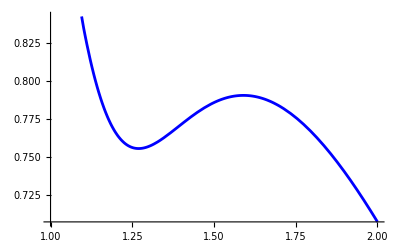

```mathematica
plotvODE=Plot[{v[r]/.repv/.sol},{r,Rmin,Rmax},PlotStyle->Blue]
```

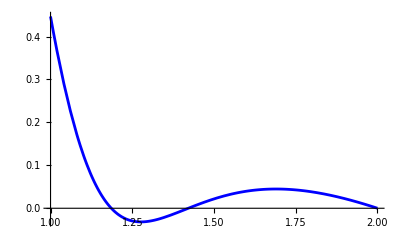

```mathematica
plotσODE=Plot[Evaluate[σ[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

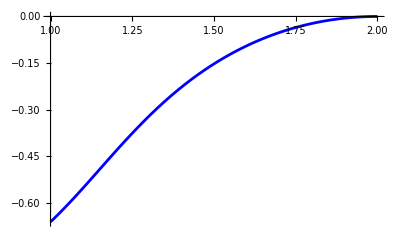

```mathematica
plotzODE=Plot[Evaluate[z[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

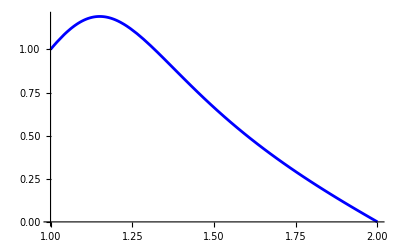

```mathematica
plotωODE=Plot[z'[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

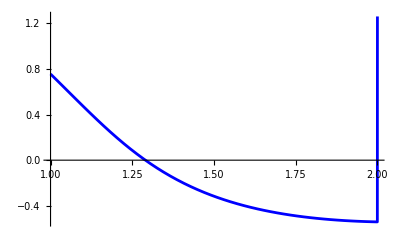

```mathematica
plotμODE=Plot[H[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
delta=1/100;
```

```mathematica
(*Compare with the solution from FE*)
```

```mathematica
(*check of v*)
```

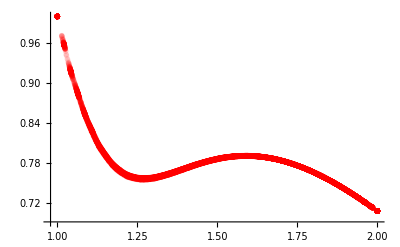

```mathematica
tabv=Import["~/Documents/finite_elements/steady-state-flow/solution/v.csv"];
tabv=Table[{Norm[{tabv[[i,4]],tabv[[i,5]]}],({tabv[[i,4]],tabv[[i,5]]}/Norm[{tabv[[i,4]],tabv[[i,5]]}]).{tabv[[i,1]],tabv[[i,2]]}},{i,2,Length[tabv]}]
plotvfe=ListPlot[tabv,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

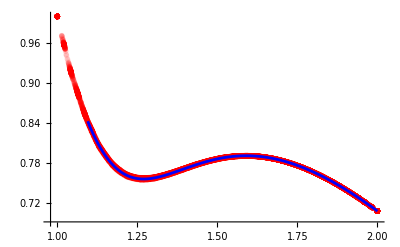

```mathematica
Show[plotvfe,plotvODE]
```

```mathematica
(*check of sigma*)
```

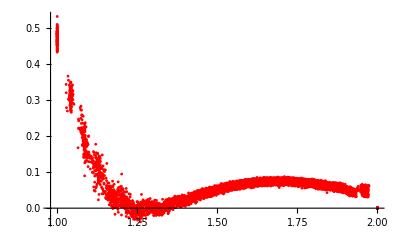

```mathematica
tabσ=Import["~/Documents/finite_elements/steady-state-flow/solution/sigma.csv"];
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,2,Length[tabσ]}]
plotσfe=ListPlot[tabσ,PlotRange->Full,PlotStyle->{PointSize->.005,Red,Opacity[1]}]
```

```mathematica
tabσ005={{2.,0.},{2.000000000000001,0.},{1.9580004763595418,0.0521859381441542},{1.961234891646681,0.051623810358102484},{2.0000000000000004,0.},{2.,0.},{1.9566600043151867,0.05206301230562837},{1.9135062016770663,0.050397200778905506},{1.9184375352757854,0.050639350289041936},{1.9226841247590132,0.047110071149691235},{1.9600473564541412,0.05511531338267319},{2.,0.},{2.,0.},{1.9519940175796804,0.05333444718072099},{1.9068091600193289,0.051971199675292436},{1.8669104707152266,0.06303756242986122},{1.873870204520627,0.06059243838212999},{1.880734270542621,0.06064819924928635},{1.8895539634002358,0.056486006240036024},{1.927870700312137,0.04578389818620076},{1.9578770912264456,0.05161572362494146},{2.000000000000001,0.},{1.9518306161134442,0.053419724929085824},{1.9040016955817956,0.05125712044808748},{1.8615957352183128,0.0648511238190608},{1.8210524281672553,0.06698199650948951},{1.8273865098157407,0.06845646100200123},{1.8349334076892736,0.0645106808276191},{1.8439218575616558,0.0660689415876146},{1.8545119367393428,0.06341177374288622},{1.9090797927598628,0.05270620928164261},{1.9566600044453186,0.048613691388084676},{2.0000000000000004,0.},{2.0000000000000004,0.},{1.8993953083718154,0.05705407827729407},{1.9332483741124227,0.04668497668601041},{1.972200341135825,0.0512680981540564},{2.,0.},{1.8569858166158346,0.06360360325683809},{1.8159874021130602,0.07016486712076586},{1.7753349230387632,0.076139036537886},{1.7812113682656998,0.07388634734049082},{1.7884367196957367,0.07298455909258492},{1.796997394168342,0.07269778572110425},{1.8069559692721293,0.06839150241185632},{1.8181977221637757,0.06627920202501865},{1.8657391155370233,0.05943494685535118},{1.9128633963809245,0.04955357509874574},{1.9576343118813158,0.04991933036738933},{2.0000000000000004,0.},{1.8536004841473335,0.06432676321726172},{1.8121673591975171,0.07301557791660293},{1.7708430072890504,0.07354273270603714},{1.7299165462955497,0.0781858371016803},{1.7352186610040252,0.07551579738796564},{1.74193280053893,0.07602454662604274},{1.75004248932324,0.0747572742631117},{1.7595284360960846,0.07240595878055167},{1.770369144357824,0.07401469487341475},{1.7825389120540371,0.07377354388318322},{1.8307287939346046,0.06375963305695546},{1.8768038854974123,0.05842669816754454},{1.920107516053376,0.046948147219850245},{1.9598993986850575,0.0496532010598295},{1.9999999999999998,0.},{1.8935766666911398,0.06116819136559455},{1.9278508840381057,0.04903959353750438},{1.9648482089639046,0.053817929029382906},{2.,0.},{1.809825374692291,0.07125666158710806},{1.7677709096909922,0.07548744614984067},{1.7260391503900059,0.08047524700721828},{1.6847494131777399,0.07733762694192378},{1.689457111684066,0.07944551962715758},{1.6956194998497556,0.08003433458994473},{1.7032201022615647,0.0772311025252929},{1.7122390064046868,0.07841854307282235},{1.7226553453236497,0.07724772007803524},{1.7344438936761426,0.0718578976438223},{1.7475755226016687,0.07261117812886372},{1.796011095495905,0.06785966658171882},{1.8441879310182823,0.06520289849009224},{1.89109842129322,0.05303444771080714},{1.9262377967147803,0.04407999185249057},{1.9548812428795102,0.05006204328106034},{2.0000000000000004,0.},{1.8524353118926407,0.06611814768448501},{1.8953271630345643,0.059795688521620385},{1.9268574715561273,0.049434744765036814},{1.95997406866018,0.055656736367625706},{2.0000000000000004,0.},{1.7660871122135515,0.07677485084463365},{1.8089521867709357,0.07422919683470951},{1.852140011527987,0.06553024694672158},{1.895727708168219,0.06025249809287528},{1.9234664105327064,0.049905614479602275},{1.960623062582484,0.05760714609905698},{2.0000000000000004,0.},{1.7235961737468244,0.07915944281662289},{1.681507600101234,0.07840260582836232},{1.6398540591726445,0.08017743516892648},{1.643934211205049,0.07864009006035465},{1.649511965337754,0.07473438011588376},{1.6565744954073758,0.07623932378441593},{1.6650996600865342,0.07681462905893918},{1.675066411874324,0.07391706460467116},{1.6864486191926447,0.07675430191674516},{1.6992222567809812,0.07791892888086603},{1.7133495635360045,0.07427381213441657},{1.762020620981566,0.07273939953860017},{1.810756584413714,0.06579280755906305},{1.8595525769240562,0.059128053321619196},{1.9084039474984977,0.051759503262106786},{1.9255471510726119,0.0407695475640848},{1.9665523852434117,0.046816808412238446},{1.9999999999999998,0.},{1.7658063877277592,0.07608495697669061},{1.8093310253574715,0.07315915722926297},{1.8530175079920086,0.06863455414996861},{1.895975253196426,0.06074177250539947},{1.9246085082197195,0.050076869844533425},{1.9602667182681117,0.055686670779851594},{2.0000000000000004,0.},{1.7225938694577718,0.08073885139894316},{1.6797395973369325,0.08033520775146878},{1.6372821656969876,0.07825109431260636},{1.5952537494496546,0.07289918238839796},{1.5986712271126322,0.0706853169366393},{1.6036312481036592,0.07546899204324793},{1.6101217944634747,0.07677104213310912},{1.6181245832983004,0.0740242140717841},{1.6276150427820317,0.07592342008457538},{1.6385657035378984,0.07636688151681288},{1.6509517384681425,0.0728760067352301},{1.664741427958405,0.07275876040217572},{1.679895665552002,0.07483813324965446},{1.7287984797814202,0.07278462484719696},{1.777747856704201,0.07017093047083647},{1.8267447486830175,0.06384581381891759},{1.87578675384126,0.0585471302643729},{1.8931972085270505,0.05332240063093027},{1.9537600185876993,0.04770090908013007},{2.0000000000000004,0.},{1.7669495248549207,0.07921717839425653},{1.8111240384795813,0.07186197249255649},{1.855682216723727,0.0666831394792541},{1.9004576337580568,0.05946378638928139},{1.9490751276577991,0.0585932300113629},{2.000000000000001,0.},{1.7230345572940564,0.08107996497742183},{1.679451768574552,0.0790571246340519},{1.63622733763081,0.07933433893484496},{1.5933910663115864,0.0751451636913021},{1.5509741300057658,0.06686448946641599},{1.5536890725274597,0.07173115120989294},{1.5579936921298698,0.06940202631485622},{1.5638786992061733,0.06441263942808766},{1.571325858263456,0.06741860872222258},{1.5803094847704302,0.06918602052349013},{1.5908074746501835,0.06818304385280828},{1.602783792598586,0.06989169903460213},{1.6162172890248783,0.07432052660449456},{1.631062106841764,0.07360818749776084},{1.6472839550975917,0.07000444477936767},{1.696383800852857,0.07577203989944274},{1.7455374099388137,0.06995205180438938},{1.7947186067021448,0.0701706708042606},{1.843937875610925,0.057574442052308876},{1.8635728931346884,0.06146600612789853},{1.919343083321284,0.041502421152690344},{1.9612915628575636,0.0448051821268515},{2.000000000000001,0.},{1.7694882510650434,0.07846498760201394},{1.8143348820307534,0.07503611145903925},{1.8594372751072752,0.06572325697538113},{1.9047771660685788,0.05555856448783584},{1.9562085179683735,0.058353686759160195},{2.,0.},{1.7249172639326333,0.07907006179280722},{1.6806438105215165,0.08134146240066528},{1.6366916995829417,0.08134735267073061},{1.5930881283824554,0.07247776454004994},{1.5498606670249,0.06912999875500395},{1.5070434513414745,0.06080756224368222},{1.5090127633421158,0.057003606951488144},{1.5126207206712927,0.05404289333239841},{1.5178650887110923,0.06186988088031757},{1.5247204803882943,0.06438476753023371},{1.5331630521929744,0.06213101891612961},{1.5431808703394838,0.06338617136025525},{1.554728436498652,0.06716597260485743},{1.5677774892538632,0.06545601654418023},{1.5822932852514593,0.06335603039410606},{1.5982321856120614,0.07038671165372491},{1.6155531819658764,0.07273292073322338},{1.6648415539912602,0.07211354878998037},{1.7141656263050489,0.07281743523967442},{1.7635175191467587,0.07046267843061257},{1.812898128311207,0.0618324461228045},{1.8322637535021733,0.0644802130727555},{1.881759504636489,0.048843439710269554},{1.9209951545832151,0.0429464787141854},{1.9574983880723922,0.04347794376530617},{2.0000000000000004,0.},{1.7282371719194185,0.08199083353940073},{1.683312597707584,0.08317537743709201},{1.6386738147187259,0.07825473009348567},{1.5943448110109792,0.07493311353777606},{1.5503519176212774,0.07220083356118591},{1.5067218342928388,0.055807873629875396},{1.4634947380960588,0.049066347086318254},{1.4646735692509874,0.04664122079850716},{1.4675472031344214,0.05448554023549794},{1.4721048315995773,0.050931097018859464},{1.4783309183139575,0.044737204177204774},{1.4862052796554128,0.04754913186699073},{1.4957013755914783,0.053329736145626805},{1.5067885445159617,0.05238429763182739},{1.5194319944328234,0.05355266416230263},{1.5335940548803848,0.06268775803906042},{1.5492316407971882,0.06350316682606162},{1.56630106899337,0.05900775145437596},{1.5847561429022499,0.06651341352537887},{1.6342131301277405,0.06834927443816331},{1.6836941267154002,0.07457680494859072},{1.7331975782488382,0.07035402738577552},{1.7827212371683279,0.06901563636390219},{1.8030996398108223,0.061549559178423946},{1.8527680807766593,0.0582307943350366},{1.9097219802551326,0.04947262902528285},{1.9587075440644564,0.04127532171411118},{2.0000000000000004,0.},{1.7734258510442271,0.07643415757535063},{1.8188589990657436,0.07403861058851245},{1.8645187842469029,0.07039257718464192},{1.9107277039825292,0.05565545243778431},{1.9579843917462592,0.06088119109968709},{2.0000000000000004,0.},{1.6874513001892262,0.07971550449289726},{1.642168141924943,0.08077041971625316},{1.5971580928886082,0.07854885698215433},{1.5524444623958034,0.06802110671324214},{1.5080507573101176,0.058831870951672444},{1.4640140314709622,0.054412075018256845},{1.420361869364933,0.03129595100065695},{1.4207021116292056,0.03904474942289541},{1.422790783332421,0.031859932243999974},{1.4266203033338667,0.029057402343710695},{1.4321766828813987,0.03928335326981713},{1.439439780741265,0.04517256023507547},{1.4483842064272678,0.04139984641791135},{1.4589789303354492,0.04184346311849896},{1.4711882696571843,0.04998862211896675},{1.4849724255909225,0.0480661908245876},{1.5002881152885728,0.04556386563633916},{1.5170887318625217,0.056711211432044016},{1.5353255995305355,0.061236562513739684},{1.5549482028783541,0.0562115629439233},{1.6045490730833127,0.0700214180044375},{1.6541659668896707,0.07189120818083526},{1.7037974717050173,0.07011402871440432},{1.7534424599702634,0.07173192163073036},{1.774857486424695,0.0663383140724117},{1.8246132362998628,0.06363001781154577},{1.8743749642505767,0.05255986024913721},{1.9225712168791618,0.0400027041279335},{1.9637481011760871,0.04343809364701501},{2.0000000000000004,0.},{1.732986083173113,0.08310013543364855},{1.7787530875053599,0.07852161393093542},{1.8246804549888236,0.07161985568395116},{1.8709159048766848,0.06765844337678499},{1.919282519928962,0.056367294378323794},{1.9665247261860666,0.060200617469649456},{2.0000000000000004,0.},{1.6930491180097065,0.08220460821874917},{1.6471651770145663,0.0841846821135509},{1.6015194789801763,0.07479737109367407},{1.5561333532037818,0.07053739504083195},{1.511025984945738,0.06447018937777044},{1.4662296243664041,0.04854226969558022},{1.4217714273373552,0.03427678170495743},{1.3776825584926775,0.03302982481175332},{1.377131463731579,0.023072916955969205},{1.3783849241266959,0.02250621698210971},{1.3814374648074619,0.03295458102924632},{1.3862780675445356,0.027758694762443137},{1.392888072713807,0.01769402811238146},{1.401242921176633,0.020424742231119154},{1.411310688274351,0.030077091903309927},{1.4230554798880217,0.028892923412144132},{1.4364360235598599,0.02910491812534524},{1.4514073456762566,0.043004144647603514},{1.4679205000986975,0.0451110793204265},{1.4859241445229505,0.03983105730938448},{1.5053648029782674,0.051318108756210644},{1.526187578631373,0.05891947462044543},{1.5759047492245821,0.06433883116900435},{1.625631054869285,0.06575720113771455},{1.6753657336380505,0.07342141227668282},{1.7251081324664304,0.0709960716212426},{1.7475820259710841,0.07009261834670788},{1.797401090651014,0.06558766920665597},{1.8471057177699373,0.05664026085321477},{1.8937131461886065,0.05034031693914287},{1.9334178384543694,0.03875302822014674},{1.9616290296448824,0.04135704147469089},{2.000000000000001,0.},{1.7391522968620894,0.08021383663298814},{1.7854577047276436,0.07982762445330441},{1.8316235839055748,0.07314153857423143},{1.8766597272471268,0.06581838316960203},{1.9135276734777271,0.05899130079140763},{1.9567552187037838,0.06314264085344758},{2.,0.},{1.6536513857512758,0.0802776694324178},{1.6074164271867866,0.07714307560166597},{1.5614047284260548,0.07568283695382866},{1.5156349354305627,0.060420797612699875},{1.4701342624211597,0.050588444783774604},{1.4249256666602474,0.04317830431074567},{1.3800374328483398,0.023390998740403963},{1.3355015603309857,0.008513726168196867},{1.334001032958806,0.00792298078101788},{1.3343613769487603,0.016878011956694215},{1.3365853982364293,0.005537996315636959},{1.3406618071632577,0.0014290841361046368},{1.3465734368424582,0.015817265053127173},{1.3542958625653787,0.024995774726981026},{1.3637992958385505,0.01808853338626261},{1.3750458500514793,0.016177960680129083},{1.3879938586789564,0.027124980732817685},{1.4025958470519782,0.02490708873971432},{1.4188009456101074,0.019715725533074775},{1.436554751050551,0.03539580854483276},{1.4558006753749835,0.04278014991394159},{1.4764803730184608,0.0347141654008089},{1.4985345710458517,0.05030935072538992},{1.5483367227915885,0.05170318544780559},{1.5981428785755485,0.06933926781216802},{1.6479526702263803,0.07051216903544534},{1.6977658053252647,0.06861992832074207},{1.7213192022822952,0.07055787350910497},{1.771174920882123,0.06472006410580895},{1.8210313202505795,0.059912265048037594},{1.8701949831869835,0.054691451137169556},{1.9198933562876526,0.043571446554524364},{1.9611692761046176,0.040555883246881},{2.0000000000000004,0.},{1.700091652600389,0.08484938169339942},{1.746720802750066,0.08052083188966615},{1.7935241774615531,0.07767170391917326},{1.8404883696629046,0.0722463198449999},{1.8859332301748832,0.06843802054274735},{1.9304355591012279,0.0503882399239383},{1.9710883020719607,0.06342640234821514},{2.0000000000000004,0.},{1.6148325733878033,0.08198022560778878},{1.568245866092878,0.07245114293904358},{1.5218649584434525,0.06236468096945738},{1.4757143536156097,0.05883637659066711},{1.4298127971676822,0.03758565014556986},{1.3841853280373353,0.025555732755014344},{1.338858823588481,0.022482304830733255},{1.2938677152291167,0.007263528181965757},{1.29135909871623,0.015434713553843134},{1.2907688486655726,0.0040544924598432605},{1.2921032115014845,0.005434643414910737},{1.2953599024534468,0.017745551265411576},{1.3005212128709867,0.011785143471571398},{1.3075653835976961,-0.008430171255858855},{1.3164621124233364,-0.005853679935552122},{1.3271734754576945,0.007802953514332134},{1.3396559632936629,0.0041565537743079115},{1.3538611763416752,0.003596598421319005},{1.369735276609902,0.019345563850307623},{1.3872208586923558,0.02373633522591544},{1.406257842746142,0.012435749385529007},{1.4267841952982776,0.03168370964611365},{1.4487367613557174,0.037911378579157065},{1.4720516173834177,0.03255490583623492},{1.5219034764110493,0.05595502603711127},{1.5717562165326138,0.06399277400039147},{1.621609800427955,0.06258248123576132},{1.6714641046340564,0.07302436539933282},{1.6961158381880506,0.06621619668472552},{1.7459792642240426,0.0696600447154181},{1.7958427982534688,0.06577717328181293},{1.8457065324300834,0.054823072338761755},{1.8911110409450833,0.04939573129036924},{1.9306521130775178,0.038516787089811926},{1.9599729738641545,0.04221604985255123},{2.000000000000001,0.},{1.6616093772537435,0.08161780679645918},{1.7085610199861168,0.08281092390544854},{1.7556734719639628,0.08128647702817687},{1.8029340246496053,0.07708509260298683},{1.85033137255564,0.06960316093647234},{1.899208506374643,0.0633571655273316},{1.9552524470900012,0.061530145896285623},{2.,0.},{1.5766355524435993,0.07302787182554558},{1.5296967136008253,0.06974969000386193},{1.4829508198609713,0.05543566337046118},{1.4364151292962266,0.03875015019295709},{1.39010986037765,0.036833864736032104},{1.344055833369712,0.013487205359149025},{1.2982896721519532,0.00203417672614023},{1.2528320028644224,0.01238431771119855},{1.2492466811480079,-0.0002318675205730536},{1.2476427858886054,0.00571885907257573},{1.2480283879153966,0.005988844686318905},{1.250405624981412,-0.0027082943092063758},{1.2547617229831007,-0.0164885731469077},{1.2610756942064882,0.003982835634719774},{1.2693186495199702,0.019688179747252746},{1.2794532352388819,0.0015476712081189045},{1.2914345921779697,-0.0003516118345075585},{1.305212103379472,0.006327883233675561},{1.320729563538029,0.0037618846857404038},{1.3379264016834167,-0.00739000853608489},{1.356738702706631,0.012931003071350812},{1.377100177037117,0.01952419135406353},{1.3989436239360704,0.009784660008580562},{1.4222007387989928,0.028732561959478493},{1.4468029985684383,0.03621658925112603},{1.4966651328713259,0.04818240524294838},{1.546527518737555,0.05032020643446523},{1.5963900143786003,0.06765232701255502},{1.6462528647235943,0.07030769291545816},{1.6720197949415248,0.0714145787996752},{1.721858262256333,0.07087296518360141},{1.7716950963697449,0.061568205390223764},{1.821541939976274,0.06202079232689314},{1.8703743329940743,0.05406896455291601},{1.9159492905604825,0.039000414475549035},{1.9502382940713157,0.04250550532137997},{2.0000000000000004,0.},{1.623746647461917,0.08047656822231315},{1.6710181194274456,0.0830732705625851},{1.71843622333334,0.08396824003693895},{1.765989219867094,0.07887046503399929},{1.813666437849364,0.07651240927763808},{1.8614584444528302,0.06827293240587169},{1.909627142870503,0.0568253274744615},{1.9569116073200366,0.060497508494881926},{2.000000000000001,0.},{1.5865472772733986,0.07666055037765551},{1.5391047103928863,0.06996506683796119},{1.4918197025311046,0.0553886697154847},{1.4447094061576147,0.04916611618186646},{1.3977899127666893,0.03344161127041785},{1.3510807053616352,0.011807136990957588},{1.3045850940688992,0.02249632463697916},{1.2582614124998364,0.007410261048319003},{1.2123803195104863,0.015976094235782286},{1.207726095218269,0.03568955398067609},{1.2050360055693803,0.02484221558106156},{1.204404110819614,0.023178361620681962},{1.2058610717437124,0.02720328931306351},{1.2093264344828423,0.034912276564017096},{1.2148536456269763,0.02875404630437617},{1.2223914286251767,-0.01033218636672411},{1.231902921292131,-0.008773501156134754},{1.2433427701758986,-0.0045865227268836115},{1.2566583394963768,-0.0051254716692582455},{1.271790683523282,-0.013516649636710627},{1.2886758736928488,0.004588703795564114},{1.307245980094149,0.004327639966061524},{1.327430049709805,-0.011297659772620976},{1.349156169679949,0.008152002180727841},{1.3723508558331974,0.016127522254349207},{1.39694113608487,0.008327817360197434},{1.4228544204129465,0.025417711782698513},{1.4726831539733518,0.03208297226879591},{1.522514297917251,0.05540190242485637},{1.5723476122633357,0.06223916402229055},{1.6221826468164804,0.06198902794684493},{1.6490803817063244,0.07015155606099635},{1.6988603643183882,0.06422132164674535},{1.748639871435524,0.06958700192009837},{1.7984075488419946,0.06370614817298875},{1.8480633615709328,0.05165873645895723},{1.8969169275725142,0.04903942674832999},{1.919618230659053,0.036955351636844776},{1.9660321907094935,0.038444097384911724},{2.0000000000000004,0.},{1.6341342823330496,0.08268965541140391},{1.681853051217046,0.08157434382337074},{1.7296929994999788,0.08351929128836175},{1.7776442183520513,0.08022357691900615},{1.825696481060948,0.07283601195362471},{1.872982249380672,0.06752685053895392},{1.9185688332660527,0.05307417065785568},{1.9595314990621286,0.0607931201291693},{2.,0.},{1.5979554778665548,0.07597120829226202},{1.645967632357089,0.08350801196763433},{1.6940870452593055,0.08411609091121372},{1.7423046969071485,0.08016112468330448},{1.79061261844038,0.07857558479624914},{1.838993048662697,0.07302548183240692},{1.8874719868649639,0.06362522408327177},{1.9265746939400576,0.05140076524238681},{1.95843800280216,0.05758489888210098},{2.0000000000000004,0.},{1.550059794430782,0.07246425160918946},{1.502292572578871,0.06015329221113475},{1.454666635114406,0.05170384319606433},{1.4071957767942445,0.03019968997147592},{1.3598962519960138,0.025835558471415047},{1.3127889219307332,0.01515414347427805},{1.2658458964472477,-0.0065058995175323805},{1.2185816754338468,0.018384724976145364},{1.1728923931522655,0.07497460708153345},{1.1668775663936661,0.042038065680616854},{1.1633561100531,0.045046293809334274},{1.1613836214598696,0.06999465629586529},{1.1618406368583092,0.05513065612044839},{1.1642536959477403,0.03548937699239286},{1.1689308724106406,0.04033262723791463},{1.1757059529640304,0.043433546500572504},{1.1845429846411306,0.02661838775933799},{1.1953962261005664,0.05886963387582355},{1.2082113379160084,0.008707866987494615},{1.2229334480049383,0.014867227605525717},{1.2394802631904014,-0.0014373705458855662},{1.2577826397467087,-0.025194094649962535},{1.2777753165286254,0.0002567361113733832},{1.299374599563795,0.0000855575288756169},{1.3225022798937671,-0.011391972540071552},{1.3470796308523962,0.003640199849500797},{1.3730282952948074,0.018453070690228397},{1.400272476880294,0.005073599805578309},{1.450019838436106,0.03896320315339832},{1.4997750517312445,0.04495522710773638},{1.549537305205504,0.05161037864429488},{1.599305841207574,0.066019046236329},{1.6273461627464718,0.0622050856466281},{1.6770297476008087,0.07047561399927306},{1.726723899852382,0.0696533485006509},{1.7764227803049029,0.06035760783371688},{1.8258034068505598,0.06083579158577764},{1.8740346801150705,0.053835455852496925},{1.9005529024399002,0.0467055782432512},{1.9532439258717347,0.042557707499634806},{2.0000000000000004,0.},{1.6108264385172768,0.08038329971583845},{1.6592156299335425,0.08111045091913636},{1.7076899696832548,0.08443949202776589},{1.7562421205513077,0.08162556724617821},{1.8048565926114983,0.07370965470596742},{1.8534991308159865,0.06979579794430339},{1.9094400169272785,0.058331623699843904},{1.9568231633106086,0.05630744258532158},{2.,0.},{1.5625302508495351,0.07487442621911865},{1.5143350378595877,0.062106740206840934},{1.4662526882330498,0.054213390605436354},{1.4182932468808653,0.036002205312905974},{1.370469739820142,0.03096171399639438},{1.322796997569222,0.007421624201292396},{1.275350408161165,0.006687544517534429},{1.2283681032212794,0.038180185998686826},{1.1765829664497556,0.041962881353856195},{1.1390232861936556,0.09144701208177884},{1.1267223273836835,0.09533385773449887},{1.122171658768665,0.1538963489461675},{1.120159981391478,0.12546159214390634},{1.1185046964365883,0.10355499356892114},{1.1204370604741394,0.14621398592565513},{1.1233441685158532,0.12457830231268828},{1.1297605925125527,0.0814615633581114},{1.1332547951276923,0.1434797139660909},{1.1484885724164555,0.045147594825422036},{1.1598845267128386,0.029430933996334216},{1.1741467938893018,0.029375080745086386},{1.1903627235017724,0.0039732422921697624},{1.2083522881733353,0.03702109407009017},{1.228137448807829,0.0008568004449962044},{1.2496000453530722,-0.019314641930871186},{1.2726552673005058,-0.008589735891676206},{1.2972183038016636,0.0018241724156494617},{1.3232051288805204,-0.01764048029934929},{1.3505338354564613,0.005470703512944129},{1.3791237455315635,0.017727448183942764},{1.4287379638519333,0.02623591201829671},{1.4783684579536203,0.032359251496960506},{1.5280142234827192,0.05623192874233621},{1.577673876375548,0.06088670108332557},{1.6068655181424467,0.06689050327249474},{1.6564131090027423,0.0679060475943162},{1.7059792818992559,0.06497733094229707},{1.7555622072440233,0.06725515731589984},{1.8051606829286704,0.06268660712503485},{1.8540597292289593,0.04993217048216783},{1.8821823217960185,0.05064297503711526},{1.9212996370580793,0.035938883918314034},{1.9586511919621477,0.0392000407561679},{2.0000000000000004,0.},{1.62512596187481,0.08195698621062399},{1.5764795199867538,0.07374459136532416},{1.5279111852070784,0.06771926782029233},{1.47942960002618,0.05694140038142638},{1.4310430283074669,0.04040674807336598},{1.3827615328268563,0.032320610794557926},{1.3345966100992133,0.00997376063138839},{1.2865607036337716,0.019603126568669124},{1.2386698669948508,0.012273152165845576},{1.1933006798595203,0.007650714431562185},{1.1569494855188758,0.062479418595926386},{1.1291470833071555,0.11964815012051815},{1.0917774061692405,0.18937312885223528},{1.0817582483961088,0.20366338042558413},{1.079940403771207,0.17801920170538849},{1.0793061244076734,0.23616118363304694},{1.0799151518002617,0.21327243863200218},{1.0806776444518753,0.19047880359981867},{1.0831851355480184,0.22395635686847598},{1.096488559614902,0.11540538691804358},{1.0867303876697978,0.1961886518622966},{1.113948768271574,0.05905429396554237},{1.1096924000401094,0.13346464713923928},{1.1267186119593626,0.1381128046303654},{1.1414511732795405,0.09590188468994755},{1.1585706387439787,0.03744605855921134},{1.1785186978510396,0.011860706939672103},{1.1998327550680241,0.011067462019484102},{1.222809658851777,0.018289580924967165},{1.2473575246830457,-0.02767474376883891},{1.2733891730491662,-0.0036871382958968343},{1.3008091026632351,-0.0011846673090880888},{1.3295293747558494,-0.016375136298444302},{1.3594702101607052,0.005864780751829293},{1.4088960255481293,0.009372700012947852},{1.4583515867396337,0.037822677875327254},{1.5078334753619351,0.04675662199522543},{1.5573383247200248,0.05161024021843723},{1.5876872447552635,0.06131333633155077},{1.6370558044164603,0.06250390336435364},{1.686453667157667,0.06991664873133409},{1.7358783533144573,0.06701739947228424},{1.7853276008998296,0.06043344975213548},{1.83479913602543,0.05843801656404327},{1.8653001007131895,0.049689927408848124},{1.9150273269926816,0.04112641369472035},{1.9605540793518341,0.03829231323637512},{2.000000000000001,0.},{1.6738447795644047,0.08418394457769017},{1.7226294074012158,0.08064799591380782},{1.7714739760424296,0.08126164608329726},{1.8203739670242078,0.07345909238833542},{1.8689767724134776,0.06510585378017854},{1.916586304712508,0.05504952376055309},{1.959244891290156,0.05800087000581252},{2.0000000000000004,0.},{1.5918688436474737,0.07907334515022924},{1.5429799116291063,0.07110032289400134},{1.4941551117761147,0.05773938173463776},{1.4454013911461845,0.04850082039232849},{1.3967262050238896,0.03254672772481116},{1.348137834784704,0.01812598275442227},{1.2996461404658046,0.016569977874426153},{1.2512627805584569,-0.0023126866777346752},{1.2030003440162114,0.02496754838050552},{1.1548739314859167,0.12422111749783935},{1.1240455991157985,0.10590598883455443},{1.0863378825887624,0.19595843326883922},{1.0430595436274912,0.33024633407223736},{1.041356377884613,0.3304981304218061},{1.0414668086209928,0.3496904905823384},{1.0396786927821495,0.3360288166130089},{1.041011119888629,0.3233512350037937},{1.0400338331310874,0.323334620628214},{1.0416814713951117,0.30659233345412207},{1.049086041463548,0.31518052010868336},{1.042870406824957,0.28441082237397003},{1.0523831624578772,0.28857423839809737},{1.0812418312221423,0.255225891733813},{1.6408171881235794,0.07967086496155647},{1.6898194872294883,0.08535251417865379},{1.7388709113217427,0.08144235395937077},{1.787967169701116,0.07780933001028151},{1.8371048900536409,0.07274122006711836},{1.8837582728569928,0.06373297854606162},{1.9243792642909379,0.04915537004023989},{1.953199134267596,0.05911534115140781},{2.,0.},{1.0838501363083983,0.1739025841400776},{1.0889610380939727,0.1447084160421906},{1.109608347282958,0.09965525928076785},{1.1264522341508176,0.1509429202797499},{1.1535500591124899,0.062481580620018094},{1.1733625217122299,0.017147807069648947},{1.19749705615949,0.0071788250227700565},{1.2235696332413566,0.009465339739696897},{1.2511078984404627,-0.03322985908907628},{1.27995962974415,-0.0043910498208677914},{1.3100828026365612,-0.005381837840054419},{1.3413905213254347,-0.006949562128172608},{1.3905516542020495,0.015166607792095149},{1.4397752242193707,0.028950816571681758},{1.4890409904495034,0.03588419030505875},{1.53835078373393,0.056106129692177445},{1.5698590754597086,0.05379260772971384},{1.6190033433446396,0.06663285933436192},{1.668190462297144,0.06696339427802149},{1.7174168062039346,0.0645946697312464},{1.7666790879741143,0.0655914199834273},{1.815974396411327,0.05864506218595565},{1.8474589446678555,0.05415946053101073},{1.892798902102114,0.0485327013171624},{1.9306998533439037,0.03525378001552705},{1.9614337145370329,0.03788391386102859},{2.0000000000000004,0.},{1.5594976830881826,0.06967238812657046},{1.51038406796008,0.06580024514874781},{1.4613210451544123,0.05121240608375059},{1.4123142508990567,0.035115185172296504},{1.3633696075190593,0.02734889914892776},{1.3144941761057847,0.010879342188242932},{1.2656961093871015,0.0035866051221049855},{1.2169845677818252,0.04570088376019851},{1.1692531878017374,0.03964433305658594},{1.1277119863775862,0.07755189852438196},{1.0943597267318204,0.17791057183863312},{1.043410773078819,0.32756021285265285},{1.0000000000000002,0.4769534444981998},{1.0000000000000002,0.47338764844831027},{1.0000000000000002,0.4592782530123569},{1.0000000000000002,0.4994615916504497},{1.0000000000000002,0.45024208186162273},{1.,0.47608257730477704},{1.,0.4810940093573986},{1.0000000000000002,0.44218032358833653},{1.0000000000000002,0.4910613955653591},{1.0000000000000002,0.46467546809675775},{1.0000000000000002,0.4929304018272681},{1.044130410887855,0.29413259059368363},{1.0428704068589274,0.3381219460476956},{1.0651185652366975,0.16768514121267347},{1.0914207808621768,0.17876143576789574},{1.1157702015648192,0.04998599360738712},{1.1286932460632784,0.07991397854079257},{1.147636853831154,0.09057481797932154},{1.174523442396168,0.007596647396582411},{1.2015055863627633,0.019764550780677848},{1.230423284090668,0.003831576981224022},{1.2607345882627081,-0.02773129519222519},{1.2922721261305583,-0.00962918368255411},{1.3249424644129688,-0.006280557617231076},{1.3737922443265116,0.005469748432072733},{1.4227102249560608,0.018058013501921613},{1.4716969983179018,0.0369383880785078},{1.520756280429314,0.04936039880866274},{1.5534275740966996,0.05565702900970178},{1.6022998395851287,0.06272315715312343},{1.6512313972846449,0.06295341284750147},{1.7002174881610164,0.06892681396626223},{1.7492534726797255,0.06467915798934283},{1.7983351980173414,0.05859307729054977},{1.8308023281444379,0.05654843220536843},{1.8785200870677505,0.046850233611204994},{1.9222830123391759,0.03601281911663946},{1.9585427521825771,0.036172829313199845},{2.0000000000000013,0.},{1.6086579390399702,0.08179063110300082},{1.6578604434521418,0.08262296823627426},{1.707101945417322,0.08244554478587572},{1.7563783403336755,0.08124892301065026},{1.805657615556867,0.07522485545426338},{1.8539710185278149,0.06741439886937184},{1.9020225994408269,0.060399731134272966},{1.923833774790291,0.04736945407786603},{1.9652819643965413,0.056438148231862585},{2.000000000000001,0.},{1.0741189635546238,0.2834345886095219},{1.5280682646233759,0.06975762517649006},{1.478751371421748,0.051744115616295494},{1.4294723928721915,0.046303866620753455},{1.3802355654965188,0.027424047900388798},{1.3310455146751696,0.012332489375528657},{1.2819076821021347,0.016788420557691648},{1.2328282866014468,0.010360295112982476},{1.1838476146821721,0.030472253039102386},{1.1365396106890586,0.11447261059189774},{1.0860607457818814,0.23162508885664618},{1.042490290596704,0.315679085201666},{1.0000000000000002,0.4677890953378539},{1.577419557254447,0.0762998510586854},{1.6268025375459954,0.07951965281126705},{1.6762145444110013,0.0845209615707941},{1.7256523908907067,0.08288694295935625},{1.7751142504350237,0.07876311455669946},{1.8244227673705384,0.07336069812783302},{1.8737268744699802,0.06861532263946557},{1.895577143365759,0.06197429444002331},{1.9524117897452797,0.05932566026428568},{2.,0.},{1.0000000000000004,0.471097906195479},{1.0000000000000002,0.493728700503818},{1.0276788799800873,0.3437447419579759},{1.0438941343208128,0.3225413759229895},{1.085350571909452,0.22634379881618633},{1.0938451397939044,0.13064345167941413},{1.1283511884943904,0.1101206020264602},{1.1547916295942005,0.035798732016134274},{1.1815296588365742,0.005088413537498768},{1.2114371108663844,-0.0019139938404497334},{1.2432106091713815,-0.006350029131698617},{1.276165478422031,-0.020254660905659652},{1.3101837597235515,-0.009659269689538251},{1.358654721269716,0.0013178091634337042},{1.4072211774358854,0.01729101666048797},{1.455871869275984,0.03082377512844022},{1.504610416567934,0.04252669443253532},{1.5384382365500744,0.050825426423896966},{1.5869878567432332,0.0580859450332027},{1.6356175492248397,0.06527566621838334},{1.6843194091243807,0.06712386293479704},{1.7330876856666966,0.06298323074380965},{1.7819169272888606,0.06363570330771301},{1.8153231183296392,0.055837431595470964},{1.863801598772289,0.048931996376474954},{1.9133456593695088,0.04069352319552431},{1.9566600043769469,0.03436808311255034},{2.0000000000000013,0.},{1.497639749990345,0.06192942366233577},{1.4481450287699722,0.049612280505072964},{1.3986766282426253,0.028021444617714487},{1.3492374813799957,0.026846844698039708},{1.2998309092804772,0.007498258008131555},{1.2504608120992444,0.006046365713459921},{1.201137333582112,0.040725862385916155},{1.1524314606772201,0.08343295287314197},{1.1058618205728592,0.1444248450390071},{1.0670649817567353,0.24240285785874602},{1.0378075668545215,0.3413454818974694},{1.0000000000000002,0.44992096336031656},{1.5471581968421035,0.06802690717417405},{1.5966983536947972,0.08008908176077406},{1.6462583568579578,0.08277085108747326},{1.6958363109466794,0.08228081895820934},{1.745430668289643,0.08194033167433148},{1.7950401632375466,0.07810258106666919},{1.8446747746442205,0.06882100207337216},{1.8658461191033597,0.06740271174547331},{1.9176892147683873,0.054557197391025984},{1.9656142794331477,0.05758061671583807},{2.,0.},{1.0000000000000002,0.46296594996060375},{1.0000000000000002,0.4333645420126485},{1.0426544631614039,0.2813264686831085},{1.042933641218307,0.31177773854388163},{1.0847654336739303,0.1503140819673751},{1.117442589321702,0.11669492438557835},{1.1349257548795446,0.08422883199847064},{1.1620220893130677,0.04459362030664088},{1.194218732635652,0.00829766852543623},{1.2274761838782338,-0.013916559974175818},{1.2618232137753886,-0.016857384393447805},{1.2971769574668233,-0.006455070258602997},{1.345189305723531,-0.008102685070872062},{1.3933396222118974,0.010510380544331689},{1.4415959651329504,0.025196253896722046},{1.48997199937324,0.04003571551331253},{1.5249309878806359,0.047977708005255394},{1.5731081844842163,0.05735757596466351},{1.6213873468630295,0.06319036650062673},{1.66975976495289,0.06445866090780793},{1.7182176700034366,0.06630343691939708},{1.7667538565709278,0.0633558205972746},{1.8011716206617758,0.057917748147742594},{1.849037120857888,0.053328935001308204},{1.9035879681381134,0.04202548068023858},{1.9559495213963962,0.0357613513188376},{2.000000000000001,0.},{1.468274311170932,0.049503906283125496},{1.4186314877061346,0.0417226626743718},{1.3690047836315098,0.027103433513239326},{1.31939602548802,0.005765968532610223},{1.2698075279226062,0.019631792123484794},{1.2202417083322306,0.013710312041364539},{1.1707011941597298,0.04886918639656043},{1.1211894325005363,0.13938691794496336},{1.0760171154763236,0.20761326373363131},{1.03365625961562,0.36659276169054694},{1.0000000000000002,0.4840822609625635},{1.5179317094404021,0.0671916329003333},{1.567602318871955,0.0753287172088945},{1.6172850789607873,0.07827817491831396},{1.6669787240241776,0.08448086471411435},{1.7166825484172612,0.08406761142241181},{1.7663954905421875,0.0783723570772462},{1.8161169066962448,0.07609757843208174},{1.8383049237823454,0.07167242266731752},{1.8854636942349756,0.06809173986356311},{1.9225370263313615,0.05050494215083822},{1.9593224374176166,0.05962331684865439},{2.0000000000000004,0.},{1.0000000000000002,0.5006680253021085},{1.0000000000000004,0.4655342072828683},{1.043503631351039,0.3085409184356805},{1.0866382121989908,0.16143297945171398},{1.1135066256595179,0.11538036211501175},{1.1436171806679978,0.04828822688347795},{1.1788840996906633,0.022222073297819674},{1.213622381083191,0.0025201731330031646},{1.2493074444326429,-0.028344944712994924},{1.2859714525961494,-0.015035228369162837},{1.3334581619102255,-0.013057131109672302},{1.3811175687044066,0.014552825712318565},{1.4289198546802215,0.01893336094692371},{1.4768620866564008,0.036341790673921834},{1.512947285509594,0.04220078315097208},{1.5606984877997334,0.0546529937279136},{1.6085775143114827,0.06098768802963004},{1.6565736217705738,0.06514218344386428},{1.7046771850009232,0.06589896188519881},{1.752879137556412,0.062399233513488646},{1.7882594793636,0.06100341756002686},{1.836298682306961,0.05345774077567457},{1.8817105862307464,0.04665863926918484},{1.9219482097955836,0.03406103953855412},{1.956425179944956,0.03664566484772457},{2.0000000000000004,0.},{1.4400370936589075,0.04842677716183068},{1.3902802509678467,0.024958283185284126},{1.340531375951328,0.02320138580647234},{1.2907916211640433,0.009772984402989196},{1.2410619683256578,0.0018228741344792285},{1.1913438199569728,0.057103779410967635},{1.1416383618171189,0.08072380100934817},{1.0940949903124293,0.18260235908739894},{1.043114583322954,0.33937978832725585},{1.,0.47645392868328157},{1.4898011882956568,0.05858627578068758},{1.5395718575383661,0.06755290241780845},{1.5893484457889084,0.07832523756244497},{1.639130504567835,0.08346557630716507},{1.6889176574944047,0.08096056320480526},{1.738709337710316,0.08449567708957244},{1.78850517982386,0.07862860342997267},{1.8116451252319286,0.07705898390753697},{1.8611288009431202,0.06683404200576125},{1.9058297276070706,0.05906939478595101},{1.9524009141541938,0.06623075967716135},{2.0000000000000004,0.},{1.0000000000000002,0.489468194082172},{1.0401407604802886,0.2854091764415226},{1.073533849084823,0.21206044467299912},{1.089183127763515,0.15920255045196996},{1.129895747690462,0.09642528278414444},{1.1655947835011344,0.01489218155388631},{1.2017035335519362,0.01008788923353017},{1.2386737420288203,-0.0030162730802492793},{1.2766155022991168,-0.02863174175001003},{1.323502850655398,-0.002369949456187112},{1.3706034548122974,0.0014159159071898937},{1.4178837487876566,0.012531732537309246},{1.4653374818204976,0.036354224189054415},{1.5025248337167871,0.03944645677864125},{1.5497945719738435,0.055279193872137346},{1.5972222221008303,0.05863184217807936},{1.644793957350464,0.06401109076321022},{1.6924977796810645,0.065234144110022},{1.7403228802432393,0.06377554257816151},{1.7766530807471788,0.0605797552115799},{1.8243167153484188,0.05533452239036726},{1.8720951233359249,0.047762518686615976},{1.9154702036703422,0.036531369518725806},{1.958437747317857,0.03383147756948154},{2.000000000000001,0.},{1.4129957471750327,0.0381153722458907},{1.4628298592662263,0.048152979821613484},{1.512666019214253,0.06688712956418759},{1.5625040670287007,0.07285218479960483},{1.612343848632222,0.07878148743509474},{1.6621852342121004,0.08420546942154063},{1.7120281100935866,0.08370057050985537},{1.7618723290814846,0.07897994531543337},{1.78612729347014,0.07991301807381737},{1.8353907730806098,0.0732600370356018},{1.8827540067587987,0.06740700654466256},{1.9231100579931248,0.05025164144538822},{1.9588425085054513,0.06178042138019569},{1.9999999999999998,0.},{1.3631639474118014,0.027189518702723618},{1.3133344183690248,0.0034444008260710902},{1.263507948190137,0.017532264557662054},{1.2136850643693262,0.02398827731239469},{1.1642278539265263,0.04465561401843314},{1.116227740328437,0.14809496218392873},{1.0767189610841155,0.22087912615805358},{1.0410425027436139,0.3340477595182822},{1.,0.4556032814928078},{1.0000000000000004,0.463875711339609},{1.041122946243282,0.2958003105684529},{1.0420057533663616,0.2783601705865905},{1.085528117473886,0.1733904279193226},{1.1171916667930775,0.089137518978104},{1.156763774376014,0.05237120445126452},{1.1908931779976373,-0.011563724854782624},{1.2299650026891529,-0.013219519133181423},{1.2691488420147339,-0.005339531448733843},{1.3153527424800866,-0.013881709393237953},{1.3618211519859968,-0.004092030371268251},{1.408522863684221,0.020474679947856636},{1.4554287355395763,0.02849072110252747},{1.4936949563579778,0.04195874753859413},{1.540428518860964,0.04954785859426032},{1.5873527613293184,0.05594441145212615},{1.6344512046852613,0.06479098215178837},{1.68170923028884,0.06432301948915928},{1.729114821488011,0.06440872085969457},{1.7663848431845357,0.06136864830190091},{1.813626726091918,0.05650731907667017},{1.8623667761218583,0.048581345372172124},{1.9123730007958368,0.03822792131310544},{1.9546229548176721,0.035244468899344766},{2.0000000000000004,0.},{1.437082968577351,0.04851903608826258},{1.3872199777995022,0.02477147722553459},{1.3373571548560375,0.01821216261300076},{1.2874949176201924,0.01341726311545402},{1.2376328726949326,-0.0003548456631728217},{1.1877711731617773,0.045112045008420844},{1.1379096891651104,0.11261300007329751},{1.086424665690628,0.18910394029736322},{1.0409571349233964,0.31222190250808274},{1.0000000000000002,0.485101062666199},{1.4869459615503844,0.05572961762671996},{1.5368090873510727,0.06717443686575296},{1.5866723701798997,0.07976507472372087},{1.6365358319433152,0.07948508356287852},{1.6863995132348366,0.08488005042856665},{1.736263370465731,0.0820400162932577},{1.7615770331832161,0.08342936539142619},{1.811430425425139,0.07181848551185044},{1.8606652693831554,0.07080073829206406},{1.9156443720293599,0.05914125357937648},{1.9626946160448053,0.06263176297123614},{2.0000000000000004,0.},{1.0000000000000002,0.46471214138197925},{1.0000000000000004,0.47061337649814244},{1.0428704068577643,0.27787728822636815},{1.087459464509242,0.20182510155304942},{1.0781544044910722,0.19584763429889365},{1.1220887315028891,0.0594292656231835},{1.1460477522818604,0.06698948899974613},{1.1831469999177195,0.031367686381282796},{1.223203513317834,-0.026069042972071445},{1.2636148988958342,-0.024652736799831376},{1.3090610680733774,-0.020350912087069222},{1.3548220787507252,0.005643214196566732},{1.4008638315048234,0.0086861740569827},{1.4471704821946065,0.022761282935048945},{1.4864859702291446,0.035677882757663204},{1.532628286231973,0.047067442270678564},{1.5789970533837945,0.05874639192926757},{1.6255728916499814,0.06205551059571774},{1.672338467844338,0.0635235325575903},{1.7192795780174337,0.06496708878610383},{1.757466729305675,0.06144222868596127},{1.804289537283926,0.05708180421075814},{1.8514306420530597,0.05056254666758451},{1.900546158786647,0.04179203151457643},{1.9313254296303122,0.03164714341917971},{1.9712783841157937,0.031364171308675755},{2.000000000000001,0.},{1.4126272431937101,0.034595805596039184},{1.3627816841014797,0.028231340918995804},{1.3129377026681583,0.004638531264066912},{1.2630958805211976,0.009470130502152091},{1.213256052987451,0.04478249427203857},{1.163418171512125,0.03276549681576856},{1.114677506214943,0.11954587975431329},{1.0759319638610554,0.272038791283852},{1.0447151907447265,0.3384666654721732},{1.0000000000000002,0.46164636585315916},{1.4624741893975397,0.04875772484147443},{1.5123220845049468,0.06833538958673605},{1.5621710657526242,0.06899084320152273},{1.612021127646012,0.08135663892903658},{1.6618721988571319,0.08360896462208728},{1.7117241884531431,0.0810707002397388},{1.7381107774097753,0.08146952328432569},{1.787923348706454,0.07769142607277607},{1.8377387017578044,0.07623574034535091},{1.8875700434159632,0.060596236469487835},{1.9400625609520512,0.06038069781698623},{1.9624057331613762,0.06507754141587409},{2.,0.},{1.0000000000000004,0.46733394899062236},{1.0426271931124105,0.27101067230711473},{1.0930063777046097,0.14348929905424035},{1.1345885847300698,0.06529528804055576},{1.1774058992761995,0.000543967405528395},{1.2185170709816524,0.02072184906518897},{1.2600318181612482,-0.03812463855297805},{1.3046554970055244,0.0005674194157352062},{1.3496464910410098,-0.008406775269393103},{1.3949571391537483,0.0064877351442822915},{1.4405812212565745,0.029905714059304287},{1.4809169193169713,0.0323088677596809},{1.5264179034792629,0.05056786633850516},{1.572179262851197,0.052983686306148636},{1.6181830778790258,0.060883575359696504},{1.664409427483263,0.0645949420783111},{1.7108401826490762,0.06482156839067582},{1.7499155967404463,0.06183888808022123},{1.7962130162109096,0.0590741295025073},{1.8427402647684388,0.051549809764410454},{1.8875341515074298,0.04660953352625188},{1.9155237996118724,0.036197767582702566},{1.9578531102815835,0.034001014602694675},{2.000000000000001,0.},{1.3895309303732526,0.029052196000556404},{1.3397539441783248,0.011874125097218262},{1.2899846170609874,0.016521025876912322},{1.2402227933092622,-0.00980433211892167},{1.190469422237175,0.049389685338009984},{1.135099432188824,0.12950960677481554},{1.0887456896311896,0.14238171876631625},{1.0438505880827342,0.3349727968556452},{1.,0.4851184553316533},{1.439314317241191,0.04842452384307349},{1.4891026511525127,0.053394236636752836},{1.5388958916785858,0.06940489866819544},{1.5886935681332084,0.07943635220516396},{1.6384954277562358,0.07781868663103567},{1.6883013504556503,0.08632548572131805},{1.715772744509048,0.07931101906154378},{1.7655117097035908,0.0830272012514661},{1.8152573491231057,0.07503247338288442},{1.8658455938673548,0.06842581503561994},{1.9181325287922675,0.055318080914557685},{1.9549934231876114,0.06060491668207723},{2.0000000000000004,0.},{1.0858428054176015,0.17246922306174553},{1.0000000000000004,0.4783102662940176},{1.0428704068797419,0.2925338765535992},{1.0868151293799977,0.14904797294929117},{1.1311660969782027,0.10388744504847972},{1.1735375568042192,-0.0009397709830727893},{1.2157761447298328,-0.008939863492022235},{1.2584047282933648,-0.007794410409640913},{1.302135971209772,-0.012027581924747115},{1.3462882088537453,-0.015300115601948236},{1.3908177350288418,0.01831711689578821},{1.435706130441388,0.018112186407319923},{1.4770091318364114,0.04244860790884463},{1.5218180867634739,0.0425802419674442},{1.5669194619173532,0.053484069106074644},{1.612302207913063,0.06357599874984292},{1.6579427771447193,0.06202551438827735},{1.7038201710021958,0.0649042532349775},{1.743766276302164,0.061391572984434956},{1.7895186518362594,0.059775603578268756},{1.835510839904098,0.05257163409342463},{1.879758270584585,0.045590598430515245},{1.9225688794184697,0.03713461047374126},{1.9677387640113748,0.030909917327369356},{2.0000000000000004,0.},{1.3678628498802214,0.02920732025532284},{1.417530415718026,0.03051486586607103},{1.4672109473523798,0.05511341353526886},{1.5169032629041939,0.06512912902918691},{1.566606369321872,0.07099685578857542},{1.6163194838418165,0.08037743606115266},{1.6660417928701299,0.08470609309229721},{1.69460821627922,0.08352263319520101},{1.7442375348486439,0.0831747747794312},{1.793880504803598,0.07455523614116492},{1.8435351177805523,0.07111790386683105},{1.8990488830772905,0.06628797430467258},{1.9384076097120506,0.048155022071694566},{1.97396993723776,0.06252083981842116},{2.0000000000000004,0.},{1.3182146335687193,0.00943737277461345},{1.2685770292234682,0.007929032868180363},{1.2195435582035898,0.021057623409090415},{1.1726498090469326,0.01777746686524048},{1.1305111829233954,0.13864696196065884},{1.0872369746405803,0.17928026099177224},{1.0427191769411035,0.32010035197952796},{1.0000000000000002,0.4825024038075411},{1.0000000000000002,0.4679895467736793},{1.0423299967115625,0.29566648164143927},{1.0860604744053215,0.15088295196775783},{1.129222303055245,0.0721942097897069},{1.1719531368716452,0.038947977917855835},{1.2151622125434358,-0.01307399784062594},{1.2587636054744924,-0.027975107384781164},{1.301522112039093,-0.020575990989481152},{1.3447720037620086,-0.0009168990459150377},{1.388463002383957,0.00940953999049115},{1.432550202774472,0.013754905597319322},{1.4747922066919634,0.033618485807754714},{1.5188405066117394,0.039554876983645876},{1.56323294495137,0.058873504539384156},{1.6079469207319734,0.056795395043335375},{1.6529557115144988,0.06267839545963066},{1.6982358252041538,0.06618239518584676},{1.7390236001177926,0.06246388161629152},{1.7842007820781596,0.060534529065624086},{1.8295895790910843,0.05255551491099347},{1.8749771433849667,0.045960048435646925},{1.915561701041459,0.036714728295559836},{1.9596079864507745,0.03305279163307241},{2.000000000000001,0.},{1.3971866245637092,0.035172005247167654},{1.4467062722429436,0.04745959242085662},{1.4962496631978814,0.0539192386521434},{1.5458127010503855,0.07241512574962893},{1.5953944667077766,0.07729418925173412},{1.6449936881693021,0.08004190685197524},{1.6746617617209274,0.08198062408947895},{1.7241419464793053,0.08173152353315002},{1.773637809468815,0.07853752266297703},{1.8231719788920193,0.07750234476333132},{1.870603218445531,0.06536869312671746},{1.9103994173145977,0.05633727813258876},{1.955780072864183,0.06243719552513731},{2.0000000000000004,0.},{1.3476962380103314,0.01062835535167145},{1.2982436173567544,0.008065548177379263},{1.248889118170659,0.018123656020978297},{1.201279874094857,0.03103351351482155},{1.1611476288536557,0.05918028278912542},{1.1294141051499764,0.09268917326906823},{1.085920569349779,0.19502302720044182},{1.0426966602670038,0.2982980342264875},{1.0000000000000002,0.46453941500543866},{1.0000000000000004,0.48320218266931747},{1.0427191778296965,0.28808229667567564},{1.0854732374091711,0.1789271959516551},{1.1287890532844485,0.0735800707953875},{1.1725865665268984,0.008456394665056904},{1.2165732265765266,0.01214664408256936},{1.2610928571073172,-0.02810139676049804},{1.3028196510327636,-0.002787297063648015},{1.3451025191994066,-0.007993138339067195},{1.3878889915137995,0.004237812787721129},{1.431128471283139,0.02444919687571665},{1.4742481732045674,0.03162515323319198},{1.5175041715166917,0.047620879272518166},{1.5611337751337362,0.05336563939769104},{1.6051295431159824,0.05656854646099088},{1.6494616469470902,0.06752869008366066},{1.694101415510963,0.06211098661371622},{1.7357044569400129,0.06606668090556476},{1.7802697266977163,0.05822464826777816},{1.8250447076072993,0.0534937625593294},{1.8698021676827483,0.04919566411372585},{1.9110741258420192,0.03720145144993529},{1.95697019746673,0.034071801962015806},{2.0000000000000013,0.},{1.3783490733572434,0.023698686367255816},{1.3290938614431878,0.02468072313114336},{1.2798934258167354,-0.014459276184387311},{1.230733387583018,0.008584793798740279},{1.1778121699140036,0.06625175906534214},{1.1305324039331617,0.11562358624520613},{1.0875603696783323,0.23733325880955022},{1.0438659160122037,0.283080854558644},{1.0000000000000002,0.4881013135676545},{1.4276498460546072,0.03494843172412899},{1.4769904675094703,0.05725010731444281},{1.5263650493350687,0.06633414437388821},{1.5757700311180605,0.07101197074425657},{1.625203115875285,0.08232715531987292},{1.6559767881807026,0.0798261982838674},{1.7052715485923808,0.08342194930279075},{1.7545873384806228,0.08028011871113139},{1.8038999633793202,0.07635272680636843},{1.8529970418544677,0.06744987362035562},{1.9007186016494526,0.06078855136441121},{1.9304218197300422,0.049816908582405055},{1.971300944327521,0.058575342228641705},{1.9999999999999998,0.},{1.0000000000000004,0.4617402047372425},{1.0421099389618014,0.29499918981529677},{1.0854073066401193,0.14251586153813647},{1.1297169499953452,0.11140452467557341},{1.1750333624306777,0.003165804772885982},{1.2199944389436874,-0.010518079146718692},{1.265383329368105,-0.014797969766992068},{1.3060209730086565,-0.01340688550304715},{1.3472802660377559,-0.013172136733085643},{1.389106808939829,0.015749862440027226},{1.431443862867241,0.01729166772846067},{1.4753977660490296,0.03972011189308227},{1.5177913292401064,0.04155053602536683},{1.5606221975578973,0.051630595534167184},{1.6038586004716606,0.06141997705413921},{1.6474701704414896,0.06221872383456786},{1.6914276255632472,0.06157678288886396},{1.7338119533828245,0.06279322628056151},{1.7777156995197463,0.05773405201178125},{1.8218726144071047,0.05688170433327811},{1.8660264404486668,0.047325463849676716},{1.9086029904203359,0.03913860079247912},{1.9563396914661677,0.03462456299366298},{2.0000000000000013,0.},{1.3610773713321511,0.010412044528026961},{1.3121196870811855,0.006702464104621716},{1.2632258210414948,0.03815462346057024},{1.2154940589327814,-0.02293236626427568},{1.1758549791860828,0.02135519224174859},{1.1564550630070658,0.0539105369636949},{1.1184975513471362,0.04737518126931727},{1.086337932098337,0.22122676267210056},{1.048948945645966,0.30119532091412055},{1.,0.4378067906657349},{1.4101002301845855,0.04238240785892963},{1.4591811085987323,0.04709058297776245},{1.5083150991470153,0.05717506966962719},{1.5574950312791083,0.07381199989485861},{1.606716672594889,0.07766344138114195},{1.638596536512051,0.08263547247299667},{1.6876628983944866,0.08128348811152915},{1.7367743459781164,0.08017920151465636},{1.7859238638683386,0.07672815963202029},{1.8350557738320563,0.06950592697799884},{1.883470052461481,0.06987994883399984},{1.9112456604140635,0.05278066399234325},{1.9620126558476074,0.0567287687563807},{2.,0.},{1.0000000000000004,0.4788888023459452},{1.0423049684980865,0.3138954724621614},{1.086106804302137,0.12607120308843947},{1.1336867410872384,0.08613415035785124},{1.1795373925711319,0.02189161799207604},{1.2254269872138375,-0.011440694953367643},{1.2716158814727048,-0.01668707133825722},{1.3111123850158088,-0.01661485328791309},{1.351296154310724,0.001316693473411196},{1.3921088851432617,0.009688452690840134},{1.4334917407851324,0.01616265022610967},{1.4782210106304627,0.03452432755587091},{1.5197136443262953,0.04105625206829512},{1.561717257848374,0.058172547574646516},{1.6041392229419311,0.05715870789771161},{1.6469864197092108,0.062324026153916516},{1.6902211725033183,0.06644341676462392},{1.7333523304052436,0.06169182876259945},{1.7765849233310125,0.06184596479794313},{1.820149521973222,0.05454541029998224},{1.8639559746950145,0.04729257623101049},{1.9073843504596797,0.03889511989683418},{1.956660004304965,0.034022169020689295},{2.000000000000001,0.},{1.3454317010486352,0.024754544916179316},{1.3941143213432177,0.029493399947556374},{1.44287753907373,0.035726999255623136},{1.4917150132161834,0.06277490971471499},{1.5406178600295315,0.06687665849755921},{1.589579948486414,0.07267857843522944},{1.6225630104891793,0.07789007695701025},{1.671356245656408,0.07910313930897897},{1.72021074016327,0.08260697206391843},{1.769121327369278,0.07800749681990317},{1.8179100397850723,0.07470204356416664},{1.8661173756281217,0.06592574222001488},{1.8998334381338233,0.057957365408524746},{1.9500424440603368,0.058387712845637735},{2.000000000000001,0.},{1.296873691511117,-0.0071750673654482275},{1.2485284974977633,-0.00989792243351656},{1.201268462753559,0.09469806092244017},{1.1876996661774422,0.02053040898704257},{1.1345790304530348,0.12036587059700778},{1.0962268850993733,0.17729373425705958},{1.0830699220649271,0.17925499408693285},{1.0399742171722053,0.3298606342049328},{1.0000000000000004,0.4835895344776881},{1.,0.4868491986033034},{1.0428704066413488,0.28064280755259696},{1.0937734756123207,0.17806902082703882},{1.1398438655343888,0.03984557659647946},{1.1862210469583514,0.019781336440293135},{1.2328704162853283,-0.02386007973062977},{1.2797622138800837,-0.0048616571285394275},{1.3180725919848837,-0.014617134037986739},{1.3571348821414584,-0.0003897209880997666},{1.3968860812278747,0.006918323555289273},{1.4372663759629618,0.025500142405827955},{1.4827267581389576,0.03348450966967681},{1.5232567860659847,0.04841774113237973},{1.5643748903858385,0.05355152012136669},{1.605966495915219,0.056552165362100094},{1.64801207584559,0.06651888089436105},{1.6904853387264673,0.06197691878330482},{1.7343268992721554,0.06664137861054774},{1.7768359340469904,0.05866047381321525},{1.8197194904233283,0.05364362460766405},{1.8630865357686488,0.049650599078405855},{1.906572008368278,0.03812623440869295},{1.9533639205457138,0.035307042966729374},{2.000000000000001,0.},{1.3797431895129648,0.01694443355828962},{1.428128854961942,0.04418869820269891},{1.4766131071646915,0.05346142029683741},{1.525184859872902,0.057852665852993104},{1.5738371158605056,0.07695680144346304},{1.6079167412064919,0.07244552434222806},{1.6563906528379928,0.08306092488669022},{1.7049450795539054,0.081046774975059},{1.7535728796256413,0.07686841930313312},{1.8022683635057204,0.07373782106290869},{1.8504696475296996,0.06617316639963267},{1.8825274984945735,0.06372709338472175},{1.9208674733834021,0.04944432123501026},{1.9596853912575511,0.05259424474686115},{2.,0.},{1.331474318400281,0.00870413191738139},{1.2833445955063911,0.02326088527394579},{1.2355511615948866,-0.020747305129585912},{1.2242370664157949,0.02077944400824218},{1.1769495791238855,0.024118541345871373},{1.1305450080273978,0.07724301912182462},{1.125260889249267,0.13318720273800494},{1.0828098964969892,0.1406999960497176},{1.0413263495556966,0.34749597210633454},{1.,0.5075552081784677},{1.,0.4361987924114596},{1.0443427818234532,0.28146882502771664},{1.100431540139591,0.1486649854190617},{1.1482111359800764,0.042203623979021374},{1.1949496560084778,0.023073832367299707},{1.242272156277019,-0.02885463486477602},{1.2897861056708284,-0.011238386755545733},{1.3268708710328578,-0.019564034885804275},{1.3647705676493778,0.006989817204223437},{1.4034197615076303,0.01148510689318727},{1.442757073644712,0.025183171636173396},{1.4888784661874355,0.03739520383346774},{1.5284376667600679,0.047112016441417146},{1.5686229705469494,0.05284518227252935},{1.6093351401804756,0.061959156630274355},{1.6505445460084707,0.063153146180996},{1.6922194445441445,0.06182572141952789},{1.7367331369724537,0.06242084131434371},{1.778486113812306,0.057249022883801196},{1.8206486256456735,0.057070862590351844},{1.8632974980535668,0.048358109143842386},{1.9075706935876504,0.03944511852813611},{1.955887102601684,0.03419995413817803},{2.,0.},{1.4149814647290608,0.031536107983042155},{1.4630544906367093,0.04349634964419081},{1.511240055558875,0.0636202877779309},{1.5595301760626934,0.07181851128344599},{1.5946950405924152,0.07586958563644937},{1.6428028221789597,0.08065344390660538},{1.6910122717318843,0.0769418396402573},{1.7393151020131965,0.08050547565414178},{1.7877038399837226,0.07699803347939135},{1.83617127763178,0.06907518525654135},{1.87078930163232,0.06278651583576624},{1.9191025718266796,0.05154079352076725},{1.9663158453200973,0.05295705594850681},{2.0000000000000004,0.},{1.367039020778828,0.03327781928778645},{1.319247102138148,-0.012991069253785115},{1.2716736211707869,0.01656029025861413},{1.2617854602808656,-0.00919922259019549},{1.2149717954708263,0.02638561495148306},{1.1683924436014332,0.05826988697679922},{1.1642829030042128,0.029217053621589637},{1.1260756313458964,0.15218347264038418},{1.0833537507599922,0.17245778539491297},{1.0424356957117287,0.3171029527010587},{1.,0.4525794169254791},{1.,0.4886964542154749},{1.0289259253655814,0.27899304213846055},{1.0671966383636757,0.22241293215183064},{1.1128782910184392,0.13152673950409938},{1.1584996025219998,0.030850812877067563},{1.205678841603491,0.006498712847361497},{1.2535881717603525,-0.012992962663297719},{1.3016443930399557,-0.019468337198073424},{1.3374714805136894,-0.0038461951923500887},{1.3741763642404288,0.009276935446392102},{1.4116864013555146,0.008899156118676723},{1.4499410353618671,0.029560703094061547},{1.4966709148908093,0.03549872654591264},{1.5352341365617073,0.05044537260044896},{1.5744578816214299,0.055677144716644277},{1.6142415424659444,0.060636973808186743},{1.6545756275122947,0.06191586238131541},{1.6954189643645592,0.06584978626363376},{1.7405652157487437,0.06168902123153568},{1.7815361728262475,0.0614085731378152},{1.822972874186854,0.05489320654017001},{1.8648841895228219,0.0467572464023149},{1.9103050028886135,0.038487865922293835},{1.9578770911873673,0.03404328126739613},{2.000000000000001,0.},{1.4510814716990565,0.05295031196381887},{1.4034844712782826,0.017249388023732277},{1.356055082856768,0.024815338641376652},{1.3088244278067631,0.007078602758513106},{1.3002079242558542,0.00803609711842658},{1.2538374210143417,0.0018811500830977802},{1.207739505014495,0.009871608142412142},{1.2025457338184242,0.03736656107655632},{1.1576249932489313,0.04157205938600508},{1.124583642427084,0.09124283772525939},{1.0843128679971248,0.1915831646041423},{1.0425395700314601,0.3114467091486007},{1.,0.4859239806630481},{1.4988246943695311,0.0554484070117471},{1.5466990402948066,0.06414550506196606},{1.582934998275151,0.0719164621452876},{1.630627124192313,0.07628943487713892},{1.6784456877509517,0.08011423434693772},{1.7263800710623116,0.0815085457680237},{1.7744209378887366,0.07287826836963879},{1.822559875370829,0.07033295769323844},{1.857607301527555,0.06378153920681971},{1.9046416200438154,0.056138741408792645},{1.9541321961035036,0.0563006302770678},{2.,0.},{1.,0.4987582031452776},{1.043362375229228,0.3329698310164018},{1.0848354142026484,0.16275708550932397},{1.1237134327873883,0.06502022467877132},{1.170581055532833,0.032519664115398056},{1.2183557625663652,-0.01334530920220977},{1.266767168976413,-0.012803458069606956},{1.3152870944515203,-0.010869265227746998},{1.349832043183494,-0.000091413376229628},{1.3853114929562793,0.003748302774105199},{1.4216544960474278,0.01826989677219695},{1.4587954366114277,0.033474319157623646},{1.506080272995052,0.0418837825624679},{1.5435795791547466,0.053354780633607594},{1.5818228248233441,0.0538293557894144},{1.6206669475396036,0.06242140814894201},{1.6600968117536987,0.06402886284577643},{1.7000755120044488,0.06400271259757537},{1.7458139342880319,0.06275409327644085},{1.7859624999309776,0.05858200822516772},{1.8265970574414438,0.05221672868941624},{1.8677477420941646,0.048299317325169774},{1.9113425516403673,0.037178909337741615},{1.9566600044761544,0.03363084497705096},{1.9999999999999996,0.},{1.4407404838934834,0.04578432803749012},{1.3936832101205068,0.028047962539108857},{1.3468289499869155,0.006057979313857549},{1.3394033871470252,0.011931476937612958},{1.2934715272999535,-0.0016170195649868463},{1.247841178010292,0.0028760724425478494},{1.243818255040608,-0.012837278156118244},{1.1994080276991432,0.032543641614048845},{1.1570421187590894,0.06101459741157238},{1.1216388393952421,0.12222379831074118},{1.0826006769026952,0.18338640031172232},{1.0408543371012586,0.30952245529458955},{1.,0.4832661573110166},{1.4879787203854253,0.0450354983950097},{1.5353811520168392,0.07044004518272645},{1.57266944779948,0.06529922917202585},{1.6198957557384683,0.07921660227579491},{1.6672762738688465,0.07852741561411317},{1.7147979494396837,0.07757543652692532},{1.7624491562316011,0.07587221533634661},{1.810219713692253,0.07399558384414372},{1.8466711414573567,0.06432977488052433},{1.8913191853529518,0.0616280626012873},{1.9284673036932864,0.042788774463119426},{1.9595532946053653,0.054568365131979824},{2.0000000000000004,0.},{1.,0.44250208156166815},{1.038316059221464,0.29930199876599617},{1.084520776525334,0.1604178285111862},{1.136321862508573,0.0964000415899894},{1.1843914720955129,0.016316636873050284},{1.232920433809679,-0.01332976125254036},{1.281751647794407,-0.014375467308617502},{1.3306594619174918,-0.009945681271115293},{1.3639040176284125,0.001891559871608594},{1.3981371794784878,0.01239993486389266},{1.4332885977413572,0.024425575942540807},{1.469290598841625,0.030540745664636916},{1.5170637530671087,0.04640745994784845},{1.5535048491556336,0.05110151349018218},{1.5907171140452065,0.05748319487075145},{1.6285921986848355,0.06468166959160027},{1.6670906912688306,0.06141474831504226},{1.7061775667272059,0.06536776731742006},{1.7524661226034453,0.05957699698659311},{1.7917724428298387,0.05958679354211252},{1.8315031272950426,0.05367694995959073},{1.8708339269759628,0.048330817758525775},{1.9138710443329912,0.036671050815178574},{1.9547403341372027,0.03495911006393803},{2.,0.},{1.432062838434268,0.03233344616186598},{1.4787353533993297,0.05295980881202929},{1.5256098585142357,0.0647861733449921},{1.5639254875665818,0.0705673707141879},{1.6106370841569921,0.07666927725222589},{1.657532354595115,0.07538375623091433},{1.704596364356051,0.08065489771248434},{1.751815404932571,0.07707005706991958},{1.799177298420499,0.07114968000887426},{1.8365250106843194,0.0677459517526719},{1.881481896138448,0.05854405239076639},{1.922336005161244,0.048921864094013584},{1.9587667455417086,0.051607888304205866},{2.,0.},{1.385608461303604,0.027156850722533644},{1.3792900844922837,0.0165535396857944},{1.333795631009956,0.008728359513375132},{1.2886274376052693,0.005160623381969091},{1.2857002769198074,0.011180713920064561},{1.2417870107651785,-0.0074564248516484286},{1.1983394419185582,0.027364829429525755},{1.157458275146896,0.03881159666979091},{1.1196389178229418,0.11498118694360862},{1.0813588659770246,0.20977062560718734},{1.0425395677290745,0.30133703165007825},{0.9999999999999999,0.46789202147393627},{1.,0.48609356901751644},{1.037890715725261,0.3000661201585241},{1.0665047437123487,0.24739553589569477},{1.1060428156770477,0.12805756584715153},{1.1511402623130043,0.029218187361188423},{1.2001912331323932,0.015283297365984595},{1.2493066369747783,-0.019804292689339184},{1.2984791302443046,-0.010727920791200808},{1.3477024562251398,0.0001242795126401709},{1.3796358926529357,0.009430240234349019},{1.412607982846973,0.014951256834809298},{1.446549542700001,0.025620739352180438},{1.4813896314820656,0.03648544581085805},{1.5296041473880289,0.04787513992667987},{1.56497353104389,0.0544248688612386},{1.6011199953619168,0.06123089556028015},{1.6380008806826687,0.061705387790743665},{1.6755387832334743,0.06397984036144518},{1.7137092834567555,0.06638875510451855},{1.7605060601364229,0.061597175134578956},{1.7989458912618856,0.060054840414808006},{1.8379347717869607,0.0505289313698027},{1.8769034496956587,0.04560196580241656},{1.9182748895090365,0.03788968450857286},{1.9564581172891409,0.033967761854234495},{2.0000000000000004,0.},{1.425075262765199,0.0372165015356698},{1.4198055320499832,0.034113245349083055},{1.374750324263158,0.023876393436269037},{1.3300331135119696,-0.0018804895628054055},{1.3281339708783877,-0.0022183384239446886},{1.2847035715873747,0.004158637271153079},{1.2417565978052953,-0.00493205102718678},{1.1993459066554668,0.026539344922453925},{1.1590512312540355,0.058910588053959725},{1.121561043785272,0.0935439000053856},{1.0850783479855615,0.1840093597315281},{1.042151353984119,0.3093428239346069},{1.,0.4771617782275896},{1.471124597718038,0.04950235411642997},{1.5174147097163222,0.05628496548806059},{1.5567312804870777,0.0677841269145542},{1.6028769589638,0.07080470060908436},{1.649239190543314,0.07880949476841628},{1.6958002211938636,0.07819254376440483},{1.742544224287404,0.07448418178625908},{1.7894566860908232,0.07302187592804688},{1.8274929781191447,0.06622172939829661},{1.8733145542442593,0.059276556412241735},{1.9162279792293893,0.05030207052307968},{1.9576444072966168,0.04931820538222951},{2.,0.},{1.,0.4572694712423304},{1.0424952482362033,0.3132895330877693},{1.0789751237529601,0.1740640325632521},{1.1209622813006397,0.12869492160807333},{1.1686735655131617,0.027212360635134703},{1.2180392016277808,-0.0053555235599726456},{1.267443854545518,-0.010363604931426927},{1.316883164807927,-0.018668699979707173},{1.3663534070280916,0.011286744953341313},{1.3969707243389693,0.006616724039792825},{1.4286737811169408,0.02213674249877232},{1.4613918301053896,0.033118279133391174},{1.4950560508147572,0.03930980882100322},{1.5436494091382853,0.05210503697302203},{1.5779186285467808,0.056475446677318186},{1.613000688759182,0.060898492602085956},{1.6488554666032333,0.06316430724084132},{1.6854186252990164,0.06634693151467415},{1.722644162925988,0.06272938651080415},{1.7698932382828056,0.06329965671490943},{1.8074559831162231,0.05396640393350796},{1.845594264008693,0.05243874914015307},{1.8821249989926567,0.04617487496989312},{1.9221029668952354,0.033689403478680574},{1.9591144009463295,0.033261626606516055},{2.0000000000000004,0.},{1.4651720649240572,0.04235263102810512},{1.4608982148111835,0.04657802517315206},{1.4162728847899964,0.024709253961597975},{1.3720078699442317,0.024949207224937826},{1.3710735018183846,0.022666511129421772},{1.3281056049920112,0.0005521926723338448},{1.2856419429248902,0.0029288332765471797},{1.243727279834857,-0.003567125297896729},{1.2029150774750048,0.010677765142472689},{1.1632186656390813,0.04625359953986294},{1.1247244710491633,0.1266881651243572},{1.0842767182251412,0.1618977895659599},{1.0430873322629959,0.3130735421472343},{1.,0.48488218547782513},{1.5108221183307016,0.060648411852049375},{1.5511086693046718,0.061128872649370364},{1.5966373256318802,0.07616645739182652},{1.6424185940789164,0.07653227008508964},{1.6884315137404147,0.07618327837609237},{1.7346574368964391,0.07870921408513085},{1.7810796989050997,0.07312183796182134},{1.8201336765619256,0.06807434747407047},{1.864928404459453,0.06145921606990402},{1.9095896707713873,0.04974558879435863},{1.9509281209704505,0.05055507154161514},{2.0000000000000004,0.},{1.0000000000000002,0.46945823207184845},{1.0401471036006853,0.28574279469525354},{1.0741318442561256,0.22203012639396283},{1.0906020188713321,0.15281119794452316},{1.1387447331287186,0.05869478678147649},{1.188042224215154,0.027204684368242523},{1.2376398900706498,-0.021802449385808685},{1.2872580302034913,-0.00550931744184268},{1.3368945673683759,-0.004757384786296152},{1.3865473059637639,0.004128509771471889},{1.4158506046903945,0.016566137356641305},{1.446281269740617,0.03275817113178031},{1.4777678797507316,0.03226829519613869},{1.5102453564015956,0.04471098308495186},{1.559162693083767,0.05170594366551473},{1.5923216079895417,0.0596933146166744},{1.626330137687366,0.06313488951310932},{1.6611319146591683,0.06455747904232179},{1.6966881799967337,0.06505382535808359},{1.7329469143148297,0.06281811702120195},{1.7806452604875194,0.0598107352370591},{1.8172112100799505,0.05660962993774114},{1.853823452280634,0.05229210247835018},{1.8887228450883706,0.043876224513748945},{1.9273041943735025,0.03430301760097411},{1.9587338132735461,0.03675945342295156},{2.,0.},{1.5058524889342917,0.058368137900711305},{1.5470712115052276,0.06660298426045667},{1.5025216324562038,0.05000675517527334},{1.4583179140574023,0.05027037040791995},{1.414490239496584,0.024284398800805178},{1.4144642382408508,0.027420605503612423},{1.3719524224892075,0.017692139620509844},{1.3299478132069773,0.0030810943380260476},{1.2885305713798858,-0.0016536395894436243},{1.2477850697873747,0.002337320277283981},{1.2075960805308648,0.017875474326258422},{1.1686113160168108,0.018895399644708363},{1.1295964560652356,0.09383518066532036},{1.0933098401655434,0.1548347360339575},{1.042719184728607,0.2761680846697055},{1.,0.46988883957358013},{1.5919354283231861,0.0744140995314709},{1.6370891651811739,0.07086286911923106},{1.6825090033932255,0.08120496670111528},{1.7281740040848796,0.07532981363097989},{1.7740651504944667,0.07074581385309972},{1.8139877532299091,0.06757086314597568},{1.8597671308038148,0.06163153926548787},{1.9046673874231697,0.048791464367019956},{1.9514781001759138,0.046307376302360446},{2.000000000000001,0.},{0.9999999999999999,0.46149563723641984},{1.042564287547637,0.3083109002038899},{1.085568025368495,0.18180848920540918},{1.1129010695628445,0.11135335148990694},{1.1599977076993686,0.029834280785587215},{1.209158221213432,0.013977414915104375},{1.2589114572945599,-0.016494745897550706},{1.3086730538742428,-0.017654233059914568},{1.3584420198746168,0.009555000159543789},{1.4082180692970963,0.01539183252657909},{1.436215340828316,0.03134232141205501},{1.4653748832433238,0.02940997173683852},{1.4956285160157523,0.04025687613727027},{1.5269124001682335,0.051320577156290556},{1.5761012171519773,0.057764094669770547},{1.6081382830455946,0.06316134536309356},{1.6410652777300452,0.06201917160727772},{1.6748251516896095,0.06539769828239717},{1.7093724445945673,0.06463770339989082},{1.7446619610160405,0.06410610803835409},{1.7927394385657351,0.05958574856245255},{1.8284575590529977,0.055357016896721116},{1.8643367297498303,0.04616654295327582},{1.9081212322542043,0.04053675857131701},{1.9578770913494512,0.03419636943512814},{2.,0.},{1.5446348176928943,0.06941340403530984},{1.5008416530599422,0.049450472356658906},{1.4574397812536823,0.04545611109754941},{1.4582672634964944,0.04351102152861219},{1.4161957028474585,0.02815849424453482},{1.3746477615792558,0.02049566228958514},{1.3336660513416023,0.0014931231933558928},{1.2933229446579975,-0.002682753767616994},{1.2536033750221853,-0.001261987563286649},{1.214529599974766,0.00770528711197907},{1.176612785922007,0.05157752737502712},{1.1423592849924848,0.08374021841903993},{1.1295757741857966,0.07828450081753752},{1.0847228985093704,0.23515208386488604},{1.0425748681243514,0.26865955247502965},{0.9999999999999999,0.4695586923593896},{1.588785615906283,0.06643386858413552},{1.6332653911275046,0.07684062371937443},{1.6780479338287786,0.08069774950875806},{1.7231097685330399,0.07163964820562432},{1.7684294628625015,0.07802812538404255},{1.8091637465603874,0.0646251016019747},{1.8543919149558445,0.06143076985276536},{1.9003983395605495,0.050989952078419824},{1.9487296646201546,0.04707907948498481},{2.0000000000000004,0.},{1.,0.47373998985547217},{1.0424890762022603,0.3193177863441128},{1.0840589804907064,0.17004359692064766},{1.1209135600466495,0.05635801734024376},{1.1364028649143838,0.10985597122508342},{1.1833092094066942,0.007757118685386338},{1.2319317180462372,-0.017704688907259104},{1.2817706228532095,-0.0009870955095375791},{1.3316116636254502,-0.008070987652571106},{1.3814542985446892,0.004909503422190838},{1.4312990145075184,0.029948998179693865},{1.4580012581809456,0.02645192698126636},{1.4858967999525494,0.03811634696177815},{1.5149212924406874,0.0496995882155377},{1.545009348956708,0.049361169886601074},{1.5944187646637382,0.061976887279758364},{1.6253313025308465,0.05996746585299397},{1.6571669500862722,0.06587766204610712},{1.6898744729757431,0.06654717512731559},{1.7234042141268227,0.06457816466158624},{1.7577091857696006,0.0624233053149689},{1.806119968899766,0.057521695203928615},{1.8409097820635572,0.05278056365477747},{1.8758378051550055,0.048213770482170897},{1.9124525859251937,0.04018032565790494},{1.9566600045690132,0.034648044832355465},{1.9999999999999998,0.},{1.5438076875840967,0.06582935632952676},{1.5008171877093683,0.053265697145819225},{1.5024472332804253,0.05192947470687683},{1.460797339079695,0.045935046205856894},{1.4196764629366778,0.025958851084396706},{1.3791327734934071,0.019219024471107293},{1.339211931682946,0.01007160812083803},{1.2999407859268681,-0.011167335872675294},{1.2613022645050997,0.003462434716339495},{1.2227883636451866,-0.007429762116803431},{1.180547915450281,0.031270308103102405},{1.15947587495523,0.026716961549269294},{1.1215084822312578,0.09379341621384499},{1.0886241360275375,0.1781608477690395},{1.0425051103142737,0.31098046850653405},{0.9999999999999998,0.4623503581966168},{1.5871971231637267,0.06712158802653048},{1.6309578512997338,0.08027130906774738},{1.6750600538518292,0.07301575305989443},{1.7194772564215304,0.07735239998413798},{1.7641855834309141,0.0766430587274034},{1.805704278143238,0.07042970755380151},{1.8503452239259899,0.0636399863114562},{1.9037444340899572,0.051897751928741014},{1.9566600044701068,0.04481219487878289},{2.0000000000000004,0.},{1.,0.4892083438430569},{1.0415899938761934,0.29290345252456496},{1.0829558093049958,0.1437821242100193},{1.1294186806293396,0.1277781674796329},{1.1590692138257557,0.03281995317277603},{1.2064111268482993,0.029195327144264996},{1.2562721621649484,-0.019648142973846962},{1.3061340665981545,-0.016237574264862432},{1.3559964328579381,0.009426019667183488},{1.4058592875680718,0.014735572391160036},{1.4557229353881127,0.027468729154841796},{1.481145888178912,0.037513834249577147},{1.5077893787341379,0.05098168178157559},{1.5355902510832373,0.04676129849923084},{1.5644869821831535,0.056761033799755355},{1.61407028425107,0.05753203771144648},{1.6438525696513204,0.06799700510620849},{1.6745949954751786,0.06720753011651304},{1.7062442639125919,0.06316694488739164},{1.73874369220744,0.06296100247738184},{1.7720504763303617,0.06254488245213934},{1.82076276882606,0.053315269344292864},{1.8546079378891929,0.05395795971319528},{1.8860611980049962,0.04471755672474133},{1.9196486706911342,0.03717789397522873},{1.9628518884463515,0.033987955845671346},{2.,0.},{1.5445876892535282,0.063848500092636},{1.5469764826637602,0.06633448399708958},{1.5057290070481992,0.05116934150423556},{1.4650208254438675,0.04523690376566854},{1.4248941969981423,0.03433512043380271},{1.3854000000883513,0.012027625258000326},{1.3465945736708962,0.013335512728901214},{1.3084750736190938,0.0006792370432480294},{1.2711228245620765,-0.016093813633813014},{1.2351413797519966,0.021170865613016586},{1.20076751175554,0.003087335563684193},{1.1671437173213108,0.05153048766026885},{1.1303336683694192,0.10826643082578531},{1.0823506130457408,0.14927647213128897},{1.0410089660813617,0.31943918666818755},{0.9999999999999999,0.5066761816678194},{1.5871735885947282,0.06950882310867657},{1.6301730269037242,0.07647053872955728},{1.673553199691106,0.07395283582601686},{1.7172855577060742,0.08171585381515817},{1.7613438390481175,0.07096304946443945},{1.8036173154974917,0.07201030306745232},{1.8472971330071035,0.06483711463913544},{1.8898925382252676,0.054144060971491194},{1.9271875836119168,0.049975795168330936},{1.960899559378941,0.05149561097343394},{2.0000000000000004,0.},{0.9999999999999999,0.4416958280189803},{1.0426142818911912,0.3071839967004853},{1.0752765990965505,0.2353267030387449},{1.1156118884333983,0.12564255297361263},{1.1614850012900793,0.02280050724107525},{1.1824480950836602,0.013497234901191587},{1.2322642464084375,-0.020449888961362316},{1.2820903514466122,0.000613658222495081},{1.3319195203706011,-0.007382701671030304},{1.381751420748897,0.00587373347595951},{1.431586118261278,0.030856688090714963},{1.4814225121805107,0.03740140631531476},{1.5055862639589506,0.05030524122964813},{1.5309930655182837,0.04631150412189842},{1.5575820244983625,0.053317559032744745},{1.5852940115420504,0.06404348562937867},{1.6350077999209338,0.06376047803954099},{1.663667383697456,0.06964023666894596},{1.6932955604640703,0.05736821980411972},{1.7239013910015455,0.0725822146441608},{1.755366055060602,0.06148775122639521},{1.7875015756675932,0.06421142925688489},{1.8358413845098929,0.053872684698975645},{1.8695360652388406,0.048817632475226753},{1.900753120015204,0.04249493534900396},{1.9229361406087364,0.03474088357244708},{1.9600729082113997,0.03628775862045501},{2.0000000000000004,0.},{1.5887166738197882,0.06910250289009434},{1.6309130335883337,0.07548037619241327},{1.6735313867797106,0.07706092101277219},{1.7165401963032165,0.07759507874082792},{1.7599108436730382,0.07239671162548293},{1.8029076858334394,0.0727978380088653},{1.8462697859356234,0.06311278794640726},{1.8859990580610668,0.061138092001044156},{1.9245409688606414,0.0422541748265023},{1.960887392645157,0.05388745936205082},{1.9999999999999996,0.},{1.5509678241959546,0.06544940916785652},{1.5106511284892092,0.05638943554968577},{1.470923681655519,0.03981462650879625},{1.4318312201218342,0.03743100591543587},{1.3934259205624424,0.022982608629809186},{1.355766892661968,-0.0006963875625859376},{1.3189232195365992,0.013241099243035095},{1.2829814371364134,-0.01790809432721019},{1.2479359828692498,-0.0011925094605998408},{1.2139620181366646,0.006514885592998881},{1.1818484626022907,0.03331667582754985},{1.1534373351954827,0.02730750591219915},{1.1169781448708056,0.10399198843271298},{1.0840660609834507,0.1637529948233313},{1.0466980430813912,0.3023436284790026},{1.,0.4639893554027271},{1.5918210870464402,0.06697191931735678},{0.9999999999999999,0.45480210507117197},{1.038281061807081,0.3104355143829269},{1.0777264143154388,0.20543977221263657},{1.095745431801052,0.15274738302909782},{1.1421792298584452,0.052992722930650805},{1.1897425976101366,0.03536547137267154},{1.2098361927036843,0.016709882071119897},{1.2595626308835761,-0.013322805496244775},{1.3092994485381078,-0.018435695508140153},{1.3590459527205079,0.012704119313705383},{1.4088011771473277,0.015235707889046813},{1.4585637370033677,0.030312222451582434},{1.5083330130242305,0.05013636601648894},{1.5312607908825377,0.04860357714541176},{1.5554495531318042,0.053561369883391954},{1.580841428296621,0.06481198552714663},{1.6073793440105961,0.05974036217686434},{1.6571809990658795,0.06963126862953667},{1.6847308644607657,0.06432513278605435},{1.713365228245016,0.06781281521486561},{1.7426557528245081,0.06775249262601704},{1.7723445462502276,0.055988670423809436},{1.80350759198032,0.05904494674616769},{1.85264450046373,0.057279712521645286},{1.8820285851858225,0.047236148406590045},{1.9204629524080736,0.03846707956000186},{1.9518144404719528,0.037293412689723485},{2.,0.},{1.6331759167768343,0.07714953114865225},{1.674994648981721,0.07470461454434929},{1.7172430430594001,0.07790933183679237},{1.759890127931471,0.07406958386096467},{1.8035769319612975,0.07091529014808383},{1.8462501487945848,0.06416895336274628},{1.8877542298175476,0.05758935815020039},{1.9234073524292017,0.04952676269125594},{1.9618699374438142,0.05239180057231866},{2.,0.},{1.556543580102566,0.06023711101216774},{1.5171944589452953,0.06040278374935502},{1.4784860715107473,0.04646122338028944},{1.4404617640097992,0.029120088096631316},{1.4031791359684764,0.0315769941267913},{1.3666989764324824,0.011020840159975467},{1.3310944609370738,-0.009106960742834957},{1.2964209832495937,0.01777323317355238},{1.2627609405169318,-0.015250714148555413},{1.2302076670983653,-0.018570597673907587},{1.1994527895395581,0.048156486763965875},{1.169971571378357,0.02387075120095912},{1.1248293115310664,0.13634958264118388},{1.0948466874742881,0.1442237229587809},{1.0780152373514515,0.21909430550416054},{1.0406972792991538,0.2883890719034607},{1.,0.4623156970602284},{1.5964772589100351,0.07219720563337342},{1.636955354904118,0.07543254476311552},{1.,0.4856965250171409},{1.0437607347227518,0.3053368621212646},{1.0699408010456968,0.2194213587269483},{1.1067034048931772,0.1379598567167005},{1.121257462094298,0.11408298251320277},{1.1707121246089853,0.03547191589198383},{1.2193807677638282,-0.008977589379300675},{1.2386333511255345,-0.018053069857036683},{1.2882133075162536,-0.0025046347471967545},{1.337814560786886,-0.0009871633565487932},{1.3874348224497448,0.006442226479119981},{1.4370721413405207,0.033554985839153506},{1.4867246296808925,0.039327152892321214},{1.5363908805572193,0.05076255534389037},{1.5581084458124617,0.05590389845949363},{1.5811007696008195,0.06324697028002381},{1.6053130185886808,0.06080289696772736},{1.63069095089374,0.06181433773468047},{1.68054154493233,0.06787927924060472},{1.7069862150100372,0.06263336094423373},{1.7346538110318452,0.06942584240064367},{1.7639970621627896,0.05558729835253153},{1.798934267630167,0.06689645797778429},{1.8482968153984054,0.05201695825721836},{1.8906725754788694,0.0450051824449484},{1.893524100987312,0.04266651391678229},{1.9171193766448185,0.038985263761988576},{1.9566600045600158,0.038306817905022286},{1.9655175145584804,0.03521107786573863},{1.9999999999999998,0.},{1.8148627990365318,0.05257714308649903},{1.677939130659719,0.07512324675344369},{1.682357073931723,0.0765289696220797},{1.6422408418589558,0.07168238498631042},{1.6026719426878804,0.07332293586103525},{1.5636912357471662,0.06541072251955486},{1.525342467059921,0.05287459605041385},{1.4876812674523425,0.05464589523853338},{1.450755812458635,0.036604236285580856},{1.4146237434251563,0.01896188182129202},{1.3793479814825402,0.029929020261629684},{1.3449958678739138,-0.00408927093761113},{1.311640130247571,-0.010762185167317771},{1.2793587529639125,0.012288466726549412},{1.2482349825085535,-0.01152887569213247},{1.2184617521970473,-0.014536269432090299},{1.189820141213509,0.05219929306169016},{1.1400805499629907,0.05535408918300566},{1.1153748248693771,0.12173237916423935},{1.08492987941009,0.16645684955041917},{1.039104287012587,0.31321066442131024},{1.,0.5018488883777629},{1.7193922909811075,0.07808184296826165},{1.7612816006161691,0.0734216170409637},{1.8056234517647831,0.07189735551355553},{1.847576689408526,0.0636328496605633},{1.8881560112230922,0.06136410312589755},{1.9242640833299791,0.05042447652656356},{1.961586424164465,0.05642084006191099},{2.0000000000000004,0.},{0.9999999999999999,0.44227403817463107},{1.0351664034078398,0.3551854718129879},{1.0781134786498383,0.17547772592060998},{1.0922685754269592,0.17134514782234214},{1.1379107162336721,0.0750153626100402},{1.1529522041311944,0.03706344580544059},{1.2019024574977086,0.02027729912378402},{1.2509435426500732,-0.007512708169226258},{1.2687373083090199,-0.004120073810065371},{1.3181281998673609,-0.015298314906064776},{1.3675536014330265,0.012459274642357698},{1.4170098842239753,0.021228150232794632},{1.4664939482577932,0.03220287535918091},{1.5160028895503523,0.0527263965186491},{1.5655344103412867,0.057576327783010944},{1.586069624245545,0.06381009436189422},{1.607889519448478,0.06082083481300934},{1.6309423774254725,0.06486531700752536},{1.655176770897558,0.06864132054027426},{1.7050406281494825,0.06550792956282607},{1.7303930846357138,0.06672264150627345},{1.7567950143299493,0.06554161686907406},{1.7844115754263568,0.0593576178781354},{1.8135727964678596,0.06447308093330736},{1.8425996696181677,0.04319081887044475},{1.8913854805391415,0.050361416835270796},{1.934375833648267,0.03241299672623801},{1.9282945257576505,0.03991867335536954},{1.9685557258727509,0.036838759730888834},{2.0000000000000004,0.},{1.7229826021292802,0.07635419531198948},{1.728004869461792,0.072930996084912},{1.688236905396354,0.07830354541820396},{1.6490177476568086,0.07379776972214284},{1.6103879544196895,0.06861732271270016},{1.5723917248327273,0.06985066758600719},{1.5350687303929837,0.05911321083999692},{1.4984804455284524,0.04448827159014179},{1.4626782458009877,0.051839207395573406},{1.4277189263148968,0.023134270543030973},{1.3936671864786558,0.017148343843571966},{1.3605909406723302,0.022132206160975023},{1.3285631546276178,-0.007550948401258764},{1.2976613630254141,-0.012447941175834011},{1.2679679769115866,0.011605144025032266},{1.2395697690287015,-0.012810926688059918},{1.2125577478586562,0.001358251510130245},{1.1627216128033704,0.024098637711342158},{1.137570264626379,0.09754611841428538},{1.113255700893846,0.09757172354635271},{1.0721782840615086,0.21794445403331486},{1.039297471975155,0.30957982456889555},{1.0000000000000002,0.46786279275893117},{1.7640821368726038,0.07219655269506153},{1.8090158351470111,0.06908148760914931},{1.8502466235850057,0.06401034486711127},{1.8890261992831268,0.06084993382880344},{1.9257101575832287,0.045530436900003746},{1.9637223188912656,0.05824297423276082},{1.9999999999999993,0.},{0.9999999999999999,0.49077146863052135},{1.02821733509914,0.3204348527195237},{1.0667847629037759,0.22156928416555546},{1.1133515389955335,0.15695539066645497},{1.124659599630071,0.10909772389372477},{1.172506737669487,0.031109080317079395},{1.1862774780293361,0.03700364469815673},{1.2349110215207582,-0.015167411278984355},{1.2836671747283632,-0.00771974559296551},{1.3000572497045404,-0.01110092885055975},{1.3492232030471705,0.007382880316815464},{1.3984387070172455,0.01101957783467726},{1.4476987118292521,0.03485087916166816},{1.4969987619780392,0.04455259164202799},{1.5463350097669057,0.05255710758646912},{1.595704276955346,0.06604553741707261},{1.6150864440386554,0.06278031703047125},{1.635759899679427,0.06659905015598833},{1.6576757268759987,0.06969660488258092},{1.6807854680168075,0.0658240204062863},{1.7306299148636235,0.06883363594775807},{1.754904705522034,0.06448645862046336},{1.7802454870617308,0.06134911048241812},{1.8066074200641768,0.059547964558024906},{1.8339461783638664,0.05221836483320551},{1.8619614123894432,0.05306577999233936},{1.9127092225639843,0.033775997900217035},{1.9532243542895158,0.03869578222873292},{1.97255081888917,0.03741955054451123},{2.,0.},{1.7682847788396088,0.0744100070025777},{1.8137139334727042,0.06515532775312023},{1.854055861340176,0.06416567319389486},{1.8939142591944276,0.055238214792443584},{1.9294455836932776,0.04885505552959185},{1.9669852030114614,0.055325867944696946},{2.,0.},{1.7344468181640826,0.07352785456488821},{1.69556337694116,0.07316735382959982},{1.6572680058537437,0.07710436342399567},{1.6196028515778862,0.07126597512453901},{1.582611852000108,0.06327388207669728},{1.54633939583788,0.06818737192761706},{1.5108487075202723,0.04927481705509971},{1.4761885455263464,0.04157910459089976},{1.442420019036202,0.043862270690425476},{1.4096057741106902,0.017139852978879044},{1.37781502731541,0.011313341066072442},{1.3471201136527482,0.017890691359554328},{1.3175977253580637,-0.011087219354172548},{1.2893282969028725,-0.00817555988073549},{1.2623960947395791,0.00008828884165827319},{1.2368884979928871,0.015494102977967657},{1.1875093053762718,0.011526904127391248},{1.1640710252778326,0.06195137481499477},{1.1316164724317186,0.10667204200426622},{1.086926968202407,0.16543790384209628},{1.0421419465687987,0.2907155028411493},{1.,0.4814543035273752},{1.7738612868249384,0.07296267146664187},{1.,0.48461484645924624},{1.04659466330275,0.31397271885741257},{1.1019597561518266,0.13888127406491912},{1.1506565147255472,0.04704975852428972},{1.1607542751991011,0.024624151682083283},{1.20838649786658,0.023084485132430492},{1.2206989540481976,-0.005797880716255026},{1.269026859001879,0.00011543323622437152},{1.3174673789855713,-0.009954856872071784},{1.3325074183886645,-0.0027233730825503427},{1.3814185179900962,0.010186379036514514},{1.430395525661185,0.029361481824084688},{1.4794318407182345,0.036265186924233125},{1.5285215066657576,0.055198010697023264},{1.5776601896773141,0.06058547787088101},{1.6268434197929065,0.0647036083091287},{1.6451036308420015,0.06687145483311477},{1.664657677505123,0.07000461989385402},{1.6854606184500969,0.06542589903420966},{1.7074666172997761,0.06699069837564431},{1.7572618256126944,0.06289799154299278},{1.780475655725297,0.06205628672452064},{1.8047689452298379,0.0599519974193419},{1.8300986847196603,0.054530720028694864},{1.8564225177847786,0.052449353780445435},{1.883698721094659,0.047654697089952215},{1.9260626764902853,0.03717388381369094},{1.9600901557880102,0.035967162818498294},{1.9999999999999996,0.},{1.9999999999999998,0.},{1.8591078535807275,0.06201136730344081},{1.896991521216657,0.054990824074406267},{1.9402887007716183,0.051979500449261924},{1.9652671440089653,0.05597343438396024},{1.9999999999999998,0.},{1.8199639601333282,0.06687143189044967},{1.780853812042014,0.06974452894297625},{1.7422925453293958,0.07508350054877108},{1.7043178537486119,0.0744209567129721},{1.666969633283164,0.07123059044310845},{1.6302910238470891,0.07729092042267659},{1.5943272991418511,0.06569173483386398},{1.5591269698386863,0.061258682037447706},{1.5247486959052476,0.06264980098589101},{1.4912456985133538,0.044405856918389934},{1.4586783863009702,0.03601294279593428},{1.4271096180600178,0.040688248551189174},{1.3966078234338997,0.010627952300830733},{1.3672446319259985,0.0119394038102579},{1.339094814952161,0.007850573641540914},{1.3122365663117919,-0.003592343572624737},{1.2867505816483702,-0.014522183176310217},{1.2627202846161665,-0.013423880411856836},{1.2146254940989705,0.011583588484567333},{1.2006565138508452,-0.01886467102000883},{1.1684991166692467,0.04017346047915315},{1.1274558480431838,0.08593978014576367},{1.0865411021436058,0.2122530264249896},{1.0440492696031114,0.2718923641494917},{1.,0.47411503275298916},{0.9999999999999999,0.44656976601398496},{1.0440617490751585,0.31693393352790505},{1.0911592324276795,0.1480847504336778},{1.1434281317041297,0.08142434545193666},{1.1896483951224954,0.026434784674067097},{1.1980222032724848,0.028566018774726566},{1.2452301281820053,-0.016768540260443117},{1.2561956539153751,-0.012078455151367212},{1.3041594944303971,-0.009864390925538785},{1.352258612403337,0.007067133411422722},{1.3660072422494074,0.010847550481634067},{1.4146390520051175,0.02087864418860535},{1.463353923077877,0.036132902944974885},{1.5121433842659575,0.05072482978112765},{1.5610013008263044,0.05561486085456628},{1.6099210025063841,0.0678652409029678},{1.658897383792357,0.0680510664870714},{1.676066938201318,0.07075250092593131},{1.6945304420123204,0.0676218974749282},{1.7142459411445952,0.06796145044900626},{1.7351707802005663,0.07019429539654881},{1.784889655998066,0.06156629340348653},{1.807002326260514,0.06386080460972511},{1.8303225777620538,0.05506021164145297},{1.854633340252828,0.05471214317768236},{1.8802589994655685,0.04577408289219763},{1.9128524771712292,0.039436343512462196},{1.9610302076102386,0.03149582431860991},{1.9999999999999996,0.},{1.9096669845579415,0.04879919869959347},{1.9566600043264222,0.04937593331394985},{2.,0.},{1.8668521654282788,0.05682237542263283},{1.8274433476687415,0.06431345716598444},{1.7891905333102118,0.06845443714836406},{1.7515233500408145,0.07044008055561644},{1.714478492615272,0.07730334779906148},{1.6780975452379647,0.07274440636676664},{1.6424248465230409,0.07097642992815376},{1.6075072626805336,0.07444020020546635},{1.573390865819366,0.06271589244716205},{1.5401382685549687,0.05649096672711004},{1.5078030462318563,0.06015371544603207},{1.4764424487004846,0.037095920770857535},{1.4461214595452223,0.035547484715021775},{1.4169069118517212,0.03267401562988927},{1.388868503715006,0.013011618699076535},{1.3620788329611082,0.008115163077938862},{1.336613086082682,0.003621725306609553},{1.3126140540826898,-0.006904484756233967},{1.2902925183729088,0.026809257182484184},{1.2422042901873285,-0.031242391348269873},{1.2153763969810931,0.05470176206596944},{1.1693749115677496,0.00971770779019884},{1.1250563987522504,0.06762745580280172},{1.0954950113246007,0.17601078209416796},{1.0439993822352043,0.26627173967843537},{1.,0.46694721006469897},{1.9326680219333778,0.04355443432673322},{1.,0.48348539700955057},{1.042870418259691,0.30881423080079073},{1.0875073800909778,0.15851060509407885},{1.1348387049960975,0.0988063885798187},{1.1832480437641018,0.016573387439312314},{1.229095006720679,-0.00162737584585659},{1.23618104547699,-0.008774737174978252},{1.282953810053168,-0.002317978977594927},{1.2926388331795242,-0.0006627614070547211},{1.3402247364060145,-0.0011208635451181864},{1.3879698054215086,0.015790769424979815},{1.4004809996864356,0.015253667670902384},{1.4488144332038306,0.034465469320380596},{1.497247666254562,0.043894832300016354},{1.545771858971698,0.057200984746129245},{1.5943792341282648,0.0645922169617955},{1.6430622666623667,0.06602894514303806},{1.691813950633425,0.07193030453496427},{1.7079250489784106,0.0682707833252617},{1.7253273818188237,0.06768436784100464},{1.7439822187781988,0.06840683742496545},{1.763849774747605,0.06316012825593807},{1.8134600080071688,0.06255659517979732},{1.8345670861417929,0.05452130232577963},{1.856561701780571,0.051274412894228905},{1.8783303442770727,0.048788103111915004},{1.9091622103477428,0.03991421629339229},{1.921687113184189,0.03808412629721644},{1.9566600045575002,0.03497140409308561},{2.,0.},{1.9580785075347562,0.04297031142725305},{1.9127041756838847,0.048289492677333505},{1.8731712950098505,0.05634601555669679},{1.8359988134754806,0.06272994556249097},{1.7988724639218818,0.06921733777047405},{1.7621175984259063,0.07038549537336015},{1.7260204744910235,0.07181100796477533},{1.690623479492116,0.07732162057528587},{1.6559718838109654,0.07205807045478049},{1.6221097639010043,0.0684997205247278},{1.5890933851936868,0.07384003288502004},{1.5569747508437355,0.05757600944630067},{1.5258099321418557,0.05643391377291677},{1.495658523292259,0.054123316003415245},{1.4665830123367194,0.037008765085057405},{1.4386485943971237,0.0318622920067583},{1.411922835700651,0.029848112227440188},{1.386475739454903,0.015183773735543206},{1.3623843768353414,0.014326286541092075},{1.339761934050935,-0.0013583394278686121},{1.3186934601050098,-0.019405362631856174},{1.269311054790797,-0.02000741463863415},{1.2503501581614131,-0.014164180594149731},{1.2101266950280951,0.0059719158558884135},{1.1912342048347215,0.024931845526006496},{1.1465839001314906,0.10692934604795938},{1.1285492150251337,0.02315215464884674},{1.0901241163129645,0.2257407917490644},{1.0446432483778092,0.29221314264049314},{1.,0.47874840142628944},{1.9999999999999996,0.},{1.,0.4735597935609409},{1.0438885625530399,0.31215444256985886},{1.08709075582385,0.16990163778756967},{1.132226454601567,0.1116589883230179},{1.1786072748966878,0.01623813581476517},{1.2238950843067364,0.017575545914985148},{1.2692371910924756,-0.013487641927833527},{1.2751504262877948,-0.0025945321128364104},{1.3214841126679702,-0.008655648197867048},{1.329955144044331,-0.005663932340864281},{1.3771511178956344,0.013956514170965786},{1.424533487866976,0.024748143660515136},{1.4358602727866165,0.029161579426339224},{1.4838785595939936,0.04215213561240567},{1.5320145953873499,0.054908932473217896},{1.580258093946467,0.06036098619689474},{1.628600481407269,0.06909806448886492},{1.6770312783208765,0.06950208233109587},{1.7255438203453315,0.06789782366779573},{1.7406288159137848,0.06665970457635521},{1.756999967631755,0.0686829154799609},{1.7746216530844987,0.06414792947245719},{1.793456914804191,0.06401973063863264},{1.8429528030413838,0.05418959248585958},{1.8625773784922859,0.053364994176662434},{1.8843512519539334,0.052526408810220845},{1.9047459166450473,0.04453854309912396},{1.9202960521410677,0.03692242806542969},{1.9562299894066253,0.03793178917958529},{1.956803054268741,0.03502007600547126},{2.000000000000001,0.},{1.9582396595012792,0.042471372457313764},{1.9178250022035206,0.04527805016924643},{1.8815755687926328,0.05450920343933822},{1.84589920893377,0.05978314672041716},{1.8098758745155905,0.0655012623120208},{1.7740505174117869,0.07214592641881737},{1.7389162205689501,0.07241667540171572},{1.7045166519265331,0.07149153039438057},{1.6708953827738293,0.07848272597268391},{1.6381019404628758,0.06871298759350769},{1.6061889013834518,0.06867176666425429},{1.575208763195321,0.0692137932030429},{1.545216711319576,0.056837982455135466},{1.5162715242643632,0.05311161076516116},{1.4884343555694983,0.05203749483078692},{1.4617683848336613,0.03625741368322441},{1.436338690135491,0.03151670797191332},{1.4122131990816087,0.023921320870703155},{1.38945817945361,0.015614448950684688},{1.368148480327171,0.021261377398905303},{1.3483670687803797,0.006307803026958488},{1.2991170015612454,0.010089696588730802},{1.2811261609043236,-0.008956918245771661},{1.2334662672023713,-0.008472109474700874},{1.2173215507130757,0.001588837765618585},{1.1734911037351263,0.03876787473820966},{1.1314900174263431,0.08246563720191881},{1.0887427594939696,0.13180952841500188},{1.0428540632322925,0.3493021749230397},{1.,0.45415030382329524},{2.0000000000000004,0.},{1.,0.4631981946081871},{1.0428344477081386,0.30311984045104506},{1.0941163047709268,0.15613913210818556},{1.13350586460372,0.07555978848720148},{1.1765193399744105,0.03246573096417407},{1.2208035201199021,-0.0014655033736472416},{1.265261337738122,-0.011525490597367658},{1.3100967092928575,0.002549073036764063},{1.3148623767410812,-0.002466198650134692},{1.3607544432227605,0.011279689255566574},{1.3680690780494138,0.014813604015184828},{1.4148753090645976,0.021315476160915198},{1.4618834150362976,0.037987454056047844},{1.4720778423139578,0.040479363112368195},{1.5197694770654344,0.0506338327369109},{1.5675966283964746,0.06151899914804582},{1.615547616207306,0.06705645069383998},{1.66361214052966,0.06812514101434483},{1.711778879397483,0.07161779252074638},{1.7600401661427214,0.06604512092894567},{1.7741314044203536,0.06846717562139401},{1.789501627138919,0.06397941076390336},{1.8061182368327466,0.06000321870195815},{1.8239470438552974,0.06062799244674164},{1.8733010741224827,0.05182503828629674},{1.8888404453269385,0.050523741259007784},{1.9092726721222681,0.04334461238583245},{1.9306271986044292,0.035729266705869484},{1.9569645305759005,0.03930586463935014},{1.9999999999999998,0.},{1.9999999999999996,0.},{1.962360552780009,0.042406839878686875},{1.9230156183462757,0.04389883073904085},{1.8912398282699927,0.0543361233804019},{1.8577415720791612,0.060322205438252424},{1.8221792527562335,0.06337679943116478},{1.7872953951850319,0.06733790922964529},{1.7530481581843638,0.0749359584664869},{1.7197409759252176,0.07142503315533859},{1.6871582142221502,0.07292940977057878},{1.6554422840191778,0.07642981582600605},{1.6246362062469017,0.06900468866057619},{1.594794032506156,0.06678164502765838},{1.565971298000409,0.06785781622826981},{1.5382252830183716,0.055304640332765956},{1.5116152366923012,0.05262891571435179},{1.4862021699539725,0.04984864240633172},{1.4620478832032482,0.03985663875809521},{1.4392177612706771,0.03694077419541547},{1.4177748761910798,0.0231032520130571},{1.3977853109655323,0.01838479907945379},{1.3793043017875748,0.013253012150413534},{1.3301023901512001,0.005353615085741767},{1.3135667060075853,-0.014750071405055007},{1.2650016334841212,0.014408699698012024},{1.2505049120840424,-0.00731852526026943},{1.2049197822633815,0.03335135319822341},{1.169596253864588,0.0053646937346004155},{1.1406888518844984,0.14779241584407207},{1.0857276554027881,0.08976286940484239},{1.0428704068662682,0.31167347950926594},{0.9999999999999999,0.532323193285762},{2.,0.},{1.,0.48458069868349807},{1.0429528524473042,0.2865705088510611},{1.084877348174383,0.20075588393855096},{1.1276324069878558,0.09001061581778827},{1.141613930045758,0.09164343160730576},{1.1769365180828781,0.03379935968837064},{1.2196315523665768,0.005748634525060376},{1.2632551261203313,0.007841593788178763},{1.307207571340348,-0.008760174360006964},{1.3515345300086092,0.006589462344074303},{1.3552361849240768,0.0012941410770516502},{1.4006951742796478,0.021791195244875643},{1.4069195180510305,0.016461859976899827},{1.453329304073789,0.03883678438867554},{1.4999603939388981,0.045657425800494485},{1.509074031194989,0.049532420445355024},{1.5564309903882463,0.059297921253101994},{1.6039396347878305,0.06458588585587086},{1.6515890644451487,0.0705823806987545},{1.6993661707133751,0.06999866180275623},{1.7472587749068547,0.06728393420526273},{1.7952588687490765,0.06638188315995877},{1.808388480318646,0.06047174272806748},{1.8228090916944633,0.05976516019151601},{1.8384278884002474,0.060273690979868885},{1.8552764661869177,0.055273867325242906},{1.9097847723036765,0.04611094642787826},{1.9189176973650501,0.04078565413913819},{1.928234519504129,0.037851105898792134},{1.9570628990411194,0.04226868862275706},{1.970001502869146,0.039269329070763005},{2.0000000000000004,0.},{1.961542387602595,0.04477641099419914},{2.,0.},{1.9257741268577238,0.0399653818547119},{1.9057189926776998,0.05018894922864074},{1.8703714652093328,0.05604339702503133},{1.8356030340584721,0.06636143832903187},{1.801315547405421,0.06561656921320025},{1.7681371407615902,0.06902006535855629},{1.7362044246802433,0.07474960444696707},{1.704732007457472,0.07216705664815275},{1.6740878083071102,0.07168173639959295},{1.644388596692872,0.07566832552712846},{1.615681315941863,0.06767340116402339},{1.5880208944319973,0.06671118594940412},{1.5614631785266324,0.06612037839081643},{1.5360654157453222,0.056012826918418517},{1.5118860319534129,0.05222421246802176},{1.4889840598078579,0.04586048069465664},{1.4674199156666372,0.041908938077974106},{1.4472540233345348,0.03976342087468006},{1.428543095640018,0.030578548445929787},{1.4113464676664327,0.030121706093205778},{1.3623952539914328,0.010378720289811707},{1.3471238463303907,0.018463598012438576},{1.2987133478304356,-0.007667356796854527},{1.2856288362330286,0.02102163957147017},{1.2381377605915187,-0.030431353695212656},{1.1933198519902488,0.015805363327209346},{1.1803791728629192,-0.01694786513982894},{1.1325646714694433,0.12024428224677239},{1.088962897630841,0.1838655642042822},{1.0495761154547312,0.2916257269879044},{1.,0.45537261462262774},{1.,0.44800398502840993},{1.043503631220136,0.29043988007067495},{1.0899449239050203,0.1916584030067283},{1.1289252993602115,0.07270235691304633},{1.170767283599267,0.03089112184970553},{1.2194257263236816,0.02035392587456373},{1.262946043704593,-0.019935362936531215},{1.3061700822541977,-0.005504554943000853},{1.3496645549974737,0.008696993411498682},{1.3935235881690875,0.015911494150093294},{1.396224022558248,0.022371315957685208},{1.44125311010011,0.02902095339926271},{1.446444680932133,0.03549491958374152},{1.4924578739666015,0.04289684011482818},{1.5387111352941378,0.05974503424556399},{1.546793162794361,0.057993993228250544},{1.5938099256066693,0.06574529237853183},{1.6409942969542504,0.06900270963414179},{1.6883349378051737,0.06997815685156089},{1.7358162328259854,0.07023326308104445},{1.7834271782823354,0.06504264372606543},{1.8311582195239091,0.05791760385454081},{1.843358019358079,0.05648972614204088},{1.8579010769785105,0.05818507147594119},{1.8716344746072975,0.05052477144747833},{1.884936669192494,0.050477674140275444},{1.9257994240472605,0.03818537924907457},{1.9578770914308707,0.04239336670641252},{1.9559276350212893,0.041046310479801576},{1.9593953799005939,0.043364128055421454},{1.9999999999999998,0.},{2.,0.},{1.9538726360230412,0.04754851983044534},{1.9185167334163755,0.04732329122163029},{1.8841114794736495,0.05539981588904778},{1.8507684914882483,0.05725903257236736},{1.8171393071918653,0.0682059832716342},{1.785067901291161,0.06808863599547768},{1.754037581310708,0.07051564198968102},{1.7235551241545903,0.07539257441523363},{1.6939997087782461,0.0724382167336039},{1.6654007358867442,0.07200784807523138},{1.6378208263205154,0.07446678691469655},{1.6113122406378024,0.0673282973789797},{1.58592878403811,0.06645349944376307},{1.5617251729895731,0.0655374197280878},{1.5387574464871288,0.059869147047048654},{1.517081628336432,0.05617144076508861},{1.4967532789927314,0.04688436744045089},{1.4778274920870766,0.04536363865912557},{1.4603610013031794,0.03807690253263619},{1.4444045747152594,0.03486123211949143},{1.3957211551530486,0.01540504196863968},{1.3817169053432399,0.015145552467343316},{1.3335507249438348,-0.008630555684382639},{1.321690389785448,-0.011155388689291043},{1.2744352339678793,-0.006654159135763043},{1.227528996685183,0.03082912123388273},{1.2182914879512616,0.015395323239066724},{1.1725662683989406,0.06198285454468895},{1.130447207441096,0.03808167067841216},{1.0980702012425925,0.2005845446031147},{1.0782525336942608,0.25735803134971813},{1.041512405541027,0.2736795379249378},{1.,0.4370824981638123},{1.9999999999999993,0.},{0.9999999999999999,0.47756775157368864},{1.0431677583868082,0.2863125672997133},{1.0865406093568264,0.21657051273789724},{1.1170729963097144,0.048343477125432896},{1.1432389840123403,0.11719434126069352},{1.181128816663449,0.02523361375765002},{1.223527786651717,0.016532505568265753},{1.2649125084195403,-0.015366909171573215},{1.3071630972472887,0.011354291659575938},{1.3496389783509875,0.0021954468338745807},{1.3926048028507318,0.019366737679905384},{1.4360170930769915,0.034018968932979635},{1.4377730892884517,0.031412016850807065},{1.4823786309562232,0.046665585778335066},{1.4865908979788385,0.04610730696798668},{1.5322097903259444,0.05649154983159204},{1.578086018337701,0.06102286706816102},{1.5851833427457147,0.06200148365161028},{1.6318561744987017,0.0689415045522334},{1.6787138140366904,0.07140480367084515},{1.7257391738385415,0.06937936086739832},{1.772919504443254,0.0664970562314749},{1.8201003423077726,0.06309414204986002},{1.866844182268597,0.05429166656878414},{1.8782722337321613,0.055303234316095094},{1.8915488629805453,0.04820711833993417},{1.9116863241117148,0.04291414672587018},{1.9169204129226847,0.04400585232856001},{1.9594650884157139,0.043832174338810745},{1.9999999999999998,0.},{2.0000000000000004,0.},{1.9999999999999998,0.},{1.9626155481031538,0.048276343520714644},{1.9314562944050588,0.04115587169617273},{1.9012783421017165,0.05480516655088222},{1.8688110181543025,0.05662607569036452},{1.8345992448105675,0.06143563820014693},{1.8034058440400575,0.0660571853889508},{1.7729797818391104,0.06855615053599341},{1.7435514755279884,0.06992771535372533},{1.7151286712825087,0.07516964763805613},{1.6876246893012143,0.0724708558496626},{1.661162454743293,0.07244083781319827},{1.6357923935775298,0.07470725495826812},{1.6115661216110204,0.06761589991327707},{1.5885362315633647,0.06664687876776068},{1.5667555754885643,0.062406122170758506},{1.5462765133403835,0.06258819061955032},{1.5271514704732598,0.058198209813273255},{1.5094311504919284,0.05295634377947719},{1.4931672026981129,0.05263506485995688},{1.4784070507094864,0.044360053693251716},{1.4300097625096189,0.03706507516911564},{1.4172213037816115,0.02349337914286131},{1.3693836063826827,0.027378458299197203},{1.358778213071522,0.015057108130121684},{1.3116544971300452,0.0046635353436395716},{1.2648966679499896,-0.010548756169147553},{1.2572335413987974,-0.00852482790163617},{1.2114644884807855,0.005052994512655437},{1.1666624449687728,0.04802825080602959},{1.1209677424049556,0.10424073030727943},{1.086337911831751,0.16675600283001116},{1.0426544625032597,0.3361085890478732},{1.,0.4965603354173433},{2.0000000000000004,0.},{1.,0.4848850505960758},{1.045532119666135,0.30597671709967195},{1.0848458915141466,0.17892605466766456},{1.121023363994015,0.11725626191266747},{1.154110417879888,0.07643597298039978},{1.1894529393897322,-0.003642331030384662},{1.2289190446346212,0.012294851396794291},{1.269060790475012,-0.01605488489615675},{1.309973772000841,0.006485473066685669},{1.351452790632126,-0.004979173360235203},{1.3934710463015474,0.026696339409663823},{1.4359914189735012,0.027463154994083566},{1.4789703504561496,0.04483837991940565},{1.4798356555543344,0.04205241731534507},{1.5240271425998502,0.054701475804372866},{1.5273098362242226,0.05252494505311563},{1.5725390175111083,0.06447714523709082},{1.6180402686247555,0.06853639693326619},{1.6241975582207957,0.07182931095694088},{1.6705258628712614,0.06912695303220756},{1.7170516754338438,0.07085306708687475},{1.7637595320257875,0.06892842058732182},{1.8106358993010139,0.06101382732374307},{1.8575006992667775,0.055939650224045775},{1.904842720143234,0.043762919696805944},{1.9108907421459023,0.04429727743581606},{1.926079061769175,0.03845250504901124},{1.9507772222975934,0.04448408034875307},{1.9573118217834442,0.0412149840363267},{1.9999999999999998,0.},{1.97099843048445,0.047243881486463905},{1.9547327557918792,0.04839643038694678},{1.9171841064738357,0.04111982373927001},{1.8838338412939726,0.05665039357112279},{1.8529249183920575,0.05830618195636001},{1.8226709507788617,0.0638480136042352},{1.7928572587970046,0.0698963189228331},{1.7645425944030495,0.06940871653773484},{1.7374321692541577,0.07073880858985154},{1.7110135627109009,0.075116710095062},{1.6856562416663354,0.07101091669105253},{1.661408787167395,0.07345290491357888},{1.638320482728245,0.07376011497229044},{1.6164409607202095,0.07198220813548321},{1.595820745984345,0.0687762140422252},{1.576508264014774,0.06389823115231208},{1.5585520894399552,0.06461821883617175},{1.541999962400321,0.059773005379473325},{1.526897511014186,0.055717614232129654},{1.5132879859544053,0.05752317750170595},{1.4651950123466322,0.04094292022315611},{1.4535725563485409,0.048049783129439076},{1.406089344244898,0.01480749565503596},{1.3966525416479756,0.027630502408300756},{1.349931732327459,-0.00036971492332529485},{1.3034718281307522,0.007354149231545835},{1.297098662435584,-0.006806343819638752},{1.251624643561748,0.017391377842518985},{1.2067022884563825,0.004313517629626819},{1.1636563717912527,0.05260327500161346},{1.1313022090108593,0.09811036611713495},{1.123887109681731,0.11262753639010414},{1.0822828474701658,0.1746411208723001},{1.0408345910769528,0.3150832651760612},{1.,0.48026607957032325},{1.9999999999999996,0.},{1.,0.4611145572476257},{1.0481306711142813,0.34205970922720685},{1.0881885973976981,0.12900685024591488},{1.1307173618456778,0.1445525654197766},{1.1624990466668053,0.009296707952153795},{1.1977546709897462,0.03675507735361111},{1.2359505369601615,0.004822668344100037},{1.2749521974747609,-0.003925064754165902},{1.314680557589198,0.0028858697387045065},{1.3550983727972508,0.005514895831711594},{1.396118202151305,0.027732815384994097},{1.4376962424029276,0.027010725955763842},{1.4797857716115068,0.05027560136585656},{1.5223445713172068,0.05145162100282488},{1.5223700204178816,0.05588212149595361},{1.566157939828058,0.06117174321253369},{1.5685581545263596,0.06394931575078278},{1.6134020736877623,0.06622026502203006},{1.6585324819080391,0.07357368316769299},{1.6637926710787754,0.06853288450519719},{1.7097746854512295,0.0740873285088073},{1.7559682664397214,0.0660254027131211},{1.8023575900325406,0.06469526885811337},{1.84892791154123,0.05776646586696439},{1.8956660753669827,0.048971034885576456},{1.9471177179578625,0.045446523840341105},{1.9532430130847587,0.043575082799942336},{1.959426690911658,0.04219350813176582},{1.9674664907063744,0.04139601480082675},{1.9999999999999998,0.},{1.9999999999999996,0.},{2.,0.},{1.9609222937758108,0.04782603128842955},{1.9256464241213531,0.0418178378554368},{1.9094347133506173,0.048642869778678884},{1.8712749250987382,0.05561905428798248},{1.841915575638878,0.05953380908775579},{1.8136254724526086,0.061512922670133925},{1.7868132698120678,0.07054484480865386},{1.7608655880546444,0.06867453562709441},{1.735520270646311,0.07357088830775323},{1.7112526061910764,0.07464676268864075},{1.6881098519744373,0.07269197799254523},{1.6661380142798767,0.07218113737589459},{1.645384605768387,0.07192191119814581},{1.6258961889810826,0.07346653198234498},{1.6077184095461343,0.07096321711639962},{1.5908963390167605,0.0668329741701042},{1.5754734148813558,0.06885060339075089},{1.5614910102414985,0.06522477253242596},{1.5489881642252652,0.06179613027261291},{1.5012114991796692,0.04943734228473294},{1.4907071278065482,0.043960555565880174},{1.4435840445968093,0.03965147480478254},{1.4352603293283681,0.028644847735005915},{1.3889414695234128,0.0255884405154583},{1.342876340064337,0.008340910071379125},{1.3376475400300576,0.014530156170421832},{1.2926431993091954,-0.010636223759767909},{1.2481044325438724,0.0011276342345527476},{1.2041267134045344,0.03172471161585118},{1.1609999931424904,0.05006714292692735},{1.1623330612875955,0.03385254702132403},{1.1233917908308186,0.1370724210297653},{1.0817472683194502,0.21053564645399903},{1.0404109946156357,0.3192635977447103},{1.,0.45698850602418156},{1.,0.48602265228027924},{1.0318250187775506,0.26971513792861773},{1.0736243438635875,0.2228141110365201},{1.1034729067132412,0.10876625645966537},{1.1382377729218576,0.1107028510318982},{1.1737441714072463,0.004236450811330041},{1.2080591800001308,0.04590445141821303},{1.2449409972678722,-0.024080682703139518},{1.2827011839508051,0.007387816309320585},{1.3212679883839493,-0.004095503856428324},{1.3605660655957132,0.010485673791026443},{1.4005371107565086,0.021805022162618717},{1.441125275677138,0.03172402704732398},{1.4822789705704378,0.048299052055806306},{1.5239542812900533,0.05234660219255227},{1.5661114354511316,0.06676480999269475},{1.5653395955234015,0.06428473630714426},{1.6087277849807544,0.06864000110074556},{1.610295057517384,0.06949037563463238},{1.6547585031010061,0.07132331094664773},{1.6995219076917083,0.06999713705713946},{1.703926531280572,0.07115504683457145},{1.7495639827758147,0.06820382808726957},{1.795380617097306,0.06767483445552779},{1.8414970007776228,0.05755663306647673},{1.8854880439578472,0.052088865409417436},{1.9213153448255018,0.04023601178494934},{1.9599018398833319,0.04203625054746381},{2.,0.},{2.,0.},{2.000000000000001,0.},{2.,0.},{1.9999999999999998,0.},{1.9580738454011406,0.044047392249110334},{1.9572473234706218,0.04358635327370175},{1.9185461068455227,0.0427686600498544},{1.8885833681574573,0.05177578500514486},{1.8621842857213038,0.06019207722557354},{1.8356487694212071,0.061063935747955586},{1.8104718406060927,0.06465905123850955},{1.78538426701579,0.06886872376061287},{1.761097620694881,0.06822062984492},{1.7379035533749598,0.07301175841656014},{1.7158450877179365,0.07444105911119771},{1.6949664259345063,0.0760085852009646},{1.6753124772741725,0.07356338509924619},{1.6569264944115123,0.07204895026771647},{1.6398510631505223,0.07455506317026642},{1.6241275409778568,0.07310276624249791},{1.6097954962643608,0.06824112408045781},{1.5968922309768883,0.07063022712678492},{1.5854533181540484,0.06728845881217493},{1.5380013892524984,0.06609374847152821},{1.5285630400227548,0.060729349396025145},{1.4818069758585213,0.05110912720980611},{1.4745394999065853,0.04954644105795576},{1.428626779312979,0.03481831664548594},{1.3829862178680714,0.013763425474946547},{1.378808440873972,0.01657892357003715},{1.3342603293608868,0.004900326416872804},{1.2901133829716924,0.012356250185309163},{1.2464167159349084,-0.0181092187894171},{1.2033386952370981,0.030314380910949505},{1.2048781871045178,0.02289359873048894},{1.1641230060131849,0.04833050604918094},{1.1237601992520745,0.09325895742655216},{1.0835294389200407,0.18674872308516988},{1.0427191778691796,0.33428147981958645},{1.,0.48962073315316806},{1.,0.5101801582132633},{1.0461607367988577,0.3217416384404722},{1.0995254202533364,0.1289825947189915},{1.120341597170912,0.17755108882007006},{1.1524400370407417,0.02673053784509494},{1.1862450189042353,0.04127927438100239},{1.2203160359998981,0.009835834881925208},{1.255848546932436,-0.012482877108056088},{1.2923284543073088,0.011076164993554252},{1.3296812598768397,-0.005893256766304252},{1.36782947474536,0.01854646576619382},{1.40671092535752,0.023918698054970683},{1.4462664055102255,0.037078947036292324},{1.4864419674782163,0.04849029232904124},{1.527188485171039,0.05587327775548063},{1.5684675425124475,0.06551043513800373},{1.6102278057180064,0.06776659988320233},{1.6087053963349833,0.06635246332136616},{1.6517067854129048,0.07367885134679675},{1.652481060966939,0.07031077244763713},{1.696572009169776,0.07405596360467961},{1.740974511850639,0.07047966253257024},{1.74456203738249,0.07178897533863458},{1.7898044277956733,0.0651456435873192},{1.8351157983957729,0.05858632662708418},{1.8794944731920582,0.05415091126468656},{1.9261806559368055,0.04129576409263931},{1.9680184298953194,0.040107140614052135},{2.,0.},{1.9999999999999998,0.},{1.9999999999999998,0.},{1.9600369284856427,0.04445167595120857},{1.9285456374392154,0.04216914334384288},{1.9140936941040114,0.04511515417808526},{1.8835547485246287,0.05143101901857483},{1.8597020790179108,0.0587593691361053},{1.8350479032433409,0.06077238333996309},{1.8107923929435983,0.06769618297857675},{1.787687703667641,0.06922991136603378},{1.765560527287178,0.07000420575337692},{1.7445645366757319,0.07093333857158912},{1.7247547881725744,0.07236258789752606},{1.70617285844482,0.07656519425005004},{1.6888591733572105,0.07503254910200632},{1.67285313135833,0.07209775554707473},{1.6581925230494403,0.07592958131793215},{1.6449133054023806,0.0762111636853271},{1.6330493465050842,0.07297970433805756},{1.6226318494211371,0.07632630373360301},{1.5755110157774594,0.06358597275074998},{1.567091198260927,0.06971477303704185},{1.5207013977878563,0.05368397043102866},{1.5144421366040774,0.05872172644616974},{1.4689301609704637,0.04078819018053454},{1.423709285740973,0.03736907427598246},{1.4205266021826721,0.029114737718330612},{1.376425366352678,0.024663153508396048},{1.3327305706238002,-0.0042653045752774135},{1.289483149556524,0.010043075142338369},{1.2468007367378924,0.0025542422253135126},{1.249196579375253,0.002924010486077065},{1.2082399763614933,0.01745370845226086},{1.1690130308087985,0.05178861686019733},{1.1290413565758908,0.1178445919407452},{1.0861709978083343,0.1546404237440761},{1.0434533221867257,0.3297093353729297},{0.9999999999999999,0.48575497222229536},{1.,0.43720107748936476},{1.0436402385283812,0.2969894949194612},{1.0885259761881187,0.19028247107477297},{1.1286825468546955,0.11010128086258776},{1.1431462248734359,0.040380216520618746},{1.1695468813050187,0.019076373906859564},{1.2014141686713855,0.05461385450788872},{1.2344685574805745,-0.019694716824753003},{1.268623869778898,0.006684611594619801},{1.3037938603460795,0.0027503205491347105},{1.3398984623014085,-0.002182136356037742},{1.3768613101932523,0.023414709008227112},{1.4146162325495002,0.021685101519083393},{1.4531014131052955,0.0404166309377339},{1.492259971963848,0.04796162803223027},{1.5320411427023382,0.05758160871926611},{1.5724021664424161,0.06607361859673878},{1.6132907086087418,0.06930008255570025},{1.6546712770737704,0.07373289585274512},{1.6524375745515558,0.073813838526203},{1.6950632163293469,0.07105581728371452},{1.6950844918883021,0.07195911000091745},{1.738810122450681,0.06962601269842063},{1.7828580962310472,0.06810230456133153},{1.7856653344421787,0.06620822383619565},{1.8302888869601683,0.06254822528979025},{1.8742346798667304,0.05477200354895987},{1.910076645768947,0.04498319509834573},{1.955376942538032,0.04446800321689481},{2.0000000000000004,0.},{2.,0.},{1.9578770911873293,0.04313437959370192},{1.9583591345080593,0.044037097758686264},{1.924074398002794,0.04276198871231611},{1.9115702199848084,0.04721103031890975},{1.8821399352335684,0.05571129671063859},{1.859973835852086,0.05630419933316708},{1.8374232120818483,0.060453876984273465},{1.8152847318636727,0.06438904273100758},{1.7941774122526442,0.06927034203509065},{1.7742208288782648,0.07193442875504576},{1.7554541981219092,0.07219558569509332},{1.7379160874057216,0.070280425609861},{1.7216440190922233,0.07708102496328645},{1.7066741064359556,0.07607522423891618},{1.693040940142056,0.0726333415505583},{1.6807770776927298,0.07476177396585024},{1.6699126725947337,0.07459036403284602},{1.6604752724164331,0.07335441936538545},{1.613688327524999,0.07293752579741843},{1.606243845148584,0.06851470933338688},{1.5602213701606502,0.06746051909688898},{1.5549222979913906,0.06138050257087424},{1.509804842606358,0.060023625217663724},{1.464997198928881,0.04365719109407921},{1.462754704191617,0.04954708422824979},{1.4190898454332495,0.02629827478876657},{1.3758464258240062,0.02519868088058925},{1.3330654039007959,0.004864878204946126},{1.290792318249333,-0.0005660828532939172},{1.294045670018816,0.0019661697860094},{1.2534289061837196,0.006294121282537219},{1.2137654511916642,0.016583315643144927},{1.1749863189928005,0.03150338866071242},{1.1341664192250396,0.11437644131279132},{1.08980875888947,0.1787703375002826},{1.0390484667861184,0.3165227034853416},{1.,0.45407607378352893},{1.,0.49159530783971517},{1.0426698213971053,0.31867560776551407},{1.0848176624420505,0.17526660714513576},{1.1310900273673379,0.13150741926406226},{1.1651350922450394,0.026112508115305483},{1.1903330084436836,0.0730395705810306},{1.2188731360278402,-0.0017496741234039048},{1.250455945841505,-0.009671723230439654},{1.2832116065590262,0.015812360020617977},{1.3170471633146785,-0.010076367637004223},{1.3518769097900567,0.012238252271637145},{1.3876259248280718,0.023035669642380026},{1.4242243823047482,0.026188438659133617},{1.4616064138470313,0.046183890968239674},{1.4997142772210454,0.0492728963459639},{1.5384960202142646,0.06186971538536757},{1.5779059006273233,0.06622197541374097},{1.617885748285837,0.07056919367129924},{1.6584019030192392,0.07393674331995417},{1.6994156541489454,0.07278143696740166},{1.6965081868606646,0.0725541177495518},{1.7387685761823954,0.07255679000314424},{1.7380742017623823,0.07290793453341712},{1.7814425869298882,0.06792127128249434},{1.8251429964507926,0.061164827281295416},{1.8271236020715333,0.06141683502400677},{1.8714122993845643,0.05434191256181469},{1.9167102159061213,0.04355119719377099},{1.965989585080418,0.042991359399383054},{1.9999999999999996,0.},{1.9999999999999993,0.},{2.0000000000000004,0.},{1.9575241722852847,0.04455556209343018},{1.9564122853480905,0.045228890522072615},{1.921051408356422,0.04148032200804908},{1.9038435419426942,0.0494395977804099},{1.8842570292793281,0.056770921596659224},{1.8645335937359504,0.05912813091295591},{1.84380404590076,0.060996736822113685},{1.8234844045047283,0.06502031738970919},{1.8047676906603047,0.0637688291889412},{1.7869774203342643,0.0722025476622772},{1.7704948679017174,0.07172375135731028},{1.7552333424323312,0.06886070016675168},{1.7412664173582484,0.0751807044022597},{1.7286255273527429,0.07639451909843623},{1.7173399560413307,0.07587954345053215},{1.707436601430092,0.07714390473917575},{1.6989396216720525,0.07552705848864069},{1.6524893299179169,0.07833391750466212},{1.6459758143790788,0.07626925523728302},{1.600319393222525,0.07466989921125308},{1.5959313446768941,0.07379026644622465},{1.5512061529756416,0.06566889821047443},{1.5068031027990394,0.05297974799367872},{1.5054488338743084,0.053667291261112},{1.462209637054676,0.04614841096628552},{1.4194044193445252,0.03163985184984909},{1.3770739072631268,0.018456697405464205},{1.335263817637192,0.010539281817426999},{1.3393158534542875,0.008100505567544464},{1.2991819235356625,0.0043453375355342674},{1.2597811339260916,-0.00102239153063775},{1.2211550010197878,0.025063130414764347},{1.1832716831477403,0.022046948971099524},{1.1444438559593242,0.09050971843558575},{1.1102675531348514,0.12558438294172178},{1.0739561659802588,0.24954331348899353},{1.0347578351256652,0.3025063105477367},{1.,0.4790419215192149},{0.9999999999999999,0.47904108416726277},{1.0425395686343089,0.305189953657913},{1.0838919782806302,0.19231201926955066},{1.116970701104292,0.07205301807907716},{1.157667058095009,0.07053080980917736},{1.1827019921068302,0.007424148821528663},{1.2101408605885682,0.027712718622744152},{1.238199071572571,-0.02455172188444365},{1.2682168907738127,0.02304559655963305},{1.299554301671492,-0.006769957746353136},{1.3320365071926739,-0.00026496170868529553},{1.365573573258052,0.022585264407558484},{1.4000853256755539,0.018874526916501703},{1.4355012398479492,0.03443904742728651},{1.4717526737720508,0.046977548898151915},{1.5087809927644544,0.05093919735297229},{1.5465293134793028,0.06382991684952054},{1.584955978582276,0.06603057775690876},{1.623999100845691,0.07294612538451001},{1.6636194694275812,0.07390062712332351},{1.7037781373709462,0.07372047741874878},{1.744437810594868,0.07317335981204365},{1.7408915115668828,0.07195085902956007},{1.7827972441542235,0.0682888695427233},{1.7814222368615662,0.06591269539344802},{1.8244418684527586,0.0631441888604141},{1.8673833234498858,0.05607197340177684},{1.8686637919869977,0.05635078617810736},{1.913448223825627,0.04579722647005183},{1.9593430287724234,0.04334442405913747},{1.9999999999999996,0.},{2.0000000000000004,0.},{1.9999999999999998,0.},{1.9525808776438645,0.04978484943907991},{1.9222836423729697,0.0412559188545689},{1.9148179051751653,0.04682484628282764},{1.8898696881627661,0.05420389139281651},{1.8718727875175059,0.05655826818886337},{1.853457060481718,0.06101690003692355},{1.836161062768968,0.06466126184445643},{1.8191583680156762,0.06294935630365021},{1.803752845422294,0.06977083509596842},{1.789581817892783,0.07198652090339877},{1.7765849568197107,0.06873294650567024},{1.7649016696162134,0.07110592934207535},{1.7545582209704513,0.07205357022192041},{1.7455784649437212,0.07399776230281163},{1.7379835155598673,0.07715674631360389},{1.6918702343209453,0.07401820815565813},{1.686246401649987,0.07920821439527281},{1.64095249822162,0.07201177495759627},{1.6374328716993038,0.07682151498778905},{1.5930925189997638,0.0695389003253039},{1.5490882843457254,0.06803678115234388},{1.5485745459068703,0.06598851128808927},{1.505745940779354,0.05649928881316964},{1.4633646318246787,0.045982048334461276},{1.4214691367626844,0.03338653038752237},{1.380103100077623,0.022372148789855998},{1.3849222704377657,0.023947576131292343},{1.345205595301786,0.011454656622180912},{1.3061849301217554,0.00807030444654138},{1.2679545839504593,-0.0006341555045707749},{1.2305393295941978,0.01092549405853337},{1.193713220107346,0.036440740840909265},{1.1584542443670593,0.052743282136620113},{1.124170364839523,0.1205555163785757},{1.0767598030583119,0.25823219006983206},{1.0440657257249342,0.30695245502419494},{1.0000000000000002,0.4805939059537372},{1.,0.4562836040795861},{1.0429932325016757,0.32218144950239197},{1.0865748867244887,0.1833398193196156},{1.1317070374558948,0.12768014228892002},{1.183794211311832,0.002718686697787763},{1.2057385525857633,0.054031613040063466},{1.231597534519043,-0.0024268145599337107},{1.258925105730438,0.008474901676980364},{1.2876403525593079,0.008498414237488998},{1.3175712498907408,-0.014359716609186248},{1.3487054602151265,0.02302575107597817},{1.3809370166696238,0.015063317048321576},{1.4141932344997579,0.02524539911306259},{1.4484054001815754,0.04327111101096868},{1.483504947897313,0.04660107273346419},{1.5194302076540362,0.05643342696996227},{1.5561218143276276,0.06599189867506498},{1.5935361376106152,0.06825978928832963},{1.631613956870814,0.07451256580823996},{1.6703097348038929,0.07342432006778944},{1.7095845177361155,0.07520580843771318},{1.7493988018308386,0.07170719338236968},{1.7897167848290079,0.06770674294211557},{1.7855642168363415,0.06783459862420477},{1.8270343424872972,0.062034479869098345},{1.8250274619753426,0.06377770493449936},{1.8673273288189287,0.055061882574274426},{1.9110220352010714,0.04558065153268556},{1.909953656246318,0.0445554045041915},{1.956584694110654,0.04381631395489132},{2.0000000000000004,0.},{2.,0.},{1.9572081912053623,0.0472610527885433},{1.9566600044028883,0.047867440187113315},{1.9294885720912613,0.04383026469911696},{1.9191114079757576,0.04432079712136825},{1.9091119289651055,0.0511692728245788},{1.8830443524529605,0.05445368154636816},{1.8673221928866386,0.0605885415752856},{1.852136177752656,0.05992490036755134},{1.837980160837612,0.06279656925231648},{1.8246466616965231,0.06406345868531103},{1.81256212676756,0.0697068011529992},{1.8018275494061278,0.06934049275690864},{1.7923910836584651,0.07091164171312031},{1.784298638492969,0.06958112569382052},{1.7775686414752,0.0700223341651437},{1.7317915987899903,0.07625866312434568},{1.7270178067100133,0.0728662841624714},{1.6820825406259845,0.07978895308983719},{1.6793896296115185,0.07470094834639898},{1.635426678549249,0.0782915898973634},{1.5918120301799223,0.07085523040704278},{1.592092591144599,0.0727365599387819},{1.5496650661821059,0.06607120830136144},{1.5076931086195058,0.05674854049255739},{1.466215531762956,0.04705643721757184},{1.4252763885541555,0.034431553695699293},{1.430812329794917,0.03649371994177522},{1.3915122640796442,0.02757076207800394},{1.352904976462561,0.011594587681204718},{1.3150660531248342,0.00719186703553356},{1.2780375037122167,0.009751004482746947},{1.2419167956195318,-0.0030009595249472706},{1.2067761099333916,0.042547798427829936},{1.1727024695974988,0.024915469501841786},{1.1403957809187006,0.10982805936440601},{1.0923804393702665,0.15033631322642832},{1.0733871021987342,0.273145373283588},{1.039466848781184,0.32535079396826216},{1.,0.453470108281911},{1.,0.5013778180527237},{1.041724750085206,0.30988767066919487},{1.0910177945984965,0.1480835514823498},{1.133591800025114,0.0992966998742507},{1.1676554388323421,0.030857259287884124},{1.2100871835034446,0.024002644309574057},{1.2314536333268145,0.0003349475484632257},{1.2555988270252147,-0.014402963687704452},{1.2814147191759837,0.015572716353513809},{1.3086618112154162,-0.010671521371157455},{1.3372135453914207,0.014301729582006484},{1.3669885048222017,0.020646147738747518},{1.3979107208235393,0.013453203894065152},{1.429904476850111,0.041646955317907706},{1.46289910468328,0.04116930397948461},{1.4968281145757716,0.050331619867119835},{1.5316301225581923,0.06171565632210082},{1.567243777975523,0.0661596504013535},{1.6036174901521012,0.06997478626781777},{1.6407048225830805,0.07468679582787945},{1.6784550000297254,0.07475074109976863},{1.7168187937707677,0.07549459205229987},{1.755762483312492,0.07174720756598583},{1.7952452483957593,0.07003293522570166},{1.8348759754626913,0.0622599381912165},{1.8305049489212977,0.06385991719422493},{1.870662725524609,0.05652462764594286},{1.8686201345208082,0.05591874532583654},{1.911434478445617,0.04565499237825574},{1.9566600045632763,0.04353901802970901},{1.9551730765118276,0.04365643200520897},{1.9999999999999998,0.},{2.,0.},{2.,0.},{1.9598386765125622,0.049222489246800165},{1.9564009127187805,0.046849311285560906},{1.957877091238677,0.04681854975841604},{1.924154184276159,0.04445187306156534},{1.9137502136919504,0.043699653208455966},{1.8990174827113862,0.053685930504271395},{1.8838950911867567,0.05606332930553459},{1.8726750188620145,0.05946631314136815},{1.860236874574779,0.05997966323503803},{1.8488812085602964,0.06061501662242806},{1.8391226432233805,0.06210019615324341},{1.8308004102942277,0.06460430071123023},{1.8235603584414735,0.06965016194996868},{1.8176274637581928,0.06627689749564844},{1.772216770326851,0.07581426242071697},{1.7682553178257077,0.07541580221813883},{1.7236739056552948,0.07813237880980646},{1.7217682388395839,0.0793822526281986},{1.678174636927196,0.07857242942843098},{1.6349395900551895,0.07570328300497538},{1.6359727561797694,0.07762958480119415},{1.5939336949203247,0.0720569981313074},{1.5523575678488017,0.06741644448036473},{1.5112823045934594,0.05874909995285926},{1.4707522711018046,0.04848999113400932},{1.4769597514854556,0.05179279029883434},{1.438057016011317,0.03764958747300348},{1.3998480602976302,0.02988187347454298},{1.3623940217295367,0.02078798870634645},{1.3257568990037465,0.0020477065295642083},{1.2900069128094271,0.011927375073212405},{1.255220554040187,0.001641676930784746},{1.2214796360752627,0.01372679674736543},{1.188872680709617,0.05213741945393257},{1.1574958497067387,0.032489594830613526},{1.1107061015572501,0.14017293430745587},{1.0807534523079647,0.18580810086407035},{1.0424659741094622,0.34984075467432346},{0.9999999999999999,0.48690995703654205},{1.,0.45705643570721144},{1.0478533769943175,0.3116055548002593},{1.078248709730693,0.22355737618422433},{1.119965197819007,0.1407157342317547},{1.1383264038890133,0.08593712611320076},{1.1812789837788376,0.04668492827598692},{1.2367783628673672,0.017966854323333496},{1.2580934773849093,0.0008550432065318634},{1.2810454684018524,0.013642981216675471},{1.3054173756161522,0.0018371660945526794},{1.3312309242270937,0.0020024180580770976},{1.3583965374189337,0.022650438265509106},{1.3868244143765907,0.010455429995191872},{1.4164367717974462,0.034763488404466955},{1.447163477032706,0.042534358621136484},{1.4789331621441355,0.04192636238466683},{1.5116809399038098,0.06046459385806666},{1.5453431438852583,0.06218415736537669},{1.579862173741248,0.06790731546263808},{1.6151822115482481,0.07255063580394377},{1.6512530853303264,0.07629554140661697},{1.68802750603907,0.07501937023140186},{1.725460931744697,0.07538411670699624},{1.7635124447830481,0.0724560665352264},{1.8021368754094238,0.06803328225321818},{1.8413007345202494,0.06174088785070641},{1.8788288531021977,0.05712233536841055},{1.874501766108458,0.055789016706257924},{1.9157168482507578,0.04524113980065615},{1.912676713569293,0.046111728222398354},{1.957951451652024,0.04324950278397579},{2.,0.},{2.,0.},{1.9999999999999996,0.},{1.9999999999999996,0.},{1.9999999999999998,0.},{1.9582382694229374,0.049121409149052074},{1.9497871361481782,0.05017840157749571},{1.9205733428198037,0.04499368708882549},{1.9224327430012735,0.04663720908065595},{1.906798831807528,0.05075704962405245},{1.8932837021376012,0.055140890431735826},{1.884784812510323,0.05672659959916661},{1.8760212631349749,0.059397936718964255},{1.8695854270464658,0.0576847206158791},{1.8631354495685195,0.059255030532509065},{1.859049229654692,0.06360054088162792},{1.8131067211262517,0.06743681716240744},{1.8099273317833835,0.07071311740917006},{1.7656938505175206,0.07288980768704571},{1.7645382045774325,0.07541610664021334},{1.7213055807072797,0.07647736282176107},{1.678440815430692,0.07824143999511096},{1.6801873639263316,0.07783829016846365},{1.6385235143360468,0.07650744583292117},{1.5973303044344462,0.0746228846422926},{1.5566436014586926,0.06672255802307968},{1.5165055091779942,0.060162789098467465},{1.5233420232658486,0.05984794622737},{1.4848173123192991,0.054361231882122656},{1.446984564061838,0.04388517385802783},{1.4099002600606683,0.028173112155699086},{1.373625445898619,0.026220164561418624},{1.3382253047616623,0.010582807674746932},{1.3037715587004648,0.004818360603537519},{1.2703411976494678,0.013002453414820012},{1.2380170372531178,0.0008541968474999311},{1.2068876037431464,0.03374910794432741},{1.1770480208434344,0.046398342293633},{1.127451779878907,0.1263420077146848},{1.091922744111792,0.13830016096280137},{1.0436969671380492,0.309496095717503},{0.9999999999999999,0.4981722037250038},{1.,0.45832491930199054},{1.0415846318533046,0.31010692670951895},{1.079714875382161,0.2006222476162552},{1.0994144916807052,0.1450471646446275},{1.1491026491422451,0.045400025675309805},{1.167761404695696,0.03876870141906555},{1.2171335698594667,-0.003824297245164355},{1.2665446981060975,0.014151219851329656},{1.2864012267498086,-0.008663086957683799},{1.3078676945981735,0.010674753527020714},{1.330846491985173,-2.825886084144996*^-6},{1.3552685950647572,0.019109154367294132},{1.381058694040538,0.017770918144495253},{1.4081469828343447,0.02759359464525552},{1.436456622511825,0.043156073323843136},{1.4659159233192642,0.038040386195454995},{1.4964570491006213,0.055501108436185505},{1.5280162475686387,0.0618338966933016},{1.5605299572356606,0.06284092267670191},{1.593940557085243,0.07251718732602087},{1.6281929367655994,0.07421619947965022},{1.6632343045236995,0.07589763350231472},{1.6990173232148493,0.07495398049108844},{1.735496985630438,0.07634499672674043},{1.7726292215183344,0.07142316635289496},{1.8103766111430664,0.06829982013175152},{1.8486934695658723,0.06322386624455585},{1.883581021354708,0.05743061721465133},{1.919254142243417,0.046233722912100636},{1.9171315596703749,0.04620501984013242},{1.9579719090570924,0.04603062432352952},{1.9577958092095937,0.044188419998638304},{2.,0.},{1.9999999999999998,0.},{2.0000000000000004,0.},{1.960169212201653,0.04836913339317432},{1.9672903543525702,0.04699805647764581},{1.9551705544695968,0.04996205854816637},{1.9290337321364237,0.0431970920959329},{1.9325242370953388,0.044214441032993344},{1.9124966235362661,0.04787106752600089},{1.9141841923043896,0.04566539105083774},{1.9089836441954722,0.05129265685239892},{1.9044479698793395,0.05044850084387105},{1.9043835168597345,0.05208917477469952},{1.8544466668639397,0.0633728299915835},{1.8520044411297532,0.06416821399327066},{1.808112561460708,0.07220251466839986},{1.8076719042367762,0.07051518080594069},{1.7647913900561565,0.07594867348526843},{1.7222870854641203,0.07918482444824888},{1.7247102735133664,0.07647650032815813},{1.683409845354195,0.0807670443750519},{1.642584941741692,0.07635214212780149},{1.6022723853290053,0.07427860860199725},{1.5625095604828858,0.07091708040243917},{1.5699379622544107,0.07156184012030846},{1.5317729322455629,0.06548009490965136},{1.4942976005200737,0.05303346934286761},{1.4575642098359325,0.04912684767919029},{1.421630925456876,0.03524658816441226},{1.3865599574544738,0.02398294510044618},{1.3524181732688492,0.01991911503286032},{1.3192780337000833,0.004203229901172098},{1.2872168537317135,0.009320831096358527},{1.2563168901048725,0.01000956293926539},{1.2266408689721988,0.008840375442932084},{1.19820978816249,0.03026013369588359},{1.1477108469672266,0.10171650988462047},{1.1232767175726912,0.1397353252520783},{1.0814150017425606,0.22107725656914362},{1.049090337083242,0.31610729872590715},{0.9999999999999999,0.45345793796889944},{1.,0.49148329657142314},{1.0396031529182321,0.315335901095891},{1.0853274513140416,0.16907984540776919},{1.1279226168547691,0.13064303475362993},{1.1834488845019817,0.03570444039762233},{1.1991046817888988,0.05206151494937868},{1.2483418623249005,0.00029439385922948313},{1.2975451339292892,0.0046955395109221035},{1.3159901043490563,0.0047204145973727615},{1.336042079502148,0.011561888207301654},{1.3576304679453894,0.013308092352494163},{1.3806828164508433,0.0235344028049571},{1.405127070362875,0.0247877520476526},{1.430891556627219,0.03847177748228944},{1.4579069496270838,0.03989155069656429},{1.4861051962299345,0.050438140156877705},{1.5154202495464977,0.061938855591841466},{1.5457876602721308,0.06010923855369824},{1.5771473523130857,0.07036991414288937},{1.60944107209157,0.07382202810615782},{1.6426138017291103,0.07390197113805999},{1.676613373182852,0.07626386889065595},{1.711390767749967,0.07662828433331725},{1.7468988683651663,0.07541559183823585},{1.7830958735229225,0.07032982634916798},{1.819942050637234,0.0697291049638143},{1.8573958779880717,0.05996842052175647},{1.8932877689945755,0.05730979404109064},{1.925036742682487,0.042667720926264335},{1.9575570744176416,0.05088655472732586},{1.959086538034411,0.046668530049692104},{1.9999999999999998,0.},{2.0000000000000004,0.},{1.9999999999999998,0.},{1.9999999999999996,0.},{1.9999999999999998,0.},{1.9638008947911625,0.048189631338511285},{1.970541502473356,0.044794164433712085},{1.9563656585663596,0.04777026132670805},{1.9597769568064458,0.04529267553845775},{1.956660004377529,0.04566228005173573},{1.9525226406885987,0.04918698442864632},{1.9566600045051477,0.05176084158442543},{1.9275242538649089,0.0473412566292741},{1.8950293010574693,0.06038699376143011},{1.8932728095219296,0.06077185144591296},{1.8509026691976327,0.06644003124923523},{1.8510857827953986,0.06702718962387554},{1.8086065261332005,0.06999102173759175},{1.766452742629133,0.07470303323443167},{1.7695181323538924,0.07663747980390855},{1.7285691170147937,0.07654699262245432},{1.6880998588036704,0.07776846869696084},{1.6481457400224773,0.0801036424389958},{1.6087443305218432,0.07325900257529279},{1.616729674401555,0.0783023388235954},{1.5789075817025062,0.06999268588689908},{1.541771482187045,0.06827540687885213},{1.5053706505474138,0.059729338955492275},{1.4697602573666222,0.047414573063641385},{1.434999120923378,0.04361214898354241},{1.4011504007672553,0.028340319069870584},{1.3682819469932754,0.02279186636512198},{1.336465960013751,0.014295704081570312},{1.30577942530898,0.0032209819411479768},{1.2763036058484254,0.012183721152275728},{1.2481245252616693,0.0072808689236694285},{1.2213321188749686,0.023128070757768193},{1.1714881455998154,0.026844590845654236},{1.1461590050712454,0.06948016365947682},{1.0989395864479838,0.15560504508103887},{1.0809105625842819,0.21624255888997718},{1.0439808492544336,0.3112370452098268},{1.,0.46210443318954786},{0.9999999999999999,0.46281161779228586},{1.0428704068651036,0.3045990218080825},{1.0718362481828245,0.27888788743596105},{1.1140990365643317,0.12080099538972332},{1.1307136744412003,0.1332142655605998},{1.1704205041496394,0.02975728236228435},{1.217561255846936,0.008551844090546906},{1.2319992956980512,0.0010491223226876314},{1.2807764697707444,0.00778722215040583},{1.3296932751500588,0.008116352835007588},{1.3467756201573675,0.014355738038236001},{1.3654659377317946,0.01729752187647257},{1.385699283366321,0.022651255473349632},{1.4074093893277109,0.029933402284702756},{1.4305286048315686,0.035319177980859484},{1.45498962082355,0.04421800490402939},{1.480726594737016,0.049779566402884265},{1.5076742663135814,0.05924564048969407},{1.5357679688576598,0.060160596554420596},{1.5649466138579475,0.06725944829217186},{1.5951508338228741,0.07374328220296351},{1.6263231589438796,0.07258143465307053},{1.658409077758118,0.07689474390681242},{1.6913565906851409,0.07746415438829966},{1.7251163945545482,0.07663286216595983},{1.7596417762681524,0.0723233260669068},{1.7948882345823582,0.07159966667788822},{1.8306958862556182,0.06516286451246886},{1.866662738549286,0.062018835397023214},{1.9049027082554595,0.05387017561479469},{1.9422994412736923,0.05054654260629575},{1.965139540839318,0.0546631955163645},{1.9999999999999998,0.},{2.0000000000000004,0.},{2.,0.},{2.,0.},{2.,0.},{1.9999999999999998,0.},{2.,0.},{1.9999999999999998,0.},{2.000000000000001,0.},{1.9591438041967408,0.058724106813674924},{1.9266651943880952,0.04533237822632735},{1.9259823332197255,0.050065024311353915},{1.891654884367241,0.05711351984582351},{1.8945663479852888,0.05784880319529212},{1.8527278590036922,0.06519424363819912},{1.810914416886477,0.07126598763615877},{1.8145899611677212,0.06769282729168291},{1.7739803535656813,0.07357061602599002},{1.733854036089689,0.07977810356720896},{1.6942450125373365,0.07759539199856544},{1.6551904119153014,0.07867941097217698},{1.663699676034685,0.0774786573368998},{1.6262047072425845,0.07831183428223264},{1.589390904256201,0.07615003654539503},{1.5533065361809135,0.06559285141555447},{1.518001600435017,0.06563912092332048},{1.4835327893861583,0.05287222375072324},{1.4499596669790489,0.044662217372840485},{1.4173458815626334,0.037226352137154306},{1.3857591526584514,0.023787340631470713},{1.35527137886604,0.022096283146964088},{1.3259581876077282,0.00925981758719787},{1.2978991924256718,0.007060803124733922},{1.2711776309556224,0.010955143140454447},{1.2458795966273561,0.00040284406626921003},{1.196019180817101,0.04854378192565143},{1.1723939796122544,0.03230225017926443},{1.1230058853484324,0.12732109361023364},{1.0933317872875845,0.14763031775536634},{1.0434203216668951,0.33855807994482134},{0.9999999999999999,0.4830551448000881},{0.9999999999999999,0.4828643242410704},{1.0440617484865309,0.3392170250572996},{1.0901939589389487,0.1522085267413469},{1.1457642211087449,0.10340038450777336},{1.1580603882742337,0.022609422504465744},{1.2046127639113042,0.05117397512074104},{1.2525786995890227,0.005884701614363474},{1.2657901737673638,0.010955974417164954},{1.3142815810406432,0.005066050612499248},{1.362907777264084,0.01824077180954591},{1.3786775747017779,0.022274886488748043},{1.3960510375004536,0.02522568240503714},{1.4149691787909406,0.03312883280088735},{1.4353710323985596,0.03792779003361507},{1.457194229666479,0.04365527515300867},{1.4803757572983471,0.051397072052571706},{1.5048530323725968,0.055276675002303835},{1.5305636157253915,0.06078816520869283},{1.5574466273576253,0.06704993273243615},{1.585443011553974,0.07244978951355399},{1.6144940837756077,0.07293872405113136},{1.6445443735587895,0.07613660530334745},{1.675539882389984,0.077817483776093},{1.7074291202364154,0.07620150585107643},{1.74016305034263,0.07421094123134092},{1.7736949593236777,0.07321445335772046},{1.8079804666209236,0.07009504713299264},{1.8429774678540298,0.0651333847723668},{1.87730010981302,0.06025794285700084},{1.9106298542958386,0.049509829660521205},{1.9610555392914026,0.05322446187233927},{2.,0.},{2.0000000000000004,0.},{1.9611260655475042,0.061270546830787746},{1.9644035069349868,0.06084308825983006},{1.9374755004513964,0.05704789829528617},{1.9287515462705778,0.04704932236488655},{1.9051267512499408,0.05260521633125682},{1.8556508865640537,0.06210222713760873},{1.8599065303172753,0.06283780741587378},{1.8196249604403265,0.07021563364171152},{1.7798290577846567,0.0720439057886435},{1.740552011932752,0.07672752357474441},{1.70182994140083,0.08132125888725057},{1.7108348857563815,0.07947556924916971},{1.6736529508569067,0.08265873648497074},{1.6371462392505878,0.07510148218004602},{1.6013591965605931,0.07948157516349431},{1.5663446362478708,0.07099940198817123},{1.5321519006277808,0.0643201098134146},{1.4988384519084854,0.06070112608294446},{1.4664639142958273,0.04816564932700733},{1.4350919542219078,0.04333734498030891},{1.4047897657764101,0.03139375540142465},{1.3756279928071924,0.023270042561915644},{1.3476805611695264,0.019052714656906007},{1.3210248185790943,0.0076221521580612656},{1.2957403355536845,0.011717095512321155},{1.2719089961915453,0.009764089301119648},{1.2220931831857063,0.02515869510144607},{1.1999506083080136,0.02198666526669278},{1.150361405570991,0.10599817800386799},{1.1308056617223032,0.10927160036776719},{1.0828314994908523,0.189744537050448},{1.04097843645992,0.2968587577372081},{1.,0.49157091434149836},{1.0000000000000002,0.48969711726058834},{1.0427191769571231,0.3207884674586795},{1.086564556801233,0.1614875949591223},{1.135357678127736,0.11132512919087802},{1.1842679389826651,0.016435053097263543},{1.1938435783439232,0.04316155427052674},{1.241178677745044,-0.013886308030470222},{1.288704582654113,0.013733249502227525},{1.3006003728648343,0.002341277146216396},{1.3487980540188487,0.016660649705597944},{1.3971127409347754,0.028403420961566374},{1.4116203472689095,0.03168992772330221},{1.427722800206274,0.036921575534957896},{1.4453669470093438,0.042800676434846564},{1.464497014617609,0.04598653129111867},{1.4850556546626472,0.05328679746758381},{1.5069843469458595,0.05794555535141811},{1.5302241239397738,0.06160345876672744},{1.5547159078041455,0.0696855040379293},{1.5804019166034537,0.07088550976430877},{1.6072254874831442,0.0724166822259171},{1.6351298418456959,0.07659981272373086},{1.6640607642715808,0.07710320338423696},{1.6939657142231077,0.07732244685618973},{1.7247939173588742,0.07605348407821205},{1.7564968334177713,0.07571452357464764},{1.7890279294942715,0.0721836110196456},{1.8223431068951352,0.06612475419141606},{1.856399984725175,0.05994731935289423},{1.8882385379700937,0.05764777888507083},{1.9265200711238002,0.04831395617027704},{1.9606336601023777,0.054932171282129766},{1.9999999999999998,0.},{2.,0.},{1.9999999999999998,0.},{1.964367395658784,0.06010891793964754},{1.9566600045399651,0.05288679594657203},{1.9497363160269163,0.04930531293509863},{1.9011700655147483,0.053988462177572125},{1.9038995046520681,0.05001126567753384},{1.8636279912386695,0.062112488128973284},{1.8257296123549323,0.0673785876697578},{1.787050460243546,0.0765015720029194},{1.748646862933764,0.07535032289542315},{1.7581192381314006,0.08096596536552683},{1.7212378426486814,0.07560155245112885},{1.6850260051731958,0.08423067909354523},{1.6495216889021787,0.07939811442764122},{1.6147795336030277,0.07587947245156723},{1.5808485258767564,0.07689167264985633},{1.5477801673904574,0.0675011296802131},{1.5156307759346657,0.06357349665365969},{1.4844603248209722,0.05518485534686393},{1.4543318650933699,0.04647498942091448},{1.4253114403474014,0.040983795836910406},{1.3974680379456592,0.02941095341702086},{1.370873361649774,0.02442659064765953},{1.345601399640684,0.01689337053923247},{1.3217284411065398,0.008224565457210092},{1.299331200006051,0.010853510042377792},{1.2496137379003136,0.007386028006641109},{1.2289381499339274,0.019447119361501064},{1.1794155830231576,0.04017651900450957},{1.1607043128671746,0.03858972585632567},{1.1149626494115674,0.15444670835439517},{1.076914566346179,0.25905086626512797},{1.0468023570264087,0.3279772472875091},{0.9999999999999999,0.4510700270413337},{0.9999999999999999,0.4599180412250731},{1.0412748672817622,0.30627922289026244},{1.0851766561107041,0.21628410076754603},{1.130563434104206,0.11158954810891308},{1.1778593990502015,0.02013015838300721},{1.2242590629717922,0.040016313686800975},{1.231739039929096,0.012074644301213529},{1.2786437202876597,0.02154920312060214},{1.325764469304098,-0.003163700508816737},{1.336400969383166,0.012971563343532111},{1.3842501934482074,0.019951340104963515},{1.4322370608314443,0.04151283779384991},{1.4455326557078099,0.04110512182159537},{1.460410617901375,0.04746375511815032},{1.4768229849818781,0.05045918352278958},{1.4947193041901259,0.05486744658799943},{1.5140470163510398,0.06069937326474234},{1.534752010364182,0.06254490828621617},{1.5567792620728513,0.06862544922795029},{1.5800733820477655,0.07087481982599134},{1.6045793464013727,0.07111451205494623},{1.6302427631447358,0.07832065795605672},{1.6570098139730949,0.0775616750786981},{1.6848275054179365,0.0770261108944144},{1.713644857743745,0.07823979966822948},{1.7434123818117977,0.07509113045567654},{1.7740821937859566,0.0731150341824278},{1.8056082904218067,0.06705692579799287},{1.837809282166384,0.06692198012470715},{1.8702453963202628,0.061733556851053556},{1.9013220760770837,0.05633447274530392},{1.9237767378857502,0.04544250184071663},{1.9619675587276224,0.05083853037329022},{1.9695917534780052,0.05034435978428163},{2.,0.},{2.0000000000000004,0.},{2.0000000000000004,0.},{2.0000000000000004,0.},{1.9514384721751679,0.04701416466539842},{1.9498303123647687,0.050555232380767694},{1.909505802872272,0.04968974782493841},{1.870707065237341,0.06091404877232197},{1.833726031143778,0.06619399064931249},{1.7956282044035177,0.07230259808670024},{1.8055427636402577,0.06818730285094074},{1.7689470011201087,0.0792820501444573},{1.733013621167455,0.07961992332340137},{1.6977837569963992,0.07886097013871235},{1.663300754754759,0.08448480534524655},{1.629615638413984,0.07760915245888218},{1.596779124349606,0.07663685874075073},{1.564841796895568,0.07282996339813473},{1.5338606739117377,0.06621112085811616},{1.5038951662367601,0.06166751030666692},{1.4750072058108166,0.052134708079612783},{1.4472608243074987,0.04520154138245462},{1.42072305853569,0.038814856595792854},{1.3954627840434144,0.029060705948136274},{1.3715510641680928,0.025991299738504243},{1.349059545233948,0.01790656769019147},{1.3280600292259668,0.011083750567555839},{1.2784872691478728,0.009133390884501909},{1.2592737036778463,0.004732991445131457},{1.209965227816668,0.03252744309884298},{1.1927762817250709,0.04747183454579358},{1.1444464578386782,0.08225870256367733},{1.0950333912567534,0.13926494308789947},{1.082206618115408,0.21008082683930857},{1.0382844985680246,0.3071508488315517},{1.,0.4691639473812329},{0.9999999999999999,0.465165791467987},{1.0416365121507538,0.33020108139795146},{1.0859215811217573,0.20148221333635313},{1.1289019060649808,0.08248928785277879},{1.1740596355723973,0.05959342483651342},{1.219027943661152,0.011284319641819671},{1.2641944811476231,0.00191431470273753},{1.270461474239651,-0.01091887515527552},{1.316931141517898,0.010210020238807564},{1.3636408145148629,0.025891332207841136},{1.3730791034349505,0.027384938292143588},{1.4205681999613808,0.036770091130121973},{1.4682147889418682,0.045843159064971814},{1.4803479990639894,0.052886783707099275},{1.4940476424548832,0.056985149496348655},{1.5092711663440956,0.058587259180639305},{1.5259727574600335,0.0640684404975174},{1.5441046026289604,0.06635686918524601},{1.5636170616332998,0.06964979797638009},{1.5844589958527717,0.07346067622792325},{1.6065785756080968,0.07400004048654121},{1.629923733748059,0.07879391181160256},{1.6544430932340897,0.07918587430412888},{1.6800849951608559,0.0754669886183754},{1.706798759326362,0.07952718575382102},{1.7345347645882292,0.07651493543687174},{1.7632448954730817,0.07338710566158761},{1.792882375075905,0.0735242044769861},{1.823221683743244,0.06800007669355218},{1.8540845485437192,0.06270535535586169},{1.884311552579308,0.056302984721163234},{1.9149466029418922,0.04513805783999133},{1.9509848063670336,0.05187978493838294},{2.0000000000000004,0.},{1.9999999999999996,0.},{2.0000000000000004,0.},{2.,0.},{1.956813854670153,0.04793037744947063},{1.9140588554494473,0.05263777854950416},{1.8782985733349993,0.060579061785091926},{1.8427612809201486,0.07033369391659958},{1.8530946266432753,0.06755840528923077},{1.8167722677583664,0.07401205732288754},{1.781105452281987,0.074889745130071},{1.7461342029963525,0.08307563025811962},{1.7119011220895903,0.07906384835263418},{1.6784514950541822,0.08138573273782299},{1.6458311551246076,0.08215869750738893},{1.614093006657823,0.07770564516012342},{1.5832909817544822,0.0759939904537889},{1.5534772025480545,0.07050540588690962},{1.5247126628692105,0.06522726021697764},{1.4970584307354282,0.060984065280873787},{1.4705739366421464,0.0514072382724442},{1.4453248019861478,0.04623124936562519},{1.4213767980500585,0.03825885094228339},{1.3987976434930924,0.030533615222024933},{1.377653981936485,0.027240496906866613},{1.3580125678598418,0.018924597182952026},{1.3086243631054686,0.012927456380470492},{1.290823134048757,0.010303126208419302},{1.2417662446664481,0.00811936614356163},{1.2260378685639333,0.005370531568669141},{1.1774494864410134,0.0445685052252677},{1.1289724580068503,0.12525290425738397},{1.1168579095012774,0.12147689841348926},{1.0776391474892035,0.2453046918469745},{1.0398731468140936,0.3270252676331307},{0.9999999999999998,0.47658692574641687},{0.9999999999999999,0.5041498939158077},{1.0426434179115802,0.30911096845990776},{1.0853000161967346,0.16307699920849653},{1.1286131978455365,0.12557182428311794},{1.172216847544298,0.04764346375717109},{1.2156156388892743,0.014620654781996471},{1.259914696069125,0.013507366802830533},{1.3048218179208109,0.004816401482506345},{1.3099386992200441,0.021547081710530287},{1.3559711891187516,0.008800245996992861},{1.4022674493060798,0.0321521470876138},{1.4105665153125353,0.024993899352977248},{1.457687296153226,0.05009720490500742},{1.5049849483217708,0.06072978113977162},{1.5160039807483903,0.06446448612135032},{1.5285712292262643,0.06240414811179646},{1.542648740075044,0.0675300352773904},{1.5581953683151288,0.06966430659148286},{1.575167513429304,0.07126475011301305},{1.593519954000444,0.07419611095378559},{1.6132054052214955,0.07576602480091767},{1.6341756963332472,0.07707661740879382},{1.6563820406599963,0.0784305788568672},{1.679775365298882,0.07622860424069955},{1.7043069754880236,0.07939357373439912},{1.7299284138711661,0.0795991741915599},{1.7565919308522882,0.07275279159944321},{1.784250862752278,0.07564256186905452},{1.8128590556768263,0.06682645095963984},{1.8423736978525382,0.0644951477839635},{1.8716673513346902,0.05834760766698647},{1.9097017349698913,0.05387771147258308},{1.9250781848916512,0.04511163148883531},{1.9591956948456712,0.05143662736417849},{1.9999999999999998,0.},{2.,0.},{1.957209525558215,0.0534636234684884},{1.9228723409311381,0.04613039138740086},{1.8886768480934326,0.05913620325923403},{1.9095936383305727,0.05521033314263469},{1.8657188732117556,0.06407827658622461},{1.829292462308697,0.07198005423639088},{1.7945674759445587,0.07329070158019914},{1.7605700196958698,0.07873690107050092},{1.7273430771676195,0.0828986585185614},{1.6949303036349985,0.08049228489731423},{1.6633836960626336,0.08182379217105935},{1.6327493135035445,0.08053104317731719},{1.6030800240905427,0.07718509795598058},{1.5744312388635098,0.07571962565386692},{1.5468587006735994,0.06852931825762101},{1.5204257353694306,0.0649419783183848},{1.4951870455565117,0.059540074670842214},{1.4712058100952623,0.05257643749647232},{1.4485447622334862,0.04719274742278564},{1.4272668606089844,0.04079392002749958},{1.4074345514834916,0.03414912650397568},{1.3891096869445456,0.0319290272812781},{1.3399397595185976,0.014117675018957672},{1.323499621248972,0.010077107631007463},{1.2747248778455844,0.016534830038962618},{1.2603948953108026,0.016328468179557687},{1.2121580147371953,0.026733255777992654},{1.1640584020218856,0.04576628679384069},{1.1526703071518059,0.05621027654528457},{1.1148458222016617,0.1127751878722746},{1.0820408923959093,0.19571636577724788},{1.0430372129047978,0.32433334464009933},{1.0491038398490344,0.3252010534885374},{1.086806292251173,0.18997358966414016},{1.1291762162524945,0.13622489442528585},{1.170911504873036,0.028750921952256876},{1.2141543390605658,0.030919536662252927},{1.2575694900267507,0.002470458888590138},{1.301601156323892,0.010654628839251673},{1.3460569955894555,0.01697647576205321},{1.3501036815007759,0.01233843879912442},{1.3957014651008497,0.03524113938390051},{1.4415840303209697,0.037293871001930365},{1.4488001910037844,0.04858322861214705},{1.4955475660716762,0.05244463476965743},{1.5424893338948307,0.06982055335729373},{1.5524434689135238,0.06562450595841662},{1.563923249912079,0.07124229139615056},{1.5768969536307067,0.07424191222919288},{1.5913282498362726,0.07361309504113181},{1.607177514537761,0.0767367214367406},{1.6244032371330979,0.07821585505393493},{1.6429624771699307,0.07862331377383368},{1.6628103742783913,0.07955887567636771},{1.6839012638425672,0.07968445520018719},{1.706189084041695,0.08012554189563781},{1.7296277181225532,0.07971496704824751},{1.7541709504311906,0.07347452640100217},{1.77977280501383,0.07456430115597962},{1.8063885979074539,0.07159529280694356},{1.8339740483642193,0.06579161189332276},{1.8624871106471004,0.06384311022921006},{1.8891352250244535,0.057848649140550816},{1.9191447979876577,0.0472428035770074},{1.9573844139422316,0.047899481487022305},{1.9584582805137736,0.04846226342439031},{2.,0.},{1.,0.4833182918697118},{1.,0.4578259674278162},{1.9999999999999998,0.},{1.9632922911393336,0.057848794659952},{1.93743819112592,0.05449337327021011},{1.961553694336399,0.056756221389087085},{1.9541570822657919,0.058830296889182225},{1.9060890380016844,0.05744319119331042},{1.8768613509278498,0.06396042451250127},{1.8424850737800496,0.07146756141117384},{1.8093040647180638,0.07596147336999688},{1.7762887947828994,0.07589998080636348},{1.7440744417145553,0.08030703110530214},{1.7127061352274495,0.08282054570542945},{1.6822312446989705,0.0814259754649536},{1.6526990775944856,0.08272894490982541},{1.6241577082638858,0.07910978433805886},{1.596665420162674,0.0778006402609806},{1.5702784014982163,0.07541357408106074},{1.545049407140304,0.06987443393600468},{1.5210371303678136,0.06476611701955018},{1.4983000147776016,0.06137328090095187},{1.4768969753784673,0.053403357157599},{1.4568868032004736,0.05019300044064348},{1.438327580993207,0.041841883439891106},{1.4212761888236676,0.03839988443303524},{1.3723527207188702,0.023938559041569052},{1.3572216368825047,0.02568551924082607},{1.3087537804662226,0.001577746282638539},{1.2957601190120247,0.01643472540114226},{1.247894041029368,-0.008786447147070262},{1.200190726902426,0.06090202582398743},{1.1901936347950217,0.02156982244722075},{1.1346824558118855,0.1379943916594841},{1.0878599058328555,0.14701075845069195},{1.097381139335241,0.19887742679772474},{1.1313390906223741,0.06987026976342813},{1.172394858109129,0.049360642419353895},{1.2145154393856787,0.022758259440319478},{1.257131657013374,0.008316860708846185},{1.3002635054209686,0.009903218849933101},{1.3438503456306432,0.012194040816372521},{1.3878624817516265,0.027829905655147303},{1.3908945089410298,0.027302357376976664},{1.4360641879500944,0.039318164972094005},{1.481535623326971,0.057831608203631125},{1.4877226431628656,0.056300144806840764},{1.5340946903410437,0.06850884412011099},{1.5806737513661813,0.07086936699910719},{1.58960958585939,0.0767188953335893},{1.6000485549499088,0.07872778521036299},{1.6119605168492726,0.07573196684965791},{1.6253159101776657,0.0782844872168537},{1.6400790836074253,0.08005441758648021},{1.6562124053500844,0.07880957182828872},{1.6736764959207404,0.07998061712117846},{1.692429912512397,0.07967765449113681},{1.712430538375584,0.07936627747250617},{1.7336349014367682,0.07714470146241167},{1.7559995956789798,0.07497864337928835},{1.7794808996317981,0.07506713092642922},{1.804035135362779,0.07357561562314145},{1.8296187340662613,0.06615566348024107},{1.8561897390950335,0.06404374295029361},{1.882267259750942,0.05892114392976845},{1.914317485145992,0.05099715132094482},{1.9287424127286759,0.04454123453299585},{1.960200296881575,0.05168960766149856},{1.9999999999999998,0.},{2.0000000000000004,0.},{0.9999999999999999,0.4739450672686708},{1.9999999999999998,0.},{2.,0.},{2.,0.},{1.9680691734354938,0.05872813036919815},{1.9255930154371543,0.052477609907417226},{1.888110845958831,0.06348252509582163},{1.8580982614970538,0.06476493495184515},{1.8252842712083122,0.07268918513401977},{1.7932568114827718,0.07719349377744103},{1.7620584942806097,0.0777406557432624},{1.731734128159722,0.08143889487830894},{1.7023304742739491,0.08184857600147588},{1.6738932151051262,0.08225229096382129},{1.64647573364755,0.08251261275362526},{1.6201314689546469,0.07930770156636764},{1.5949119558110396,0.0761626619948809},{1.570870330042943,0.07697318098306613},{1.5480620389502042,0.06940507768121056},{1.5265422764514203,0.0676431932361441},{1.5063662313936559,0.06246595865208337},{1.4875885945868288,0.05840580988270997},{1.4702629282622832,0.054829445775862025},{1.4544411336019711,0.048022835840939235},{1.4057873936584047,0.033028100062320265},{1.3919135180523683,0.025328387681286882},{1.3437714653223007,0.017870095765806365},{1.3320533849221738,0.0019207552219195276},{1.2845717913447312,0.02425121089181336},{1.2372777660545355,0.0026482339476742514},{1.228594896705484,0.012159703875667656},{1.1818681936428541,0.0399685566214216},{1.1758827632744877,0.04584398750257261},{1.1338616961870283,0.08909239607619457},{1.217106209016229,0.030930129569426534},{1.2587008602251486,-0.001750023061507124},{1.300831253499105,0.013134773454303972},{1.3434830683223868,0.013569237938310164},{1.3866194826047533,0.02963453033988939},{1.4301851790741367,0.0376748260066401},{1.4322598582252373,0.04080568190670868},{1.4770067840659622,0.05236817404257254},{1.522071831978878,0.06281705247617217},{1.527281264945099,0.06216947868083132},{1.5732786102592444,0.07338636880835044},{1.6194936749628155,0.08067665321828398},{1.6274366291014033,0.07971341527525218},{1.6368821967113527,0.07628938227193133},{1.6477871865707547,0.08025100025813488},{1.6601058124808337,0.08195567420925344},{1.6738199440968764,0.0801486699900082},{1.6888952802332553,0.08133632683273384},{1.705295675712478,0.08076877936786643},{1.7229837786563127,0.08052455997617242},{1.741920269326438,0.07762272157263823},{1.7620645893810731,0.07724673921117822},{1.7833759903948336,0.0763332880539105},{1.805813239223556,0.0713961811235296},{1.8293348311373034,0.06685112078754127},{1.8538994930722972,0.06362149769342205},{1.8794662962939643,0.06307397865245953},{1.9059950671980546,0.053391371818970676},{1.9225807277655615,0.047026300013753165},{1.9579086446990976,0.05229183037057238},{1.9580695276280042,0.05132309235165545},{2.0000000000000004,0.},{1.9999999999999998,0.},{1.9619734933825888,0.059074977060398014},{1.925113053974055,0.05195814626707908},{1.9027484074357817,0.05858171775362475},{1.8728623817398604,0.06852796938792764},{1.8421786667441011,0.06591477231858071},{1.8113908995553907,0.0742630450525015},{1.7812573009485306,0.07802941467593912},{1.7519751118510787,0.08008504115664208},{1.7236360790664644,0.08219125268886274},{1.6962878701211346,0.08268042670205074},{1.6699853823049802,0.08123080950550049},{1.644774685176647,0.0854704337204813},{1.6207054375922445,0.07829216013452353},{1.5978305073289139,0.07835224641111277},{1.5762014729224485,0.07678427435833153},{1.5558703366252744,0.07187028249145921},{1.5368885922177575,0.0692940665731194},{1.519306847419764,0.06406812256946731},{1.5031742270752262,0.061711606957966986},{1.4885377775065147,0.057608014284464104},{1.440172710481924,0.047578341142140906},{1.4275045027026818,0.04080380130642117},{1.379703015923821,0.03201336971552714},{1.3692009290031069,0.03280700428976843},{1.3221128274504776,0.0035470419630216216},{1.2752361029417032,0.013105978497761538},{1.2677799570306034,0.015523885048701575},{1.2218284357443905,0.017231202613810767},{1.2622569217813744,0.0036981042703092175},{1.303322387052169,0.018296760614068912},{1.3449738884052354,0.009538253133014846},{1.3871638582543644,0.030090624167599254},{1.4298472850677475,0.03810936787880797},{1.4729800759432543,0.05454824001498012},{1.4741515658705704,0.05348368842544482},{1.5184833927649442,0.06405521488465153},{1.563150490131167,0.07126619376674061},{1.5674291767567445,0.07447988156206115},{1.6130470619420563,0.07586900318560268},{1.6589021972227387,0.0809628048069416},{1.665898807033813,0.07894728319500134},{1.6743363356789984,0.08374258939420978},{1.6842537002352769,0.08330604529494064},{1.6956484916854042,0.07934901845408104},{1.708349761238296,0.08154794563123255},{1.7224015098458774,0.07880464873677952},{1.737770834670846,0.08045936730217554},{1.7544232259730868,0.07662689678204365},{1.7723225660024362,0.07615559156925639},{1.791431424883349,0.07557066734197401},{1.8117115053123176,0.06748218788046531},{1.8331060361711495,0.06985691496695826},{1.8555706729527643,0.06422754672109451},{1.8790786774109056,0.06343450346587227},{1.9042912347595402,0.05468222595422728},{1.9279896649149895,0.04624646105974243},{1.9546095197583258,0.054734393637500434},{2.0000000000000004,0.},{2.,0.},{2.,0.},{1.9522676814283029,0.061445187804135076},{1.9199733604873817,0.048387169789304685},{1.8926702491440828,0.06231387364566837},{1.8605560708186117,0.06834702873905926},{1.830799111252024,0.07256177093325962},{1.8016320020448793,0.07362485499090371},{1.7733853583289405,0.07895692412674626},{1.746105324157326,0.07887141221143516},{1.7198412104962775,0.08536220401951884},{1.694637547574613,0.08024016415277839},{1.6705425044838107,0.08252886902116104},{1.647604772311487,0.08503284284804782},{1.6258733331227038,0.07969212492490027},{1.6053968353855155,0.07944212908329541},{1.5862239658161024,0.0779522398159051},{1.5684025813818143,0.07526460918152353},{1.5519792178285134,0.07335307277691627},{1.5369986500352555,0.06882398971681473},{1.523502949398438,0.06822473315688099},{1.4754422738277357,0.05182469709025921},{1.463928788418357,0.05557083772866441},{1.4164791596613735,0.028801221120280933},{1.4071355424269556,0.029659467078812344},{1.3604459247503529,0.024081789068931242},{1.31398702974723,0.006688981823322851},{1.3077151009114478,0.006149836875105175},{1.3483083628277384,0.014479439472381207},{1.3895021180083684,0.0328757454957677},{1.4312469501342815,0.03786173546571282},{1.4734957007999865,0.05421475567125249},{1.516206983240124,0.06232218065573384},{1.516525477473351,0.061137238522438964},{1.5604526782908903,0.07253890278097723},{1.6047247126262563,0.07745028724818033},{1.6081196584699624,0.07759937100540641},{1.653370507766921,0.0818585344010038},{1.6988732565375675,0.0805589496305762},{1.7049736785285512,0.08131318047874543},{1.7124396622936433,0.0804324197226013},{1.7211831815144212,0.07863125332184455},{1.7318976389421683,0.08056119906717295},{1.7436221017819389,0.08184836931783589},{1.7566842648133005,0.07966026911678084},{1.771054499079918,0.07812350233872772},{1.7867012461907268,0.07542314544355684},{1.8035838570770215,0.07603917322283048},{1.821690009716094,0.06849612282709126},{1.840961824118756,0.0696481810603571},{1.8613197007944324,0.06405430341916295},{1.8828783340038577,0.05962503798535778},{1.9050940179788776,0.05429200910194339},{1.9282658703818283,0.046028199130087315},{1.9567442708679021,0.05378258766716232},{1.9689188352547102,0.05216565580931378},{2.,0.},{2.,0.},{1.9657744929178005,0.05584129342934398},{1.9484267071700079,0.058713612852381344},{1.9113529074401305,0.051268732836314536},{1.8790584122821699,0.061839715045338056},{1.8513001861728726,0.06927132212523278},{1.8231427306761134,0.07078258368307354},{1.7959252336916456,0.07980440653002994},{1.7696972214195785,0.07652027239275422},{1.744500981826855,0.08106542103640255},{1.7203813958851126,0.08600092170191177},{1.6973847462337524,0.08103280967920756},{1.6755567901657804,0.08304995453953962},{1.6549437121005544,0.08515136970643852},{1.6355915367180276,0.081235617015386},{1.6175454066919397,0.08077119484882486},{1.600849620447342,0.07830106821839615},{1.5855465929603925,0.07694821382024049},{1.5716760096083353,0.0754334566345572},{1.559276572980749,0.07158823708123022},{1.5115336003145936,0.06354806531967634},{1.5011250708573247,0.05527497399283483},{1.4540351230809214,0.05428444507683675},{1.4457943976642271,0.048131507174450805},{1.3995066680128043,0.028450268050964362},{1.3936211293619227,0.028579300967471667},{1.353470682700019,0.02283457900983646},{1.4343801165204721,0.03994152161102561},{1.4756969136816103,0.05617934358033595},{1.5175284014488275,0.06248635286075061},{1.5598353194489256,0.07265483012335974},{1.5593460343729344,0.07335786900040314},{1.6028734492445587,0.07584446555649489},{1.646759772921078,0.08236272259855942},{1.6493150054602366,0.07970571595837103},{1.6941989897588732,0.08177172134266554},{1.7393531703120046,0.07851659591237381},{1.7446099272777706,0.08101532662484136},{1.751217654214042,0.0812589136842137},{1.7589591563368174,0.0767969082024212},{1.7666833722916868,0.0791516196359302},{1.777741903737453,0.07502510497733311},{1.7882432061140838,0.07509778958852438},{1.8024709455976604,0.07299688690096832},{1.8190114953517995,0.07301825218161449},{1.8356693877144248,0.06821741985974707},{1.852752035073897,0.06574671314376726},{1.8708186318436295,0.06516485534055776},{1.89020357309165,0.05691402073519261},{1.9164177517051453,0.05304920308942185},{1.9225507067741732,0.04542798908464497},{1.9541175397972779,0.05512534761068675},{1.9686221808260531,0.051520915368694443},{1.9999999999999998,0.},{1.9999999999999998,0.},{1.9999999999999996,0.},{1.9999999999999998,0.},{1.957051949819492,0.05757178386900859},{1.9225950205750348,0.05194439670968909},{1.9078533815302974,0.057358627635907336},{1.8720966826925043,0.0656762537206935},{1.8454643947130662,0.06794785566746447},{1.8195536650890847,0.07171390695344212},{1.7943647101563887,0.08024594272691164},{1.7702222828526077,0.07601852511259631},{1.7471697840336142,0.08130635005209737},{1.725250913543463,0.08580480417580597},{1.7045093400455111,0.08192625936631669},{1.6849885039285568,0.0835614364698985},{1.6667313008323672,0.08474642717674934},{1.649779646611769,0.08332486374640968},{1.6341741536709644,0.08341671338623406},{1.6199532980737619,0.08082691552478376},{1.6071534484026722,0.08070725350405793},{1.59581366434537,0.07850916725741922},{1.5483878155314865,0.0743548781076219},{1.539039404969593,0.07399452689416108},{1.4923116547879915,0.0555073651269652},{1.4851207734197966,0.054545522704454605},{1.4392351011561166,0.046073984794714806},{1.4795763933536088,0.054642753629636595},{1.5204829230312829,0.06342938434036087},{1.5619140306896495,0.07450706076778132},{1.603822285737594,0.07666269294886148},{1.6025724655900937,0.07746427158865639},{1.645711616384671,0.0811255376937564},{1.6892213058287824,0.08101326923039648},{1.6909775528733688,0.08085352520927264},{1.7355014011937155,0.08059556338960341},{1.7803092284107835,0.07655246486495326},{1.784762980969096,0.07615394207494479},{1.7905807016018387,0.07035270393105772},{1.798607902914231,0.07749985182843667},{1.8119177270454103,0.07587604658150761},{1.8053794766276023,0.07383911274759446},{1.8252148832833526,0.07424083874759664},{1.8240003222434173,0.06949503257262939},{1.851832302208719,0.07129999682890122},{1.8685069429408232,0.06418402279499341},{1.8847367160336945,0.06380190579765527},{1.902254550148177,0.05789824092613732},{1.9199543886731534,0.048703924881474986},{1.9411592685168388,0.05256669970629087},{1.9635219813368414,0.05194932570062889},{1.9566600043143998,0.05342663115201456},{2.000000000000001,0.},{2.,0.},{2.0000000000000004,0.},{1.957877091386062,0.055885262432334805},{1.9566600045883484,0.0556288547723828},{1.919421927338934,0.05313852708415724},{1.8911204637446575,0.060566047408398646},{1.8685476361041762,0.06993223744496199},{1.8442284377608769,0.06663921879397869},{1.8200642783814531,0.07359172106558656},{1.7969592415559206,0.080834398169084},{1.7749546661810696,0.0765014568986746},{1.7540919813931704,0.08153781801897693},{1.7344123771075153,0.08470043062428745},{1.7159564875468012,0.08321534516191746},{1.6987641747216702,0.0837068818791335},{1.6828741582967586,0.08368342068758326},{1.6683232183639496,0.08338330508141968},{1.6551465003888923,0.08362960765411719},{1.6433822860186198,0.08180148800013458},{1.6330554818601182,0.08374908394183915},{1.5859606893673062,0.07272140585836581},{1.5776225198629343,0.0728818461716725},{1.5312553744085025,0.06928942733797094},{1.5250647685413485,0.06742847985298996},{1.5655817903479678,0.07353065799240387},{1.6066194042903772,0.07809581939246206},{1.6481448210835818,0.08289610853008501},{1.6461736523265875,0.0822848993529716},{1.6889355993718402,0.08198393035049176},{1.732077451690866,0.08085708182116456},{1.7330734926201021,0.08049616915014365},{1.7772430070416134,0.07537866299122874},{1.8217065252572209,0.07145743385604553},{1.825380311517997,0.06873929550127818},{1.8303178779485558,0.07281530626312688},{1.8368996763929015,0.071180541059531},{1.8460035770530885,0.06343865041168559},{1.8663454834073792,0.06678772084766553},{1.846858612161101,0.06611112794748286},{1.8755237764913304,0.06624669247390112},{1.8616288335459508,0.06551923357644303},{1.889814200117873,0.061776728061206126},{1.9021626495923911,0.05809010489547775},{1.9170802214833345,0.0547887032771516},{1.9317538828665426,0.04703031946119004},{1.955067625515521,0.05606123830016836},{1.9629867573377042,0.054461204447086936},{1.9999999999999998,0.},{2.,0.},{2.0000000000000004,0.},{2.,0.},{1.9600916800163428,0.05781280684218079},{1.9293868120069637,0.049879309728258145},{1.9142855849001694,0.052193883272887834},{1.8931032881265046,0.06000461015549299},{1.8699075930843705,0.07056320942658911},{1.847275750578957,0.06678976776635871},{1.8248016557145528,0.07386886010987775},{1.8036532271144003,0.079303567208323},{1.7838526221224418,0.07764113490758855},{1.76521771511251,0.08034540017031389},{1.7477986614918728,0.08300479132129382},{1.7316403615051925,0.08365960242551365},{1.7167799113763593,0.08453527847147839},{1.7032499302552462,0.08432389531971723},{1.6910824467380323,0.08430904277972313},{1.6803093624999457,0.08431185176664807},{1.6709525320563405,0.08021529412998926},{1.6241918770404902,0.08534796758023067},{1.6168188449113163,0.08148477671510292},{1.6109557318610452,0.07934399980113678},{1.5708214467713355,0.07374833128348776},{1.651619755482885,0.08238495627008648},{1.692776089986372,0.08250256951901123},{1.6901215184566958,0.08113752387284998},{1.7325163763556275,0.08178434176254146},{1.7752995301520316,0.07641964637937788},{1.7755718420712312,0.07765539136223545},{1.8193947488801927,0.07123021733960504},{1.8635179648157658,0.06350896994577004},{1.866443366331025,0.06502885580468515},{1.8700652459295197,0.06398705999153813},{1.874016633920931,0.061935077434786406},{1.8799110698287298,0.06310013538012414},{1.8848608374449538,0.06559288117425786},{1.9130682788022486,0.051104236959480805},{1.8962763558878173,0.06078963697821502},{1.9249197687267243,0.04887407413213653},{1.9049677287160707,0.059426272836495604},{1.92970341804445,0.04858533321367383},{1.9552390684755692,0.0572708920144088},{1.962159782825884,0.056538881734583865},{1.9710375035831185,0.05716286555670772},{2.0000000000000004,0.},{1.9999999999999998,0.},{2.0000000000000004,0.},{1.957220113368883,0.057527505772567204},{1.9478225687132644,0.05980639439390187},{1.919982845598104,0.05011476003967353},{1.8984738610877396,0.06120905798516631},{1.8755014616728722,0.0699262170745446},{1.8529982982013398,0.06783047334659352},{1.8332822471539751,0.0732293955990001},{1.814512045848946,0.07731520934334386},{1.7968789586448635,0.07783811167668847},{1.7804677878652415,0.07971679278562839},{1.7653141059998507,0.08066180479195105},{1.7514498087025503,0.08162318559194669},{1.7389069276556293,0.08321235048208862},{1.7277106742401782,0.08252918462460515},{1.7178883436900154,0.08442237776002766},{1.7094640919520034,0.08762567972187904},{1.6630387434624274,0.0798432757291698},{1.6565888065812566,0.08321445695482936},{1.6968924466512474,0.08210186038045018},{1.7376920509348939,0.08249846125049277},{1.7343894321361002,0.08194274313434087},{1.7764275885058562,0.07778912375716182},{1.8188616217483267,0.07345290985371312},{1.8184438992899237,0.0714279678429394},{1.8619329741214856,0.06559368317319268},{1.9057859495044862,0.05423690729268019},{1.9070433354890637,0.05259182905036274},{1.9101448083112829,0.05209638571369594},{1.9134576278195898,0.05312841535887121},{1.9171447647032696,0.05404459692396029},{1.9203728050688607,0.05235515556824556},{1.9571578003988876,0.05898341432294893},{1.951293542015442,0.058873220592127046},{1.9661063611065153,0.05754626891108999},{1.9574834093035138,0.057837416083561154},{1.9702193721324217,0.05937954079132503},{2.,0.},{2.,0.},{2.0000000000000004,0.},{1.9999999999999996,0.},{1.9999999999999996,0.},{1.9642269097921568,0.057569248030448925},{1.954741298928735,0.059881870446127757},{1.9256714687515202,0.05016571763234245},{1.9036919791635594,0.060182878475828615},{1.8813003617070336,0.06796859121393037},{1.8638368583618998,0.06765033555544646},{1.846001413217055,0.07025674984799739},{1.8293516290997405,0.07540220494624457},{1.8139179782960386,0.07535693469382063},{1.7997420510697706,0.0795179689148556},{1.7868421290883079,0.07887449062383739},{1.7752465579879524,0.08085386106743747},{1.7649841888991262,0.08166451151562094},{1.7560782416687883,0.07808063803134019},{1.7485495779834874,0.07884029213589425},{1.7024598371208963,0.08421404241346671},{1.7424159137853725,0.08214109171908032},{1.7828709913915284,0.07704158110507829},{1.778953540785333,0.07733133118287788},{1.8206624590719154,0.07297151327718868},{1.8628450079563563,0.06493310054697629},{1.8617498185176742,0.06593250988966091},{1.9053409248452038,0.05246137686408893},{1.9552468950569117,0.05135345720587285},{1.949290831382674,0.05351083348655197},{1.9523525952716507,0.05312723615347479},{1.9551933328578583,0.05481575655371155},{1.9568421335505983,0.05613879915210484},{1.9589752910149814,0.057083772430668644},{1.9999999999999998,0.},{2.0000000000000004,0.},{2.,0.},{1.9999999999999996,0.},{2.,0.},{1.9999999999999998,0.},{2.0000000000000004,0.},{1.9669043388182046,0.059942471995532785},{1.95354032043045,0.06253277984587272},{1.922336994669428,0.05232791377738124},{1.9131898463241073,0.05726199312266927},{1.8916744877229823,0.06782924167415258},{1.8778429087634785,0.06505804074910809},{1.8629671613287893,0.0705778121531},{1.8481151855534597,0.07039031668779683},{1.834878750291797,0.07255030098590229},{1.8229068340898271,0.07638319498732592},{1.8121945934712336,0.07406440228027472},{1.8028556610423772,0.07846901437351798},{1.7948410597232507,0.08055905242515846},{1.7881710430919877,0.07914411379414757},{1.8282937563433728,0.07329672963151329},{1.8237947146262257,0.07358426486874746},{1.8651491606079982,0.067309229456751},{1.9092162937060975,0.0547839484635409},{1.9057865055979462,0.05577537113932526},{1.9533866369987993,0.05435492023390601},{1.9999999999999996,0.},{2.,0.},{1.9999999999999998,0.},{1.9999999999999998,0.},{2.,0.},{2.,0.},{1.9999999999999996,0.},{1.9999999999999996,0.},{1.9575659753172723,0.06207048542505681},{1.959688917874582,0.06176010637875794},{1.9300044198680144,0.05114052517964201},{1.9212357415581829,0.0553316983808048},{1.9139963668280737,0.05656119001330014},{1.89657033525049,0.06281271341789998},{1.8818134463190992,0.0700644474712185},{1.8696497385576878,0.06825884497745742},{1.8594363099422697,0.07085933843026468},{1.8497859537922015,0.07105307030961187},{1.8409256371447202,0.07010138173887029},{1.834140522072175,0.06999528344645507},{1.8728081951104771,0.06695489237523525},{1.8684198929736955,0.06693103158854517},{1.9026458888953317,0.05775300158897822},{1.956660004469837,0.056818357714479434},{1.964201807382726,0.055357896842606176},{1.9566600043440838,0.05321816364971214},{2.0000000000000004,0.},{2.0000000000000004,0.},{1.9999999999999998,0.},{1.9583070082651726,0.06296057632216032},{1.9585070314666388,0.05998603293800573},{1.952912696832273,0.06248991111003931},{1.9288682935455783,0.05138933989854877},{1.9136321323123402,0.05786253963820339},{1.9070974612530338,0.05740829110230724},{1.8969128035674359,0.06181123770916914},{1.8856517825436947,0.06645527295578184},{1.8785359845603018,0.06779162051367492},{1.9092106890208624,0.0581929411431721},{1.9154123223390143,0.0540855569657534},{1.965069825202776,0.057262450890437105},{2.,0.},{1.9999999999999996,0.},{1.9999999999999998,0.},{2.,0.},{2.,0.},{2.0000000000000004,0.},{1.9698564832266225,0.06250418426283687},{1.9615666447093596,0.0629577660754063},{1.9561701747981783,0.061536720377302956},{1.9483350950720537,0.06380289936454028},{1.9217246851988672,0.05336823000480142},{1.9260656359797061,0.05365988755922304},{1.9548471758596366,0.059757192724998416},{2.,0.},{1.9999999999999993,0.},{1.9999999999999998,0.},{1.9999999999999996,0.},{2.0000000000000004,0.},{1.9600969647283903,0.06101834565651601},{1.9679280410384201,0.06077674423042889},{2.,0.},{2.,0.}};
```

```mathematica
tabσ01={{2.,0.},{2.0000000000000004,0.},{1.9311467515743266,0.12076472070030454},{1.926744701809519,0.1150623412051324},{2.,0.},{1.9446252538303908,0.11066076853412306},{1.8685094641611777,0.09739525872412058},{1.8506092774559937,0.10780935643354389},{1.8430236165982925,0.10962666180077899},{1.9193975727036081,0.11543955266079318},{2.,0.},{2.000000000000001,0.},{1.9062794644604115,0.12079567193505207},{2.000000000000001,0.},{1.7843655613998435,0.12237616171053328},{1.7658170257646393,0.10637635915873793},{1.7562157109629,0.12686367841281604},{1.8361260822696033,0.09369273932970323},{1.9178344671628746,0.12263805521865333},{2.0000000000000004,0.},{1.804785224927407,0.11411623842068942},{1.9130159144305359,0.12012441016865905},{1.8291362221649623,0.09099584301749587},{1.7354494161712117,0.13032840725995617},{1.710403007867204,0.11130337103509577},{1.6903764224758122,0.12921953063400385},{1.6757129273923066,0.1311300646002694},{1.6675825266620647,0.0938970182500548},{1.7518886590042058,0.1344228712919638},{1.834882094586335,0.10457805914032228},{1.9176274009549343,0.11064536121350106},{1.9999999999999998,0.},{2.,0.},{1.9177838270794532,0.10985439070320684},{1.8473711788592981,0.10269037496385044},{1.765463501650221,0.11450293804683032},{1.6686917700972657,0.10877673366583893},{1.639170925597304,0.10839382772274538},{1.6151894879919337,0.11709872056705052},{1.597096678359227,0.09444421075403597},{1.5851302519248216,0.12470529008580081},{1.5794681369668775,0.132026579269295},{1.6650842124019725,0.12148309475702776},{1.7520271801635876,0.1051283970320429},{1.8354540027487145,0.10799535066792473},{1.9168784690785818,0.112540612335136},{2.,0.},{2.000000000000001,0.},{1.9123858846950408,0.11303854948049516},{1.8161518453571417,0.10810062622228876},{1.7037090369436225,0.12470430803138245},{1.6050055001571064,0.1040280542451511},{1.5710428135504013,0.12415256694266427},{1.5427863472974732,0.10060238568360946},{1.5205549302678596,0.10940214643404476},{1.5046151953388043,0.10379938703088226},{1.495636351190258,0.05819403345757552},{1.4930153377121869,0.09958627676864809},{1.579868835739979,0.08706372098837785},{1.6685019310753038,0.13492295193792514},{1.7553489578786239,0.12230997126866507},{1.8411822584335353,0.09114493148960201},{1.9248261780402514,0.11731068064497492},{2.0000000000000004,0.},{2.,0.},{1.8368296074041788,0.09884295302852011},{1.7419401860365495,0.1126760888416519},{1.6443220671445635,0.10502581698378251},{1.5450434361716154,0.11235232792131722},{1.5064372096566647,0.07644898078569662},{1.4735767757988714,0.06793124282999764},{1.446854525743178,0.07654811864760731},{1.426613150991222,0.047033972434456964},{1.4159300909630652,0.09449900983170897},{1.4101837525460637,0.09199728589693341},{1.408098978613653,0.027056410693333616},{1.4964388260860102,0.11978984693643145},{1.5864585639679383,0.11330361704340389},{1.6773250340076828,0.09683608276220708},{1.7662415254286323,0.13927387782655629},{1.8564511091709766,0.09734067981319616},{1.9369289592577221,0.10718287383979398},{2.000000000000001,0.},{1.9184406994652434,0.11338681842510498},{2.0000000000000004,0.},{1.7799670703689547,0.10577825327893918},{1.688339464181652,0.11740992045647729},{1.5889376354108713,0.1093956137075359},{1.4893498366354152,0.06508011104718003},{1.4458279714643312,0.06851344341828441},{1.408031475603591,0.08606491224490759},{1.3764343369391014,0.05756200321409048},{1.3530033300177555,0.06005760362777117},{1.3383079262006323,0.0521851646935709},{1.3330487247751805,-0.014849432507795104},{1.3277991253037358,0.06828307410895947},{1.3302280412747256,0.04736057507646976},{1.4170130941362835,0.08797754042610625},{1.5070200637589533,0.059273478604424425},{1.5994059506470437,0.15186679262012004},{1.69231378502228,0.09889566644520228},{1.7862933424266523,0.1124227231717954},{1.8990246774694761,0.12463119230942242},{2.,0.},{1.8597201923764617,0.09892733682830235},{1.9130159142868637,0.10988243088281674},{2.,0.},{1.7329132494716857,0.11951747212741697},{1.6377812995610408,0.10138439537517731},{1.5381513797149067,0.09471028347622867},{1.4384525338220437,0.055903767669520044},{1.389740311201932,0.07714413031376698},{1.3472033805095127,0.014980377180487281},{1.3098246933541269,0.02676762867485266},{1.2796893082786895,0.016526892981199023},{1.26097361976965,0.033052308575093454},{1.2523879175170085,0.06385254823860753},{1.2490867021823493,0.08699144719311304},{1.246104501638926,0.0073179266123031975},{1.2518215413208624,0.0676432078688846},{1.3409152562560296,-0.03882178574984133},{1.4317384630849683,0.12287115931252757},{1.5239764537518083,0.05925814502485321},{1.6185173338379417,0.12545112585747464},{1.7135815324867647,0.12626519145121162},{1.8095140228248243,0.097623773719334},{1.9070576476517138,0.12350309643684289},{2.,0.},{1.8336872456660511,0.09696389250192095},{1.9190079054354257,0.11012425062459473},{2.0000000000000004,0.},{1.6911406832739146,0.10091009910381249},{1.591705878225632,0.11005480227343184},{1.4923537853323439,0.09514675069011314},{1.3901094364381665,0.017570265849050744},{1.3387349874960837,0.03396994402881008},{1.2901384130937166,0.013962825749318307},{1.2507344870402282,0.042847713974564175},{1.2177413296545974,0.05979448181646345},{1.1858440868049325,0.08028709030102378},{1.1703424375831017,0.07356809426145287},{1.1679304706320934,0.072280118325223},{1.167150724793183,0.04654822980973402},{1.174765150791412,0.07172001594582188},{1.1717742619639178,0.04283633117974959},{1.2617168442259277,0.11439597744212417},{1.341157771587993,0.05413070586501445},{1.4509439170294263,0.08509010794295746},{1.5468021625418678,0.10150970330628761},{1.6432496125581137,0.09083812372944147},{1.7400066423633536,0.1412270682824048},{1.8330319669922857,0.08467741364808763},{1.9216953541489095,0.12297122971619605},{2.0000000000000004,0.},{1.7811136808679549,0.10874856019174821},{1.8563123995325008,0.08635390705220984},{1.920264681608472,0.10149955713423967},{2.000000000000001,0.},{1.64951078400373,0.10385913963549707},{1.7460135298911923,0.11632101278347245},{1.8326005184856873,0.09069090129050979},{1.9012437163616869,0.10575207106994906},{2.,0.},{1.5507605750267923,0.06839327051275529},{1.4524430408877982,0.06368700776665225},{1.3417764259927232,0.06323626593893054},{1.2883445158844196,0.03258626923130495},{1.2390422467543798,0.041900544121907204},{1.1948143033337555,0.048581319435008166},{1.1590810844909296,0.09228999999457951},{1.1418539407224095,0.12484046242177275},{1.0868298240025238,0.2505590932959761},{1.0829096019402682,0.2532795089171299},{1.0855584969508145,0.25527401526217797},{1.0949919137511275,0.2760555499253791},{1.0888375980706266,0.20954755999593627},{1.1701128209402918,0.09514026124433542},{1.243892058288375,-0.08287028640411934},{1.2813202710154805,0.0981975978760016},{1.378512790871181,0.02501552458153685},{1.47822236308112,0.0695560627035563},{1.5758167914374768,0.1431717672111797},{1.6736835718571583,0.09236256611597246},{1.7716127584432066,0.12112085918533495},{1.855400276737432,0.10317993560507119},{1.9257069287830775,0.10864360735077712},{2.,0.},{1.710751348724523,0.09939354924107537},{1.613023109749645,0.11918875957481306},{1.5155942529086956,0.0767547231743887},{1.4210335216486933,0.07346242583363836},{1.339788088984125,-0.049264001169671535},{1.2587016791334307,0.003989147953220826},{1.246162590392404,-0.06597972836111497},{1.1804033082292826,0.08469189752401673},{1.159568615615733,0.03847194429274637},{1.0930468538338511,0.24951817523002898},{1.0753898359823164,0.23314306636239898},{1.0000000000000004,0.5347859274495212},{1.0000000000000002,0.4790883143071645},{1.0000000000000002,0.540547174452895},{1.,0.4979905410208108},{1.0000000000000002,0.5028794992728041},{1.,0.580193365252273},{1.0848040595553343,0.21491715401417746},{1.1724905175094855,0.11373872927368975},{1.2371792941612831,-0.176309104275225},{1.3185354956729791,0.07683876528660011},{1.4133285117357604,0.07926849913518308},{1.5118868061976884,0.0554216580720505},{1.6105728095595266,0.11618777140420072},{1.7093828815465324,0.12418306223264705},{1.8248807775377005,0.10163195057476017},{1.9145750006424902,0.11195705335743322},{2.0000000000000004,0.},{1.8030059279504347,0.09292208859911173},{1.8436965662416427,0.09739275068564722},{1.920969432053633,0.09337902480744001},{2.0000000000000004,0.},{1.6777645364572995,0.0896594240927589},{1.5818836311903341,0.10200532207611536},{1.4855780375689531,0.051348147366367544},{1.3921017041780548,0.04209681242244585},{1.2853215887416185,0.08191712941834058},{1.1789139136824376,0.021434345582488024},{1.169378123619909,0.12830504570543672},{1.08408695081717,0.19547381207224082},{1.0822041144496382,0.20587190816140186},{1.0000000000000002,0.5066658624177376},{1.0000000000000002,0.48298651679158705},{1.7697390438615581,0.10534188640047458},{1.8461348789594039,0.08222126987219075},{1.929932609792944,0.0973442537950049},{2.0000000000000004,0.},{1.0000000000000002,0.45680684909913916},{1.0924136988981112,0.2224979341074114},{1.1731106322807783,0.20281140036375406},{1.2536992089147636,0.027321977681733542},{1.3426823727614587,-0.005006135693123685},{1.4519932890777028,0.09332357751693075},{1.5512981421746095,0.11086023274560322},{1.6506559146229682,0.09011481877458609},{1.7500441324848646,0.11473125595697735},{1.8392011127470405,0.1045147271943917},{1.9177838274916192,0.10906844386254233},{1.9999999999999998,0.},{1.6518670945918077,0.08657111264502394},{1.556540566502786,0.09974433712542012},{1.4613880995749846,0.04256504466718499},{1.3670115696835865,-0.01658448228086839},{1.2734756339861222,0.02888797338426623},{1.2022321388646353,-0.07401701417661152},{1.1013689391337673,0.19454330505704545},{1.083641676771789,0.17014923083571729},{1.0000000000000004,0.48911956563873954},{1.0000000000000002,0.5368952026302942},{1.7467450848962893,0.11527838291743286},{1.8200948109840365,0.07965972407999157},{1.9145002140206835,0.09157750236526876},{2.000000000000001,0.},{1.0000000000000002,0.48983693321803995},{1.0856640666445538,0.22633014229748402},{1.1678782440853683,0.0052754779836696256},{1.2513922851829307,0.14501321522669394},{1.3192817971796096,0.005901583580272998},{1.4013336712696243,0.034918162262464754},{1.4963313767331767,0.04928971637616631},{1.5960245242246551,0.11964920619831913},{1.6957426438565721,0.12783197853936845},{1.8119173821700494,0.08989998080251185},{1.9097656062051689,0.11035702752584749},{2.0000000000000004,0.},{1.7251680702498802,0.10991794224986916},{1.8008764202785383,0.08348422969062075},{1.8989275874417897,0.09911866454278032},{2.000000000000001,0.},{1.6308172191263504,0.08255936196181493},{1.5371438370023112,0.07873927647366609},{1.4442692453818757,0.09678822288826028},{1.3523187573811615,-0.007977025049365476},{1.2613420140277158,-0.034956860860131236},{1.1778427925836839,0.06517485652231356},{1.0854575540164335,0.14579372088791304},{1.0000000000000002,0.5221134900974851},{1.0000000000000004,0.5352421243723806},{1.0000000000000002,0.6236899538511063},{1.0887300314940498,0.21655713012085434},{1.1720748415339115,-0.029058866516602045},{1.257926978745097,0.02935150351456924},{1.3497449964820867,-0.015326514860489911},{1.4474870438957987,0.12532742376932587},{1.5460579509282186,0.1096438742752765},{1.645578523625494,0.0796244531347344},{1.745791851753363,0.11859064867207764},{1.8349158800524186,0.09669394571497934},{1.9103623287463076,0.10487607152408185},{2.0000000000000004,0.},{1.707796161897687,0.09613917497282005},{1.6155071465779145,0.10724147895702035},{1.524149756516329,0.03339017825313389},{1.4338813096715497,0.06115506358842981},{1.3448310308979772,0.011826571726736776},{1.2568786596126957,0.02744692890267292},{1.1709383148161827,0.048792518362656266},{1.0841956620932385,0.2067956951944577},{1.0000000000000002,0.5153875094873349},{1.7870236104729595,0.09959630128647526},{1.8469583772800182,0.07837514958079451},{1.9169099026340328,0.07963276107954584},{2.0000000000000004,0.},{1.,0.33233602321488026},{1.1017560735152676,0.18596701200390908},{1.183324463358053,0.042595748204710196},{1.2817624261570333,0.05436205751026699},{1.4012980460394777,0.04592842303591643},{1.5009062316764565,0.030175299665128146},{1.6000322701251328,0.11322501208415657},{1.6989915256337011,0.11652529795143993},{1.8132799984455765,0.09399916964409373},{1.9111987248353168,0.09660467459501733},{2.,0.},{1.6961153425994566,0.076279451406573},{1.773715274448486,0.10087458082121767},{1.8441164935148708,0.07658990066173182},{1.9252499380824961,0.08315012359545007},{2.0000000000000004,0.},{1.6062538506702344,0.11089030106419134},{1.5176261106301185,0.05533932019650107},{1.4304142742570738,0.06253997737289824},{1.342654392562576,-0.06001907867222121},{1.249179548726292,0.0770811403080993},{1.1685766093872587,-0.039658090050716556},{1.083447859846559,0.1322310375652573},{1.0000000000000004,0.5708965384646966},{1.0000000000000002,0.8387531015730697},{1.0794707385689244,0.017587916116169906},{1.1683677396068304,0.04518234022958401},{1.2057373058480394,0.027307633136330115},{1.2638504604490464,0.0188120341355116},{1.3588164306415533,0.00005628420998413401},{1.4609088180398484,0.06693931512306452},{1.5596542719350892,0.10773291335128735},{1.658468616282803,0.09111661025576227},{1.7546693406924994,0.10621009413609787},{1.839932412547305,0.10154753892136563},{1.9125670886087736,0.10296082102157574},{2.0000000000000004,0.},{1.6902435899292243,0.08797490282287158},{1.60315339925034,0.0861629711920814},{1.5175958469884996,0.052455656983829146},{1.433860539426505,0.06378374896293225},{1.3507727432556629,0.01708508992235998},{1.2868143040469617,-0.12842308946441044},{1.2023812208019942,-0.04738651167393281},{1.1624725084529028,0.06946443707030077},{1.0968198878973514,0.19835988461310103},{1.,0.47057620950486173},{1.7697557285708567,0.08965036034457731},{1.8550366147584283,0.07049516571178027},{1.9383272617642406,0.07381716478060708},{2.0000000000000004,0.},{1.0000000000000004,0.2694854546139021},{1.136072906863275,0.2894657601671627},{1.232594661126738,-0.028346086907628604},{1.3295888750305407,0.004808902983672444},{1.4269661134865002,0.09429330772836282},{1.5246454217339236,0.07767214644729471},{1.622563178486724,0.0992809358185949},{1.720681711612048,0.11575082031059043},{1.821646499493259,0.07807319885348657},{1.897627510233781,0.10532910671112995},{2.0000000000000004,0.},{1.6902388299230569,0.0849734978085819},{1.6062128618592126,0.09903899665765921},{1.5240087513464176,0.057858476773184744},{1.443619802273574,0.0008827163643133522},{1.3646924816629635,0.08219778693694367},{1.2751510154233812,0.0518258658965897},{1.1705509455954541,-0.01821132862553916},{1.085092527504547,0.14931005348292867},{0.9999999999999999,0.5121807382213353},{1.7741363020126955,0.09112921465237685},{1.834140173709976,0.08260355353960194},{1.9130159142133063,0.0812751365899679},{2.000000000000001,0.},{1.098988732158936,0.14039410596833432},{1.2024348616566982,-0.019809424640411185},{1.3037288438929275,0.01327337590035773},{1.399347279297988,0.05265779243536518},{1.4955018018937958,0.034509176639928155},{1.5920952701787012,0.10663067230644935},{1.688434947917776,0.09436514581425208},{1.7879986049576895,0.10662639576206769},{1.8467313627634276,0.07334425241740618},{1.933162297386489,0.10111021237132838},{2.000000000000001,0.},{1.,0.7199451594020698},{1.6960825360852438,0.08342348053295383},{1.780920658778477,0.08333666126522155},{1.8653289780804132,0.07267581160739069},{1.9428813361118276,0.0709303045931169},{2.000000000000001,0.},{1.6154210379034588,0.06712591767085986},{1.5371406948406894,0.10720837986062784},{1.4614013550038807,0.004165937359821913},{1.385704601202702,-0.0064467927171382045},{1.319496384436709,-0.07808212398000106},{1.2343796541181176,0.016848369333100664},{1.1652538006649296,0.026056940028205466},{1.0885763795582035,0.20357180024195173},{0.9999999999999999,0.5004657437500254},{1.1826508869923944,-0.0012993773835193452},{1.085813902706644,0.14621137493960662},{1.,0.46498236803513765},{1.2823315282429617,0.04146289409142575},{1.3778084209999946,0.010087843831303511},{1.472555041343146,0.0746253066288742},{1.5673889111795485,0.10777018040430997},{1.662796080291062,0.093750858987343},{1.754954651757164,0.11311777102443223},{1.827700694973687,0.0912111710744803},{1.9212959962160023,0.09697879709652217},{2.000000000000001,0.},{1.7066584280515906,0.11014950822095915},{1.8007912288667314,0.07545197116529856},{1.849153349911725,0.07115387987226074},{1.9244260941290654,0.08223141130893188},{1.9999999999999996,0.},{1.6307233067787958,0.055091296022433525},{1.5564541232832902,0.08929768679168808},{1.4850345379872205,0.0407497095382572},{1.417037040137733,0.07858231768620282},{1.3529764780589648,-0.003466173840991919},{1.2544194894141847,0.016960705530715946},{1.1933102728875293,-0.03825977046566148},{1.1399103448825247,0.050634830516953507},{1.0602842172329792,0.13452983726156914},{1.,0.5382560877873},{1.1766200860758735,0.08849105862823005},{1.0840910450544217,0.18067641930740636},{1.,0.5415880735413704},{1.269969421911819,0.0104092013994769},{1.3636256829382256,0.003887302956999172},{1.456090212814341,0.0771198450608507},{1.5487252172093047,0.06387236346268857},{1.6421907961964939,0.09551369128319703},{1.7363534624780936,0.09916889944666821},{1.8159085655250717,0.09063632379963879},{1.908833673852213,0.09504042236614878},{2.0000000000000004,0.},{1.724694703859957,0.09054323691609906},{1.6520450296261036,0.08681673381511998},{1.5817974444586278,0.06912019348480573},{1.5148608939810944,0.0642613803461622},{1.451691784277708,-0.0034306487634824015},{1.3928018401434272,0.0625922422083384},{1.2934377005279243,-0.04054550807603228},{1.2390721936104645,0.07703052709656054},{1.1905865214180695,-0.039171801455507034},{1.0874956305399581,0.21917869366905998},{0.9999999999999999,0.5781661813710464},{1.8991492608084728,0.08509794003104948},{1.8177750411346885,0.07428100387876611},{1.9999999999999996,0.},{1.1730022735736718,0.019665931149411106},{1.2666940026045952,-0.009030570257977237},{1.355741065639994,0.03106404516993923},{1.4463273285050873,0.04947706855095437},{1.5363174565052824,0.07822439088755088},{1.6274426832038547,0.10712106358759745},{1.7195232519281949,0.10059693455930044},{1.8020288004996996,0.08817529979665255},{1.9092922862350272,0.0779870821514826},{1.9999999999999996,0.},{1.0836417688243078,0.1742951007571824},{0.9999999999999999,0.5234780790064656},{1.7453125950757,0.08398923033295216},{1.6789067669706266,0.08681542367091637},{1.612915714538329,0.06385094337028283},{1.550535051531106,0.09889033559536811},{1.4922144979934011,0.03156909853063301},{1.4384480613757813,0.017841542249424067},{1.3387572678759767,-0.03870847567808381},{1.2905466110016623,-0.045463100105465185},{1.2498471665055504,0.0073187712459748385},{1.1658560486323641,-0.030086036762143914},{1.0942090947832228,0.14491620463492705},{0.9999999999999999,0.4444086317300646},{1.9104410291244962,0.07571087953666637},{1.8384528597347074,0.07142463900624685},{1.9999999999999998,0.},{1.2648792392017303,0.06341380643163443},{1.3558914648723346,-0.01888326301653828},{1.4418196767136602,0.059872187395093986},{1.5303198411764747,0.0802752133477676},{1.6187052899361445,0.0879635608568917},{1.7083552331010643,0.09214162890423191},{1.7848534329032175,0.08848459990343888},{1.884293731809716,0.09475961814280771},{2.0000000000000004,0.},{1.1801710891837802,0.011639450747262418},{1.100634690950798,0.20486092554996838},{1.,0.5050681136302284},{1.7733737368036278,0.07751415093311526},{1.8654017348411065,0.07425567499806973},{1.9267868273936368,0.06224906224480999},{2.0000000000000004,0.},{1.7106269336222268,0.09862678724849716},{1.6494462938266803,0.06692559754866466},{1.5916244964287791,0.07305997828863718},{1.5381432835904214,0.08550956724326345},{1.4893809919622645,0.04034923692226954},{1.3898302089456815,0.052242632686412965},{1.3467198927564688,0.05011388689218241},{1.3144676545081113,-0.07455016858576295},{1.216727385596044,0.06396323312029968},{1.1591363003831567,0.09380487444762992},{1.08235349253502,0.15168896500502768},{1.,0.46408182165578055},{1.3607964132674228,-0.0027058594828774513},{1.2757279423168602,-0.0364056823171342},{1.2004107130331372,-0.026536221622424035},{1.175764541068587,0.0371280495088273},{1.0836416766218577,0.16585689694841835},{1.,0.5360113829840005},{1.4464803610051251,0.0936005909331327},{1.5305567284883257,0.05749547836871799},{1.6160562587071723,0.09869677781263628},{1.7019659934722953,0.10727718763706158},{1.7803543173307956,0.09176352536246939},{1.8417687707384114,0.09015939884535727},{1.9216339441287136,0.0837901746431283},{2.,0.},{1.8099600234595328,0.06533161902490904},{1.91446515557785,0.06946067528940354},{1.9999999999999996,0.},{1.943833863461467,0.05893160952915757},{1.7481959603039445,0.08669520966371809},{1.690900870667352,0.089975545148996},{1.6378419510482431,0.06694313851491222},{1.5890091337029242,0.06826642918748528},{1.545078693401449,0.09094512231158705},{1.4458615844689813,-0.0065863062562754},{1.4080829422847383,0.014495082809866177},{1.3804959530826888,0.04366992819883265},{1.3028709016579836,-0.04472671558351324},{1.240533174074106,-0.016853414558190696},{1.1701946951917264,-0.044557094964010356},{1.0887506429611717,0.1999110617306847},{1.,0.6227532273489349},{1.4581351480672282,0.032981085435023205},{1.3752402802686534,0.11305857800130005},{1.2729387381205748,-0.010432188524755439},{1.2561973074166293,0.034735525148109306},{1.1700707917981255,0.03731244370665303},{1.083334946369464,0.181583821253094},{1.,0.5054674720898229},{1.5376090397252138,0.05944593176379689},{1.6195485888043277,0.111233137209502},{1.7026167669716517,0.0923745926902367},{1.795134274066153,0.10620979493214192},{1.8649093998661586,0.07451891629694078},{1.9429199300144275,0.0911427874155396},{2.,0.},{1.845684674219405,0.07231763883075634},{1.7888730547058067,0.07115684157464708},{1.7360001364653175,0.09088861739278176},{1.6886487543431343,0.09531844829057888},{1.6442413856533313,0.077992227095215},{1.6049520713104937,0.05177774761400146},{1.5064914286071154,0.06244473136213121},{1.4737065039896442,0.0489013551624814},{1.4473342047548021,0.023991184708583746},{1.3440433203659023,0.017718978364844498},{1.256259316613896,0.04809294534667773},{1.1724991248688337,-0.02318387221039862},{1.0951367397343368,0.19128765240771206},{1.,0.49308189362365124},{2.0000000000000004,0.},{1.9309751580919052,0.05674350498333141},{1.4789956187025097,0.008536721666841812},{1.551110466898711,0.11744628679864356},{1.6292428054575738,0.098711667210528},{1.7095118958391093,0.08331072415823297},{1.810201868000435,0.08347278051777834},{1.9097208232211325,0.08902803300631912},{2.,0.},{1.3447544691476379,-0.009982866774356934},{1.4233091567671217,-0.02280144591918119},{1.2563226416252211,0.0514427586324164},{1.178227242936065,0.05719610458673285},{1.085092527921805,0.17285545771183544},{0.9999999999999998,0.4944033384558826},{1.328025733037165,-0.07893510548154094},{1.8995065433575484,0.0759150115679146},{2.0000000000000004,0.},{1.828155257133293,0.06836794789449838},{1.780097560178273,0.07758475829456563},{1.7436815688004828,0.07232248469142984},{1.7031525332091517,0.10531728859920556},{1.6688192606750891,0.08205554665257955},{1.5711149907813768,0.09852812590639122},{1.5429656671760608,0.06780013067436491},{1.5210296802491596,0.08552518292561224},{1.4289216774242102,0.018334899926491514},{1.340900001584488,-0.0073857348633522835},{1.2537288607069437,-0.015672336954196918},{1.178930016206696,0.08252802439380397},{1.168982920984719,0.035370424511278226},{1.085558495936577,0.19126132980049523},{1.,0.47263266413053534},{1.5712782062402533,0.10029521949775709},{1.5034887090970372,0.0991460200089867},{1.4223123764773562,0.1103491235232845},{1.3646974325935792,0.04001332659283946},{1.3129060881232724,-0.045050848442047604},{1.2549896905288862,0.040147510880597016},{1.1650830406620019,0.08753247374047707},{1.0815487063759386,0.19060089635362507},{1.,0.5231424881513786},{1.6450123613071335,0.05766376096192837},{1.7260732761790059,0.1158157430883252},{1.8322177900634,0.07808233106253422},{1.9084066729662308,0.0926954389608202},{2.,0.},{1.2495195007406028,-0.028174776504654893},{1.9999999999999998,0.},{1.9130159147333654,0.07439042339096201},{1.857101031977595,0.06508428578704009},{1.837251340238038,0.0774402983242755},{1.8159419095005758,0.07919356912495544},{1.7632477969618423,0.07279634666265655},{1.7354683077873156,0.0931812055825709},{1.6392345954304013,0.06813625229489839},{1.6153144179171894,0.07406389398570562},{1.5971160116335779,0.08064538907134873},{1.5050332758208185,0.03974190880671914},{1.415258729373255,0.09759896067036682},{1.3310143333049314,-0.04182389124329345},{1.2489509602406006,-0.0025009104648267702},{1.2475848571658534,0.020124971440395097},{1.1707556534259873,0.027327451313764094},{1.0846901071806807,0.18705892146863282},{1.,0.5662290409741862},{1.597056744545759,0.08749224159727098},{1.530291236078655,0.04808078737243909},{1.4649786939863487,0.015479987597790602},{1.4092849860863765,0.06390699872371544},{1.3556785169773085,0.035865248938350955},{1.3112352268993204,-0.04836295432802758},{1.2320515079958527,-0.041785838787532684},{1.170191745301865,0.0584755224804498},{1.079959805654732,0.22129864803044477},{0.9999999999999999,0.5382139266729541},{1.6664594699842958,0.1030282144534181},{1.7393549881085644,0.10348889974699084},{1.8192536193167654,0.09210537054364101},{1.9130159142712329,0.08957328466126831},{1.9296220155534476,0.08457290084153507},{1.9999999999999993,0.},{1.9999999999999996,0.},{1.918590109778529,0.07780212046184687},{1.913015914725062,0.07126456303209205},{1.917783827462217,0.06439191042878115},{1.8483942357628433,0.07597155353201492},{1.832371679194188,0.06762844238814347},{1.8206660025729886,0.08302893107507216},{1.710362553861594,0.09317103602896586},{1.6904110781348198,0.10398878961697522},{1.6759813256656997,0.07792024230590211},{1.5851131440817874,0.11341913803039315},{1.4954071661858608,0.032887026194783245},{1.4076142337948174,0.036215442773845696},{1.3268197672471411,0.039452320008716645},{1.3302208598765939,-0.015069922049051119},{1.2535493341719148,0.0358689544950545},{1.1773192111713144,0.0612127894152089},{1.0941896808717533,0.21384850572157652},{0.9999999999999999,0.48643914028551577},{1.627953634809963,0.09029736890524717},{1.6935942210793669,0.09593495273767808},{1.7606748160830792,0.09682853086385619},{1.856931159621323,0.06995923356081611},{1.9380101306866542,0.09112095894684659},{2.,0.},{1.5652410423132301,0.10616599596632732},{1.5068154530482372,0.08821218681294475},{1.4540815665147864,0.011304051751603171},{1.4046658856257748,0.08062088659518896},{1.3626935162023037,0.03138220623477087},{1.268741016884523,0.057545659815126264},{1.2310728837264016,-0.006943971374694567},{1.1515213762194743,0.040324261000415224},{1.0930752949971503,0.1949317364376624},{0.9999999999999998,0.482781922998242},{1.9999999999999998,0.},{1.9999999999999996,0.},{2.,0.},{1.9176280914406776,0.07433623882970565},{1.9147610068694272,0.06996653681806879},{1.9183994942949645,0.07360784981159324},{1.858302645879876,0.07596575110233814},{1.7843986091811026,0.07642826050344566},{1.7673994943126388,0.09069924888236228},{1.756510710020329,0.10405676669155144},{1.6676138570937613,0.07698317734083605},{1.5793003219406894,0.08619313051576138},{1.492597190317434,0.08005545453763196},{1.4083078756845557,0.028954484184829654},{1.4161576797452355,0.0789788277769422},{1.340365314486289,-0.000548577020303957},{1.2649530447700168,0.014771418923572987},{1.187240568930755,0.022064794363818016},{1.1476939911820723,0.13381754481243868},{1.0776023202753624,0.20890967039224398},{1.,0.507796786716952},{1.7264236348167767,0.10319752367120055},{1.7940922545180096,0.0986501127308618},{1.9093532589610696,0.09406345508887162},{2.0000000000000004,0.},{1.6638222892695498,0.09687503088981586},{1.6064936049305474,0.07402629312557012},{1.5531293389835192,0.08864109007923437},{1.5044127358072172,0.08493891466493932},{1.460718086651948,0.025460056534203544},{1.4227781084316427,0.05134455975709089},{1.32453590552407,-0.00891441847288315},{1.2941679921227927,0.015554179158157239},{1.1978342660839105,0.03442790482763587},{1.1787368501151307,0.06174253098136457},{1.084749757592601,0.19251214194595795},{1.,0.5351916735247632},{2.0000000000000004,0.},{2.,0.},{1.9999999999999998,0.},{1.9242497284610207,0.08552881762069953},{1.8517274272375845,0.06973093547421667},{1.842364237390762,0.08134169905448355},{1.8349665688389742,0.07306623577026336},{1.7497150898709177,0.09890026765428628},{1.665074350535123,0.10262892707127033},{1.5798299222074195,0.08443140967544041},{1.4964258856992072,0.05490775309878296},{1.5066292342822607,0.062000821135803304},{1.4292564375819496,0.04355049906974595},{1.3566223736797791,0.04394445637756326},{1.2847243480203137,0.006177279871463258},{1.223224010454164,0.026870800374199484},{1.1563920629832096,0.08618524583066638},{1.0717249231209751,0.26219839145409923},{1.,0.4924855741206277},{1.8241774592702933,0.07823967322302174},{1.9147289826351905,0.09124982349512652},{1.9999999999999996,0.},{1.7597558110429088,0.08378741776745802},{1.7052989332508814,0.10703758509598967},{1.6526855643858767,0.10234261655829155},{1.603913140572024,0.07521370319486259},{1.559948407593714,0.09494281728035403},{1.5212097950181915,0.09180772365089744},{1.4881721301621291,0.041011987713786974},{1.390978558007178,0.06748918519846972},{1.3660449777689445,0.002835033749766803},{1.2722588898633216,0.011132931008789678},{1.259021449122064,-0.00202381214977873},{1.1753325825754297,0.03816921027522727},{1.0836416481045685,0.21464453388031735},{1.,0.5151344476141152},{1.9999999999999993,0.},{1.9236168160010088,0.07980812516023034},{1.919432174890767,0.08250197833749355},{1.9172191790939774,0.08938959902180826},{1.832851699599786,0.0837642606180426},{1.7503820743676992,0.09442497394057568},{1.6680599857679665,0.08820766281593118},{1.5865357462214649,0.10562983584954476},{1.5994556683590886,0.09271087412225525},{1.5235254275585293,0.09155982751991563},{1.4504868371667925,0.05237740638296905},{1.3807895136444865,0.0466208620867135},{1.3149643662840196,0.010960582093572861},{1.2556028287823224,0.04692063281655217},{1.2073106518128067,0.05988858260513282},{1.1292918584956555,0.14976239750317363},{1.075959158671157,0.23559723326989085},{1.,0.5328214290042703},{1.840691267331972,0.0872341285339647},{1.9125089782835838,0.08446572365527082},{1.816418948067314,0.0945699944063092},{1.7524582307389456,0.0846180364937112},{1.7031101655829346,0.10812759489678277},{1.6592153345588414,0.09876695845812576},{1.619800794313646,0.07940477658232366},{1.585682753179611,0.09198089478612301},{1.557213266526184,0.10848180558388812},{1.4612084768705027,0.05180717740877222},{1.4406528019647487,0.06570699259766752},{1.3478751548712717,0.03872393358059386},{1.33909661190574,0.008180192542587256},{1.2550073899464684,0.04651219674297193},{1.170081686704841,0.052646941143436404},{1.0840485971664797,0.2098629560105424},{1.,0.5228842247564928},{2.0000000000000004,0.},{1.9999999999999996,0.},{1.9999999999999996,0.},{1.9999999999999998,0.},{1.9173400989811684,0.08621323250681223},{1.835288897991909,0.08201818204682179},{1.7568811326642277,0.10751582415992632},{1.6770330721054527,0.09526459738834592},{1.6930528028720409,0.10800570076516507},{1.6184483807068621,0.08882429196534518},{1.5466771933945362,0.10146064745033014},{1.478151533973569,0.046980016472362086},{1.4133429767377732,0.08696993068468122},{1.3531163547382097,0.019072023147757484},{1.2970748482783436,-0.016556345023954176},{1.249905718685349,0.08362837690486073},{1.1631262560207267,0.03231014728034536},{1.097217666581793,0.2528895276269166},{1.,0.5210794766049387},{1.9115571637833706,0.08502298115434345},{1.8383020108561456,0.08246928230830883},{1.8155311623152302,0.08816786407050381},{1.7558065976370298,0.09221533427976064},{1.7185187823126584,0.10421448972642322},{1.6830933621516235,0.1068692497623253},{1.6536585774492911,0.08508415027844571},{1.6294342672348943,0.08825837263709095},{1.53470663813724,0.07972559960949141},{1.5184261064105442,0.07735135915537045},{1.4272705363672926,0.04601158044186977},{1.4206356263350093,0.07233558913250483},{1.3361055302383047,0.0013123138867018004},{1.252843361451516,0.014810120942599437},{1.1699800928915687,0.03848700145578066},{1.0914695277418645,0.2018806827597995},{0.9999999999999999,0.47372308135550006},{1.9999999999999998,0.},{2.,0.},{1.9209707789111745,0.09032050881091176},{1.8408994184220595,0.08080908249588246},{1.7651367599664314,0.09738169558047942},{1.7841759935916925,0.09359551824338298},{1.7139171147927599,0.11162311857115444},{1.6432887004936343,0.0898223838413036},{1.5758091890631984,0.11223929423550341},{1.5118976942086158,0.08182379726360534},{1.452026281805089,0.03472751704608043},{1.3967139893167067,0.09687869802908547},{1.3465221215803973,0.03950252298917642},{1.3020420589599242,-0.021513613266398994},{1.2060081622098284,0.04387063778703912},{1.1692881534303037,0.04614237971648891},{1.0837961760495614,0.20944477124504166},{1.,0.4898070222974528},{2.0000000000000004,0.},{1.911268604528744,0.09037640311603741},{1.9126758635233556,0.08791699679364937},{1.8415239777350494,0.08408792689895338},{1.8228735828487233,0.08839843212631841},{1.7758331812411456,0.09122979066036278},{1.7483013389495177,0.10228120143339606},{1.7247259090016123,0.10321352039130882},{1.7044316073777848,0.10702015424489268},{1.6110249732466524,0.09507274546535013},{1.5986495629522512,0.09927570298347432},{1.5086502325199784,0.07041041560583047},{1.5054254548365955,0.06759500761109732},{1.4206545156447326,0.050528278018801547},{1.3388553255974147,0.04108182038346381},{1.2574341466580572,0.009953176268810532},{1.1914685215521124,0.09245538623334458},{1.1781181143533763,0.04543617974960614},{1.087901206357691,0.21002370836267018},{0.9999999999999999,0.5706167513345157},{2.0000000000000004,0.},{1.927754870500766,0.08675597032006119},{1.843197979678584,0.09085365929731339},{1.8935653083277937,0.10169182306961376},{1.8108316352673532,0.08778158255296738},{1.7400443330075352,0.11637553590802642},{1.6736765034539358,0.10790486128385657},{1.6105962544120618,0.08417593627683345},{1.5513287199205383,0.12319396743361238},{1.496364089624371,0.08466439041194554},{1.4461927316274346,0.027388941180235542},{1.4013293408661514,0.08666475997734235},{1.3622990199511782,0.05188152114097759},{1.2641497949888505,0.05298156472536199},{1.233111197529624,0.07521159863546711},{1.1557126806711842,0.12242907986219323},{1.0925802279627468,0.252745616466718},{1.,0.5382145823485256},{2.0000000000000004,0.},{2.,0.},{1.9145161853453687,0.09159838653598067},{1.9177838271034142,0.08849521267462247},{1.8545355170187574,0.08160998617756984},{1.8370906091298689,0.08280317854146207},{1.8200155158394042,0.08808906305393792},{1.8153715601761458,0.09288462497242422},{1.781856017142931,0.08775337652920333},{1.689787385610317,0.1103336854494712},{1.680465479760432,0.09184432412303908},{1.5924447412774496,0.10804453378033742},{1.5924066612965049,0.09556606742530512},{1.5087444070022096,0.08237571428653953},{1.4269654836796666,0.0605460503059596},{1.3487955604264144,0.020293731519625307},{1.2683527396432854,-0.03529210893145821},{1.2793360943724001,0.08519844839149918},{1.1796569510850765,-0.007002156729956505},{1.085217490886194,0.20257554806869962},{1.,0.46483475933368057},{1.9999999999999996,0.},{2.,0.},{2.,0.},{1.908520271792717,0.10564534339952387},{1.8350201608846881,0.08499117254691799},{1.771814928151528,0.1004840932273001},{1.7094144353883505,0.11883269433759044},{1.650682083833108,0.1128900079050653},{1.5960236124004035,0.07170843953077234},{1.5458700087412607,0.12751179380959682},{1.5006731602680137,0.09591082353743785},{1.4608920486398125,0.046881304713328215},{1.4269768513256489,0.08161699523733908},{1.3311408498836161,0.011688784119606117},{1.3034979025810907,0.01060126391918675},{1.1908857079734274,0.012744907102000746},{1.1783400086539206,0.04131722017095989},{1.0882691190692095,0.22866745423223253},{0.9999999999999999,0.4820551305459316},{1.92532123787432,0.0905567336088976},{2.,0.},{2.0000000000000004,0.},{1.9175502041018564,0.09028799563344328},{1.9120620453412946,0.09106543411471096},{1.9074838715227687,0.09093409418712936},{1.9130159144826953,0.09424042234815203},{1.8562305781542459,0.08862555545706316},{1.8523832013526744,0.08939288154319766},{1.7693476248795859,0.10504801443531843},{1.7621148872234573,0.11135420349361087},{1.677983683798797,0.10124925047576097},{1.6809397779512159,0.10857602006313018},{1.5986060784644944,0.10300237630408253},{1.5184585823927457,0.06972864028595271},{1.4406930138610319,0.06790644283230939},{1.362832671127314,0.032654086931395425},{1.3909836867468637,0.007677837028543327},{1.339981734293309,0.014929602276889472},{1.2617216007204552,0.018332679641678815},{1.171422804600256,0.11423792006231527},{1.084804171100547,0.1993248958203381},{0.9999999999999999,0.5705845700785948},{1.9999999999999996,0.},{1.9170578889859937,0.10530791772138852},{1.8501687922522134,0.09540245141796193},{1.820360692646175,0.10417216106461437},{1.7483976721747359,0.09596940022168049},{1.6951668669198858,0.13332635483267177},{1.6455531443229703,0.1168656496901642},{1.6000645443316883,0.07826727258457511},{1.5596309997163582,0.11546488932830586},{1.5246506751497488,0.10583480236349384},{1.495479199856146,0.06497329158482142},{1.4007748852612711,0.08071225575332193},{1.3766034473679813,0.052392748800780986},{1.2779770757075157,0.06094822339357938},{1.2644528671429025,0.06448773770993824},{1.1751772342627007,0.05489685182413058},{1.0841515217622806,0.21718356855646137},{1.,0.5446620875920171},{1.9999999999999998,0.},{1.9999999999999993,0.},{2.0000000000000004,0.},{2.0000000000000004,0.},{1.9232567435628407,0.09584943758104122},{1.9244962659809663,0.09576970551854014},{1.8445148046076052,0.08327657156298839},{1.8420577216898815,0.09248509719442141},{1.7632953905517346,0.09918061237256874},{1.7683077502837214,0.11044752799990144},{1.689378898940232,0.09594731680686967},{1.6109582751208846,0.10913118391829424},{1.5347161624699066,0.08657736074626222},{1.4612205714581639,0.0907506818193732},{1.4881816732678308,0.05554169085978835},{1.4253032462184299,0.07544111375395},{1.351830908879623,0.03971490787069486},{1.2561401480958547,-0.05822925664746282},{1.1738615122660612,0.09958335251815856},{1.0896044141474865,0.17049178529793968},{1.,0.535921362790876},{2.,0.},{1.9152390506987924,0.10337661275321157},{1.9177838270387249,0.10519739141288599},{1.8394193091831077,0.09897405931137869},{1.811786864157315,0.1052571947350404},{1.74387799157423,0.09527237984603472},{1.6994953606298124,0.13050063026170136},{1.6584875459704378,0.12293622453220845},{1.6225805965425988,0.0968069545646213},{1.5921118536402372,0.11355299031701344},{1.5674174763503936,0.12664183472997384},{1.4722902437039445,0.07043998415493792},{1.45464121985387,0.0984876960197393},{1.3607871707721615,0.008539303900114129},{1.3577237377847877,0.04435657790591649},{1.2586339091490757,0.028496739665544855},{1.1702571249694862,0.07200891502895951},{1.0840618799203845,0.22224991989724593},{0.9999999999999999,0.5062742906734848},{1.9999999999999996,0.},{1.9999999999999996,0.},{1.9218370615803904,0.09660768314611926},{1.921806341483585,0.09995003323105947},{1.8466379901976238,0.08918251228096327},{1.8507179086898726,0.08679192320138697},{1.778388675930616,0.10890753854250144},{1.7044303322339365,0.10955069829848602},{1.6294388016386345,0.1005039390894133},{1.557221407189336,0.08654219998646293},{1.5856890776879826,0.12033813767066365},{1.5212163032711508,0.07070280760293929},{1.4611180582321095,0.07754169408996706},{1.4085170322479657,0.05344988817648828},{1.3249990653806056,0.08042586510297856},{1.262062454298283,0.034914407715262365},{1.1864006239610305,-0.03508990989966274},{1.1037437839520918,0.20585845390442165},{1.,0.484871109178519},{1.9999999999999998,0.},{2.0000000000000004,0.},{1.9112440065980543,0.1095218245331587},{1.9177838270049865,0.10560257484413524},{1.836763842857618,0.10551461981713058},{1.8140370507453494,0.10666227873462374},{1.757442922818238,0.10170652557289615},{1.7207126017096828,0.1234798486840134},{1.6890752421682125,0.1200521764384616},{1.662824308506906,0.10398138827342125},{1.6415619442036498,0.10472918043460483},{1.5484587304875241,0.09268761136832762},{1.5360481362985396,0.07863485731395108},{1.4448600947449814,0.08471342858852403},{1.441877227408662,0.048114851224787335},{1.3504777715484555,0.04301500924880442},{1.2655424548252974,0.06373839465756426},{1.176324495871598,0.03597957619725278},{1.0896631125087488,0.21900050153911904},{1.,0.515686858686681},{1.,0.5111226104837133},{1.0783453370915743,0.26926669395348724},{1.1714608102566386,0.013253524955693702},{1.2028719245206354,0.08899720123942914},{1.2902215488754436,0.0845625569403034},{1.355510147621323,-0.03524222217044022},{1.453846844498759,0.12048001038956732},{1.5043747033702504,0.046243166131577},{1.560002667756157,0.10037622645703505},{1.619815099941347,0.1220759196427011},{1.683456737296694,0.08234295036764815},{1.6536644943377556,0.10386623296318293},{1.7247299092567974,0.10701672802244834},{1.7967670172267682,0.0970609912590164},{1.8654854273875103,0.08942290935172938},{1.9306788898189196,0.0960496877769121},{1.9279854242942553,0.0999959350255932},{1.9999999999999998,0.},{2.0000000000000004,0.},{2.,0.},{1.9999999999999996,0.},{1.9107165442065024,0.1119636553300767},{1.9123298361978538,0.10975686338880258},{1.841959909039101,0.10726052400153775},{1.8220645021429507,0.0982191797425188},{1.7875282976759173,0.10972367408799405},{1.7549774079367164,0.12390618446195535},{1.7354741837655763,0.1275599978274654},{1.7175136624557368,0.11694066287743655},{1.626355482600145,0.13492805587026843},{1.6176492470956505,0.11317057131434369},{1.5300525381974903,0.11292822569358668},{1.5306174168964954,0.10414227327479607},{1.446087483899092,0.10013876771355533},{1.3618008780998552,-0.004332036175644944},{1.2893352834440457,0.05015330358697631},{1.211877127654593,0.03405773842216546},{1.140025604288946,0.09047837591033214},{1.2369219496408816,0.12693526530055949},{1.269168734673854,-0.06454819249711923},{1.3640328029526396,0.06698996150912258},{1.4046243178010578,0.03226787793957957},{1.5072012865040836,0.06470236146903953},{1.5531629864936733,0.09314898175725785},{1.6039464745841217,0.13686767059674432},{1.6588202010755169,0.07738085565295481},{1.7185177628756196,0.11867174674486808},{1.775744740325399,0.11304326283045964},{1.7489039390203966,0.12189402952987798},{1.8175306112725496,0.09142641300129214},{1.9041083153030667,0.10554066455461514},{1.9436425185864807,0.09222146440458655},{2.,0.},{1.9999999999999996,0.},{1.0723447041061842,0.17493102218517145},{2.,0.},{1.9999999999999998,0.},{1.9142642640399952,0.11273691223746704},{1.8970952773362955,0.1217907309421867},{1.8464768834341134,0.09399609074434881},{1.8260077967321275,0.10369380127669697},{1.8124416133827026,0.10082096640047142},{1.793195316876679,0.1143284974367607},{1.7022051511207394,0.10225400356552258},{1.6935053736791095,0.13105770914786866},{1.615230526416871,0.08974752008279216},{1.6196248541011922,0.1333582327710004},{1.5377986794747185,0.051843011789342475},{1.458160780384344,0.11698076255840253},{1.3809067827013577,0.04346812083400932},{1.3075136967598713,-0.03808235150378087},{1.3340664909292799,-0.004915874528110398},{1.431568532621493,0.07344486275835045},{1.4659790483038055,0.05914683078960453},{1.5652802243507173,0.11149182567150294},{1.6064758596476973,0.10416767442236052},{1.6530008112683154,0.1003094770593329},{1.7035690051351746,0.10605349312337164},{1.7560632431340968,0.1287967944091383},{1.82441560871168,0.09056823316561807},{1.855447954826672,0.0945483176038183},{1.8366582872291848,0.08344521568293997},{1.9101882959821725,0.10271525271554037},{2.0000000000000004,0.},{2.0000000000000004,0.},{1.9999999999999996,0.},{2.0000000000000004,0.},{1.9332569157910904,0.11296390974799156},{1.9218365319129842,0.1186606737225728},{1.9070169657030098,0.11799959643763083},{1.900199848545652,0.12051596783690455},{1.863362858176034,0.09294683378616944},{1.7696447700392826,0.12427361626003142},{1.7665292034964077,0.10808253560899955},{1.6971201531850508,0.11983792018128636},{1.70871284632593,0.0833454071854246},{1.6292937997764576,0.14680395006706926},{1.551154273879711,0.0893209667029178},{1.475609117021066,0.04704448188304107},{1.403074174885962,0.1296617496765423},{1.4995030720157276,0.027914775885210776},{1.5294346640080438,0.11287472762680037},{1.6275921254598633,0.08436482483593596},{1.6642967831900222,0.11277059805274053},{1.7054256716543381,0.11029899811125657},{1.754473685374939,0.11964952180917751},{1.8027509937870212,0.09363018479127032},{1.8410979890541137,0.09028301209329512},{1.9177838274681,0.10685644482753184},{1.9130159147288348,0.10698390798258242},{1.9182556837424916,0.1034937637418032},{2.0000000000000004,0.},{1.9999999999999996,0.},{2.,0.},{1.9999999999999993,0.},{1.9999999999999998,0.},{1.9387441951160287,0.10558059314817375},{1.912443141305003,0.12377026969003499},{1.8398943997330421,0.08800880852478138},{1.7966133328710294,0.12684082348217404},{1.8018908644722906,0.12162579675795648},{1.7217151635106498,0.117071561749121},{1.6449366862127195,0.08153173299840408},{1.5707382505890282,0.15680398075964166},{1.5963001534768155,0.1155207222468529},{1.692798324402619,0.12061853261372552},{1.7258883804019294,0.12191382014064964},{1.75975320370595,0.1043465886406895},{1.818702022402218,0.10563122643909584},{1.8538128567196728,0.08695431834512997},{1.9054889116387124,0.1167933546692015},{1.9999999999999998,0.},{2.,0.},{2.0000000000000004,0.},{1.8319770197286835,0.09749163088083322},{2.,0.},{2.,0.},{1.9093594385053319,0.11273394636618832},{1.8725307709210912,0.0840366919813329},{1.9101525060545497,0.11517717059315728},{1.8149049977054372,0.08585537936087233},{1.739381027585869,0.14755123789724106},{1.6664030413983646,0.08492556320399822},{1.758451013486323,0.10838635903172414},{1.7853662563701274,0.1013684714366647},{1.819535055411019,0.09054130539996855},{1.8408086959414178,0.09322939639934794},{1.9125632957033973,0.10437252485555074},{1.918185181357002,0.10167858707967459},{1.9344760108788501,0.1050149491811751},{2.0000000000000004,0.},{2.0000000000000004,0.},{1.9457519700780401,0.10667897218213244},{2.,0.},{2.,0.},{1.913160590037683,0.11730303412456748},{1.8389871972412055,0.08724538536357258},{1.8347124534214114,0.10530084168281033},{1.894325620677523,0.10932112557259631},{1.909929940607104,0.10714646550241429},{1.9999999999999993,0.},{2.0000000000000004,0.},{1.9999999999999996,0.},{1.9999999999999993,0.},{1.9263560139853215,0.10681482782117847},{1.9122961977594173,0.10584026730989346},{1.9999999999999996,0.},{2.0000000000000004,0.},{1.9999999999999998,0.}};
```

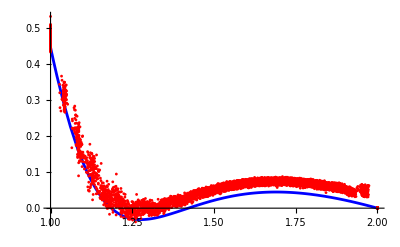

```mathematica
Show[plotσODE,plotσfe]
```

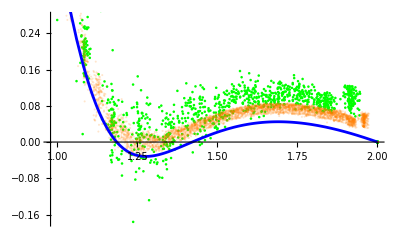

```mathematica
Show[ListPlot[tabσ01,PlotStyle->Green],ListPlot[tabσ005,PlotStyle->{Orange,Opacity->0.2}],plotσODE]
```

```mathematica
(*check of z*)
```

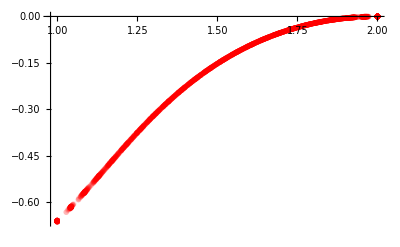

```mathematica
tabz=Import["~/Documents/finite_elements/steady-state-flow/solution/z.csv"];
tabz=Table[{Norm[{tabz[[i,2]],tabz[[i,3]]}],tabz[[i,1]]},{i,2,Length[tabz]}]
plotzfe=ListPlot[tabz,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

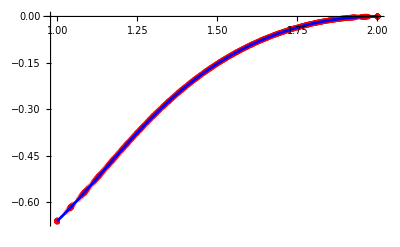

```mathematica
Show[plotzfe,plotzODE]
```

```mathematica
(*check of ω*)
```

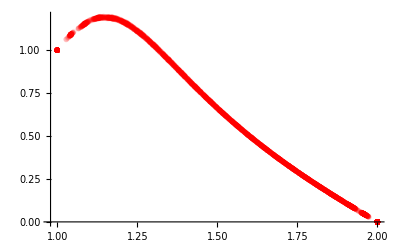

```mathematica
tabω=Import["~/Documents/finite_elements/steady-state-flow/solution/omega.csv"];
tabω=Table[{Norm[{tabω[[i,4]],tabω[[i,5]]}],({tabω[[i,4]],tabω[[i,5]]}/Norm[{tabω[[i,4]],tabω[[i,5]]}]).{tabω[[i,1]],tabω[[i,2]]}},{i,2,Length[tabω]}]
plotωfe=ListPlot[tabω,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

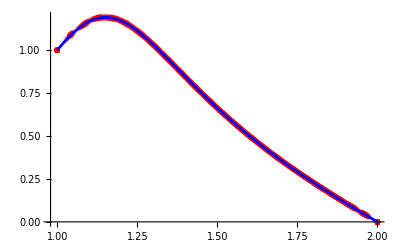

```mathematica
Show[plotωfe,plotωODE]
```

```mathematica
(*check of μ*)
```

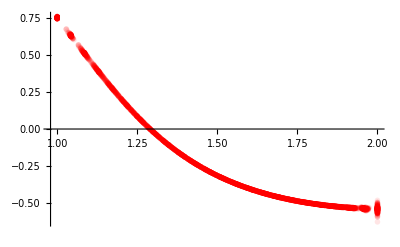

```mathematica
tabμ=Import["~/Documents/finite_elements/steady-state-flow/solution/mu.csv"];
tabμ=Table[{Norm[{tabμ[[i,2]],tabμ[[i,3]]}],tabμ[[i,1]]},{i,2,Length[tabμ]}]
plotμfe=ListPlot[tabμ,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

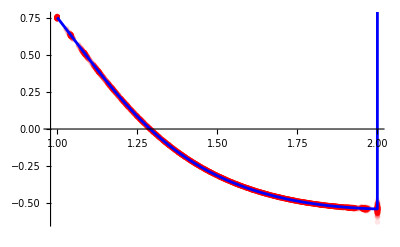

```mathematica
Show[plotμfe,plotμODE]
```

```mathematica
tabμ005={{2.,-0.5238460378334916},{2.000000000000001,-0.5490346326734504},{1.9580004763595418,-0.5378743636306785},{1.961234891646681,-0.5418837398038697},{2.0000000000000004,-0.5678882398410005},{2.,-0.5528315692826812},{1.9566600043151867,-0.5409353195539041},{1.9135062016770663,-0.5332240298052108},{1.9184375352757854,-0.5346880276481815},{1.9226841247590132,-0.5371109585368719},{1.9600473564541412,-0.5462207732541733},{2.,-0.5485658246486613},{2.,-0.5244279604125923},{1.9519940175796804,-0.535571277866774},{1.9068091600193289,-0.5312061661506016},{1.8669104707152266,-0.5239156970850672},{1.873870204520627,-0.5260164054033772},{1.880734270542621,-0.5281091229623218},{1.8895539634002358,-0.5301079589147193},{1.927870700312137,-0.5376395785095829},{1.9578770912264456,-0.5407214087706377},{2.000000000000001,-0.5412328555114133},{1.9518306161134442,-0.5333650314310856},{1.9040016955817956,-0.5295949543934884},{1.8615957352183128,-0.5221622588077233},{1.8210524281672553,-0.5121754364186709},{1.8273865098157407,-0.5143145411548207},{1.8349334076892736,-0.5167224751448283},{1.8439218575616558,-0.5192562687486498},{1.8545119367393428,-0.5216442854853994},{1.9090797927598628,-0.5327748872792536},{1.9566600044453186,-0.5367352192158115},{2.0000000000000004,-0.5345585233527675},{2.0000000000000004,-0.5293309042843247},{1.8993953083718154,-0.5292005399425362},{1.9332483741124227,-0.5355632988915908},{1.972200341135825,-0.540879928242181},{2.,-0.5610349820745933},{1.8569858166158346,-0.520915838750716},{1.8159874021130602,-0.5104791508039435},{1.7753349230387632,-0.49745506748979945},{1.7812113682656998,-0.4997178121422391},{1.7884367196957367,-0.5024104339097947},{1.796997394168342,-0.5053886220145075},{1.8069559692721293,-0.508511806181192},{1.8181977221637757,-0.5116195988994178},{1.8657391155370233,-0.5234892061252939},{1.9128633963809245,-0.5314744354705032},{1.9576343118813158,-0.5349930605989034},{2.0000000000000004,-0.5348202119144092},{1.8536004841473335,-0.5204392433153601},{1.8121673591975171,-0.5093457391437997},{1.7708430072890504,-0.49573450057347895},{1.7299165462955497,-0.4793618426119827},{1.7352186610040252,-0.48176828371440167},{1.74193280053893,-0.48474276125051713},{1.75004248932324,-0.4881808741989307},{1.7595284360960846,-0.4919678542615988},{1.770369144357824,-0.4959825482208392},{1.7825389120540371,-0.5001832265942943},{1.8307287939346046,-0.514773777751496},{1.8768038854974123,-0.5251911124536299},{1.920107516053376,-0.5319853320431474},{1.9598993986850575,-0.5367436949749695},{1.9999999999999998,-0.5450090589284307},{1.8935766666911398,-0.5292562286040314},{1.9278508840381057,-0.5357335480729531},{1.9648482089639046,-0.5415487331362884},{2.,-0.531081892128748},{1.809825374692291,-0.5088115875819967},{1.7677709096909922,-0.4946143085955863},{1.7260391503900059,-0.4775926880845117},{1.6847494131777399,-0.4574771775045483},{1.689457111684066,-0.46001714792784115},{1.6956194998497556,-0.46326984557261985},{1.7032201022615647,-0.4671575990303971},{1.7122390064046868,-0.4715753508144416},{1.7226553453236497,-0.4764245423989117},{1.7344438936761426,-0.4816124112080851},{1.7475755226016687,-0.4870826234286727},{1.796011095495905,-0.5045809453482073},{1.8441879310182823,-0.518078881937406},{1.89109842129322,-0.5278178151772327},{1.9262377967147803,-0.5333322007807916},{1.9548812428795102,-0.5373295236409787},{2.0000000000000004,-0.5377345295893241},{1.8524353118926407,-0.5206361622171155},{1.8953271630345643,-0.5304349140130835},{1.9268574715561273,-0.5368967493375213},{1.95997406866018,-0.5389529991949407},{2.0000000000000004,-0.5445642855876176},{1.7660871122135515,-0.494044339637606},{1.8089521867709357,-0.5087185956277982},{1.852140011527987,-0.5208755409341733},{1.895727708168219,-0.5310279292303732},{1.9234664105327064,-0.5369351690958307},{1.960623062582484,-0.5474382708645887},{2.0000000000000004,-0.5883830068478372},{1.7235961737468244,-0.47648269932440646},{1.681507600101234,-0.45570486203082516},{1.6398540591726445,-0.43137878880566827},{1.643934211205049,-0.43399151649419276},{1.649511965337754,-0.4374935527942433},{1.6565744954073758,-0.4418105868065623},{1.6650996600865342,-0.4468504136181064},{1.675066411874324,-0.45250546356329413},{1.6864486191926447,-0.45867178873742476},{1.6992222567809812,-0.4652509638650114},{1.7133495635360045,-0.4721564222531359},{1.762020620981566,-0.4927920601675012},{1.810756584413714,-0.5092087917594523},{1.8595525769240562,-0.5218478720689568},{1.9084039474984977,-0.5311624140057561},{1.9255471510726119,-0.5341264443436056},{1.9665523852434117,-0.5387164327315533},{1.9999999999999998,-0.5443805961189414},{1.7658063877277592,-0.4939618757587268},{1.8093310253574715,-0.508849817675278},{1.8530175079920086,-0.5209176739925154},{1.895975253196426,-0.5300522059722436},{1.9246085082197195,-0.5335675315242739},{1.9602667182681117,-0.5412144920782102},{2.0000000000000004,-0.5014675333498357},{1.7225938694577718,-0.4760264337637249},{1.6797395973369325,-0.45472319433823155},{1.6372821656969876,-0.4297034429763884},{1.5952537494496546,-0.4006071085527951},{1.5986712271126322,-0.40318786873665924},{1.6036312481036592,-0.4068659258777316},{1.6101217944634747,-0.4115732179028404},{1.6181245832983004,-0.4172135643818332},{1.6276150427820317,-0.42367730485026384},{1.6385657035378984,-0.4308403830991323},{1.6509517384681425,-0.4385843023121742},{1.664741427958405,-0.4467864660093585},{1.679895665552002,-0.45531958261911226},{1.7287984797814202,-0.47930408308000255},{1.777747856704201,-0.49869558929333946},{1.8267447486830175,-0.5140242366786839},{1.87578675384126,-0.525724773438446},{1.8931972085270505,-0.5297728717549526},{1.9537600185876993,-0.5381335717344996},{2.0000000000000004,-0.5361915930692549},{1.7669495248549207,-0.49433234805391296},{1.8111240384795813,-0.5092024870282582},{1.855682216723727,-0.5209418901702205},{1.9004576337580568,-0.5289567678524608},{1.9490751276577991,-0.5307428099217592},{2.000000000000001,-0.5307589913363252},{1.7230345572940564,-0.47619726779951427},{1.679451768574552,-0.45453700283259474},{1.63622733763081,-0.42899445060211994},{1.5933910663115864,-0.39917465167144867},{1.5509741300057658,-0.36464693404088594},{1.5536890725274597,-0.36704689982555117},{1.5579936921298698,-0.3707966680513627},{1.5638786992061733,-0.3758243259089573},{1.571325858263456,-0.38203328513359136},{1.5803094847704302,-0.38930014377161676},{1.5908074746501835,-0.39749368735856777},{1.602783792598586,-0.40646313971964054},{1.6162172890248783,-0.4160633992213667},{1.631062106841764,-0.4261412406344952},{1.6472839550975917,-0.4365394757002849},{1.696383800852857,-0.46407502796495986},{1.7455374099388137,-0.48659790087017635},{1.7947186067021448,-0.504727432961922},{1.843937875610925,-0.5189879481832821},{1.8635728931346884,-0.5243586594913443},{1.919343083321284,-0.5353663208322011},{1.9612915628575636,-0.5411402888556306},{2.000000000000001,-0.5497023009717951},{1.7694882510650434,-0.49516130481236453},{1.8143348820307534,-0.5099423339319585},{1.8594372751072752,-0.5215281782141589},{1.9047771660685788,-0.5304619798995578},{1.9562085179683735,-0.5387017888612354},{2.,-0.5606304132078263},{1.7249172639326333,-0.4769874941457333},{1.6806438105215165,-0.4551416858974003},{1.6366916995829417,-0.4292569915793823},{1.5930881283824554,-0.3989148972432881},{1.5498606670249,-0.36364278028549235},{1.5070434513414745,-0.32294757092768955},{1.5090127633421158,-0.32497011809430226},{1.5126207206712927,-0.328632679993814},{1.5178650887110923,-0.3338747594620798},{1.5247204803882943,-0.34058600970808345},{1.5331630521929744,-0.3486361491312753},{1.5431808703394838,-0.35788683749871925},{1.554728436498652,-0.368153836468214},{1.5677774892538632,-0.3792670498860787},{1.5822932852514593,-0.39103787916829147},{1.5982321856120614,-0.40327895117066515},{1.6155531819658764,-0.41580612201284933},{1.6648415539912602,-0.4471078981302353},{1.7141656263050489,-0.47291376972300947},{1.7635175191467587,-0.493937900269447},{1.812898128311207,-0.5107979266564809},{1.8322637535021733,-0.5167862008159504},{1.881759504636489,-0.5291836346140725},{1.9209951545832151,-0.5373340716487437},{1.9574983880723922,-0.5460741949516532},{2.0000000000000004,-0.5657213139302942},{1.7282371719194185,-0.47839979498287893},{1.683312597707584,-0.4565226575235167},{1.6386738147187259,-0.43048293829499923},{1.5943448110109792,-0.3998285469898087},{1.5503519176212774,-0.3640524695511439},{1.5067218342928388,-0.3226074761391122},{1.4634947380960588,-0.27492353005490244},{1.4646735692509874,-0.2763122654005256},{1.4675472031344214,-0.27968827245533245},{1.4721048315995773,-0.2849847916944707},{1.4783309183139575,-0.292098425734471},{1.4862052796554128,-0.3008908213034174},{1.4957013755914783,-0.31119317253956397},{1.5067885445159617,-0.32281640966091274},{1.5194319944328234,-0.33554777764993177},{1.5335940548803848,-0.3491708981657115},{1.5492316407971882,-0.3634603454073449},{1.56630106899337,-0.3781908351496229},{1.5847561429022499,-0.3931449527774858},{1.6342131301277405,-0.42843378725161696},{1.6836941267154002,-0.45768905604877663},{1.7331975782488382,-0.4817020664719418},{1.7827212371683279,-0.5011806064195283},{1.8030996398108223,-0.5081618485526332},{1.8527680807766593,-0.5224420326461564},{1.9097219802551326,-0.535409462384876},{1.9587075440644564,-0.5433248917468425},{2.0000000000000004,-0.5312169369526839},{1.7734258510442271,-0.4965121832772724},{1.8188589990657436,-0.5112255565237852},{1.8645187842469029,-0.523007286665362},{1.9107277039825292,-0.5327160542785908},{1.9579843917462592,-0.5412894557539052},{2.0000000000000004,-0.5398421868224259},{1.6874513001892262,-0.45866319860553423},{1.642168141924943,-0.4326476241428932},{1.5971580928886082,-0.40189617271674977},{1.5524444623958034,-0.3658631856256501},{1.5080507573101176,-0.3239551250740469},{1.4640140314709622,-0.27554558058143697},{1.420361869364933,-0.2199964241164539},{1.4207021116292056,-0.22043014916015582},{1.422790783332421,-0.2232411798738463},{1.4266203033338667,-0.22837523626357126},{1.4321766828813987,-0.2357310410915027},{1.439439780741265,-0.24516475611782634},{1.4483842064272678,-0.25649574866468694},{1.4589789303354492,-0.2695055275945513},{1.4711882696571843,-0.2839558885573744},{1.4849724255909225,-0.29958925082480037},{1.5002881152885728,-0.3161372397589008},{1.5170887318625217,-0.3333324244624603},{1.5353255995305355,-0.3509098643303622},{1.5549482028783541,-0.3686193643690876},{1.6045490730833127,-0.4081095556023345},{1.6541659668896707,-0.440984992631631},{1.7037974717050173,-0.46811751754225595},{1.7534424599702634,-0.4902806085065194},{1.774857486424695,-0.49846045954827384},{1.8246132362998628,-0.5146078001891753},{1.8743749642505767,-0.5272307245970993},{1.9225712168791618,-0.5364322752300082},{1.9637481011760871,-0.5410125679641972},{2.0000000000000004,-0.5557302837458461},{1.732986083173113,-0.4804262305253142},{1.7787530875053599,-0.4983883145517869},{1.8246804549888236,-0.5129628671130264},{1.8709159048766848,-0.5246621178219169},{1.919282519928962,-0.5340715768571408},{1.9665247261860666,-0.540901330022534},{2.0000000000000004,-0.548905615373706},{1.6930491180097065,-0.46152058476844054},{1.6471651770145663,-0.43570927877745996},{1.6015194789801763,-0.4050752746425878},{1.5561333532037818,-0.36903831064599407},{1.511025984945738,-0.32696127424048416},{1.4662296243664041,-0.27816413022548425},{1.4217714273373552,-0.22194603502762048},{1.3776825584926775,-0.15763363428902866},{1.377131463731579,-0.15671191149077524},{1.3783849241266959,-0.15860707087240494},{1.3814374648074619,-0.16328394368829363},{1.3862780675445356,-0.17065364016998644},{1.392888072713807,-0.18057080417138446},{1.401242921176633,-0.19284031627648238},{1.411310688274351,-0.20722610719586942},{1.4230554798880217,-0.22345678400820843},{1.4364360235598599,-0.24123486869627414},{1.4514073456762566,-0.2602474362586259},{1.4679205000986975,-0.2801735971084237},{1.4859241445229505,-0.30069828074931115},{1.5053648029782674,-0.32150968127432356},{1.526187578631373,-0.34232368321899453},{1.5759047492245821,-0.3862180509254896},{1.625631054869285,-0.42288677562580973},{1.6753657336380505,-0.4532814607722028},{1.7251081324664304,-0.4782330771144183},{1.7475820259710841,-0.48787257617934593},{1.797401090651014,-0.5060717684968153},{1.8471057177699373,-0.5202705753405619},{1.8937131461886065,-0.5303812171533003},{1.9334178384543694,-0.5369262490277342},{1.9616290296448824,-0.5399710021787122},{2.000000000000001,-0.5331706626857919},{1.7391522968620894,-0.48302693923157325},{1.7854577047276436,-0.5006985725491161},{1.8316235839055748,-0.5148729312475933},{1.8766597272471268,-0.5256864680531682},{1.9135276734777271,-0.5322536670782132},{1.9567552187037838,-0.5373399882842799},{2.,-0.5264318885656686},{1.6536513857512758,-0.4396085753360458},{1.6074164271867866,-0.4093029910778469},{1.5614047284260548,-0.37351104703289595},{1.5156349354305627,-0.33156126941679037},{1.4701342624211597,-0.28272364657545446},{1.4249256666602474,-0.22623551689888188},{1.3800374328483398,-0.16135292629433148},{1.3355015603309857,-0.0874417137416893},{1.334001032958806,-0.0846830842551497},{1.3343613769487603,-0.08522197572249794},{1.3365853982364293,-0.0890618095380921},{1.3406618071632577,-0.09612400069268986},{1.3465734368424582,-0.10627154570258752},{1.3542958625653787,-0.11930854505038486},{1.3637992958385505,-0.13498230608204767},{1.3750458500514793,-0.15299375513421096},{1.3879938586789564,-0.17300618512540084},{1.4025958470519782,-0.19465597845482438},{1.4188009456101074,-0.21756867125782428},{1.436554751050551,-0.24135784126073714},{1.4558006753749835,-0.2656585586651825},{1.4764803730184608,-0.29011452092493434},{1.4985345710458517,-0.3143966778241274},{1.5483367227915885,-0.3628724668333897},{1.5981428785755485,-0.4034917265151299},{1.6479526702263803,-0.4372884346989384},{1.6977658053252647,-0.46516177685122606},{1.7213192022822952,-0.4764807317598513},{1.771174920882123,-0.4969131032967785},{1.8210313202505795,-0.5129982141533338},{1.8701949831869835,-0.5250387202954134},{1.9198933562876526,-0.5336106384957292},{1.9611692761046176,-0.5363179509365875},{2.0000000000000004,-0.5398296054231282},{1.700091652600389,-0.46503644992626436},{1.746720802750066,-0.4861280771186765},{1.7935241774615531,-0.5033587748743986},{1.8404883696629046,-0.5171301556340174},{1.8859332301748832,-0.527437633853017},{1.9304355591012279,-0.5350565045067819},{1.9710883020719607,-0.5398184990765691},{2.0000000000000004,-0.5576088900590759},{1.6148325733878033,-0.4144948149692126},{1.568245866092878,-0.3791961926965221},{1.5218649584434525,-0.33766425461526894},{1.4757143536156097,-0.2891299006672438},{1.4298127971676822,-0.23277633824323699},{1.3841853280373353,-0.16778709417737023},{1.338858823588481,-0.09344212984988387},{1.2938677152291167,-0.009246012659994045},{1.29135909871623,-0.004106271859594656},{1.2907688486655726,-0.0027772211710365927},{1.2921032115014845,-0.005295480074749773},{1.2953599024534468,-0.011626655008203632},{1.3005212128709867,-0.021648282562308406},{1.3075653835976961,-0.03516844031765579},{1.3164621124233364,-0.05193131966925738},{1.3271734754576945,-0.0716163434326889},{1.3396559632936629,-0.09385436443711867},{1.3538611763416752,-0.11823948465268895},{1.369735276609902,-0.14432901752329572},{1.3872208586923558,-0.1716802874660394},{1.406257842746142,-0.19984304293856325},{1.4267841952982776,-0.228382369246321},{1.4487367613557174,-0.2569009117143405},{1.4720516173834177,-0.2850241364529997},{1.5219034764110493,-0.3382161434430081},{1.5717562165326138,-0.38291639532549254},{1.621609800427955,-0.4202419413374609},{1.6714641046340564,-0.4511552151573405},{1.6961158381880506,-0.4643499517433653},{1.7459792642240426,-0.48714003687847857},{1.7958427982534688,-0.5052778140745839},{1.8457065324300834,-0.5192030575845822},{1.8911110409450833,-0.5284090346433433},{1.9306521130775178,-0.5336564853542195},{1.9599729738641545,-0.536050409734264},{2.000000000000001,-0.5353893270033392},{1.6616093772537435,-0.4442657728784911},{1.7085610199861168,-0.4691335787870489},{1.7556734719639628,-0.48965561814950676},{1.8029340246496053,-0.506309414745935},{1.85033137255564,-0.5195337692929626},{1.899208506374643,-0.5301037193051912},{1.9552524470900012,-0.5402824303340461},{2.,-0.5446103141822352},{1.5766355524435993,-0.38598267670595154},{1.5296967136008253,-0.3451496917572552},{1.4829508198609713,-0.297256079063159},{1.4364151292962266,-0.24143422455524913},{1.39010986037765,-0.1768038078613043},{1.344055833369712,-0.10255643200387043},{1.2982896721519532,-0.01810158934625145},{1.2528320028644224,0.07677002560347854},{1.2492466811480079,0.08488147328917336},{1.2476427858886054,0.08865252400372126},{1.2480283879153966,0.08800471156003017},{1.250405624981412,0.08293199144829504},{1.2547617229831007,0.07352350563489518},{1.2610756942064882,0.059946429175987664},{1.2693186495199702,0.04244900077871701},{1.2794532352388819,0.02135079760702093},{1.2914345921779697,-0.002961084611370909},{1.305212103379472,-0.03003625152771419},{1.320729563538029,-0.0593887512378941},{1.3379264016834167,-0.0904964293286488},{1.356738702706631,-0.12282921681867229},{1.377100177037117,-0.15587107291234442},{1.3989436239360704,-0.18911814383058106},{1.4222007387989928,-0.2221138052205122},{1.4468029985684383,-0.2544437581248227},{1.4966651328713259,-0.3124331706740503},{1.546527518737555,-0.3613107098641591},{1.5963900143786003,-0.4022539410438353},{1.6462528647235943,-0.4363012339604806},{1.6720197949415248,-0.45153867995029323},{1.721858262256333,-0.47677546610245175},{1.7716950963697449,-0.49708694922607066},{1.821541939976274,-0.5129987918064739},{1.8703743329940743,-0.5246576680783046},{1.9159492905604825,-0.5320916410341269},{1.9502382940713157,-0.5362075372621794},{2.0000000000000004,-0.535580171472914},{1.623746647461917,-0.42055167720267567},{1.6710181194274456,-0.4495886520473492},{1.71843622333334,-0.4737285307797189},{1.765989219867094,-0.4935340717525997},{1.813666437849364,-0.5094834201838138},{1.8614584444528302,-0.5219807711201918},{1.909627142870503,-0.531183342197331},{1.9569116073200366,-0.5352770667704146},{2.000000000000001,-0.5218507304150263},{1.5865472772733986,-0.3937385716845205},{1.5391047103928863,-0.3538744305966334},{1.4918197025311046,-0.30694274523749504},{1.4447094061576147,-0.25203676438096867},{1.3977899127666893,-0.18822436290809536},{1.3510807053616352,-0.11461446390266586},{1.3045850940688992,-0.030460937612635828},{1.2582614124998364,0.06473125210149665},{1.2123803195104863,0.17006966855299385},{1.207726095218269,0.18154376875751313},{1.2050360055693803,0.18834453696739667},{1.204404110819614,0.19016966070433095},{1.2058610717437124,0.1869024425185204},{1.2093264344828423,0.1787649757761491},{1.2148536456269763,0.1657164068841621},{1.2223914286251767,0.14801581709750566},{1.231902921292131,0.12598397042445755},{1.2433427701758986,0.09999251223187994},{1.2566583394963768,0.07048828782316537},{1.271790683523282,0.03800913356259173},{1.2886758736928488,0.003131052015915986},{1.307245980094149,-0.033541290693588056},{1.327430049709805,-0.07138289194626639},{1.349156169679949,-0.10979395793545747},{1.3723508558331974,-0.14819473470729688},{1.39694113608487,-0.18606797694634916},{1.4228544204129465,-0.22294967879764127},{1.4726831539733518,-0.28575615586072733},{1.522514297917251,-0.3388502317142544},{1.5723476122633357,-0.38346533385754134},{1.6221826468164804,-0.4207087540747752},{1.6490803817063244,-0.438144574514482},{1.6988603643183882,-0.46585333073946394},{1.748639871435524,-0.4883735390011489},{1.7984075488419946,-0.5063251228672551},{1.8480633615709328,-0.5201693985559509},{1.8969169275725142,-0.5300863809717546},{1.919618230659053,-0.5350972238756735},{1.9660321907094935,-0.5418383048027184},{2.0000000000000004,-0.5567255224755825},{1.6341342823330496,-0.4273588109625371},{1.681853051217046,-0.45547549424448047},{1.7296929994999788,-0.478731940261204},{1.7776442183520513,-0.4976872737170956},{1.825696481060948,-0.5128110863381333},{1.872982249380672,-0.5242931451601703},{1.9185688332660527,-0.5324192821728566},{1.9595314990621286,-0.5380735119188306},{2.,-0.5608473027545958},{1.5979554778665548,-0.40232568036278493},{1.645967632357089,-0.43479216385251385},{1.6940870452593055,-0.4618206964222767},{1.7423046969071485,-0.48405436618628234},{1.79061261844038,-0.5020526185317276},{1.838993048662697,-0.5163011401941503},{1.8874719868649639,-0.5272726325483835},{1.9265746939400576,-0.5342093798783661},{1.95843800280216,-0.5397394972047682},{2.0000000000000004,-0.5336931773626293},{1.550059794430782,-0.36367606208353087},{1.502292572578871,-0.31800541848273567},{1.454666635114406,-0.2643806041260386},{1.4071957767942445,-0.2018222656765072},{1.3598962519960138,-0.12936085046596904},{1.3127889219307332,-0.046193110733586715},{1.2658458964472477,0.04824680175849365},{1.2185816754338468,0.15508009295303127},{1.1728923931522655,0.26851979902188283},{1.1668775663936661,0.28441424748442273},{1.1633561100531,0.2939221706991966},{1.1613836214598696,0.2994385247453352},{1.1618406368583092,0.2986110892319697},{1.1642536959477403,0.29267296315572344},{1.1689308724106406,0.2808492689350333},{1.1757059529640304,0.26369977518467747},{1.1845429846411306,0.2413873862333589},{1.1953962261005664,0.21441758566126937},{1.2082113379160084,0.1830658104820121},{1.2229334480049383,0.14789859419252843},{1.2394802631904014,0.10954896027337013},{1.2577826397467087,0.06868665227244071},{1.2777753165286254,0.025977048293773494},{1.299374599563795,-0.01784169280579198},{1.3225022798937671,-0.06206854929710444},{1.3470796308523962,-0.106035715744546},{1.3730282952948074,-0.14914832474699002},{1.400272476880294,-0.19089932570548102},{1.450019838436106,-0.2584569447076216},{1.4997750517312445,-0.3157540372791405},{1.549537305205504,-0.3640506945512062},{1.599305841207574,-0.4045030319921127},{1.6273461627464718,-0.4242870909936542},{1.6770297476008087,-0.45445539593003736},{1.726723899852382,-0.4791694181549818},{1.7764227803049029,-0.4991160442608823},{1.8258034068505598,-0.5148049064579526},{1.8740346801150705,-0.5266544618855408},{1.9005529024399002,-0.5328512825552654},{1.9532439258717347,-0.5430926977426815},{2.0000000000000004,-0.5502179458410904},{1.6108264385172768,-0.4115905880279516},{1.6592156299335425,-0.4427221644480134},{1.7076899696832548,-0.468512538620366},{1.7562421205513077,-0.48960228872904865},{1.8048565926114983,-0.5065457127600267},{1.8534991308159865,-0.5198586057080729},{1.9094400169272785,-0.5313867741233459},{1.9568231633106086,-0.5373210003529586},{2.,-0.5440881623867121},{1.5625302508495351,-0.37437794769758875},{1.5143350378595877,-0.3302412607250294},{1.4662526882330498,-0.27823349299799266},{1.4182932468808653,-0.21733651203634835},{1.370469739820142,-0.14651770601319214},{1.322796997569222,-0.06486255879314558},{1.275350408161165,0.02813553420469061},{1.2283681032212794,0.13186277869267976},{1.1765829664497556,0.25874159149326587},{1.1390232861936556,0.3580350869753154},{1.1267223273836835,0.391671103542731},{1.122171658768665,0.4044661871659239},{1.120159981391478,0.4103881570403025},{1.1185046964365883,0.4153985355370837},{1.1204370604741394,0.4105518787299937},{1.1233441685158532,0.4030187786134599},{1.1297605925125527,0.38582944888270054},{1.1332547951276923,0.37676355695041686},{1.1484885724164555,0.3363245832079047},{1.1598845267128386,0.3062249244066182},{1.1741467938893018,0.2692758020434431},{1.1903627235017724,0.2280988737807263},{1.2083522881733353,0.1836297617972299},{1.228137448807829,0.13643890162130162},{1.2496000453530722,0.08732767914765488},{1.2726552673005058,0.037151602562788176},{1.2972183038016636,-0.013261772475220694},{1.3232051288805204,-0.06314531614577996},{1.3505338354564613,-0.11181126943157914},{1.3791237455315635,-0.15869365183851286},{1.4287379638519333,-0.23085937043964525},{1.4783684579536203,-0.29227938314049856},{1.5280142234827192,-0.344206612653763},{1.577673876375548,-0.3878505618353401},{1.6068655181424467,-0.4101177241974495},{1.6564131090027423,-0.4427063024470214},{1.7059792818992559,-0.46956181967692523},{1.7555622072440233,-0.49142404140986057},{1.8051606829286704,-0.5089551935693324},{1.8540597292289593,-0.5226013196905064},{1.8821823217960185,-0.5292204642514005},{1.9212996370580793,-0.536640082817212},{1.9586511919621477,-0.5412806708544615},{2.0000000000000004,-0.5362262964957468},{1.62512596187481,-0.42137758773214445},{1.5764795199867538,-0.38579708334610574},{1.5279111852070784,-0.34343592717203625},{1.47942960002618,-0.29334431794718835},{1.4310430283074669,-0.23448069852917322},{1.3827615328268563,-0.1657633760290082},{1.3345966100992133,-0.08618092338128938},{1.2865607036337716,0.0050451656142993465},{1.2386698669948508,0.10816102648011312},{1.1933006798595203,0.2167344980432043},{1.1569494855188758,0.31010212678870086},{1.1291470833071555,0.3846607195525911},{1.0917774061692405,0.4884644396055445},{1.0817582483961088,0.5168863357168461},{1.079940403771207,0.5224110725122131},{1.0793061244076734,0.5247413003206799},{1.0799151518002617,0.5235999518434452},{1.0806776444518753,0.5220381330946984},{1.0831851355480184,0.5155586521987472},{1.096488559614902,0.4784607006366555},{1.0867303876697978,0.5063930935672881},{1.113948768271574,0.4304868046517355},{1.1096924000401094,0.442629332753539},{1.1267186119593626,0.3962863873833592},{1.1414511732795405,0.3563929450120511},{1.1585706387439787,0.31090205179137415},{1.1785186978510396,0.2589700028182503},{1.1998327550680241,0.20539064803136886},{1.222809658851777,0.1496193922586703},{1.2473575246830457,0.0928249067339849},{1.2733891730491662,0.03594780329367557},{1.3008091026632351,-0.0201200716839974},{1.3295293747558494,-0.07457655032752392},{1.3594702101607052,-0.1267832232237749},{1.4088960255481293,-0.2033254860282532},{1.4583515867396337,-0.2687091654438023},{1.5078334753619351,-0.32417355633776174},{1.5573383247200248,-0.37093726324445087},{1.5876872447552635,-0.3958138872227092},{1.6370558044164603,-0.4307522614853132},{1.686453667157667,-0.4596836000410901},{1.7358783533144573,-0.48338634363970584},{1.7853276008998296,-0.5025430381748189},{1.83479913602543,-0.5177678302189258},{1.8653001007131895,-0.5253987501070713},{1.9150273269926816,-0.5355158436074433},{1.9605540793518341,-0.5433178291478523},{2.000000000000001,-0.5642978113636166},{1.6738447795644047,-0.45101683747218224},{1.7226294074012158,-0.4754396273103513},{1.7714739760424296,-0.49526980399426795},{1.8203739670242078,-0.5110442278318467},{1.8689767724134776,-0.523161978818979},{1.916586304712508,-0.5320396578911673},{1.959244891290156,-0.538924779181692},{2.0000000000000004,-0.5480163903876212},{1.5918688436474737,-0.3977452542989996},{1.5429799116291063,-0.35736681340161597},{1.4941551117761147,-0.309450742047962},{1.4454013911461845,-0.2529493000273885},{1.3967262050238896,-0.18674448785678588},{1.348137834784704,-0.10974479246718004},{1.2996461404658046,-0.021039551831290335},{1.2512627805584569,0.07983684317510736},{1.2030003440162114,0.1924743431510552},{1.1548739314859167,0.31506029481864145},{1.1240455991157985,0.39874661662751953},{1.0863378825887624,0.503355861441279},{1.0430595436274912,0.625648338299184},{1.041356377884613,0.6308474792388313},{1.0414668086209928,0.6310346925474412},{1.0396786927821495,0.6366580523959832},{1.041011119888629,0.6335544403341943},{1.0400338331310874,0.6370491080150458},{1.0416814713951117,0.6331644936391825},{1.049086041463548,0.6130356407035358},{1.042870406824957,0.6313798368712553},{1.0523831624578772,0.6049077507303198},{1.0812418312221423,0.5224925734612182},{1.6408171881235794,-0.43153134737146215},{1.6898194872294883,-0.45954461073262404},{1.7388709113217427,-0.48249051669885107},{1.787967169701116,-0.5009534869046617},{1.8371048900536409,-0.5154084831634372},{1.8837582728569928,-0.5257242374523169},{1.9243792642909379,-0.5322076452659719},{1.953199134267596,-0.5330940325461049},{2.,-0.5225562623203802},{1.0838501363083983,0.5158497613726062},{1.0889610380939727,0.5019087009127122},{1.109608347282958,0.4446473341900213},{1.1264522341508176,0.3981679211673297},{1.1535500591124899,0.3252828196584908},{1.1733625217122299,0.2731835657835277},{1.19749705615949,0.21176080475968517},{1.2235696332413566,0.14831631582577928},{1.2511078984404627,0.08478543713964186},{1.27995962974415,0.02240803710497786},{1.3100828026365612,-0.03799850941928408},{1.3413905213254347,-0.09568211990616106},{1.3905516542020495,-0.1762391526958754},{1.4397752242193707,-0.245361646047666},{1.4890409904495034,-0.30420084280564286},{1.53835078373393,-0.3539749482078647},{1.5698590754597086,-0.3815690354473224},{1.6190033433446396,-0.4187554603331295},{1.668190462297144,-0.4496837149052629},{1.7174168062039346,-0.47515429357868894},{1.7666790879741143,-0.4958631610860119},{1.815974396411327,-0.5124182860810045},{1.8474589446678555,-0.5209193936760784},{1.892798902102114,-0.530814931966456},{1.9306998533439037,-0.5374739994712481},{1.9614337145370329,-0.5399685972996947},{2.0000000000000004,-0.5213681608433394},{1.5594976830881826,-0.3718113261723468},{1.51038406796008,-0.32628838462941423},{1.4613210451544123,-0.2724271877716935},{1.4123142508990567,-0.20909127075032394},{1.3633696075190593,-0.13513259162257082},{1.3144941761057847,-0.049517791306125505},{1.2656961093871015,0.04843091005721852},{1.2169845677818252,0.15865954223643686},{1.1692531878017374,0.27764772828989465},{1.1277119863775862,0.38844589519128203},{1.0943597267318204,0.4804682327561185},{1.043410773078819,0.6242751147682869},{1.0000000000000002,0.746691563104347},{1.0000000000000002,0.7471085385486779},{1.0000000000000002,0.7475911334631535},{1.0000000000000002,0.7481695615378066},{1.0000000000000002,0.7488652165987801},{1.,0.7496850059973046},{1.,0.7506021139566157},{1.0000000000000002,0.7515973441063137},{1.0000000000000002,0.7525115115329541},{1.0000000000000002,0.7532923773529151},{1.0000000000000002,0.7539140461118178},{1.044130410887855,0.6290632827030257},{1.0428704068589274,0.6332809385776829},{1.0651185652366975,0.5704133455356266},{1.0914207808621768,0.4964662771828826},{1.1157702015648192,0.4284629543665201},{1.1286932460632784,0.3930741826859535},{1.147636853831154,0.34157391443424684},{1.174523442396168,0.27082377022086485},{1.2015055863627633,0.20237735869371892},{1.230423284090668,0.1325132690153073},{1.2607345882627081,0.0637335142640335},{1.2922721261305583,-0.0026867445044756163},{1.3249424644129688,-0.06588922600427789},{1.3737922443265116,-0.1500731805068726},{1.4227102249560608,-0.22260119228803646},{1.4716969983179018,-0.2845781911769588},{1.520756280429314,-0.33719316078693623},{1.5534275740966996,-0.3675867922544301},{1.6022998395851287,-0.4068911709924854},{1.6512313972846449,-0.43971161928746544},{1.7002174881610164,-0.4668693799520882},{1.7492534726797255,-0.4890723698585447},{1.7983351980173414,-0.506921854136084},{1.8308023281444379,-0.5165371876129524},{1.8785200870677505,-0.5277400576686926},{1.9222830123391759,-0.534990655249887},{1.9585427521825771,-0.5371224279477896},{2.0000000000000013,-0.5475112350382629},{1.6086579390399702,-0.4100403266682342},{1.6578604434521418,-0.4418985552685677},{1.707101945417322,-0.468185546593082},{1.7563783403336755,-0.48957341711343366},{1.805657615556867,-0.5065933467598924},{1.8539710185278149,-0.5194017601648887},{1.9020225994408269,-0.5283699130463386},{1.923833774790291,-0.5310953659498272},{1.9652819643965413,-0.5303652727359383},{2.000000000000001,-0.5257297596677825},{1.0741189635546238,0.5442578337481868},{1.5280682646233759,-0.34359486992056465},{1.478751371421748,-0.29259890233269464},{1.4294723928721915,-0.23243041047723223},{1.3802355654965188,-0.16190232295791238},{1.3310455146751696,-0.0798849549070687},{1.2819076821021347,0.014488010151989673},{1.2328282866014468,0.1214779983920998},{1.1838476146821721,0.240202715481238},{1.1365396106890586,0.3642505053133199},{1.0860607457818814,0.5037131275652692},{1.042490290596704,0.6266272454432416},{1.0000000000000002,0.7463048547978859},{1.577419557254447,-0.3865538054132681},{1.6268025375459954,-0.42250121981034544},{1.6762145444110013,-0.4523372484377055},{1.7256523908907067,-0.47682912310517234},{1.7751142504350237,-0.4966336913708166},{1.8244227673705384,-0.5122152948707354},{1.8737268744699802,-0.5239057250050513},{1.895577143365759,-0.5297353836326913},{1.9524117897452797,-0.5405348763176394},{2.,-0.572936979904992},{1.0000000000000004,0.7542973762090358},{1.0000000000000002,0.7545971281273656},{1.0276788799800873,0.6768115441471215},{1.0438941343208128,0.6317277482007669},{1.085350571909452,0.514195032312986},{1.0938451397939044,0.490835586509974},{1.1283511884943904,0.39482785608088655},{1.1547916295942005,0.32342214590794116},{1.1815296588365742,0.25327062843522474},{1.2114371108663844,0.1782263923933819},{1.2432106091713815,0.1031533590216556},{1.276165478422031,0.03074702305874125},{1.3101837597235515,-0.03791731705194182},{1.358654721269716,-0.12523219849834583},{1.4072211774358854,-0.20080687909111716},{1.455871869275984,-0.2656295825581648},{1.504610416567934,-0.3208467446819043},{1.5384382365500744,-0.35408593810627226},{1.5869878567432332,-0.3953390081326808},{1.6356175492248397,-0.4299200279507758},{1.6843194091243807,-0.4586632652491981},{1.7330876856666966,-0.48229173138305603},{1.7819169272888606,-0.5014164287851918},{1.8153231183296392,-0.5122134279501799},{1.863801598772289,-0.524770768859971},{1.9133456593695088,-0.5339316762098753},{1.9566600043769469,-0.5414747027613405},{2.0000000000000013,-0.5496853001087376},{1.497639749990345,-0.31316031071751316},{1.4481450287699722,-0.25639244722826365},{1.3986766282426253,-0.18961251080383812},{1.3492374813799957,-0.11162269174099972},{1.2998309092804772,-0.02140124517058408},{1.2504608120992444,0.0816157560319309},{1.201137333582112,0.19706083440948463},{1.1524314606772201,0.3217740355794689},{1.1058618205728592,0.44850300058432696},{1.0670649817567353,0.5570400531142722},{1.0378075668545215,0.6396745497121354},{1.0000000000000002,0.7459671686292038},{1.5471581968421035,-0.361118835018258},{1.5966983536947972,-0.40138708236426784},{1.6462583568579578,-0.4349609765003524},{1.6958363109466794,-0.46270930093891655},{1.745430668289643,-0.48538401946342974},{1.7950401632375466,-0.5036411639529401},{1.8446747746442205,-0.5181100576146684},{1.8658461191033597,-0.5239348136628768},{1.9176892147683873,-0.5359369714869741},{1.9656142794331477,-0.5489316360313468},{2.,-0.5510472484035951},{1.0000000000000002,0.7553626481718653},{1.0000000000000002,0.7565597916997336},{1.0426544631614039,0.6361381075210168},{1.042933641218307,0.6361479798636521},{1.0847654336739303,0.5172636642344765},{1.117442589321702,0.42555120419481773},{1.1349257548795446,0.37743575863437273},{1.1620220893130677,0.30457608246328455},{1.194218732635652,0.2212471743316856},{1.2274761838782338,0.13995649811745442},{1.2618232137753886,0.061728300812959054},{1.2971769574668233,-0.012282724398545733},{1.345189305723531,-0.10214765853764121},{1.3933396222118974,-0.18032442550234232},{1.4415959651329504,-0.24764645221898493},{1.48997199937324,-0.30520611046070123},{1.5249309878806359,-0.34128290817284723},{1.5731081844842163,-0.3842833566495179},{1.6213873468630295,-0.42046373507887896},{1.66975976495289,-0.4506649697692343},{1.7182176700034366,-0.475619554281036},{1.7667538565709278,-0.4959609712969668},{1.8011716206617758,-0.5079103749875322},{1.849037120857888,-0.5214466172297153},{1.9035879681381134,-0.5331590217280222},{1.9559495213963962,-0.5417005248062642},{2.000000000000001,-0.546356311711862},{1.468274311170932,-0.28062406612926194},{1.4186314877061346,-0.21783330058592715},{1.3690047836315098,-0.14421766015495743},{1.31939602548802,-0.05862788157617218},{1.2698075279226062,0.03974542886093384},{1.2202417083322306,0.15097764563969163},{1.1707011941597298,0.273949491742357},{1.1211894325005363,0.4061712185429793},{1.0760171154763236,0.5319541474677083},{1.03365625961562,0.6514685670844447},{1.0000000000000002,0.7458087214183424},{1.5179317094404021,-0.33382143416194787},{1.567602318871955,-0.3786227655050664},{1.6172850789607873,-0.4161154466905107},{1.6669787240241776,-0.44725617322015665},{1.7166825484172612,-0.4728815822242917},{1.7663954905421875,-0.4937273219061342},{1.8161169066962448,-0.5104820047500518},{1.8383049237823454,-0.5168000278234103},{1.8854636942349756,-0.5280773177478123},{1.9225370263313615,-0.5346056557978784},{1.9593224374176166,-0.5401625773615358},{2.0000000000000004,-0.5268947277136343},{1.0000000000000002,0.7576441819207291},{1.0000000000000004,0.7586276123673242},{1.043503631351039,0.635315659590514},{1.0866382121989908,0.5126260843959484},{1.1135066256595179,0.43743677232482636},{1.1436171806679978,0.3543366642424901},{1.1788840996906633,0.26079233201526103},{1.213622381083191,0.17344134396626215},{1.2493074444326429,0.08967733444136067},{1.2859714525961494,0.010542578213899275},{1.3334581619102255,-0.08126376956222485},{1.3811175687044066,-0.16152430830776043},{1.4289198546802215,-0.2309425644740873},{1.4768620866564008,-0.2905099777975565},{1.512947285509594,-0.32939944519073394},{1.5606984877997334,-0.3739098762508779},{1.6085775143114827,-0.4114997195490672},{1.6565736217705738,-0.4430042409164649},{1.7046771850009232,-0.46916110796544275},{1.752879137556412,-0.49061167254046195},{1.7882594793636,-0.5036764397257859},{1.836298682306961,-0.5181529560900913},{1.8817105862307464,-0.5287891681063563},{1.9219482097955836,-0.5360290044427227},{1.956425179944956,-0.5398670288618966},{2.0000000000000004,-0.5371971004408785},{1.4400370936589075,-0.2461620560087467},{1.3902802509678467,-0.1771690557908824},{1.340531375951328,-0.09659627791352733},{1.2907916211640433,-0.0034318783935363343},{1.2410619683256578,0.1027907780925598},{1.1913438199569728,0.22150160532954635},{1.1416383618171189,0.35080295995335925},{1.0940949903124293,0.48125471850618873},{1.043114583322954,0.6251508374193866},{1.,0.7460430002805956},{1.4898011882956568,-0.3047939209382251},{1.5395718575383661,-0.3543158696686146},{1.5893484457889084,-0.3958880356059604},{1.639130504567835,-0.4305559828005688},{1.6889176574944047,-0.45923212252259293},{1.738709337710316,-0.4827034359828577},{1.78850517982386,-0.5016826352435912},{1.8116451252319286,-0.5090162039677266},{1.8611288009431202,-0.5222006157682624},{1.9058297276070706,-0.5311521496581453},{1.9524009141541938,-0.5368829294309576},{2.0000000000000004,-0.5514735059068895},{1.0000000000000002,0.7594771153177624},{1.0401407604802886,0.6456043591911149},{1.073533849084823,0.550341865772255},{1.089183127763515,0.5062770397717291},{1.129895747690462,0.3924231456557709},{1.1655947835011344,0.2958439229396179},{1.2017035335519362,0.20303239265139086},{1.2386737420288203,0.11406223049486734},{1.2766155022991168,0.03011725787258536},{1.323502850655398,-0.06297169752758683},{1.3706034548122974,-0.14476497277797593},{1.4178837487876566,-0.21582186315809862},{1.4653374818204976,-0.27703427836449473},{1.5025248337167871,-0.31864916937190996},{1.5497945719738435,-0.3644004998246133},{1.5972222221008303,-0.4031821494207323},{1.644793957350464,-0.4358136785876949},{1.6924977796810645,-0.4630286362372162},{1.7403228802432393,-0.4854630259234427},{1.7766530807471788,-0.49963661013772254},{1.8243167153484188,-0.5148635435978115},{1.8720951233359249,-0.5267326304411365},{1.9154702036703422,-0.5348284891630773},{1.958437747317857,-0.5406752486708122},{2.000000000000001,-0.551395713060722},{1.4129957471750327,-0.21001699250783795},{1.4628298592662263,-0.27422156313518276},{1.512666019214253,-0.32860774899240314},{1.5625040670287007,-0.3743966501868838},{1.612343848632222,-0.4127171066376329},{1.6621852342121004,-0.44454045441235945},{1.7120281100935866,-0.4707331303612311},{1.7618723290814846,-0.4920206727667307},{1.78612729347014,-0.5006899032315653},{1.8353907730806098,-0.5155075300087869},{1.8827540067587987,-0.5263703592800455},{1.9231100579931248,-0.5335375369161923},{1.9588425085054513,-0.5392033008211602},{1.9999999999999998,-0.5458984322008765},{1.3631639474118014,-0.1347332525788826},{1.3133344183690248,-0.04721659009340574},{1.263507948190137,0.05330619522201363},{1.2136850643693262,0.16681501236005103},{1.1642278539265263,0.2910917673285097},{1.116227740328437,0.4202439886035175},{1.0767189610841155,0.5302746534324878},{1.0410425027436139,0.6313738481671078},{1.,0.7465764214045407},{1.0000000000000004,0.7602446385911383},{1.041122946243282,0.6434215568536773},{1.0420057533663616,0.641499235676572},{1.085528117473886,0.5169785433836646},{1.1171916667930775,0.42798019957039507},{1.156763774376014,0.3196351372749318},{1.1908931779976373,0.23031154464256506},{1.2299650026891529,0.13446935072170252},{1.2691488420147339,0.046074893443354165},{1.3153527424800866,-0.04760426063214205},{1.3618211519859968,-0.1303448287623446},{1.408522863684221,-0.202562302324401},{1.4554287355395763,-0.26501909403396007},{1.4936949563579778,-0.30923156299152477},{1.540428518860964,-0.3559294772865808},{1.5873527613293184,-0.3956606580170085},{1.6344512046852613,-0.4292221153355936},{1.68170923028884,-0.45733289395685545},{1.729114821488011,-0.4806216222191698},{1.7663848431845357,-0.4958820145134317},{1.813626726091918,-0.511753524531477},{1.8623667761218583,-0.524537618705406},{1.9123730007958368,-0.5343884849959899},{1.9546229548176721,-0.5407648833833741},{2.0000000000000004,-0.5462490228232408},{1.437082968577351,-0.24234303893429723},{1.3872199777995022,-0.1725081855218156},{1.3373571548560375,-0.09094874216520712},{1.2874949176201924,0.003340537906194823},{1.2376328726949326,0.1107822165013045},{1.1877711731617773,0.2307723066076074},{1.1379096891651104,0.3612026515705391},{1.086424665690628,0.5032964643162294},{1.0409571349233964,0.6320711568782421},{1.0000000000000002,0.74718820609042},{1.4869459615503844,-0.3016834546371204},{1.5368090873510727,-0.35179553232537875},{1.5866723701798997,-0.39385756473305217},{1.6365358319433152,-0.42892646255674965},{1.6863995132348366,-0.4579216044523248},{1.736263370465731,-0.4816206626163403},{1.7615770331832161,-0.4917969445314761},{1.811430425425139,-0.5086487758673083},{1.8606652693831554,-0.5214365875648553},{1.9156443720293599,-0.5314227934206862},{1.9626946160448053,-0.5338226795652627},{2.0000000000000004,-0.5078725320213133},{1.0000000000000002,0.7609552886503452},{1.0000000000000004,0.761566333929587},{1.0428704068577643,0.6396049549876295},{1.087459464509242,0.5119826263697518},{1.0781544044910722,0.5380241839901139},{1.1220887315028891,0.4146357969539047},{1.1460477522818604,0.3484279311136847},{1.1831469999177195,0.2501609562845044},{1.223203513317834,0.15056029538366658},{1.2636148988958342,0.058089298641385276},{1.3090610680733774,-0.03550356687528533},{1.3548220787507252,-0.1185752528671919},{1.4008638315048234,-0.1914137819392462},{1.4471704821946065,-0.2546967766876239},{1.4864859702291446,-0.3013271550182752},{1.532628286231973,-0.3486554465221883},{1.5789970533837945,-0.3890742126892439},{1.6255728916499814,-0.4233499813167615},{1.672338467844338,-0.45218044518612216},{1.7192795780174337,-0.47617648924578426},{1.757466729305675,-0.4924814240505252},{1.804289537283926,-0.5089164762133236},{1.8514306420530597,-0.5219138396732647},{1.900546158786647,-0.5321290860573266},{1.9313254296303122,-0.5359763206646447},{1.9712783841157937,-0.5378141151034819},{2.000000000000001,-0.5276624847834952},{1.4126272431937101,-0.20945438756117005},{1.3627816841014797,-0.13402607526526691},{1.3129377026681583,-0.046335077783654595},{1.2630958805211976,0.05438892533006372},{1.213256052987451,0.16808525730329596},{1.163418171512125,0.2936535562119903},{1.114677506214943,0.4250024831064001},{1.0759319638610554,0.5330420091672833},{1.0447151907447265,0.6221704392973201},{1.0000000000000002,0.7479280382363447},{1.4624741893975397,-0.2737803896310533},{1.5123220845049468,-0.3282605202850428},{1.5621710657526242,-0.3741324731742125},{1.612021127646012,-0.41250762057531326},{1.6618721988571319,-0.44437440252575416},{1.7117241884531431,-0.4705645012792904},{1.7381107774097753,-0.48238722851970095},{1.787923348706454,-0.5011858602732796},{1.8377387017578044,-0.5158707810528567},{1.8875700434159632,-0.5268218883795364},{1.9400625609520512,-0.5343881398599116},{1.9624057331613762,-0.5433238916504509},{2.,-0.5832124583781634},{1.0000000000000004,0.7620219077709021},{1.0426271931124105,0.64052114809003},{1.0930063777046097,0.4964132810967378},{1.1345885847300698,0.37996118812027285},{1.1774058992761995,0.26513880361877423},{1.2185170709816524,0.16185252729893843},{1.2600318181612482,0.06594350797177527},{1.3046554970055244,-0.02691110054524241},{1.3496464910410098,-0.10971531403924639},{1.3949571391537483,-0.1826302955201486},{1.4405812212565745,-0.24625461230741238},{1.4809169193169713,-0.2950880793446335},{1.5264179034792629,-0.3427198610523838},{1.572179262851197,-0.3835490589469798},{1.6181830778790258,-0.41830907573441656},{1.664409427483263,-0.44766547163432163},{1.7108401826490762,-0.4722135413855243},{1.7499155967404463,-0.48949328676643983},{1.7962130162109096,-0.5063819375128251},{1.8427402647684388,-0.5198345806662755},{1.8875341515074298,-0.5296051425931128},{1.9155237996118724,-0.5346599522820578},{1.9578531102815835,-0.5399041317427061},{2.000000000000001,-0.5535617804751081},{1.3895309303732526,-0.1759214755630511},{1.3397539441783248,-0.09502994791623283},{1.2899846170609874,-0.0014886121366774205},{1.2402227933092622,0.10514834480889136},{1.190469422237175,0.22419859193031672},{1.135099432188824,0.3692788275778272},{1.0887456896311896,0.4977492014058317},{1.0438505880827342,0.6251856167035654},{1.,0.7487096249918025},{1.439314317241191,-0.2451712507079949},{1.4891026511525127,-0.3040203244500624},{1.5388958916785858,-0.35371439799838345},{1.5886935681332084,-0.395427247671855},{1.6384954277562358,-0.4302010773298804},{1.6883013504556503,-0.4589298696759721},{1.715772744509048,-0.4725142366559483},{1.7655117097035908,-0.49331696792186003},{1.8152573491231057,-0.5097831844669932},{1.8658455938673548,-0.5225588513185618},{1.9181325287922675,-0.5324319272011563},{1.9549934231876114,-0.5345877445773186},{2.0000000000000004,-0.4990164703948043},{1.0858428054176015,0.5053220996864541},{1.0000000000000004,0.7623039766426227},{1.0428704068797419,0.63998319836418},{1.0868151293799977,0.5141286767388796},{1.1311660969782027,0.3894473572406289},{1.1735375568042192,0.27524648574727933},{1.2157761447298328,0.16848162812267417},{1.2584047282933648,0.06951174503108253},{1.302135971209772,-0.021961120610258705},{1.3462882088537453,-0.1039001808498433},{1.3908177350288418,-0.17638044686509102},{1.435706130441388,-0.23989262146036547},{1.4770091318364114,-0.2906408252985398},{1.5218180867634739,-0.3382410459934192},{1.5669194619173532,-0.37919289906257503},{1.612302207913063,-0.41419574357247757},{1.6579427771447193,-0.44387690301670896},{1.7038201710021958,-0.4688053935933676},{1.743766276302164,-0.48697286983468885},{1.7895186518362594,-0.504184629250062},{1.835510839904098,-0.5180809635041665},{1.879758270584585,-0.5285518704203026},{1.9225688794184697,-0.537521728619349},{1.9677387640113748,-0.5469426756409512},{2.0000000000000004,-0.5582871178343127},{1.3678628498802214,-0.1421511404813802},{1.417530415718026,-0.21619197200997767},{1.4672109473523798,-0.279329383836816},{1.5169032629041939,-0.33281248081671977},{1.566606369321872,-0.37785066777084686},{1.6163194838418165,-0.41553077282074063},{1.6660417928701299,-0.4468147667495219},{1.69460821627922,-0.46226539590047877},{1.7442375348486439,-0.48506363103087236},{1.793880504803598,-0.5033406195198825},{1.8435351177805523,-0.5175553652528418},{1.8990488830772905,-0.5288119372368182},{1.9384076097120506,-0.5331482690386131},{1.97396993723776,-0.531992798682505},{2.0000000000000004,-0.5569220639213466},{1.3182146335687193,-0.056061286226966135},{1.2685770292234682,0.042939893686711555},{1.2195435582035898,0.1534945338477709},{1.1726498090469326,0.2700881238353762},{1.1305111829233954,0.38219399087679484},{1.0872369746405803,0.5025447743841914},{1.0427191769411035,0.6290091225076955},{1.0000000000000002,0.7494502923360796},{1.0000000000000002,0.7624184627929939},{1.0423299967115625,0.6415717145230594},{1.0860604744053215,0.5162872324196202},{1.129222303055245,0.3947926085562526},{1.1719531368716452,0.2793587878112904},{1.2151622125434358,0.16993187959264314},{1.2587636054744924,0.06867826474658381},{1.301522112039093,-0.020771709668104873},{1.3447720037620086,-0.10126726088942382},{1.388463002383957,-0.17279533416125104},{1.432550202774472,-0.23572390310525326},{1.4747922066919634,-0.2880971590201979},{1.5188405066117394,-0.3353071124544975},{1.56323294495137,-0.3760926551682581},{1.6079469207319734,-0.4110935078138227},{1.6529557115144988,-0.4408887135209482},{1.6982358252041538,-0.46602039466720874},{1.7390236001177926,-0.4849738273048618},{1.7842007820781596,-0.5023470820322381},{1.8295895790910843,-0.5164372386136461},{1.8749771433849667,-0.5277083676978592},{1.915561701041459,-0.5351317123997072},{1.9596079864507745,-0.5427875135693878},{2.000000000000001,-0.5333438624892946},{1.3971866245637092,-0.18720984728795476},{1.4467062722429436,-0.2544861743192939},{1.4962496631978814,-0.31166798949870517},{1.5458127010503855,-0.359966776356472},{1.5953944667077766,-0.4005194601996557},{1.6449936881693021,-0.43432890964145365},{1.6746617617209274,-0.451736524611326},{1.7241419464793053,-0.47649474111718443},{1.773637809468815,-0.4965509438554082},{1.8231719788920193,-0.5124652471343916},{1.870603218445531,-0.5241731740746138},{1.9103994173145977,-0.5314947289767639},{1.955780072864183,-0.5412720601924413},{2.0000000000000004,-0.5451537340539943},{1.3476962380103314,-0.10862627454792377},{1.2982436173567544,-0.017704214397148987},{1.248889118170659,0.08598577448312425},{1.201279874094857,0.19811773639229383},{1.1611476288536557,0.30038394693317566},{1.1294141051499764,0.38554185585261536},{1.085920569349779,0.5067767769659146},{1.0426966602670038,0.6297131825125614},{1.0000000000000002,0.7502044383328894},{1.0000000000000004,0.7623663966760938},{1.0427191778296965,0.6403696429355222},{1.0854732374091711,0.5178515606134921},{1.1287890532844485,0.39589463391357554},{1.1725865665268984,0.2776164486401491},{1.2165732265765266,0.16643438357845075},{1.2610928571073172,0.06349143161342291},{1.3028196510327636,-0.023369876195601397},{1.3451025191994066,-0.1018667242862207},{1.3878889915137995,-0.17192991090800247},{1.431128471283139,-0.23383826654010695},{1.4742481732045674,-0.2874789740018478},{1.5175041715166917,-0.33398542132801395},{1.5611337751337362,-0.37431346907947},{1.6051295431159824,-0.40906261078432016},{1.6494616469470902,-0.4387642387482851},{1.694101415510963,-0.46391980472056604},{1.7357044569400129,-0.48355993455011265},{1.7802697266977163,-0.5009557600308411},{1.8250447076072993,-0.515056249807641},{1.8698021676827483,-0.5261838378735206},{1.9110741258420192,-0.5332592046216514},{1.95697019746673,-0.5373102916023195},{2.0000000000000013,-0.5375965328877628},{1.3783490733572434,-0.15864036654241467},{1.3290938614431878,-0.07584085319343059},{1.2798934258167354,0.019438032208439867},{1.230733387583018,0.12739251031636928},{1.1778121699140036,0.256956207049517},{1.1305324039331617,0.3829856633784408},{1.0875603696783323,0.502670207345922},{1.0438659160122037,0.6270541521976822},{1.0000000000000002,0.75096673945225},{1.4276498460546072,-0.22982785711973552},{1.4769904675094703,-0.290543021703326},{1.5263650493350687,-0.341996400543412},{1.5757700311180605,-0.3853378453840643},{1.625203115875285,-0.42161579988959974},{1.6559767881807026,-0.4410614545025566},{1.7052715485923808,-0.4677022764517132},{1.7545873384806228,-0.48945821265038136},{1.8038999633793202,-0.5069722279780906},{1.8529970418544677,-0.5207955040067306},{1.9007186016494526,-0.5314601955401833},{1.9304218197300422,-0.5384981162511036},{1.971300944327521,-0.5473406987251344},{1.9999999999999998,-0.5638631537935368},{1.0000000000000004,0.7621480303993108},{1.0421099389618014,0.6418931718546285},{1.0854073066401193,0.5178495689370469},{1.1297169499953452,0.3931702499044088},{1.1750333624306777,0.2710923306823486},{1.2199944389436874,0.15807335717047452},{1.265383329368105,0.0540511177201754},{1.3060209730086565,-0.029697266336146187},{1.3472802660377559,-0.10569012919614233},{1.389106808939829,-0.1738141944417262},{1.431443862867241,-0.23427326857729397},{1.4753977660490296,-0.28881986939862664},{1.5177913292401064,-0.334282882006625},{1.5606221975578973,-0.3738858721661853},{1.6038586004716606,-0.4081457785958254},{1.6474701704414896,-0.43754751901098005},{1.6914276255632472,-0.4625491771763018},{1.7338119533828245,-0.48276492494108625},{1.7777156995197463,-0.5000739926564532},{1.8218726144071047,-0.5141426905502073},{1.8660264404486668,-0.5251539251631393},{1.9086029904203359,-0.5333329184426974},{1.9563396914661677,-0.5393378508772084},{2.0000000000000013,-0.5494646582950784},{1.3610773713321511,-0.13092374797440737},{1.3121196870811855,-0.044321826642952596},{1.2632258210414948,0.054788611126398636},{1.2154940589327814,0.16378828394398187},{1.1758549791860828,0.2624866461850296},{1.1564550630070658,0.3136790224066209},{1.1184975513471362,0.41642615014578105},{1.086337932098337,0.5066287423613756},{1.048948945645966,0.613358577809114},{1.,0.75169448538049},{1.4101002301845855,-0.2057084974576076},{1.4591811085987323,-0.26973722405993333},{1.5083150991470153,-0.3241763324697945},{1.5574950312791083,-0.37018588326697555},{1.606716672594889,-0.4088307507739794},{1.638596536512051,-0.43038465664170505},{1.6876628983944866,-0.45881210499220326},{1.7367743459781164,-0.48217664630032586},{1.7859238638683386,-0.5011261319544278},{1.8350557738320563,-0.5162688967897773},{1.883470052461481,-0.5282702241215532},{1.9112456604140635,-0.5333895630748068},{1.9620126558476074,-0.5443686917002463},{2.,-0.5419331125362521},{1.0000000000000004,0.7617744961138754},{1.0423049684980865,0.6409974803046046},{1.086106804302137,0.515604070780417},{1.1336867410872384,0.38202231461393754},{1.1795373925711319,0.2592262818832323},{1.2254269872138375,0.14496242346218974},{1.2716158814727048,0.040541205156226084},{1.3111123850158088,-0.03962682071676487},{1.351296154310724,-0.11265529612682744},{1.3921088851432617,-0.17840479412995686},{1.4334917407851324,-0.23701411882068346},{1.4782210106304627,-0.2920748972985604},{1.5197136443262953,-0.33620514278086006},{1.561717257848374,-0.37483219525561445},{1.6041392229419311,-0.40836121686016946},{1.6469864197092108,-0.43725965196934813},{1.6902211725033183,-0.4619379122959282},{1.7333523304052436,-0.4825950811208722},{1.7765849233310125,-0.4997245719437087},{1.820149521973222,-0.5137331725609308},{1.8639559746950145,-0.5248382708561273},{1.9073843504596797,-0.5334607471534116},{1.956660004304965,-0.5413532396273416},{2.000000000000001,-0.5478009897677992},{1.3454317010486352,-0.10450727657097873},{1.3941143213432177,-0.18251433984970908},{1.44287753907373,-0.24956295451501992},{1.4917150132161834,-0.30676795166398324},{1.5406178600295315,-0.35527339952873},{1.589579948486414,-0.3961553816178335},{1.6225630104891793,-0.41986751049891485},{1.671356245656408,-0.4499692897131861},{1.72021074016327,-0.47483662288293343},{1.769121327369278,-0.4951185249763447},{1.8179100397850723,-0.5113098711981479},{1.8661173756281217,-0.523864348264879},{1.8998334381338233,-0.5295554543467984},{1.9500424440603368,-0.5331283653788137},{2.000000000000001,-0.5067326985967069},{1.296873691511117,-0.014682953685068128},{1.2485284974977633,0.08720439628972572},{1.201268462753559,0.19842467054499804},{1.1876996661774422,0.2324927012036503},{1.1345790304530348,0.3724846038538595},{1.0962268850993733,0.4790632077939455},{1.0830699220649271,0.5165727939184492},{1.0399742171722053,0.6392975946538634},{1.0000000000000004,0.7522170715700266},{1.,0.7612586818956216},{1.0428704066413488,0.6389240664054069},{1.0937734756123207,0.4935855395786029},{1.1398438655343888,0.3649201221013079},{1.1862210469583514,0.24184215337941764},{1.2328704162853283,0.12727967371502602},{1.2797622138800837,0.02322322203196894},{1.3180725919848837,-0.05295663715764945},{1.3571348821414584,-0.12262075942605508},{1.3968860812278747,-0.18560937789289939},{1.4372663759629618,-0.24200606099321018},{1.4827267581389576,-0.29719757178639117},{1.5232567860659847,-0.33970317618390083},{1.5643748903858385,-0.37710002023115524},{1.605966495915219,-0.4097015283462877},{1.64801207584559,-0.4379060362041098},{1.6904853387264673,-0.4620920148182209},{1.7343268992721554,-0.48303764610854555},{1.7768359340469904,-0.49987018861166727},{1.8197194904233283,-0.5137294384595796},{1.8630865357686488,-0.524810489746862},{1.906572008368278,-0.5334031483341304},{1.9533639205457138,-0.5384929507033801},{2.000000000000001,-0.5265126834463034},{1.3797431895129648,-0.16062582907921594},{1.428128854961942,-0.23034302158702427},{1.4766131071646915,-0.29004128888931313},{1.525184859872902,-0.3408301690308668},{1.5738371158605056,-0.38377632321983035},{1.6079167412064919,-0.40967809719850967},{1.6563906528379928,-0.44131380299519624},{1.7049450795539054,-0.4675786897191278},{1.7535728796256413,-0.48913042081944846},{1.8022683635057204,-0.5065083589044616},{1.8504696475296996,-0.5199178538862571},{1.8825274984945735,-0.5271155430236444},{1.9208674733834021,-0.5325072296133004},{1.9596853912575511,-0.5361273753258728},{2.,-0.5555777746527872},{1.331474318400281,-0.07986628643058998},{1.2833445955063911,0.012684247185631072},{1.2355511615948866,0.11675774148810349},{1.2242370664157949,0.14333914477872925},{1.1769495791238855,0.26035784251273564},{1.1305450080273978,0.3839043832979909},{1.125260889249267,0.39885580338714166},{1.0828098964969892,0.5177744198414059},{1.0413263495556966,0.6359313560803708},{1.,0.7527575404378395},{1.,0.7605815010959576},{1.0443427818234532,0.6343405137154139},{1.100431540139591,0.47429136172440045},{1.1482111359800764,0.34193187450723855},{1.1949496560084778,0.2195039860601881},{1.242272156277019,0.10538742943419843},{1.2897861056708284,0.0024280397055927447},{1.3268708710328578,-0.06941998706495589},{1.3647705676493778,-0.1353809669042914},{1.4034197615076303,-0.19527925082937347},{1.442757073644712,-0.24914972443610256},{1.4888784661874355,-0.3040596428575509},{1.5284376667600679,-0.3447359583201394},{1.5686229705469494,-0.38067392881165524},{1.6093351401804756,-0.41213834123430965},{1.6505445460084707,-0.4394705635106121},{1.6922194445441445,-0.4630014002790412},{1.7367331369724537,-0.484070498508293},{1.778486113812306,-0.5004697511790639},{1.8206486256456735,-0.5140936850999936},{1.8632974980535668,-0.5251304541858212},{1.9075706935876504,-0.5345720973313038},{1.955887102601684,-0.5414007511746293},{2.,-0.5654196063410115},{1.4149814647290608,-0.21240331931083448},{1.4630544906367093,-0.274272805986027},{1.511240055558875,-0.32708471899721586},{1.5595301760626934,-0.3718915964029548},{1.5946950405924152,-0.39998484594882827},{1.6428028221789597,-0.43299508527080405},{1.6910122717318843,-0.4605177204919172},{1.7393151020131965,-0.48322893470221706},{1.7877038399837226,-0.5017273045153767},{1.83617127763178,-0.5164659123969908},{1.87078930163232,-0.5254468868691479},{1.9191025718266796,-0.5360923657771592},{1.9663158453200973,-0.5496529006773239},{2.0000000000000004,-0.5730911869702464},{1.367039020778828,-0.14042774923790266},{1.319247102138148,-0.05742203602745403},{1.2716736211707869,0.037118316231954336},{1.2617854602808656,0.05844820459513115},{1.2149717954708263,0.16568026992746546},{1.1683924436014332,0.28285575594907},{1.1642829030042128,0.2939778895734455},{1.1260756313458964,0.39702753070456615},{1.0833537507599922,0.5166748210222406},{1.0424356957117287,0.6332630939140077},{1.,0.7533114813248611},{1.,0.7597251680667548},{1.0289259253655814,0.677543195813195},{1.0671966383636757,0.5686547055947007},{1.1128782910184392,0.43907539660243006},{1.1584996025219998,0.3141379651940055},{1.205678841603491,0.19256120423427087},{1.2535881717603525,0.07967802724363862},{1.3016443930399557,-0.021448893180230418},{1.3374714805136894,-0.088695224096225},{1.3741763642404288,-0.15068556567061706},{1.4116864013555146,-0.20721874599474074},{1.4499410353618671,-0.258296298309195},{1.4966709148908093,-0.3125402251396903},{1.5352341365617073,-0.35119576532890484},{1.5744578816214299,-0.38548850401627255},{1.6142415424659444,-0.415629194303346},{1.6545756275122947,-0.44192528630950023},{1.6954189643645592,-0.4646479677883472},{1.7405652157487437,-0.48567978143458956},{1.7815361728262475,-0.5014926035235916},{1.822972874186854,-0.5147176694292596},{1.8648841895228219,-0.5256704715544985},{1.9103050028886135,-0.5350827538745722},{1.9578770911873673,-0.545605567020267},{2.000000000000001,-0.5498901149550389},{1.4510814716990565,-0.2597322025206864},{1.4034844712782826,-0.19607049295634865},{1.356055082856768,-0.12230220891208331},{1.3088244278067631,-0.0376332242468223},{1.3002079242558542,-0.02079738071369985},{1.2538374210143417,0.07602735742042109},{1.207739505014495,0.18347525340052526},{1.2025457338184242,0.1964469483489143},{1.1576249932489313,0.3118219592175911},{1.124583642427084,0.4015308847685366},{1.0843128679971248,0.5143815749009082},{1.0425395700314601,0.633452404090053},{1.,0.7538632594376231},{1.4988246943695311,-0.3142737434133743},{1.5466990402948066,-0.36070240565046274},{1.582934998275151,-0.3909620883060342},{1.630627124192313,-0.4251622704646251},{1.6784456877509517,-0.4537794219171411},{1.7263800710623116,-0.47750367005324895},{1.7744209378887366,-0.49696338181224503},{1.822559875370829,-0.512728336888761},{1.857607301527555,-0.521945311805499},{1.9046416200438154,-0.5328763265616397},{1.9541321961035036,-0.544647381344998},{2.,-0.539579805251684},{1.,0.7591211903289417},{1.043362375229228,0.6363967022823219},{1.0848354142026484,0.5179666393097939},{1.1237134327873883,0.4087684476454761},{1.170581055532833,0.28198165846870726},{1.2183557625663652,0.16146250865607745},{1.266767168976413,0.050614645203632014},{1.3152870944515203,-0.04796020597496666},{1.349832043183494,-0.11041525539598529},{1.3853114929562793,-0.1682282128507546},{1.4216544960474278,-0.22119192217445585},{1.4587954366114277,-0.26926725696989695},{1.506080272995052,-0.3224755979259272},{1.5435795791547466,-0.35891327983370175},{1.5818228248233441,-0.3914169134123113},{1.6206669475396036,-0.4201033194005435},{1.6600968117536987,-0.44522428119837476},{1.7000755120044488,-0.4670047634782865},{1.7458139342880319,-0.4878618622495272},{1.7859624999309776,-0.5029536813329734},{1.8265970574414438,-0.515550406702883},{1.8677477420941646,-0.5259932388643385},{1.9113425516403673,-0.5337873415952697},{1.9566600044761544,-0.5399720074042406},{1.9999999999999996,-0.5321432147221942},{1.4407404838934834,-0.24669429017842207},{1.3936832101205068,-0.18165171689423634},{1.3468289499869155,-0.10658624919273003},{1.3394033871470252,-0.09359394513954429},{1.2934715272999535,-0.00731781627312679},{1.247841178010292,0.08956452818601894},{1.243818255040608,0.09881503793828524},{1.1994080276991432,0.20446833774534892},{1.1570421187590894,0.3136910553731969},{1.1216388393952421,0.4099916736364046},{1.0826006769026952,0.5196581983944492},{1.0408543371012586,0.6387425061383554},{1.,0.7543892233074041},{1.4879787203854253,-0.30262660130815644},{1.5353811520168392,-0.3504019823687909},{1.57266944779948,-0.3827770197289344},{1.6198957557384683,-0.4179645391214662},{1.6672762738688465,-0.447506375727496},{1.7147979494396837,-0.47208047985487894},{1.7624491562316011,-0.4923073604287793},{1.810219713692253,-0.5087640307922794},{1.8466711414573567,-0.5185243370622921},{1.8913191853529518,-0.5285993400698819},{1.9284673036932864,-0.5355149827383238},{1.9595532946053653,-0.5342810949676609},{2.0000000000000004,-0.518359701326005},{1.,0.7589073392502461},{1.038316059221464,0.6501805157513038},{1.084520776525334,0.5186335637902517},{1.136321862508573,0.37369694154563765},{1.1843914720955129,0.24597344976151894},{1.232920433809679,0.12673102362621808},{1.281751647794407,0.018726382467083028},{1.3306594619174918,-0.07662160075194552},{1.3639040176284125,-0.13417213440916267},{1.3981371794784878,-0.18767978579516692},{1.4332885977413572,-0.23693013047093814},{1.469290598841625,-0.2818491385534273},{1.5170637530671087,-0.3336646974672014},{1.5535048491556336,-0.3677917765819045},{1.5907171140452065,-0.3983605652459973},{1.6285921986848355,-0.4254692613275665},{1.6670906912688306,-0.44930352673317436},{1.7061775667272059,-0.4700397731623522},{1.7524661226034453,-0.49059479633436714},{1.7917724428298387,-0.5049055819505859},{1.8315031272950426,-0.5167501454483775},{1.8708339269759628,-0.5261716723797583},{1.9138710443329912,-0.5336084695266845},{1.9547403341372027,-0.5382137295252922},{2.,-0.5473179131965731},{1.432062838434268,-0.2354006810534239},{1.4787353533993297,-0.292353853244026},{1.5256098585142357,-0.341180908239633},{1.5639254875665818,-0.3755780757046805},{1.6106370841569921,-0.4115433024548779},{1.657532354595115,-0.44183385145251314},{1.704596364356051,-0.4671015962958585},{1.751815404932571,-0.4879485841566639},{1.799177298420499,-0.5049233280249281},{1.8365250106843194,-0.51534751336762},{1.881481896138448,-0.5257463805419037},{1.922336005161244,-0.5325161300894471},{1.9587667455417086,-0.5369366432525842},{2.,-0.5616096803168942},{1.385608461303604,-0.16941845871624955},{1.3792900844922837,-0.15961276830475005},{1.333795631009956,-0.08356472953047764},{1.2886274376052693,0.0025698631313029394},{1.2857002769198074,0.008662525363494813},{1.2417870107651785,0.10361145853243177},{1.1983394419185582,0.2073615823779072},{1.157458275146896,0.31287383426636906},{1.1196389178229418,0.41586027851099217},{1.0813588659770246,0.5235790463909702},{1.0425395677290745,0.6344026613931577},{0.9999999999999999,0.7549077721886861},{1.,0.7586110240328504},{1.037890715725261,0.6511125310137569},{1.0665047437123487,0.5695152379216196},{1.1060428156770477,0.45770318656402276},{1.1511402623130043,0.33334920197854023},{1.2001912331323932,0.20580353549538907},{1.2493066369747783,0.08897635285796726},{1.2984791302443046,-0.015413475153946893},{1.3477024562251398,-0.10692355450915662},{1.3796358926529357,-0.15953987881712886},{1.412607982846973,-0.2086865745937318},{1.446549542700001,-0.25414360391817375},{1.4813896314820656,-0.29580406550009997},{1.5296041473880289,-0.3459186062799269},{1.56497353104389,-0.37765836301478173},{1.6011199953619168,-0.4061892793813624},{1.6380008806826687,-0.4316262694985536},{1.6755387832334743,-0.45407983991168666},{1.7137092834567555,-0.47369317846725834},{1.7605060601364229,-0.49382827876627433},{1.7989458912618856,-0.5073523499187292},{1.8379347717869607,-0.5185091340056162},{1.8769034496956587,-0.5272553053210859},{1.9182748895090365,-0.5341512554072892},{1.9564581172891409,-0.5388397651443856},{2.0000000000000004,-0.5386935079439187},{1.425075262765199,-0.22606293255871338},{1.4198055320499832,-0.21887096174093681},{1.374750324263158,-0.15242753786492097},{1.3300331135119696,-0.07670938247336183},{1.3281339708783877,-0.07317403941128811},{1.2847035715873747,0.010835229426411498},{1.2417565978052953,0.10385864438005872},{1.1993459066554668,0.205081839374943},{1.1590512312540355,0.30891766357739825},{1.121561043785272,0.41087480198381676},{1.0850783479855615,0.5134335030983365},{1.042151353984119,0.6359201823464314},{1.,0.7554069549548877},{1.471124597718038,-0.2836517916674491},{1.5174147097163222,-0.3332105716170777},{1.5567312804870777,-0.3695054690455381},{1.6028769589638,-0.40602499468245684},{1.649239190543314,-0.4368849592436555},{1.6958002211938636,-0.4627020814403787},{1.742544224287404,-0.48403816163670316},{1.7894566860908232,-0.5014201325725234},{1.8274929781191447,-0.5124738302926463},{1.8733145542442593,-0.5234635278278739},{1.9162279792293893,-0.5316646437498052},{1.9576444072966168,-0.5385796520085855},{2.,-0.5335403326098089},{1.,0.758392037679},{1.0424952482362033,0.6378155440079764},{1.0789751237529601,0.5338739810223156},{1.1209622813006397,0.4157475600249896},{1.1686735655131617,0.2865243782614977},{1.2180392016277808,0.1618444449331245},{1.267443854545518,0.04886676850735601},{1.316883164807927,-0.05120544892971252},{1.3663534070280916,-0.13835433574759406},{1.3969707243389693,-0.18608019553216074},{1.4286737811169408,-0.2308796029678146},{1.4613918301053896,-0.2725239816661545},{1.4950560508147572,-0.31088305223089036},{1.5436494091382853,-0.35901035052628155},{1.5779186285467808,-0.38830697366103517},{1.613000688759182,-0.4147568949928513},{1.6488554666032333,-0.43844276991869563},{1.6854186252990164,-0.45944772607547485},{1.722644162925988,-0.4778763445849953},{1.7698932382828056,-0.4974399283318172},{1.8074559831162231,-0.5102132859721575},{1.845594264008693,-0.5207571925713109},{1.8821249989926567,-0.5285976046297305},{1.9221029668952354,-0.535749801274238},{1.9591144009463295,-0.5375655176565314},{2.0000000000000004,-0.5330930903728445},{1.4651720649240572,-0.2766895951068729},{1.4608982148111835,-0.271603500023548},{1.4162728847899964,-0.21397087886434354},{1.3720078699442317,-0.1480141332141106},{1.3710735018183846,-0.14646425974810015},{1.3281056049920112,-0.07303217300907498},{1.2856419429248902,0.009041468095885826},{1.243727279834857,0.09954609690512214},{1.2029150774750048,0.19644630943570915},{1.1632186656390813,0.29815222759944165},{1.1247244710491633,0.40244989222235494},{1.0842767182251412,0.5160606416834359},{1.0430873322629959,0.6336212201580153},{1.,0.7558654147538648},{1.5108221183307016,-0.3266415158849718},{1.5511086693046718,-0.3646716453570615},{1.5966373256318802,-0.4015098000306244},{1.6424185940789164,-0.43275844477739606},{1.6884315137404147,-0.458985570816992},{1.7346574368964391,-0.48070563172923847},{1.7810796989050997,-0.49838971609901533},{1.8201336765619256,-0.5101833186161456},{1.864928404459453,-0.5208967808109966},{1.9095896707713873,-0.5295883862811308},{1.9509281209704505,-0.534081547095132},{2.0000000000000004,-0.543861010314537},{1.0000000000000002,0.7581769417714826},{1.0401471036006853,0.6441225465644269},{1.0741318442561256,0.5471976417193039},{1.0906020188713321,0.5005489579292496},{1.1387447331287186,0.36653341519372556},{1.188042224215154,0.23616760014708035},{1.2376398900706498,0.11540625635075907},{1.2872580302034913,0.007093935130616032},{1.3368945673683759,-0.08804912242471581},{1.3865473059637639,-0.17040945580616115},{1.4158506046903945,-0.21336093416775648},{1.446281269740617,-0.2538919385365335},{1.4777678797507316,-0.2917622728316862},{1.5102453564015956,-0.326824822330328},{1.559162693083767,-0.3727256754122637},{1.5923216079895417,-0.39957274380536917},{1.626330137687366,-0.423916061405851},{1.6611319146591683,-0.44579492286280864},{1.6966881799967337,-0.46528531350461544},{1.7329469143148297,-0.4824728867124472},{1.7806452604875194,-0.5013038934561418},{1.8172112100799505,-0.5132984723234744},{1.853823452280634,-0.5232011413775532},{1.8887228450883706,-0.5305599177697677},{1.9273041943735025,-0.5377361575340552},{1.9587338132735461,-0.542678117040845},{2.,-0.5674962342841494},{1.5058524889342917,-0.3215997036576963},{1.5470712115052276,-0.3611604865754145},{1.5025216324562038,-0.3181818261543755},{1.4583179140574023,-0.2684959382891639},{1.414490239496584,-0.21146185704373627},{1.4144642382408508,-0.21139757419968094},{1.3719524224892075,-0.14781499008456142},{1.3299478132069773,-0.0762891431914318},{1.2885305713798858,0.0032742638593773223},{1.2477850697873747,0.0905482905726248},{1.2075960805308648,0.18512973998289384},{1.1686113160168108,0.28418567686376706},{1.1295964560652356,0.3892434180742294},{1.0933098401655434,0.49087032746200054},{1.042719184728607,0.6349906015455953},{1.,0.7562629840665105},{1.5919354283231861,-0.3980782499937913},{1.6370891651811739,-0.42952509231199565},{1.6825090033932255,-0.45602966024747554},{1.7281740040848796,-0.47805420929780545},{1.7740651504944667,-0.4959816536973509},{1.8139877532299091,-0.508665606788315},{1.8597671308038148,-0.5193465082308216},{1.9046673874231697,-0.5269164857517719},{1.9514781001759138,-0.5290751761184018},{2.000000000000001,-0.5136201468420071},{0.9999999999999999,0.7579001528164172},{1.042564287547637,0.6369220923658706},{1.085568025368495,0.5144938161792703},{1.1129010695628445,0.43784273918334554},{1.1599977076993686,0.30907489310542696},{1.209158221213432,0.1832002854439423},{1.2589114572945599,0.0672789817682766},{1.3086730538742428,-0.03564356670628142},{1.3584420198746168,-0.12536399746217353},{1.4082180692970963,-0.20260976621013374},{1.436215340828316,-0.24097059665165582},{1.4653748832433238,-0.2773655183890461},{1.4956285160157523,-0.31155094704514674},{1.5269124001682335,-0.343371334686247},{1.5761012171519773,-0.38685025509400145},{1.6081382830455946,-0.41127276889789927},{1.6410652777300452,-0.4335099497967745},{1.6748251516896095,-0.4535709809220016},{1.7093724445945673,-0.47150507930539376},{1.7446619610160405,-0.4873852601425611},{1.7927394385657351,-0.5052678492823791},{1.8284575590529977,-0.5164490179051079},{1.8643367297498303,-0.5259576317340078},{1.9081212322542043,-0.5350442988692873},{1.9578770913494512,-0.5420328492692996},{2.,-0.5231906075090059},{1.5446348176928943,-0.35903838095985835},{1.5008416530599422,-0.316453000717623},{1.4574397812536823,-0.26743082744922186},{1.4582672634964944,-0.26842860848759925},{1.4161957028474585,-0.2137823882458015},{1.3746477615792558,-0.1520505569132624},{1.3336660513416023,-0.08290616056986225},{1.2933229446579975,-0.006286056560565537},{1.2536033750221853,0.07769588190116045},{1.214529599974766,0.1684207869480504},{1.176612785922007,0.26345216097652263},{1.1423592849924848,0.35455881644769377},{1.1295757741857966,0.38954161719086106},{1.0847228985093704,0.5153846133870522},{1.0425748681243514,0.6356571692908499},{0.9999999999999999,0.7565742871258943},{1.588785615906283,-0.39578219139921345},{1.6332653911275046,-0.42722326096069024},{1.6780479338287786,-0.4538631502946664},{1.7231097685330399,-0.47611634405149006},{1.7684294628625015,-0.4943076323508534},{1.8091637465603874,-0.5080706232654741},{1.8543919149558445,-0.5189559977753617},{1.9003983395605495,-0.5254869714308256},{1.9487296646201546,-0.5265838274172068},{2.0000000000000004,-0.5106161733193665},{1.,0.757570541603503},{1.0424890762022603,0.6367701267373135},{1.0840589804907064,0.5184643519676955},{1.1209135600466495,0.41508610748662067},{1.1364028649143838,0.3724583538911779},{1.1833092094066942,0.24805045888866073},{1.2319317180462372,0.12850154709412975},{1.2817706228532095,0.01825816011264464},{1.3316116636254502,-0.07866881725255005},{1.3814542985446892,-0.16260133593688578},{1.4312990145075184,-0.23451989919658942},{1.4580012581809456,-0.2685203479663764},{1.4858967999525494,-0.3009576089270274},{1.5149212924406874,-0.3315993789884432},{1.545009348956708,-0.36027115507050567},{1.5944187646637382,-0.40117662894644895},{1.6253313025308465,-0.4232350016415819},{1.6571669500862722,-0.44339254014770185},{1.6898744729757431,-0.46163979692910034},{1.7234042141268227,-0.47798864266011726},{1.7577091857696006,-0.49249838332059764},{1.806119968899766,-0.5092549468377684},{1.8409097820635572,-0.5193407093935105},{1.8758378051550055,-0.5283060233091843},{1.9124525859251937,-0.5364471874382524},{1.9566600045690132,-0.5432688990500848},{1.9999999999999998,-0.5691545903235912},{1.5438076875840967,-0.3583421544458174},{1.5008171877093683,-0.3164454176868378},{1.5024472332804253,-0.3181589107489389},{1.460797339079695,-0.27147074431848117},{1.4196764629366778,-0.21856627156326847},{1.3791327734934071,-0.15906117263693192},{1.339211931682946,-0.09269218058227655},{1.2999407859268681,-0.019349089444625996},{1.2613022645050997,0.06089928994471156},{1.2227883636451866,0.14881424514783148},{1.180547915450281,0.2533290745901642},{1.15947587495523,0.30897129442814275},{1.1215084822312578,0.4121343692504946},{1.0886241360275375,0.5044768109777433},{1.0425051103142737,0.6360228885587408},{0.9999999999999998,0.7568059176223034},{1.5871971231637267,-0.3946517984332265},{1.6309578512997338,-0.4258738639066107},{1.6750600538518292,-0.45248187259212264},{1.7194772564215304,-0.47486292711759204},{1.7641855834309141,-0.4933331521908999},{1.805704278143238,-0.5080873763587104},{1.8503452239259899,-0.5198885935029792},{1.9037444340899572,-0.5290212363216462},{1.9566600044701068,-0.5365038903583526},{2.0000000000000004,-0.5722127462201871},{1.,0.7571377639366571},{1.0415899938761934,0.6389426080323027},{1.0829558093049958,0.521227455686862},{1.1294186806293396,0.3912370693680863},{1.1590692138257557,0.31142080600431377},{1.2064111268482993,0.18971286020765346},{1.2562721621649484,0.07290312472754529},{1.3061340665981545,-0.030861889632096264},{1.3559964328579381,-0.1213484024300535},{1.4058592875680718,-0.199266202401176},{1.4557229353881127,-0.26574806825271685},{1.481145888178912,-0.29565671563570045},{1.5077893787341379,-0.3243595653070904},{1.5355902510832373,-0.35162898509408885},{1.5644869821831535,-0.3772787480738095},{1.61407028425107,-0.4155118528517584},{1.6438525696513204,-0.4352860933745441},{1.6745949954751786,-0.45342412541060095},{1.7062442639125919,-0.4698884027945855},{1.73874369220744,-0.48465736119720365},{1.7720504763303617,-0.4977568452526601},{1.82076276882606,-0.513350866926019},{1.8546079378891929,-0.5220810973494453},{1.8860611980049962,-0.5291740099590654},{1.9196486706911342,-0.5367677006722382},{1.9628518884463515,-0.5498774751554013},{2.,-0.5623323226123575},{1.5445876892535282,-0.3590767893388732},{1.5469764826637602,-0.36123011427270324},{1.5057290070481992,-0.3215613527089208},{1.4650208254438675,-0.2764968088267309},{1.4248941969981423,-0.2256544649442139},{1.3854000000883513,-0.168722980112835},{1.3465945736708962,-0.10551338503901866},{1.3084750736190938,-0.03590221590578665},{1.2711228245620765,0.03982534724328799},{1.2351413797519966,0.11982323311761815},{1.20076751175554,0.20285575599695202},{1.1671437173213108,0.28875445709946473},{1.1303336683694192,0.3878776830781202},{1.0823506130457408,0.5223375400077045},{1.0410089660813617,0.6404290514523937},{0.9999999999999999,0.7569558829599544},{1.5871735885947282,-0.3946980986824856},{1.6301730269037242,-0.42547861199183085},{1.673553199691106,-0.45186181581549545},{1.7172855577060742,-0.4742174046094546},{1.7613438390481175,-0.49288819595879324},{1.8036173154974917,-0.5083146815970058},{1.8472971330071035,-0.5208079300512793},{1.8898925382252676,-0.5303287102264259},{1.9271875836119168,-0.5371215942861645},{1.960899559378941,-0.5485940300043831},{2.0000000000000004,-0.5501899031276519},{0.9999999999999999,0.7566099636660195},{1.0426142818911912,0.6356036852634217},{1.0752765990965505,0.5427010260618612},{1.1156118884333983,0.4292432001747729},{1.1614850012900793,0.3044766593656967},{1.1824480950836602,0.2497671111210615},{1.2322642464084375,0.12743368920636058},{1.2820903514466122,0.017413327348316583},{1.3319195203706011,-0.07934083357585373},{1.381751420748897,-0.16312776117596647},{1.431586118261278,-0.23492373953488382},{1.4814225121805107,-0.2959576912081446},{1.5055862639589506,-0.3220737864893844},{1.5309930655182837,-0.34729004784094875},{1.5575820244983625,-0.37138500003571423},{1.5852940115420504,-0.3941714283649011},{1.6350077999209338,-0.42965940444898293},{1.663667383697456,-0.4472671852650233},{1.6932955604640703,-0.4634736371429023},{1.7239013910015455,-0.47820641554035587},{1.755366055060602,-0.49144073658302234},{1.7875015756675932,-0.5030955968573934},{1.8358413845098929,-0.5174032625541831},{1.8695360652388406,-0.5251457866840454},{1.900753120015204,-0.5305265975044204},{1.9229361406087364,-0.5339491427653449},{1.9600729082113997,-0.5370590782280783},{2.0000000000000004,-0.5085305384905539},{1.5887166738197882,-0.395916871098463},{1.6309130335883337,-0.4260321183900725},{1.6735313867797106,-0.4519826101100289},{1.7165401963032165,-0.47413096853361025},{1.7599108436730382,-0.49281567497966927},{1.8029076858334394,-0.5085845270370081},{1.8462697859356234,-0.5214796280524251},{1.8859990580610668,-0.5313369717890256},{1.9245409688606414,-0.5399409197124476},{1.960887392645157,-0.5489711538813443},{1.9999999999999996,-0.5689254593875861},{1.5509678241959546,-0.3647642231736426},{1.5106511284892092,-0.32658776679629403},{1.470923681655519,-0.2834079037999881},{1.4318312201218342,-0.23490853088155075},{1.3934259205624424,-0.18084296230512512},{1.355766892661968,-0.12108422471631643},{1.3189232195365992,-0.05567160396933829},{1.2829814371364134,0.015096469349995261},{1.2479359828692498,0.09083262594426558},{1.2139620181366646,0.17039960057316852},{1.1818484626022907,0.2505823252453603},{1.1534373351954827,0.32556317384149247},{1.1169781448708056,0.42497179281540826},{1.0840660609834507,0.5175568198283238},{1.0466980430813912,0.6243427147905345},{1.,0.7570708830338534},{1.5918210870464402,-0.39828594985955995},{0.9999999999999999,0.7559759713760492},{1.038281061807081,0.6473767520929923},{1.0777264143154388,0.5352043378709315},{1.095745431801052,0.48441520827696855},{1.1421792298584452,0.3559705150047265},{1.1897425976101366,0.23089030873709215},{1.2098361927036843,0.18096052836458093},{1.2595626308835761,0.06542443129883985},{1.3092994485381078,-0.03713791165106582},{1.3590459527205079,-0.12654418344119753},{1.4088011771473277,-0.20352419725671098},{1.4585637370033677,-0.26921278778867075},{1.5083330130242305,-0.32487029911879806},{1.5312607908825377,-0.34750831771017626},{1.5554495531318042,-0.369502185116338},{1.580841428296621,-0.3906411755435429},{1.6073793440105961,-0.41074142934491564},{1.6571809990658795,-0.44344920420685136},{1.6847308644607657,-0.45901767260955423},{1.713365228245016,-0.4734515166412194},{1.7426557528245081,-0.48647914673627585},{1.7723445462502276,-0.4978975290596565},{1.80350759198032,-0.5083438777085619},{1.85264450046373,-0.5217405463013807},{1.8820285851858225,-0.5278951923605082},{1.9204629524080736,-0.5339709496043112},{1.9518144404719528,-0.5350140279939914},{2.,-0.5504996040800874},{1.6331759167768343,-0.4275176171895679},{1.674994648981721,-0.4528324702763304},{1.7172430430594001,-0.4745670832608073},{1.759890127931471,-0.49305698105883666},{1.8035769319612975,-0.5089432525808433},{1.8462501487945848,-0.5217681961026516},{1.8877542298175476,-0.5320128202040997},{1.9234073524292017,-0.5398628572524544},{1.9618699374438142,-0.5450901077981571},{2.,-0.5256903841974621},{1.556543580102566,-0.3696097483533761},{1.5171944589452953,-0.3331394863404065},{1.4784860715107473,-0.29207049187871037},{1.4404617640097992,-0.24614522775200579},{1.4031791359684764,-0.1951832011013273},{1.3666989764324824,-0.13910719996448656},{1.3310944609370738,-0.07799842266981367},{1.2964209832495937,-0.0120816297805284},{1.2627609405169318,0.05810768477553519},{1.2302076670983653,0.13174302093641138},{1.1994527895395581,0.20624135971163923},{1.169971571378357,0.2816992645731138},{1.1248293115310664,0.4031984414161387},{1.0948466874742881,0.48694225106474137},{1.0780152373514515,0.5347368729871785},{1.0406972792991538,0.6413585942434269},{1.,0.757034497676635},{1.5964772589100351,-0.401762891833715},{1.636955354904118,-0.42991710637607433},{1.,0.7553481878167859},{1.0437607347227518,0.6313735650841605},{1.0699408010456968,0.5569420748333986},{1.1067034048931772,0.45328653489518783},{1.121257462094298,0.4129907357784485},{1.1707121246089853,0.2796754289091676},{1.2193807677638282,0.1575186992116528},{1.2386333511255345,0.11240433946758303},{1.2882133075162536,0.004634905391109603},{1.337814560786886,-0.09001160813037104},{1.3874348224497448,-0.1719442212909779},{1.4370721413405207,-0.24214687748689567},{1.4867246296808925,-0.3018385338357896},{1.5363908805572193,-0.3522669208833924},{1.5581084458124617,-0.37174365307674534},{1.5811007696008195,-0.39078712655103476},{1.6053130185886808,-0.40919714507476873},{1.63069095089374,-0.42679856958532403},{1.68054154493233,-0.4567204983436147},{1.7069862150100372,-0.47038055255190436},{1.7346538110318452,-0.4831354410056684},{1.7639970621627896,-0.49505430655900085},{1.798934267630167,-0.5072917676618227},{1.8482968153984054,-0.5210779351097958},{1.8906725754788694,-0.5298255302451741},{1.893524100987312,-0.5301339246044866},{1.9171193766448185,-0.5343325580306633},{1.9566600045600158,-0.5412480659040788},{1.9655175145584804,-0.5387231254168042},{1.9999999999999998,-0.5329094964495448},{1.8148627990365318,-0.5118318950969575},{1.677939130659719,-0.4543968605001974},{1.682357073931723,-0.45666638749691035},{1.6422408418589558,-0.433198404629245},{1.6026719426878804,-0.4062971367966312},{1.5636912357471662,-0.3756829785446927},{1.525342467059921,-0.3410989711824428},{1.4876812674523425,-0.30231705425712785},{1.450755812458635,-0.25914734116666344},{1.4146237434251563,-0.21146746348659395},{1.3793479814825402,-0.1592448002307593},{1.3449958678739138,-0.10258225770212165},{1.311640130247571,-0.041739492844066105},{1.2793587529639125,0.022815864110538934},{1.2482349825085535,0.09037848765377444},{1.2184617521970473,0.15971934243613584},{1.189820141213509,0.23046716468475248},{1.1400805499629907,0.3614304462072363},{1.1153748248693771,0.42962453438335046},{1.08492987941009,0.5151178412145693},{1.039104287012587,0.6457735867747519},{1.,0.7569063894955058},{1.7193922909811075,-0.4755218108149176},{1.7612816006161691,-0.49361097908487056},{1.8056234517647831,-0.5094164907462481},{1.847576689408526,-0.522062610811382},{1.8881560112230922,-0.5320635545565363},{1.9242640833299791,-0.5387048806364807},{1.961586424164465,-0.5413388569816837},{2.0000000000000004,-0.5495731732548548},{0.9999999999999999,0.7546805778227607},{1.0351664034078398,0.6552608066693746},{1.0781134786498383,0.5334264888965243},{1.0922685754269592,0.4934768247259529},{1.1379107162336721,0.3668599262923975},{1.1529522041311944,0.32649067249818803},{1.2019024574977086,0.19999568454149727},{1.2509435426500732,0.08418775941982766},{1.2687373083090199,0.045304907493049676},{1.3181281998673609,-0.05407445075931849},{1.3675536014330265,-0.1406187248288317},{1.4170098842239753,-0.21511442610708045},{1.4664939482577932,-0.2786941628255142},{1.5160028895503523,-0.33258070234785303},{1.5655344103412867,-0.377976634392116},{1.586069624245545,-0.39460696927130584},{1.607889519448478,-0.4109719244172302},{1.6309423774254725,-0.4268818997880214},{1.655176770897558,-0.4421805021981644},{1.7050406281494825,-0.469334989772116},{1.7303930846357138,-0.48122432177928576},{1.7567950143299493,-0.4922986041726112},{1.7844115754263568,-0.5025445530206512},{1.8135727964678596,-0.5119631758503261},{1.8425996696181677,-0.5199495039527827},{1.8913854805391415,-0.5310712109356093},{1.934375833648267,-0.5360766139252697},{1.9282945257576505,-0.5354550306243703},{1.9685557258727509,-0.5386452247410783},{2.0000000000000004,-0.5677996360058424},{1.7229826021292802,-0.476991865044086},{1.728004869461792,-0.47899049874513383},{1.688236905396354,-0.4596305099599579},{1.6490177476568086,-0.4373214560312373},{1.6103879544196895,-0.41181334774212147},{1.5723917248327273,-0.38288088367148576},{1.5350687303929837,-0.3503160313435398},{1.4984804455284524,-0.31395947244395805},{1.4626782458009877,-0.27367285787166046},{1.4277189263148968,-0.2293920265433017},{1.3936671864786558,-0.18112816926380484},{1.3605909406723302,-0.12900792747025758},{1.3285631546276178,-0.073295138213396},{1.2976613630254141,-0.014423471826864053},{1.2679679769115866,0.046985587794741636},{1.2395697690287015,0.11009237965414778},{1.2125577478586562,0.1739443690687945},{1.1627216128033704,0.30073027277949715},{1.137570264626379,0.36824829573182244},{1.113255700893846,0.43543961124273034},{1.0721782840615086,0.5512780761962359},{1.039297471975155,0.6451539301478889},{1.0000000000000002,0.7568027613616419},{1.7640821368726038,-0.4944791477218868},{1.8090158351470111,-0.5099926445126097},{1.8502466235850057,-0.5222788056451947},{1.8890261992831268,-0.5321680928730351},{1.9257101575832287,-0.5399465591172903},{1.9637223188912656,-0.5525668394635282},{1.9999999999999993,-0.5957182546954816},{0.9999999999999999,0.7541572168848627},{1.02821733509914,0.6745944550222979},{1.0667847629037759,0.5654409126868504},{1.1133515389955335,0.43414590736514264},{1.124659599630071,0.40294655312363464},{1.172506737669487,0.27445643100858597},{1.1862774780293361,0.23914603628133235},{1.2349110215207582,0.12060359643668334},{1.2836671747283632,0.013715881325845664},{1.3000572497045404,-0.01930461571525796},{1.3492232030471705,-0.11002153150222156},{1.3984387070172455,-0.1884999284484918},{1.4476987118292521,-0.25574538204126834},{1.4969987619780392,-0.31294126422478935},{1.5463350097669057,-0.36128114602286493},{1.595704276955346,-0.4018823470462032},{1.6150864440386554,-0.4159705478306159},{1.635759899679427,-0.4299173415984579},{1.6576757268759987,-0.44355529725053355},{1.6807854680168075,-0.45674028706125047},{1.7306299148636235,-0.48117182787107343},{1.754904705522034,-0.49142598037636936},{1.7802454870617308,-0.5010125868385565},{1.8066074200641768,-0.5098500712102007},{1.8339461783638664,-0.5178873752130493},{1.8619614123894432,-0.5250283913244606},{1.9127092225639843,-0.5359739954964544},{1.9532243542895158,-0.5430616067417924},{1.97255081888917,-0.5369263498200032},{2.,-0.5095175874296461},{1.7682847788396088,-0.4956787816661384},{1.8137139334727042,-0.5106993811174373},{1.854055861340176,-0.522246168228542},{1.8939142591944276,-0.532036572171569},{1.9294455836932776,-0.5406043331975686},{1.9669852030114614,-0.5444547454406091},{2.,-0.4831045376986261},{1.7344468181640826,-0.48154039876759347},{1.69556337694116,-0.4632768992729687},{1.6572680058537437,-0.4422359844729861},{1.6196028515778862,-0.4182223758548147},{1.582611852000108,-0.3910681485035169},{1.54633939583788,-0.36062144651697614},{1.5108487075202723,-0.3267801915305796},{1.4761885455263464,-0.2894584762505848},{1.442420019036202,-0.24863518432806764},{1.4096057741106902,-0.20436472194057032},{1.37781502731541,-0.15679680832906195},{1.3471201136527482,-0.10619276602177237},{1.3175977253580637,-0.052959463508819374},{1.2893282969028725,0.002350990709357258},{1.2623960947395791,0.059025456481166985},{1.2368884979928871,0.11621064355481014},{1.1875093053762718,0.23630458594882742},{1.1640710252778326,0.29697727049542677},{1.1316164724317186,0.3845650118758833},{1.086926968202407,0.5095402179778274},{1.0421419465687987,0.6370202660940849},{1.,0.756766715454063},{1.7738612868249384,-0.49725399267609405},{1.,0.7541736037983052},{1.04659466330275,0.6227284115897724},{1.1019597561518266,0.4658188207251928},{1.1506565147255472,0.33191298370548544},{1.1607542751991011,0.30515837008641333},{1.20838649786658,0.1836073422385388},{1.2206989540481976,0.15394786537977137},{1.269026859001879,0.044404609689949345},{1.3174673789855713,-0.05299007527998669},{1.3325074183886645,-0.08064664415570127},{1.3814185179900962,-0.16270994482835796},{1.430395525661185,-0.2333309709014255},{1.4794318407182345,-0.29361987156714187},{1.5285215066657576,-0.3447457272585072},{1.5776601896773141,-0.387834918917505},{1.6268434197929065,-0.4239070903492487},{1.6451036308420015,-0.4357392228872024},{1.664657677505123,-0.4475217351748616},{1.6854606184500969,-0.4591064088131956},{1.7074666172997761,-0.47036468969493356},{1.7572618256126944,-0.4921285775148658},{1.780475655725297,-0.5008743307091448},{1.8047689452298379,-0.509093522430918},{1.8300986847196603,-0.5166803645154836},{1.8564225177847786,-0.5235505946058415},{1.883698721094659,-0.529782295520039},{1.9260626764902853,-0.537404328512829},{1.9600901557880102,-0.5450725305884174},{1.9999999999999996,-0.5527027213377786},{1.9999999999999998,-0.5585165640467994},{1.8591078535807275,-0.5222156179024813},{1.896991521216657,-0.5310047662837586},{1.9402887007716183,-0.5385260232136696},{1.9652671440089653,-0.5445146263946236},{1.9999999999999998,-0.5958349059660017},{1.8199639601333282,-0.5117387962477908},{1.780853812042014,-0.4993164824331919},{1.7422925453293958,-0.48466843167792145},{1.7043178537486119,-0.4675740720512524},{1.666969633283164,-0.4478690256014514},{1.6302910238470891,-0.42541483318710166},{1.5943272991418511,-0.40010334961878263},{1.5591269698386863,-0.37183775510121736},{1.5247486959052476,-0.3405573413145292},{1.4912456985133538,-0.3062281074167427},{1.4586783863009702,-0.2688704252834642},{1.4271096180600178,-0.22856241089345553},{1.3966078234338997,-0.1854816712377242},{1.3672446319259985,-0.13988714184508702},{1.339094814952161,-0.09215773706047772},{1.3122365663117919,-0.04278468922830838},{1.2867505816483702,0.007623656574535357},{1.2627202846161665,0.05837745467053213},{1.2146254940989705,0.1688231694415894},{1.2006565138508452,0.20334420783830784},{1.1684991166692467,0.2853745969938504},{1.1274558480431838,0.3958578490467636},{1.0865411021436058,0.5104565221946387},{1.0440492696031114,0.6314304692064423},{1.,0.7567345966061313},{0.9999999999999999,0.7546031700499751},{1.0440617490751585,0.6299303102425438},{1.0911592324276795,0.4961228081045777},{1.1434281317041297,0.3512904575243543},{1.1896483951224954,0.23005094880334187},{1.1980222032724848,0.20910433120724475},{1.2452301281820053,0.09664932360355426},{1.2561956539153751,0.07221701445228484},{1.3041594944303971,-0.027540004301603672},{1.352258612403337,-0.11529212154534992},{1.3660072422494074,-0.13816763792815953},{1.4146390520051175,-0.21180064355258302},{1.463353923077877,-0.27490759455472963},{1.5121433842659575,-0.3286098359708892},{1.5610013008263044,-0.3740265215760979},{1.6099210025063841,-0.4121864299190953},{1.658897383792357,-0.44400890043748364},{1.676066938201318,-0.45385803097124633},{1.6945304420123204,-0.46371657164451874},{1.7142459411445952,-0.4734535397199847},{1.7351707802005663,-0.48295652548099255},{1.784889655998066,-0.5021280625207898},{1.807002326260514,-0.5094649928270314},{1.8303225777620538,-0.51643763757996},{1.854633340252828,-0.5229213422542527},{1.8802589994655685,-0.5287265573202223},{1.9128524771712292,-0.5346516683729844},{1.9610302076102386,-0.5388621855022203},{1.9999999999999996,-0.5537720513816828},{1.9096669845579415,-0.5310042465921336},{1.9566600043264222,-0.5379574326196008},{2.,-0.5086791522327216},{1.8668521654282788,-0.5225960466402808},{1.8274433476687415,-0.5132612964269928},{1.7891905333102118,-0.5019315882228731},{1.7515233500408145,-0.4883770073854561},{1.714478492615272,-0.47247250528595347},{1.6780975452379647,-0.45412632474778397},{1.6424248465230409,-0.4332641329728808},{1.6075072626805336,-0.40982658410485856},{1.573390865819366,-0.3837629598390746},{1.5401382685549687,-0.3550550601039658},{1.5078030462318563,-0.32370290065649165},{1.4764424487004846,-0.28976185584457526},{1.4461214595452223,-0.25333776206438063},{1.4169069118517212,-0.21461475556861823},{1.388868503715006,-0.17385843140215881},{1.3620788329611082,-0.1314203374357864},{1.336613086082682,-0.08774919263195598},{1.3126140540826898,-0.043499546819505804},{1.2902925183729088,0.00043835584924431905},{1.2422042901873285,0.10427104617946115},{1.2153763969810931,0.16671215511544477},{1.1693749115677496,0.28302374656943025},{1.1250563987522504,0.40236087349212357},{1.0954950113246007,0.4848299034359935},{1.0439993822352043,0.6313513053531956},{1.,0.7566084196240148},{1.9326680219333778,-0.536848725286378},{1.,0.7548453983009262},{1.042870418259691,0.6333674515850555},{1.0875073800909778,0.5064038333952309},{1.1348387049960975,0.3745685839856137},{1.1832480437641018,0.24623718073143544},{1.229095006720679,0.13368423638653748},{1.23618104547699,0.1172640869367855},{1.282953810053168,0.014927965912769974},{1.2926388331795242,-0.0047587656282759225},{1.3402247364060145,-0.09449628618844971},{1.3879698054215086,-0.17282260103183267},{1.4004809996864356,-0.191513572351721},{1.4488144332038306,-0.25710366356718184},{1.497247666254562,-0.31312325061970187},{1.545771858971698,-0.36066404958744436},{1.5943792341282648,-0.4007530437171287},{1.6430622666623667,-0.4343163616775215},{1.691813950633425,-0.4621710522186327},{1.7079250489784106,-0.4702923351871107},{1.7253273818188237,-0.47846097757871225},{1.7439822187781988,-0.48654648898192526},{1.763849774747605,-0.4944578166465137},{1.8134600080071688,-0.5111008204719435},{1.8345670861417929,-0.5171571875434012},{1.856561701780571,-0.5229023386724129},{1.8783303442770727,-0.527979264243049},{1.9091622103477428,-0.5343298390551188},{1.921687113184189,-0.5363428273175637},{1.9566600045575002,-0.5403116713911166},{2.,-0.5238462794208155},{1.9580785075347562,-0.528596535307069},{1.9127041756838847,-0.5289480619124395},{1.8731712950098505,-0.5234793949825818},{1.8359988134754806,-0.5153926554075745},{1.7988724639218818,-0.5051180116817796},{1.7621175984259063,-0.4926171020854514},{1.7260204744910235,-0.4778811821085388},{1.690623479492116,-0.4608877649081108},{1.6559718838109654,-0.4416227950280517},{1.6221097639010043,-0.4200652874041548},{1.5890933851936868,-0.3962004533329467},{1.5569747508437355,-0.37003875915478873},{1.5258099321418557,-0.3416095444418012},{1.495658523292259,-0.310993237752604},{1.4665830123367194,-0.2783191161493078},{1.4386485943971237,-0.2437773463505187},{1.411922835700651,-0.20762713689048515},{1.386475739454903,-0.17020234867792125},{1.3623843768353414,-0.13191874119968158},{1.339761934050935,-0.09332759509673866},{1.3186934601050098,-0.05503396597319644},{1.269311054790797,0.043975022905098915},{1.2503501581614131,0.08566820846624902},{1.2101266950280951,0.17964462199600337},{1.1912342048347215,0.22647443686474597},{1.1465839001314906,0.34335698979695795},{1.1285492150251337,0.39244048638809625},{1.0901241163129645,0.4998150039806386},{1.0446432483778092,0.6291859584226699},{1.,0.7563562708632163},{1.9999999999999996,-0.5234579387324211},{1.,0.7550082971061096},{1.0438885625530399,0.6304984745242153},{1.08709075582385,0.5075766236300499},{1.132226454601567,0.38163305036677436},{1.1786072748966878,0.2581189381442001},{1.2238950843067364,0.1458815056638772},{1.2692371910924756,0.04363024110492538},{1.2751504262877948,0.031140579895067688},{1.3214841126679702,-0.06065104023710139},{1.329955144044331,-0.07617170019765547},{1.3771511178956344,-0.15606772278811418},{1.424533487866976,-0.22541796585345553},{1.4358602727866165,-0.24050920535176376},{1.4838785595939936,-0.29853918702049065},{1.5320145953873499,-0.34796136071626316},{1.580258093946467,-0.38978437436404245},{1.628600481407269,-0.42493680826188335},{1.6770312783208765,-0.4542328498322274},{1.7255438203453315,-0.4783931011583463},{1.7406288159137848,-0.48502818223760813},{1.756999967631755,-0.49173847017800965},{1.7746216530844987,-0.49837722000409984},{1.793456914804191,-0.5048393283611462},{1.8429528030413838,-0.5190631361241587},{1.8625773784922859,-0.5237319472206682},{1.8843512519539334,-0.5285721859234368},{1.9047459166450473,-0.5327934881277929},{1.9202960521410677,-0.5354367722643864},{1.9562299894066253,-0.5397732720829754},{1.956803054268741,-0.5429464549014872},{2.000000000000001,-0.5611240248263349},{1.9582396595012792,-0.5361698362907099},{1.9178250022035206,-0.531251110221235},{1.8815755687926328,-0.5253247926659427},{1.84589920893377,-0.5181066128856516},{1.8098758745155905,-0.5088361527374035},{1.7740505174117869,-0.49730377172543616},{1.7389162205689501,-0.48367294364298696},{1.7045166519265331,-0.4680117224886472},{1.6708953827738293,-0.4503323343932919},{1.6381019404628758,-0.430643671104733},{1.6061889013834518,-0.4089474412149574},{1.575208763195321,-0.38527417909930756},{1.545216711319576,-0.3596814727325624},{1.5162715242643632,-0.33226579702368386},{1.4884343555694983,-0.3031685141856593},{1.4617683848336613,-0.27258551864297453},{1.436338690135491,-0.24076910803295137},{1.4122131990816087,-0.2080313999888477},{1.38945817945361,-0.17474635611538125},{1.368148480327171,-0.1413529939684473},{1.3483670687803797,-0.10835993963465725},{1.2991170015612454,-0.017355776165385216},{1.2811261609043236,0.01906880681396248},{1.2334662672023713,0.12389235979664162},{1.2173215507130757,0.16187777891490762},{1.1734911037351263,0.2719028063510049},{1.1314900174263431,0.3842452285148051},{1.0887427594939696,0.5033203507684588},{1.0428540632322925,0.6338832600940715},{1.,0.7559602518413425},{2.0000000000000004,-0.5686416768141521},{1.,0.7550905237465327},{1.0428344477081386,0.6334761149511982},{1.0941163047709268,0.4877552761386797},{1.13350586460372,0.3780486802856528},{1.1765193399744105,0.2634544793209504},{1.2208035201199021,0.15318215545468727},{1.265261337738122,0.052118632783502025},{1.3100967092928575,-0.039217817312636676},{1.3148623767410812,-0.0482646781263902},{1.3607544432227605,-0.1296079709576318},{1.3680690780494138,-0.1415710913905776},{1.4148753090645976,-0.21211088610389603},{1.4618834150362976,-0.27307040380738634},{1.4720778423139578,-0.2851087786864635},{1.5197694770654344,-0.3361289237996939},{1.5675966283964746,-0.3794636879258717},{1.615547616207306,-0.4160211256315925},{1.66361214052966,-0.4466174075204043},{1.711778879397483,-0.47196619994620115},{1.7600401661427214,-0.49269064524406664},{1.7741314044203536,-0.49804213746969994},{1.789501627138919,-0.5035212091114897},{1.8061182368327466,-0.5089556483081535},{1.8239470438552974,-0.5141474886283055},{1.8733010741224827,-0.5261404284089637},{1.8888404453269385,-0.5288741476123875},{1.9092726721222681,-0.5325179101063453},{1.9306271986044292,-0.5362895124188538},{1.9569645305759005,-0.5409788771015781},{1.9999999999999998,-0.5403105939059704},{1.9999999999999996,-0.5409836069823278},{1.962360552780009,-0.5387496877981943},{1.9230156183462757,-0.5317089975301017},{1.8912398282699927,-0.5273920575665055},{1.8577415720791612,-0.5216190568488842},{1.8221792527562335,-0.5129922481453332},{1.7872953951850319,-0.5022622072419879},{1.7530481581843638,-0.48965177980405195},{1.7197409759252176,-0.47534063767334117},{1.6871582142221502,-0.45924016852442573},{1.6554422840191778,-0.44139243106158327},{1.6246362062469017,-0.42181343811490335},{1.594794032506156,-0.4005495820899602},{1.565971298000409,-0.3776747284050597},{1.5382252830183716,-0.35330157638347315},{1.5116152366923012,-0.3275793697089132},{1.4862021699539725,-0.300700675924694},{1.4620478832032482,-0.27291016040277016},{1.4392177612706771,-0.2444984491209232},{1.4177748761910798,-0.21580596814586522},{1.3977853109655323,-0.18722332890863022},{1.3793043017875748,-0.15915105257453166},{1.3301023901512001,-0.07614599188655329},{1.3135667060075853,-0.045506073279853725},{1.2650016334841212,0.053056811812076846},{1.2505049120840424,0.08480401682046097},{1.2049197822633815,0.1920552853311477},{1.169596253864588,0.28203694887766895},{1.1406888518844984,0.358619558822557},{1.0857276554027881,0.5114449208708781},{1.0428704068662682,0.6333800234167265},{0.9999999999999999,0.7554675787950753},{2.,-0.5209611629847465},{1.,0.7550723957289737},{1.0429528524473042,0.633066699062226},{1.084877348174383,0.5137223456173237},{1.1276324069878558,0.3940114136154659},{1.141613930045758,0.3558696279489718},{1.1769365180828781,0.2623549862700783},{1.2196315523665768,0.15592687199631677},{1.2632551261203313,0.05641079327620043},{1.307207571340348,-0.033686483216250965},{1.3515345300086092,-0.1141642171003089},{1.3552361849240768,-0.12041187493212814},{1.4006951742796478,-0.19181993892123114},{1.4069195180510305,-0.200837675563391},{1.453329304073789,-0.2626509362411697},{1.4999603939388981,-0.31589657718050657},{1.509074031194989,-0.325377135611845},{1.5564309903882463,-0.3699650533221084},{1.6039396347878305,-0.4077232108135256},{1.6515890644451487,-0.4394521698322034},{1.6993661707133751,-0.4658615571281387},{1.7472587749068547,-0.4875656142098228},{1.7952588687490765,-0.5050957722811349},{1.808388480318646,-0.5093143416254082},{1.8228090916944633,-0.5137487675217816},{1.8384278884002474,-0.5182542345246449},{1.8552764661869177,-0.5225012849805326},{1.9097847723036765,-0.5337241649672786},{1.9189176973650501,-0.533716164770576},{1.928234519504129,-0.5349402720100535},{1.9570628990411194,-0.5380014198296073},{1.970001502869146,-0.540931630077442},{2.0000000000000004,-0.5548785266369142},{1.961542387602595,-0.5306073926257971},{2.,-0.5244547466656679},{1.9257741268577238,-0.5321761033476498},{1.9057189926776998,-0.5315451137798665},{1.8703714652093328,-0.5256618091548054},{1.8356030340584721,-0.5172465333452294},{1.801315547405421,-0.5071007332818277},{1.7681371407615902,-0.49555892638413324},{1.7362044246802433,-0.4827088702881258},{1.704732007457472,-0.4682001925026316},{1.6740878083071102,-0.45214793058158775},{1.644388596692872,-0.4346136242347321},{1.615681315941863,-0.41565800497498423},{1.5880208944319973,-0.395366827727322},{1.5614631785266324,-0.3738571567574398},{1.5360654157453222,-0.35128542917066374},{1.5118860319534129,-0.3278387404577061},{1.4889840598078579,-0.30374677649375087},{1.4674199156666372,-0.27928163618406554},{1.4472540233345348,-0.2547436961114378},{1.428543095640018,-0.23047622304113377},{1.4113464676664327,-0.2068413869220165},{1.3623952539914328,-0.13203652776309235},{1.3471238463303907,-0.10634664979226903},{1.2987133478304356,-0.016793555287497475},{1.2856288362330286,0.009443830175516556},{1.2381377605915187,0.11266473658460992},{1.1933198519902488,0.2204995910255582},{1.1803791728629192,0.25335029840318796},{1.1325646714694433,0.3805043640583423},{1.088962897630841,0.5019384218773719},{1.0495761154547312,0.6138015828889791},{1.,0.7549199911021346},{1.,0.7549824718363992},{1.043503631220136,0.6313843209509319},{1.0899449239050203,0.49925680662927796},{1.1289252993602115,0.39039263407758906},{1.170767283599267,0.27817634690360576},{1.2194257263236816,0.15634458892078132},{1.262946043704593,0.057028328147221294},{1.3061700822541977,-0.031712434792282064},{1.3496645549974737,-0.11099229359805417},{1.3935235881690875,-0.18121443172616394},{1.396224022558248,-0.1852341377716567},{1.44125311010011,-0.24743019537771013},{1.446444680932133,-0.25404805845257716},{1.4924578739666015,-0.307865439477593},{1.5387111352941378,-0.35409342969177143},{1.546793162794361,-0.3614570012473527},{1.5938099256066693,-0.40018694000042504},{1.6409942969542504,-0.4328631513003229},{1.6883349378051737,-0.4601817391675902},{1.7358162328259854,-0.4827525244858123},{1.7834271782823354,-0.5011092712754409},{1.8311582195239091,-0.5157147325742446},{1.843358019358079,-0.5188557076165967},{1.8579010769785105,-0.5225152792807971},{1.8716344746072975,-0.5261024546417594},{1.884936669192494,-0.5294178935228131},{1.9257994240472605,-0.5377830090039903},{1.9578770914308707,-0.5432540081686729},{1.9559276350212893,-0.5372572479727687},{1.9593953799005939,-0.5385602399249872},{1.9999999999999998,-0.5491312215958738},{2.,-0.5309253440200521},{1.9538726360230412,-0.5394199346247681},{1.9185167334163755,-0.5365161932464876},{1.8841114794736495,-0.5294131533064496},{1.8507684914882483,-0.5213131322891681},{1.8171393071918653,-0.5119693610274532},{1.785067901291161,-0.5016272061365005},{1.754037581310708,-0.49007701341562665},{1.7235551241545903,-0.47707332937004615},{1.6939997087782461,-0.4627638169606267},{1.6654007358867442,-0.44718842365693023},{1.6378208263205154,-0.430419028831324},{1.6113122406378024,-0.4125558764366342},{1.58592878403811,-0.3937172313509375},{1.5617251729895731,-0.3740561326244792},{1.5387574464871288,-0.35375687452698895},{1.517081628336432,-0.33302867036588607},{1.4967532789927314,-0.3121221875091718},{1.4778274920870766,-0.2913065649485566},{1.4603610013031794,-0.2708815331916574},{1.4444045747152594,-0.25116089420986226},{1.3957211551530486,-0.18422117482432104},{1.3817169053432399,-0.16299780519105878},{1.3335507249438348,-0.08254298531010115},{1.321690389785448,-0.06099211853968328},{1.2744352339678793,0.03256642236724271},{1.227528996685183,0.13710639836705332},{1.2182914879512616,0.15891654047799378},{1.1725662683989406,0.27335237069297014},{1.130447207441096,0.3860467780928481},{1.0980702012425925,0.47582524803315124},{1.0782525336942608,0.5316190923341504},{1.041512405541027,0.6360684435485513},{1.,0.754233849555025},{1.9999999999999993,-0.5647731501844743},{0.9999999999999999,0.7548058691144407},{1.0431677583868082,0.6321429884824009},{1.0865406093568264,0.508838333500132},{1.1170729963097144,0.42330510920984793},{1.1432389840123403,0.351286642580537},{1.181128816663449,0.2512887376014735},{1.223527786651717,0.14642893245915917},{1.2649125084195403,0.05270640092326467},{1.3071630972472887,-0.03367026350779256},{1.3496389783509875,-0.1109671882231215},{1.3926048028507318,-0.17984199187287742},{1.4360170930769915,-0.240634024625907},{1.4377730892884517,-0.2429285866322142},{1.4823786309562232,-0.29673698031681894},{1.4865908979788385,-0.30143669402462114},{1.5322097903259444,-0.3480123553017266},{1.578086018337701,-0.3879164008898122},{1.5851833427457147,-0.39354514086088077},{1.6318561744987017,-0.4269645107234026},{1.6787138140366904,-0.45502996381020205},{1.7257391738385415,-0.4783273110424125},{1.772919504443254,-0.49738439254438405},{1.8201003423077726,-0.5126445801192118},{1.866844182268597,-0.5245315396446247},{1.8782722337321613,-0.5267627527559354},{1.8915488629805453,-0.5290212104574569},{1.9116863241117148,-0.5327740009911557},{1.9169204129226847,-0.5353617608141203},{1.9594650884157139,-0.544858960327043},{1.9999999999999998,-0.5695129195501515},{2.0000000000000004,-0.5349776070455662},{1.9999999999999998,-0.5346353709655175},{1.9626155481031538,-0.5466644695031938},{1.9314562944050588,-0.5393395628195513},{1.9012783421017165,-0.5323705899503165},{1.8688110181543025,-0.5252485990859022},{1.8345992448105675,-0.516758957189631},{1.8034058440400575,-0.5076325891399288},{1.7729797818391104,-0.4972475544350935},{1.7435514755279884,-0.48572174032588444},{1.7151286712825087,-0.4730981811704049},{1.6876246893012143,-0.4593812416564761},{1.661162454743293,-0.44467218054882657},{1.6357923935775298,-0.42907172518847586},{1.6115661216110204,-0.41270466901881875},{1.5885362315633647,-0.3957117037933472},{1.5667555754885643,-0.37827048370412625},{1.5462765133403835,-0.36057307512872194},{1.5271514704732598,-0.3428431406475414},{1.5094311504919284,-0.32532360424332546},{1.4931672026981129,-0.30827292963632},{1.4784070507094864,-0.2919639892973769},{1.4300097625096189,-0.23246516190333183},{1.4172213037816115,-0.2151190714584845},{1.3693836063826827,-0.14354250458011567},{1.358778213071522,-0.12623829310609552},{1.3116544971300452,-0.04221105059145236},{1.2648966679499896,0.05275885898601509},{1.2572335413987974,0.06930060389066864},{1.2114644884807855,0.17518817184296545},{1.1666624449687728,0.28840911328044333},{1.1209677424049556,0.41168707730184717},{1.086337911831751,0.5084058648005849},{1.0426544625032597,0.6321687189254469},{1.,0.7534108769979624},{2.0000000000000004,-0.5483579172798373},{1.,0.754537059889038},{1.045532119666135,0.6251570606361913},{1.0848458915141466,0.5133869402713518},{1.121023363994015,0.41212313415785934},{1.154110417879888,0.3221399356092996},{1.1894529393897322,0.230018441431953},{1.2289190446346212,0.13368618301978952},{1.269060790475012,0.04375349558080607},{1.309973772000841,-0.03911639974039584},{1.351452790632126,-0.11408226676147318},{1.3934710463015474,-0.18114501299093191},{1.4359914189735012,-0.24059401443444606},{1.4789703504561496,-0.2928629577607912},{1.4798356555543344,-0.2938599069480515},{1.5240271425998502,-0.3401370564913232},{1.5273098362242226,-0.3433296152911253},{1.5725390175111083,-0.3834074823621606},{1.6180402686247555,-0.4176421613474532},{1.6241975582207957,-0.4218607478102075},{1.6705258628712614,-0.450493620773765},{1.7170516754338438,-0.47437823079735325},{1.7637595320257875,-0.49401555256210516},{1.8106358993010139,-0.5098400740720054},{1.8575006992667775,-0.5222798135965192},{1.904842720143234,-0.5321018122564516},{1.9108907421459023,-0.5333002265717516},{1.926079061769175,-0.534514763461637},{1.9507772222975934,-0.5358254751591676},{1.9573118217834442,-0.5387234323782599},{1.9999999999999998,-0.5395440842786543},{1.97099843048445,-0.5470144133363782},{1.9547327557918792,-0.5398444239572888},{1.9171841064738357,-0.5339897320692757},{1.8838338412939726,-0.5281340190877145},{1.8529249183920575,-0.5214093668772116},{1.8226709507788617,-0.5133540301052286},{1.7928572587970046,-0.5040867341680775},{1.7645425944030495,-0.49399207711492565},{1.7374321692541577,-0.4830373888866485},{1.7110135627109009,-0.4710630892910734},{1.6856562416663354,-0.45827291987328783},{1.661408787167395,-0.44476660460249573},{1.638320482728245,-0.4306652858414988},{1.6164409607202095,-0.41610059627625273},{1.595820745984345,-0.4012329553106287},{1.576508264014774,-0.3862422457360893},{1.5585520894399552,-0.3713251446701939},{1.541999962400321,-0.3566993814171808},{1.526897511014186,-0.3425861530200151},{1.5132879859544053,-0.32921576919978573},{1.4651950123466322,-0.2766647034296845},{1.4535725563485409,-0.26264151860361057},{1.406089344244898,-0.19944122664371397},{1.3966525416479756,-0.1857200077963505},{1.349931732327459,-0.11139792484395473},{1.3034718281307522,-0.026531789755309607},{1.297098662435584,-0.014106801110437179},{1.251624643561748,0.08154107213684163},{1.2067022884563825,0.18656394021673456},{1.1636563717912527,0.2959891749423168},{1.1313022090108593,0.3827309699395163},{1.123887109681731,0.4028607004418148},{1.0822828474701658,0.5191741358109252},{1.0408345910769528,0.6366544058914042},{1.,0.7525926934159356},{1.9999999999999996,-0.5565513286317723},{1.,0.7541604708859808},{1.0481306711142813,0.6174849742990092},{1.0881885973976981,0.5037310864037114},{1.1307173618456778,0.3852283527284141},{1.1624990466668053,0.2997031081132352},{1.1977546709897462,0.2091287068444261},{1.2359505369601615,0.11730226479678715},{1.2749521974747609,0.03123158074263845},{1.314680557589198,-0.04811031883158949},{1.3550983727972508,-0.12026744315950123},{1.396118202151305,-0.1850936934009159},{1.4376962424029276,-0.2428069318376623},{1.4797857716115068,-0.2937662621031785},{1.5223445713172068,-0.3384439313370039},{1.5223700204178816,-0.3384969509937749},{1.566157939828058,-0.37806943132104154},{1.5685581545263596,-0.3801023978792734},{1.6134020736877623,-0.4143834258425333},{1.6585324819080391,-0.44355879826818834},{1.6637926710787754,-0.44664954987164895},{1.7097746854512295,-0.47097420369959797},{1.7559682664397214,-0.49108520382765425},{1.8023575900325406,-0.5073627778014982},{1.84892791154123,-0.520130153069354},{1.8956660753669827,-0.5297586353129301},{1.9471177179578625,-0.5371200624869574},{1.9532430130847587,-0.5402658378335882},{1.959426690911658,-0.5413546515262773},{1.9674664907063744,-0.537766059029525},{1.9999999999999998,-0.5303474103489048},{1.9999999999999996,-0.5401247079345043},{2.,-0.5254407661617231},{1.9609222937758108,-0.5378374475995532},{1.9256464241213531,-0.5350979302412219},{1.9094347133506173,-0.5330894309029762},{1.8712749250987382,-0.5255762796584238},{1.841915575638878,-0.5184619318822207},{1.8136254724526086,-0.5105330337292507},{1.7868132698120678,-0.5019105535856849},{1.7608655880546444,-0.49246534820458576},{1.735520270646311,-0.4821139616230521},{1.7112526061910764,-0.47110632831345733},{1.6881098519744373,-0.45952888337910663},{1.6661380142798767,-0.4474914112563001},{1.645384605768387,-0.4351157764303829},{1.6258961889810826,-0.4225476768835785},{1.6077184095461343,-0.409951118444925},{1.5908963390167605,-0.397502283000834},{1.5754734148813558,-0.38538964287673855},{1.5614910102414985,-0.37380881944889405},{1.5489881642252652,-0.36295185801539104},{1.5012114991796692,-0.3168176841279653},{1.4907071278065482,-0.3056119942145287},{1.4435840445968093,-0.2501596713533941},{1.4352603293283681,-0.23944912926456569},{1.3889414695234128,-0.17421684258657583},{1.342876340064337,-0.09929933380010968},{1.3376475400300576,-0.09019725345320372},{1.2926431993091954,-0.005339384291089724},{1.2481044325438724,0.08922648306834634},{1.2041267134045344,0.19263590995613267},{1.1609999931424904,0.3026694919854083},{1.1623330612875955,0.298857877494225},{1.1233917908308186,0.40383184464453326},{1.0817472683194502,0.5200982219002338},{1.0404109946156357,0.6371764652629546},{1.,0.7517837645014003},{1.,0.7535651398030506},{1.0318250187775506,0.6633607278831298},{1.0736243438635875,0.5448014909827616},{1.1034729067132412,0.46042381640862334},{1.1382377729218576,0.3644073758405325},{1.1737441714072463,0.2701469078664018},{1.2080591800001308,0.18359350337700645},{1.2449409972678722,0.09670886447906056},{1.2827011839508051,0.015054325465265531},{1.3212679883839493,-0.060484342880442264},{1.3605660655957132,-0.12940682500968856},{1.4005371107565086,-0.1916092498114486},{1.441125275677138,-0.2472272737161133},{1.4822789705704378,-0.2965524943691854},{1.5239542812900533,-0.33998297104149033},{1.5661114354511316,-0.377951264437897},{1.5653395955234015,-0.3773449352676039},{1.6087277849807544,-0.4109794007614369},{1.610295057517384,-0.4121474811114828},{1.6547585031010061,-0.4412740922924003},{1.6995219076917083,-0.4659529908292336},{1.703926531280572,-0.46815510728494614},{1.7495639827758147,-0.4886306950476559},{1.795380617097306,-0.5053294152431074},{1.8414970007776228,-0.5185225909864835},{1.8854880439578472,-0.5277999363454704},{1.9213153448255018,-0.5331721763710867},{1.9599018398833319,-0.536526488122973},{2.,-0.5394132286484266},{2.,-0.5414743650896121},{2.000000000000001,-0.5523222467057046},{2.,-0.5466547498252332},{1.9999999999999998,-0.5510724671706516},{1.9580738454011406,-0.5399297745883502},{1.9572473234706218,-0.5402904040929492},{1.9185461068455227,-0.5346454972661915},{1.8885833681574573,-0.5289009701341357},{1.8621842857213038,-0.523242300856859},{1.8356487694212071,-0.5166433309107248},{1.8104718406060927,-0.5094326434233823},{1.78538426701579,-0.5012740006136285},{1.761097620694881,-0.4924325660747044},{1.7379035533749598,-0.4830721470610493},{1.7158450877179365,-0.47326359240900473},{1.6949664259345063,-0.4630924907613307},{1.6753124772741725,-0.4526757895798936},{1.6569264944115123,-0.4421446103272797},{1.6398510631505223,-0.43165033972526656},{1.6241275409778568,-0.4213509981089864},{1.6097954962643608,-0.4114097045507764},{1.5968922309768883,-0.40199291437019186},{1.5854533181540484,-0.3932659212338085},{1.5380013892524984,-0.3530086434942326},{1.5285630400227548,-0.34415778516016765},{1.4818069758585213,-0.29580329353395507},{1.4745394999065853,-0.287575141221694},{1.428626779312979,-0.23071073211760787},{1.3829862178680714,-0.16515734029565757},{1.378808440873972,-0.1587194990591572},{1.3342603293608868,-0.08426037945895536},{1.2901133829716924,-0.00037662886273696645},{1.2464167159349084,0.09283228142351332},{1.2033386952370981,0.19432931990288377},{1.2048781871045178,0.19030804152333494},{1.1641230060131849,0.29384271533474615},{1.1237601992520745,0.40240488929037965},{1.0835294389200407,0.5145244057760511},{1.0427191778691796,0.6300012348305853},{1.,0.7510484032794567},{1.,0.7532162011708077},{1.0461607367988577,0.6226502097129168},{1.0995254202533364,0.4711469898963815},{1.120341597170912,0.41321420757723276},{1.1524400370407417,0.32596112024544344},{1.1862450189042353,0.2378335171450488},{1.2203160359998981,0.15388469198341095},{1.255848546932436,0.07228914768657181},{1.2923284543073088,-0.0045918515177847605},{1.3296812598768397,-0.07594587578742208},{1.36782947474536,-0.14130948789334055},{1.40671092535752,-0.20055578096337887},{1.4462664055102255,-0.2537636496365078},{1.4864419674782163,-0.30116427554927383},{1.527188485171039,-0.34307768934322713},{1.5684675425124475,-0.37987698541723136},{1.6102278057180064,-0.411945607181615},{1.6087053963349833,-0.4109106629324399},{1.6517067854129048,-0.43929917548579367},{1.652481060966939,-0.43984150319680354},{1.696572009169776,-0.46439953486523267},{1.740974511850639,-0.4850913982397731},{1.74456203738249,-0.4866331563969765},{1.7898044277956733,-0.5036941364856816},{1.8351157983957729,-0.5173783423279161},{1.8794944731920582,-0.5274819235011695},{1.9261806559368055,-0.5339499619275675},{1.9680184298953194,-0.5357544683150858},{2.,-0.5373973706833081},{1.9999999999999998,-0.5391322033514607},{1.9999999999999998,-0.5500022841074481},{1.9600369284856427,-0.5411825205341385},{1.9285456374392154,-0.5354946847162723},{1.9140936941040114,-0.5330947033654834},{1.8835547485246287,-0.5277176910804457},{1.8597020790179108,-0.5225594989869612},{1.8350479032433409,-0.5162751726807349},{1.8107923929435983,-0.5093181604960622},{1.787687703667641,-0.5019431149407734},{1.765560527287178,-0.4941200107507034},{1.7445645366757319,-0.4859159247026375},{1.7247547881725744,-0.4774141096265714},{1.70617285844482,-0.46872794562081},{1.6888591733572105,-0.45998759131814926},{1.67285313135833,-0.45132258713359513},{1.6581925230494403,-0.44287599442531655},{1.6449133054023806,-0.43479172619260986},{1.6330493465050842,-0.42721561569489314},{1.6226318494211371,-0.4202832996072868},{1.5755110157774594,-0.3853840900944478},{1.567091198260927,-0.37848708904740375},{1.5207013977878563,-0.3365619230945069},{1.5144421366040774,-0.3303641434874265},{1.4689301609704637,-0.2810892651851898},{1.423709285740973,-0.2241185632740333},{1.4205266021826721,-0.21980689654683366},{1.376425366352678,-0.15503411074352297},{1.3327305706238002,-0.08161041372563628},{1.289483149556524,0.0007662985404597211},{1.2468007367378924,0.09178784532974534},{1.249196579375253,0.08624505137843891},{1.2082399763614933,0.18185338345107657},{1.1690130308087985,0.28074984451250795},{1.1290413565758908,0.3875296306261708},{1.0861709978083343,0.5065831394792767},{1.0434533221867257,0.6273154528050916},{0.9999999999999999,0.7503667505986128},{1.,0.7531814583915678},{1.0436402385283812,0.6294673800083012},{1.0885259761881187,0.5020750238257544},{1.1286825468546955,0.39001457766157926},{1.1431462248734359,0.3507097484341384},{1.1695468813050187,0.28061670425069013},{1.2014141686713855,0.19962743228655255},{1.2344685574805745,0.12050506057338731},{1.268623869778898,0.04448863804478986},{1.3037938603460795,-0.027332653221383212},{1.3398984623014085,-0.09421745023265235},{1.3768613101932523,-0.15574121320560094},{1.4146162325495002,-0.21175367163219597},{1.4531014131052955,-0.2622853830945795},{1.492259971963848,-0.30750786493958704},{1.5320411427023382,-0.3476714606713854},{1.5724021664424161,-0.38308539565446303},{1.6132907086087418,-0.4140696647584776},{1.6546712770737704,-0.4409553535958988},{1.6524375745515558,-0.43966961939107213},{1.6950632163293469,-0.4634298457041126},{1.6950844918883021,-0.4635464610666662},{1.738810122450681,-0.48404894071029736},{1.7828580962310472,-0.5012044479149286},{1.7856653344421787,-0.5023327763231811},{1.8302888869601683,-0.5164240782246033},{1.8742346798667304,-0.5275693538434877},{1.910076645768947,-0.5341487062491689},{1.955376942538032,-0.5414252536848007},{2.0000000000000004,-0.5297497414922019},{2.,-0.5449540351735991},{1.9578770911873293,-0.5376189923115067},{1.9583591345080593,-0.5387579923867892},{1.924074398002794,-0.5348547912204177},{1.9115702199848084,-0.5330087097212592},{1.8821399352335684,-0.5272202981230022},{1.859973835852086,-0.522235063302935},{1.8374232120818483,-0.5166375183022015},{1.8152847318636727,-0.5106268198467497},{1.7941774122526442,-0.5042119321368261},{1.7742208288782648,-0.49744049479303876},{1.7554541981219092,-0.49040927546761265},{1.7379160874057216,-0.48323982448553154},{1.7216440190922233,-0.47605676215224396},{1.7066741064359556,-0.46897472410803914},{1.693040940142056,-0.4621131390517104},{1.6807770776927298,-0.4556081774725045},{1.6699126725947337,-0.4495844763589865},{1.6604752724164331,-0.44415835258654424},{1.613688327524999,-0.4141188443861667},{1.606243845148584,-0.4088341015242813},{1.5602213701606502,-0.3727034590641316},{1.5549222979913906,-0.36814104015053184},{1.509804842606358,-0.32568135177032853},{1.464997198928881,-0.2764698914169782},{1.462754704191617,-0.2738079513827519},{1.4190898454332495,-0.21785960219219797},{1.3758464258240062,-0.1541740622539235},{1.3330654039007959,-0.08229746593317158},{1.290792318249333,-0.002003582795910026},{1.294045670018816,-0.00864663254691918},{1.2534289061837196,0.07667572660266063},{1.2137654511916642,0.16825355072212103},{1.1749863189928005,0.2650020557079785},{1.1341664192250396,0.3732037378423586},{1.08980875888947,0.4958564314650295},{1.0390484667861184,0.6392612945171647},{1.,0.7496724280058695},{1.,0.7529990178267615},{1.0426698213971053,0.6319788719830975},{1.0848176624420505,0.512244149904741},{1.1310900273673379,0.3832369109382734},{1.1651350922450394,0.2923117789062581},{1.1903330084436836,0.22725035563117588},{1.2188731360278402,0.15703727152224653},{1.250455945841505,0.08406690037689181},{1.2832116065590262,0.013826220396006148},{1.3170471633146785,-0.052733313786002614},{1.3518769097900567,-0.11494456033244457},{1.3876259248280718,-0.17241876979819518},{1.4242243823047482,-0.22498156007574163},{1.4616064138470313,-0.27262234197957574},{1.4997142772210454,-0.31545608635015104},{1.5384960202142646,-0.3536710933281444},{1.5779059006273233,-0.38751610423142363},{1.617885748285837,-0.41724362604884974},{1.6584019030192392,-0.44313621827540106},{1.6994156541489454,-0.46547090231294747},{1.6965081868606646,-0.46407334856865984},{1.7387685761823954,-0.4837302368825337},{1.7380742017623823,-0.483576983404446},{1.7814425869298882,-0.5004576198271595},{1.8251429964507926,-0.514413237914826},{1.8271236020715333,-0.5154213947179609},{1.8714122993845643,-0.5272719075357358},{1.9167102159061213,-0.5380804755503074},{1.965989585080418,-0.5513680782849029},{1.9999999999999996,-0.5618785193751443},{1.9999999999999993,-0.5301002420824171},{2.0000000000000004,-0.5559436855688714},{1.9575241722852847,-0.5405415622514512},{1.9564122853480905,-0.5385212630488521},{1.921051408356422,-0.5340505479577973},{1.9038435419426942,-0.5309960113231585},{1.8842570292793281,-0.5269981218942034},{1.8645335937359504,-0.5231175075266533},{1.84380404590076,-0.5185156445431165},{1.8234844045047283,-0.5132857210968752},{1.8047676906603047,-0.5078014536116857},{1.7869774203342643,-0.5020194294845014},{1.7704948679017174,-0.49619726096860794},{1.7552333424323312,-0.49036515731467084},{1.7412664173582484,-0.48462208603501855},{1.7286255273527429,-0.47909720816624707},{1.7173399560413307,-0.47392805877558253},{1.707436601430092,-0.4692227019315406},{1.6989396216720525,-0.4650601131133967},{1.6524893299179169,-0.4394203417123183},{1.6459758143790788,-0.4354546728693408},{1.600319393222525,-0.40452099870270014},{1.5959313446768941,-0.4012580921586638},{1.5512061529756416,-0.3648796796787164},{1.5068031027990394,-0.32260481436520994},{1.5054488338743084,-0.32119374094080594},{1.462209637054676,-0.2731578214376844},{1.4194044193445252,-0.2183141160155437},{1.3770739072631268,-0.15615567112792317},{1.335263817637192,-0.08630387819988156},{1.3393158534542875,-0.09354615639738068},{1.2991819235356625,-0.018936595483026696},{1.2597811339260916,0.06259333540442538},{1.2211550010197878,0.1503829971756671},{1.1832716831477403,0.243488762840719},{1.1444438559593242,0.34507249089932956},{1.1102675531348514,0.4386257774285883},{1.0739561659802588,0.540193877014069},{1.0347578351256652,0.6510276324543032},{1.,0.7490637994047009},{0.9999999999999999,0.7527751733747124},{1.0425395686343089,0.6321216874558546},{1.0838919782806302,0.5146431273416668},{1.116970701104292,0.42207094330713585},{1.157667058095009,0.31175360283656695},{1.1827019921068302,0.24637239967495778},{1.2101408605885682,0.17809417341624953},{1.238199071572571,0.1117432614315215},{1.2682168907738127,0.04520254003026174},{1.299554301671492,-0.01914866522305098},{1.3320365071926739,-0.08032608444073562},{1.365573573258052,-0.13774451242612581},{1.4000853256755539,-0.19102553852173532},{1.4355012398479492,-0.23998529078293768},{1.4717526737720508,-0.28457422194423176},{1.5087809927644544,-0.3248537736251523},{1.5465293134793028,-0.36095550289291756},{1.584955978582276,-0.39307487263016144},{1.623999100845691,-0.4214044068514448},{1.6636194694275812,-0.44617293044394446},{1.7037781373709462,-0.46760410540674396},{1.744437810594868,-0.48592537505333283},{1.7408915115668828,-0.4845158940370452},{1.7827972441542235,-0.5005368593011256},{1.7814222368615662,-0.5002230987029874},{1.8244418684527586,-0.5138062533311449},{1.8673833234498858,-0.524610594145756},{1.8686637919869977,-0.5257840032369072},{1.913448223825627,-0.535860459448486},{1.9593430287724234,-0.5447666072920261},{1.9999999999999996,-0.5672515551987627},{2.0000000000000004,-0.5359453956690992},{1.9999999999999998,-0.547030942281212},{1.9525808776438645,-0.5390568201460342},{1.9222836423729697,-0.5330055552044343},{1.9148179051751653,-0.5319872947126734},{1.8898696881627661,-0.5285727514589289},{1.8718727875175059,-0.5253785363679698},{1.853457060481718,-0.521329223345857},{1.836161062768968,-0.5168959985748185},{1.8191583680156762,-0.5121946144065245},{1.803752845422294,-0.5075871148419241},{1.789581817892783,-0.5029285820031327},{1.7765849568197107,-0.4982886762109507},{1.7649016696162134,-0.4938767980972656},{1.7545582209704513,-0.48985267050177195},{1.7455784649437212,-0.4862722792870046},{1.7379835155598673,-0.48317211920216513},{1.6918702343209453,-0.4615037748061063},{1.686246401649987,-0.45861262046392304},{1.64095249822162,-0.4323255529121551},{1.6374328716993038,-0.4300833780100377},{1.5930925189997638,-0.3990998203924756},{1.5490882843457254,-0.36298351875327073},{1.5485745459068703,-0.36248816708078335},{1.505745940779354,-0.3214751832356875},{1.4633646318246787,-0.2745302222399052},{1.4214691367626844,-0.22116076685882083},{1.380103100077623,-0.16093419320733485},{1.3849222704377657,-0.1684108367335439},{1.345205595301786,-0.10387494230314778},{1.3061849301217554,-0.03268200063889924},{1.2679545839504593,0.04485083416557346},{1.2305393295941978,0.12816277790496425},{1.193713220107346,0.21693874442934055},{1.1584542443670593,0.30758849376410524},{1.124170364839523,0.39986644661796555},{1.0767598030583119,0.532058805547066},{1.0440657257249342,0.624557521942377},{1.0000000000000002,0.7487216880990044},{1.,0.752532521067599},{1.0429932325016757,0.630601797495849},{1.0865748867244887,0.5069223634692605},{1.1317070374558948,0.3812189816592343},{1.183794211311832,0.24334363756149963},{1.2057385525857633,0.18854862802375705},{1.231597534519043,0.1268413359224749},{1.258925105730438,0.06522771185480487},{1.2876403525593079,0.004639762742833204},{1.3175712498907408,-0.05382178977716184},{1.3487054602151265,-0.10962056127187754},{1.3809370166696238,-0.16220049643872222},{1.4141932344997579,-0.2112167431811636},{1.4484054001815754,-0.2564835062470103},{1.483504947897313,-0.29791277148359757},{1.5194302076540362,-0.33552008430522534},{1.5561218143276276,-0.36938751048771823},{1.5935361376106152,-0.39965523725487884},{1.631613956870814,-0.4264697051825466},{1.6703097348038929,-0.450006373201759},{1.7095845177361155,-0.4704369373150788},{1.7493988018308386,-0.48793729954373083},{1.7897167848290079,-0.5027003709295313},{1.7855642168363415,-0.5013718394623783},{1.8270343424872972,-0.5141445519880968},{1.8250274619753426,-0.5137297180528994},{1.8673273288189287,-0.5242049114706685},{1.9110220352010714,-0.5321519427107755},{1.909953656246318,-0.5326636582783741},{1.956584694110654,-0.5376169287529027},{2.0000000000000004,-0.5322100045206768},{2.,-0.5472229035619154},{1.9572081912053623,-0.5351496936920117},{1.9566600044028883,-0.5364450440010943},{1.9294885720912613,-0.5349978638234361},{1.9191114079757576,-0.5342500797667257},{1.9091119289651055,-0.5330963630205022},{1.8830443524529605,-0.5278670455019353},{1.8673221928866386,-0.5244110367058428},{1.852136177752656,-0.5210855247385218},{1.837980160837612,-0.5175945974807047},{1.8246466616965231,-0.5137418746077551},{1.81256212676756,-0.5099200289696247},{1.8018275494061278,-0.5064918944062029},{1.7923910836584651,-0.5035078781745698},{1.784298638492969,-0.5009062280296858},{1.7775686414752,-0.4986749149178218},{1.7317915987899903,-0.48058925386931317},{1.7270178067100133,-0.4785756219445586},{1.6820825406259845,-0.4564293459166922},{1.6793896296115185,-0.45497816120852147},{1.635426678549249,-0.42875894614953125},{1.5918120301799223,-0.39808527793422},{1.592092591144599,-0.3982276734017072},{1.5496650661821059,-0.3634023050288326},{1.5076931086195058,-0.32344399086318754},{1.466215531762956,-0.27789747899324896},{1.4252763885541555,-0.22633915952542222},{1.430812329794917,-0.23374428230770627},{1.3915122640796442,-0.17843190600745912},{1.352904976462561,-0.11707567699508001},{1.3150660531248342,-0.04969343153138255},{1.2780375037122167,0.0235098899617365},{1.2419167956195318,0.10189403705019895},{1.2067761099333916,0.18455128900318213},{1.1727024695974988,0.2701637122120291},{1.1403957809187006,0.35552184832687955},{1.0923804393702665,0.48783073843363817},{1.0733871021987342,0.5412499075075009},{1.039466848781184,0.6373433670750595},{1.,0.7486317584480302},{1.,0.752267090862654},{1.041724750085206,0.6339370953699544},{1.0910177945984965,0.4942447677591654},{1.133591800025114,0.375919389423509},{1.1676554388323421,0.2851292018780184},{1.2100871835034446,0.178044090407684},{1.2314536333268145,0.1270726757927246},{1.2555988270252147,0.072378398004573},{1.2814147191759837,0.017309442298484325},{1.3086618112154162,-0.036983210404570324},{1.3372135453914207,-0.08965635530101042},{1.3669885048222017,-0.14011373373324884},{1.3979107208235393,-0.18788452695082933},{1.429904476850111,-0.2326431477084637},{1.46289910468328,-0.27418616892303127},{1.4968281145757716,-0.31239712554129},{1.5316301225581923,-0.34725996094752953},{1.567243777975523,-0.3788059238825976},{1.6036174901521012,-0.40712475104408413},{1.6407048225830805,-0.43233064680442473},{1.6784550000297254,-0.4545519341195309},{1.7168187937707677,-0.4739127325389369},{1.755762483312492,-0.4905385195355465},{1.7952452483957593,-0.5045410792606663},{1.8348759754626913,-0.5160082376042425},{1.8305049489212977,-0.5149565906916825},{1.870662725524609,-0.5247272474133323},{1.8686201345208082,-0.5243956409984385},{1.911434478445617,-0.5324201411328835},{1.9566600045632763,-0.5381692877216971},{1.9551730765118276,-0.5369827495852204},{1.9999999999999998,-0.5395965730268867},{2.,-0.5210491473479827},{2.,-0.553465438990937},{1.9598386765125622,-0.541131565049378},{1.9564009127187805,-0.5390203715271925},{1.957877091238677,-0.5425149482819851},{1.924154184276159,-0.5354378287976148},{1.9137502136919504,-0.5328983724453602},{1.8990174827113862,-0.5307414866419121},{1.8838950911867567,-0.5285910305107249},{1.8726750188620145,-0.5261309265702705},{1.860236874574779,-0.5225640287755349},{1.8488812085602964,-0.5193965161945286},{1.8391226432233805,-0.5170202951821586},{1.8308004102942277,-0.5151022308423229},{1.8235603584414735,-0.5132793971158761},{1.8176274637581928,-0.5117001681748041},{1.772216770326851,-0.49689246160884765},{1.7682553178257077,-0.4956096842780158},{1.7236739056552948,-0.47714746081546483},{1.7217682388395839,-0.47629196285863223},{1.678174636927196,-0.45426212571742985},{1.6349395900551895,-0.4283693021723032},{1.6359727561797694,-0.42892160504899735},{1.5939336949203247,-0.3995304623013186},{1.5523575678488017,-0.3657096892331675},{1.5112823045934594,-0.32706023887167907},{1.4707522711018046,-0.28319069036205086},{1.4769597514854556,-0.2903049591237752},{1.438057016011317,-0.2432260695738456},{1.3998480602976302,-0.1907972353351099},{1.3623940217295367,-0.13290503408102888},{1.3257568990037465,-0.06958152182530311},{1.2900069128094271,-0.0010701897257154392},{1.255220554040187,0.07209446629782404},{1.2214796360752627,0.14908032720357028},{1.188872680709617,0.22876916640618816},{1.1574958497067387,0.30975775996188104},{1.1107061015572501,0.43677229393515316},{1.0807534523079647,0.5203660956917215},{1.0424659741094622,0.6287591257041104},{0.9999999999999999,0.7485990423790284},{1.,0.751992123610599},{1.0478533769943175,0.616213434282748},{1.078248709730693,0.5299455544755266},{1.119965197819007,0.4131612008305582},{1.1383264038890133,0.3629124961051554},{1.1812789837788376,0.24943318996354075},{1.2367783628673672,0.11434772600499069},{1.2580934773849093,0.06676529762099152},{1.2810454684018524,0.01796782344910376},{1.3054173756161522,-0.030808804477399192},{1.3312309242270937,-0.0790323599243612},{1.3583965374189337,-0.12605263547036177},{1.3868244143765907,-0.17131083153965537},{1.4164367717974462,-0.2143743628233514},{1.447163477032706,-0.25494186776498023},{1.4789331621441355,-0.2927858272875836},{1.5116809399038098,-0.32777780804693496},{1.5453431438852583,-0.3598633230725114},{1.579862173741248,-0.38903706311429803},{1.6151822115482481,-0.4153498538326143},{1.6512530853303264,-0.43887235877733266},{1.68802750603907,-0.45970457101149126},{1.725460931744697,-0.4779438401473932},{1.7635124447830481,-0.49367608902063786},{1.8021368754094238,-0.506929934954823},{1.8413007345202494,-0.5177228730166674},{1.8788288531021977,-0.5258737405784667},{1.874501766108458,-0.5252860107876315},{1.9157168482507578,-0.5329433539274518},{1.912676713569293,-0.532768545333881},{1.957951451652024,-0.5396771867448975},{2.,-0.5459789447678314},{2.,-0.5374815385720361},{1.9999999999999996,-0.5441231405967153},{1.9999999999999996,-0.5351225407174651},{1.9999999999999998,-0.5709716101852637},{1.9582382694229374,-0.5383912183525794},{1.9497871361481782,-0.5358931656345993},{1.9205733428198037,-0.535291805085964},{1.9224327430012735,-0.5370188988017863},{1.906798831807528,-0.532399976961023},{1.8932837021376012,-0.5284470353071303},{1.884784812510323,-0.5267273853153209},{1.8760212631349749,-0.52573745193743},{1.8695854270464658,-0.5248886535135654},{1.8631354495685195,-0.5233556207306125},{1.859049229654692,-0.522518990292781},{1.8131067211262517,-0.5106267813381344},{1.8099273317833835,-0.5100210191581463},{1.7656938505175206,-0.4947980860425976},{1.7645382045774325,-0.4943741571225021},{1.7213055807072797,-0.47598417529369175},{1.678440815430692,-0.4542806043706211},{1.6801873639263316,-0.45503647076640025},{1.6385235143360468,-0.4304114758223061},{1.5973303044344462,-0.4019752692581504},{1.5566436014586926,-0.3693716634454116},{1.5165055091779942,-0.3322576442320115},{1.5233420232658486,-0.3389331474457603},{1.4848173123192991,-0.2991013032009708},{1.446984564061838,-0.25459788520499405},{1.4099002600606683,-0.2052655760129931},{1.373625445898619,-0.15103973969923215},{1.3382253047616623,-0.0919880213340154},{1.3037715587004648,-0.028353155960177737},{1.2703411976494678,0.039388728743562154},{1.2380170372531178,0.11049697057387117},{1.2068876037431464,0.18399016920636296},{1.1770480208434344,0.2586665405187427},{1.127451779878907,0.39053150388286884},{1.091922744111792,0.48887904183973246},{1.0436969671380492,0.6252841678753942},{0.9999999999999999,0.7486797935192144},{1.,0.7516279890813673},{1.0415846318533046,0.6337150279943665},{1.079714875382161,0.5253382340922346},{1.0994144916807052,0.46998108348832435},{1.1491026491422451,0.3336440396764335},{1.167761404695696,0.2842879515937997},{1.2171335698594667,0.16055676171838223},{1.2665446981060975,0.04821745789204694},{1.2864012267498086,0.006805775187299818},{1.3078676945981735,-0.035640794716320444},{1.330846491985173,-0.0784114208064551},{1.3552685950647572,-0.12087518740817649},{1.381058694040538,-0.1624796685191546},{1.4081469828343447,-0.20274132098417133},{1.436456622511825,-0.2412709321379665},{1.4659159233192642,-0.27776047655237157},{1.4964570491006213,-0.31198305111796065},{1.5280162475686387,-0.34379798074473417},{1.5605299572356606,-0.37311498194804743},{1.593940557085243,-0.39990341209247554},{1.6281929367655994,-0.42417611058250604},{1.6632343045236995,-0.4459675071778732},{1.6990173232148493,-0.4653520163011245},{1.735496985630438,-0.4824078182697647},{1.7726292215183344,-0.4972234400025194},{1.8103766111430664,-0.5098254948352618},{1.8486934695658723,-0.5200592291492492},{1.883581021354708,-0.5269181337097766},{1.919254142243417,-0.5319813444731434},{1.9171315596703749,-0.5326313812502576},{1.9579719090570924,-0.5387453461090778},{1.9577958092095937,-0.5386347748166187},{2.,-0.5450125318992184},{1.9999999999999998,-0.5131438546432383},{2.0000000000000004,-0.5472535510205572},{1.960169212201653,-0.5428027225603387},{1.9672903543525702,-0.5467636434636212},{1.9551705544695968,-0.5413034919736653},{1.9290337321364237,-0.5337653629432311},{1.9325242370953388,-0.5326445960788907},{1.9124966235362661,-0.531572385520841},{1.9141841923043896,-0.5338726243809402},{1.9089836441954722,-0.5328599451359877},{1.9044479698793395,-0.5308650908387561},{1.9043835168597345,-0.5316278110399482},{1.8544466668639397,-0.5220921864130096},{1.8520044411297532,-0.5221684651133347},{1.808112561460708,-0.5097140665473713},{1.8076719042367762,-0.5095597345375094},{1.7647913900561565,-0.4942743730720384},{1.7222870854641203,-0.4762049777369897},{1.7247102735133664,-0.4769770212065425},{1.683409845354195,-0.45654421221272146},{1.642584941741692,-0.43283338687044765},{1.6022723853290053,-0.40552583398422204},{1.5625095604828858,-0.3743202747141597},{1.5699379622544107,-0.38046647083644586},{1.5317729322455629,-0.34696060300271775},{1.4942976005200737,-0.30940828681213134},{1.4575642098359325,-0.2676414250733571},{1.421630925456876,-0.22155912182547116},{1.3865599574544738,-0.1711444363434386},{1.3524181732688492,-0.11649317162914026},{1.3192780337000833,-0.05785177765217069},{1.2872168537317135,0.004349824552693267},{1.2563168901048725,0.0694623426582774},{1.2266408689721988,0.13668527065489228},{1.19820978816249,0.20516767026741395},{1.1477108469672266,0.33547240913054527},{1.1232767175726912,0.4019234267588994},{1.0814150017425606,0.5183419922242944},{1.049090337083242,0.6100217348488833},{0.9999999999999999,0.7487956562876836},{1.,0.7512167189479684},{1.0396031529182321,0.6390106474723839},{1.0853274513140416,0.5095209432051141},{1.1279226168547691,0.39079260809042865},{1.1834488845019817,0.24347867290577324},{1.1991046817888988,0.20428367057905977},{1.2483418623249005,0.08802660787891736},{1.2975451339292892,-0.015693365866827454},{1.3159901043490563,-0.05119672132563236},{1.336042079502148,-0.08778561016834666},{1.3576304679453894,-0.12487704304589574},{1.3806828164508433,-0.16192768035663707},{1.405127070362875,-0.19844030710541866},{1.430891556627219,-0.23397798052968038},{1.4579069496270838,-0.26818581228789057},{1.4861051962299345,-0.3007634516373885},{1.5154202495464977,-0.33149192756961},{1.5457876602721308,-0.3602076863929577},{1.5771473523130857,-0.3868036790086758},{1.60944107209157,-0.4112249931815648},{1.6426138017291103,-0.43344904719796323},{1.676613373182852,-0.4534877315469691},{1.711390767749967,-0.47138062184152135},{1.7468988683651663,-0.4871851116320752},{1.7830958735229225,-0.5010072118476598},{1.819942050637234,-0.5129437207132144},{1.8573958779880717,-0.5230047975297554},{1.8932877689945755,-0.5301253982681733},{1.925036742682487,-0.5332341907536917},{1.9575570744176416,-0.5331412805652178},{1.959086538034411,-0.5369542691283632},{1.9999999999999998,-0.553439078466334},{2.0000000000000004,-0.5368421138948272},{1.9999999999999998,-0.5497368407677148},{1.9999999999999996,-0.559220273413101},{1.9999999999999998,-0.539313002935946},{1.9638008947911625,-0.5341445941823555},{1.970541502473356,-0.5340444268535584},{1.9563656585663596,-0.5367110627652103},{1.9597769568064458,-0.5442835504756834},{1.956660004377529,-0.5401296783019166},{1.9525226406885987,-0.5348977056143218},{1.9566600045051477,-0.5373597928215831},{1.9275242538649089,-0.536167087974012},{1.8950293010574693,-0.5315245230138711},{1.8932728095219296,-0.5322621950836721},{1.8509026691976327,-0.5222707472295005},{1.8510857827953986,-0.5221892542678466},{1.8086065261332005,-0.5094269821185264},{1.766452742629133,-0.49447387794424963},{1.7695181323538924,-0.49505346504614295},{1.7285691170147937,-0.478347861946763},{1.6880998588036704,-0.4588153663821883},{1.6481457400224773,-0.43616150345240956},{1.6087443305218432,-0.4101263421729},{1.616729674401555,-0.41569519794246673},{1.5789075817025062,-0.38769681339071704},{1.541771482187045,-0.3561893605753696},{1.5053706505474138,-0.3210314228375782},{1.4697602573666222,-0.282113296472286},{1.434999120923378,-0.23937775321740754},{1.4011504007672553,-0.19285280026757468},{1.3682819469932754,-0.14265989809542817},{1.336465960013751,-0.08904663037586945},{1.30577942530898,-0.032410367474289555},{1.2763036058484254,0.026676771647611647},{1.2481245252616693,0.08746979826930439},{1.2213321188749686,0.1490895896028683},{1.1714881455998154,0.27292604945072313},{1.1461590050712454,0.33969892696328496},{1.0989395864479838,0.4690607989494964},{1.0809105625842819,0.5197239655739806},{1.0439808492544336,0.6244453716161238},{1.,0.7488384894665819},{0.9999999999999999,0.7508918641370328},{1.0428704068651036,0.6294217383630919},{1.0718362481828245,0.5472652214700628},{1.1140990365643317,0.42881890753944046},{1.1307136744412003,0.38298040013532714},{1.1704205041496394,0.2771043622305306},{1.217561255846936,0.15910883893285296},{1.2319992956980512,0.12517716358548855},{1.2807764697707444,0.018138842007098747},{1.3296932751500588,-0.07652772959890003},{1.3467756201573675,-0.10659753251337216},{1.3654659377317946,-0.1378157180325544},{1.385699283366321,-0.16968029108227725},{1.4074093893277109,-0.20172228161250336},{1.4305286048315686,-0.2335003357333428},{1.45498962082355,-0.2646281619793563},{1.480726594737016,-0.29477071149184597},{1.5076742663135814,-0.32364697542531207},{1.5357679688576598,-0.35103780337130047},{1.5649466138579475,-0.37676920810786196},{1.5951508338228741,-0.40072445377112914},{1.6263231589438796,-0.4228224804762903},{1.658409077758118,-0.4430210211417405},{1.6913565906851409,-0.46130757357462376},{1.7251163945545482,-0.4776865915157688},{1.7596417762681524,-0.4921900900372485},{1.7948882345823582,-0.5048905232899707},{1.8306958862556182,-0.5159249511528524},{1.866662738549286,-0.5255044875996778},{1.9049027082554595,-0.5344587672849637},{1.9422994412736923,-0.5401400979348422},{1.965139540839318,-0.5373153319018733},{1.9999999999999998,-0.5297544749455616},{2.0000000000000004,-0.5245799444014199},{2.,-0.5249512306233656},{2.,-0.5405422427277209},{2.,-0.535381905201082},{1.9999999999999998,-0.5775891822821502},{2.,-0.5170210082633245},{1.9999999999999998,-0.5434562000641926},{2.000000000000001,-0.5336865110296931},{1.9591438041967408,-0.5420639362269121},{1.9266651943880952,-0.5388167471439389},{1.9259823332197255,-0.538817174902227},{1.891654884367241,-0.5322720220587847},{1.8945663479852888,-0.5328070134605354},{1.8527278590036922,-0.5216541666188906},{1.810914416886477,-0.5092995873540549},{1.8145899611677212,-0.5094654200647423},{1.7739803535656813,-0.49616818244471284},{1.733854036089689,-0.4803814732969826},{1.6942450125373365,-0.46184937305255225},{1.6551904119153014,-0.4403532263543086},{1.663699676034685,-0.44533883777217076},{1.6262047072425845,-0.4221316475513889},{1.589390904256201,-0.39587136355366614},{1.5533065361809135,-0.3664468001037734},{1.518001600435017,-0.33375849777470606},{1.4835327893861583,-0.2977512928918067},{1.4499596669790489,-0.2584077073640026},{1.4173458815626334,-0.21578787556269305},{1.3857591526584514,-0.17003934670383333},{1.35527137886604,-0.12141140804933641},{1.3259581876077282,-0.07027381323825063},{1.2978991924256718,-0.017136662400772263},{1.2711776309556224,0.03735437004847356},{1.2458795966273561,0.09242553566062939},{1.196019180817101,0.21053942418664065},{1.1723939796122544,0.27046022047834933},{1.1230058853484324,0.40259359877419987},{1.0933317872875845,0.48479109394077075},{1.0434203216668951,0.6260111599370999},{0.9999999999999999,0.748771580196985},{0.9999999999999999,0.7506364032166101},{1.0440617484865309,0.6258293994300596},{1.0901939589389487,0.4952586007532285},{1.1457642211087449,0.34172562184111827},{1.1580603882742337,0.30921184515047523},{1.2046127639113042,0.19035328507431723},{1.2525786995890227,0.07831175787490333},{1.2657901737673638,0.049613603513192946},{1.3142815810406432,-0.04811547280427826},{1.362907777264084,-0.13369537591454006},{1.3786775747017779,-0.1588779344036173},{1.3960510375004536,-0.18524773032065928},{1.4149691787909406,-0.21237704458177314},{1.4353710323985596,-0.23985652794501308},{1.457194229666479,-0.2672983771695382},{1.4803757572983471,-0.294356776713647},{1.5048530323725968,-0.32072115747424934},{1.5305636157253915,-0.34613165427830583},{1.5574466273576253,-0.3703698387272021},{1.585443011553974,-0.3932634926116006},{1.6144940837756077,-0.4146808777217437},{1.6445443735587895,-0.4345260042329272},{1.675539882389984,-0.4527425414105834},{1.7074291202364154,-0.4692967482534228},{1.74016305034263,-0.4841778243767689},{1.7736949593236777,-0.49737710515770545},{1.8079804666209236,-0.5088967719476457},{1.8429774678540298,-0.5188238073858727},{1.87730010981302,-0.5272486616413861},{1.9106298542958386,-0.5348899251143855},{1.9610555392914026,-0.5497958329179253},{2.,-0.5561394898483626},{2.0000000000000004,-0.558517410291789},{1.9611260655475042,-0.5482178777795805},{1.9644035069349868,-0.541222084738101},{1.9374755004513964,-0.5419447619999491},{1.9287515462705778,-0.5408770379976487},{1.9051267512499408,-0.5322478290251577},{1.8556508865640537,-0.5206311447749816},{1.8599065303172753,-0.5202672348226367},{1.8196249604403265,-0.5102677482650612},{1.7798290577846567,-0.49792312229865027},{1.740552011932752,-0.4830911628638131},{1.70182994140083,-0.4656132196231157},{1.7108348857563815,-0.4700407565622725},{1.6736529508569067,-0.45101776650938624},{1.6371462392505878,-0.4293109974812567},{1.6013591965605931,-0.40483976286723555},{1.5663446362478708,-0.3775450691130703},{1.5321519006277808,-0.3473663250832565},{1.4988384519084854,-0.3142854624433041},{1.4664639142958273,-0.2783260243741989},{1.4350919542219078,-0.23957189470337675},{1.4047897657764101,-0.1981875589471895},{1.3756279928071924,-0.15442791244849352},{1.3476805611695264,-0.10863972815482818},{1.3210248185790943,-0.06128443058250066},{1.2957403355536845,-0.012926327174975275},{1.2719089961915453,0.035762813505257965},{1.2220931831857063,0.14722299546889475},{1.1999506083080136,0.2007262918714765},{1.150361405570991,0.32822670835468365},{1.1308056617223032,0.38114255377796163},{1.0828314994908523,0.5143052346026014},{1.04097843645992,0.6329580436140085},{1.,0.748723733461778},{1.0000000000000002,0.7503771181471779},{1.0427191769571231,0.6293905155103596},{1.086564556801233,0.5051734929732299},{1.135357678127736,0.36978489247968926},{1.1842679389826651,0.24082759129134063},{1.1938435783439232,0.2168395037321352},{1.241178677745044,0.10377301704977424},{1.288704582654113,0.0017388970296413307},{1.3006003728648343,-0.02186751915913773},{1.3487980540188487,-0.11013354306906997},{1.3971127409347754,-0.1868172604443695},{1.4116203472689095,-0.20768536849962738},{1.427722800206274,-0.22975086810707984},{1.4453669470093438,-0.2526491469526251},{1.464497014617609,-0.27602395978396177},{1.4850556546626472,-0.2995377268392983},{1.5069843469458595,-0.3228809786634324},{1.5302241239397738,-0.34577291542115823},{1.5547159078041455,-0.36797099667847705},{1.5804019166034537,-0.3892658470756054},{1.6072254874831442,-0.40948685112477967},{1.6351298418456959,-0.4284917153639398},{1.6640607642715808,-0.4461777113363546},{1.6939657142231077,-0.46247073204749367},{1.7247939173588742,-0.47733042556851946},{1.7564968334177713,-0.49074079921725183},{1.7890279294942715,-0.5026757410704761},{1.8223431068951352,-0.5130806702971324},{1.856399984725175,-0.5218544296446862},{1.8882385379700937,-0.5285124969969751},{1.9265200711238002,-0.5352072801547755},{1.9606336601023777,-0.5427173159904474},{1.9999999999999998,-0.5708562999332906},{2.,-0.5702352302758015},{1.9999999999999998,-0.4953537018018127},{1.964367395658784,-0.5565069697438728},{1.9566600045399651,-0.5430333206072946},{1.9497363160269163,-0.5301851336964228},{1.9011700655147483,-0.5278359239242342},{1.9038995046520681,-0.5275528567009268},{1.8636279912386695,-0.520564857082273},{1.8257296123549323,-0.5117349596332151},{1.787050460243546,-0.500338691133793},{1.748646862933764,-0.48645360824627054},{1.7581192381314006,-0.49039347170295117},{1.7212378426486814,-0.47503412550292895},{1.6850260051731958,-0.4572697713050292},{1.6495216889021787,-0.43708489827099334},{1.6147795336030277,-0.4144357048022745},{1.5808485258767564,-0.38928928017679604},{1.5477801673904574,-0.36162364494919763},{1.5156307759346657,-0.3314475067901347},{1.4844603248209722,-0.2988147755460017},{1.4543318650933699,-0.2638347609742425},{1.4253114403474014,-0.22667948636945792},{1.3974680379456592,-0.18760522577464459},{1.370873361649774,-0.14694270338658896},{1.345601399640684,-0.10511154423561994},{1.3217284411065398,-0.06261425245771372},{1.299331200006051,-0.020030326420300434},{1.2496137379003136,0.08403822823737456},{1.2289381499339274,0.13111646366032084},{1.1794155830231576,0.2523556511983369},{1.1607043128671746,0.3009471690758239},{1.1149626494115674,0.4246977748006645},{1.076914566346179,0.5309702655906579},{1.0468023570264087,0.6165375802678283},{0.9999999999999999,0.7487154880382028},{0.9999999999999999,0.750089333122095},{1.0412748672817622,0.6332587936317672},{1.0851766561107041,0.5088540801539673},{1.130563434104206,0.3826569436261417},{1.1778593990502015,0.25709968579758286},{1.2242590629717922,0.14271300412549573},{1.231739039929096,0.12531734137420705},{1.2786437202876597,0.022269958664085127},{1.325764469304098,-0.0695402887431473},{1.336400969383166,-0.08861592351624463},{1.3842501934482074,-0.1675096631044774},{1.4322370608314443,-0.23569280487848634},{1.4455326557078099,-0.25281198345765554},{1.460410617901375,-0.2711074215036724},{1.4768229849818781,-0.2902695093551883},{1.4947193041901259,-0.3099946069160583},{1.5140470163510398,-0.3299884888734321},{1.534752010364182,-0.3499773076847619},{1.5567792620728513,-0.3697081585123881},{1.5800733820477655,-0.388958631661588},{1.6045793464013727,-0.4075308761572195},{1.6302427631447358,-0.42525761876292956},{1.6570098139730949,-0.44199543682231274},{1.6848275054179365,-0.45763243747850374},{1.713644857743745,-0.47207877553592664},{1.7434123818117977,-0.48528662358543273},{1.7740821937859566,-0.4972387210598895},{1.8056082904218067,-0.5079524747478508},{1.837809282166384,-0.5173448291739952},{1.8702453963202628,-0.5251475630314454},{1.9013220760770837,-0.5306911193130573},{1.9237767378857502,-0.5336401470993402},{1.9619675587276224,-0.537212593618047},{1.9695917534780052,-0.5389970398124146},{2.,-0.532406688701009},{2.0000000000000004,-0.6291041113376036},{2.0000000000000004,-0.4972153155912089},{2.0000000000000004,-0.531370695653564},{1.9514384721751679,-0.5337588424892141},{1.9498303123647687,-0.5314168022648589},{1.909505802872272,-0.528238528406831},{1.870707065237341,-0.5220996279987182},{1.833726031143778,-0.5139985180409323},{1.7956282044035177,-0.5033653271475927},{1.8055427636402577,-0.5069514293049603},{1.7689470011201087,-0.4947921151189591},{1.733013621167455,-0.48044506381797186},{1.6977837569963992,-0.46394775777054437},{1.663300754754759,-0.44530168617609184},{1.629615638413984,-0.42448743010432505},{1.596779124349606,-0.40148592922109794},{1.564841796895568,-0.37630190634456556},{1.5338606739117377,-0.34897209746915175},{1.5038951662367601,-0.31957069611332833},{1.4750072058108166,-0.2882260606139289},{1.4472608243074987,-0.2551176260822646},{1.42072305853569,-0.22049474192509244},{1.3954627840434144,-0.1846736932843881},{1.3715510641680928,-0.14803835716094957},{1.349059545233948,-0.11103976371758752},{1.3280600292259668,-0.0741834414753197},{1.2784872691478728,0.021993316407224933},{1.2592737036778463,0.06277857685784477},{1.209965227816668,0.17621085817489174},{1.1927762817250709,0.21855354575849376},{1.1444464578386782,0.3441113163518992},{1.0950333912567534,0.4799238366800835},{1.082206618115408,0.5160967020219548},{1.0382844985680246,0.6406697050776674},{1.,0.7487207981763286},{0.9999999999999999,0.7498461264347034},{1.0416365121507538,0.6320454562617898},{1.0859215811217573,0.5065757405539338},{1.1289019060649808,0.38703096897444583},{1.1740596355723973,0.26677061051801443},{1.219027943661152,0.15501076736461725},{1.2641944811476231,0.052641872935145786},{1.270461474239651,0.0393413105321343},{1.316931141517898,-0.05326594866634126},{1.3636408145148629,-0.13495384168050262},{1.3730791034349505,-0.15011260898275747},{1.4205681999613808,-0.2200529623049586},{1.4682147889418682,-0.28026588294198956},{1.4803479990639894,-0.2941689284492284},{1.4940476424548832,-0.30919995387491955},{1.5092711663440956,-0.32510250329756485},{1.5259727574600335,-0.34161622632147726},{1.5441046026289604,-0.35848672859746594},{1.5636170616332998,-0.37547326242202467},{1.5844589958527717,-0.39235130878982677},{1.6065785756080968,-0.4089176374389149},{1.629923733748059,-0.42499107630450544},{1.6544430932340897,-0.44041245912127647},{1.6800849951608559,-0.45504240710792554},{1.706798759326362,-0.4687585119691638},{1.7345347645882292,-0.4814584495630666},{1.7632448954730817,-0.4930771693458092},{1.792882375075905,-0.5035759209848649},{1.823221683743244,-0.5129627978004343},{1.8540845485437192,-0.5213421274727825},{1.884311552579308,-0.5284168652163634},{1.9149466029418922,-0.5339935443635077},{1.9509848063670336,-0.5362122220764717},{2.0000000000000004,-0.5307431843882665},{1.9999999999999996,-0.5449396664343545},{2.0000000000000004,-0.5531781522598456},{2.,-0.5010405427625766},{1.956813854670153,-0.5340682334110602},{1.9140588554494473,-0.5298741996052662},{1.8782985733349993,-0.523991578283339},{1.8427612809201486,-0.5167848521641806},{1.8530946266432753,-0.5202701312149971},{1.8167722677583664,-0.510918659072855},{1.781105452281987,-0.49946714827499444},{1.7461342029963525,-0.4861144148390894},{1.7119011220895903,-0.4709011327188898},{1.6784514950541822,-0.45381046209246895},{1.6458311551246076,-0.43482516031140717},{1.614093006657823,-0.41394214806946455},{1.5832909817544822,-0.3911837894980915},{1.5534772025480545,-0.366607729497631},{1.5247126628692105,-0.3403080186027952},{1.4970584307354282,-0.31242456753526077},{1.4705739366421464,-0.28313999466488676},{1.4453248019861478,-0.25269488045855665},{1.4213767980500585,-0.22138739863391213},{1.3987976434930924,-0.18957041935840238},{1.377653981936485,-0.1576475037799528},{1.3580125678598418,-0.12606267053841297},{1.3086243631054686,-0.03802789425713701},{1.290823134048757,-0.003156381480372676},{1.2417662446664481,0.10163534125656459},{1.2260378685639333,0.1378928134343191},{1.1774494864410134,0.2573931999318796},{1.1289724580068503,0.3860610037454995},{1.1168579095012774,0.41937524290472594},{1.0776391474892035,0.5290853295034582},{1.0398731468140936,0.6362868737055145},{0.9999999999999998,0.7487925978624025},{0.9999999999999999,0.7496732849087081},{1.0426434179115802,0.6290451814210488},{1.0853000161967346,0.5081502413066564},{1.1286131978455365,0.38765590437272235},{1.172216847544298,0.2714050368204709},{1.2156156388892743,0.16308269361552788},{1.259914696069125,0.06181668795362787},{1.3048218179208109,-0.030331366339791728},{1.3099386992200441,-0.040107354468641866},{1.3559711891187516,-0.12232302529290484},{1.4022674493060798,-0.19433382235664315},{1.4105665153125353,-0.2061790072338937},{1.457687296153226,-0.26774271876894684},{1.5049849483217708,-0.32058050280059863},{1.5160039807483903,-0.33175533236372245},{1.5285712292262643,-0.3439930240911352},{1.542648740075044,-0.35708039531625296},{1.5581953683151288,-0.3707953208194466},{1.575167513429304,-0.3849196059328427},{1.593519954000444,-0.39924400059154114},{1.6132054052214955,-0.41356698834354666},{1.6341756963332472,-0.4277096531057996},{1.6563820406599963,-0.44150680584082497},{1.679775365298882,-0.4548140703468146},{1.7043069754880236,-0.46749847759621993},{1.7299284138711661,-0.4794352963412271},{1.7565919308522882,-0.4905142197825871},{1.784250862752278,-0.5006330071023889},{1.8128590556768263,-0.5097323790090437},{1.8423736978525382,-0.5177978365861896},{1.8716673513346902,-0.5248147387048359},{1.9097017349698913,-0.5329916810444575},{1.9250781848916512,-0.5365295796187436},{1.9591956948456712,-0.5429037299380362},{1.9999999999999998,-0.5402533487730401},{2.,-0.5767388064864084},{1.957209525558215,-0.5381569204857618},{1.9228723409311381,-0.5307886446890081},{1.8886768480934326,-0.5267025223157442},{1.9095936383305727,-0.5331975770013148},{1.8657188732117556,-0.5243450655319465},{1.829292462308697,-0.5149334055821606},{1.7945674759445587,-0.5041924484247403},{1.7605700196958698,-0.49188622915333974},{1.7273430771676195,-0.47799150101287097},{1.6949303036349985,-0.46246759209592075},{1.6633836960626336,-0.44529207557003836},{1.6327493135035445,-0.4264769596480405},{1.6030800240905427,-0.4060628667052333},{1.5744312388635098,-0.3841250411095665},{1.5468587006735994,-0.36076939814304204},{1.5204257353694306,-0.3361441902704749},{1.4951870455565117,-0.3104311611038554},{1.4712058100952623,-0.28386157879145524},{1.4485447622334862,-0.2567124626984882},{1.4272668606089844,-0.22930320737204904},{1.4074345514834916,-0.2019970803108373},{1.3891096869445456,-0.1751836221477173},{1.3399397595185976,-0.09530005461719529},{1.323499621248972,-0.06585913500428829},{1.2747248778455844,0.029833600610241824},{1.2603948953108026,0.0603617846374291},{1.2121580147371953,0.170918212757321},{1.1640584020218856,0.2922081672538981},{1.1526703071518059,0.32247862566565744},{1.1148458222016617,0.4250432611912122},{1.0820408923959093,0.5166966649218371},{1.0430372129047978,0.6275223284421559},{1.0491038398490344,0.6106726280658219},{1.086806292251173,0.5037479195775214},{1.1291762162524945,0.3859494438114016},{1.170911504873036,0.27466818101565316},{1.2141543390605658,0.16649221562006053},{1.2575694900267507,0.06685312096074182},{1.301601156323892,-0.024128698230069665},{1.3460569955894555,-0.10559239896615807},{1.3501036815007759,-0.11247434239196517},{1.3957014651008497,-0.18474606181336106},{1.4415840303209697,-0.2477385557889356},{1.4488001910037844,-0.2568293983150111},{1.4955475660716762,-0.31067391105947834},{1.5424893338948307,-0.35676016648124115},{1.5524434689135238,-0.3656485546664123},{1.563923249912079,-0.375517967644342},{1.5768969536307067,-0.386196180238337},{1.5913282498362726,-0.3974937295799564},{1.607177514537761,-0.4092267970820908},{1.6244032371330979,-0.42120712380437086},{1.6429624771699307,-0.4332615769788112},{1.6628103742783913,-0.4452284252900381},{1.6839012638425672,-0.4569615381789811},{1.706189084041695,-0.468335278946719},{1.7296277181225532,-0.47923325225333707},{1.7541709504311906,-0.48954142947065027},{1.77977280501383,-0.4991386795987387},{1.8063885979074539,-0.5078972975604549},{1.8339740483642193,-0.515705081287162},{1.8624871106471004,-0.522496928705046},{1.8891352250244535,-0.5277000721497651},{1.9191447979876577,-0.5329432629734575},{1.9573844139422316,-0.5385473336943407},{1.9584582805137736,-0.5422604398658367},{2.,-0.5629902645095389},{1.,0.7490516613533756},{1.,0.7495436255917746},{1.9999999999999998,-0.5235281135830836},{1.9632922911393336,-0.5281389538427466},{1.93743819112592,-0.5335604838186667},{1.961553694336399,-0.5444409563435364},{1.9541570822657919,-0.5450195710760792},{1.9060890380016844,-0.5338365732160623},{1.8768613509278498,-0.5272259554364005},{1.8424850737800496,-0.5185462126793373},{1.8093040647180638,-0.5088113687384391},{1.7762887947828994,-0.49764019309031493},{1.7440744417145553,-0.4851104249705686},{1.7127061352274495,-0.4711485865182912},{1.6822312446989705,-0.45574051449347064},{1.6526990775944856,-0.4389197755156008},{1.6241577082638858,-0.42074620830689946},{1.596665420162674,-0.40130953275225667},{1.5702784014982163,-0.3807245057415795},{1.545049407140304,-0.3591348116170882},{1.5210371303678136,-0.33672285400097823},{1.4983000147776016,-0.3137069802407185},{1.4768969753784673,-0.2903454728717493},{1.4568868032004736,-0.2669238362816703},{1.438327580993207,-0.24376336720509376},{1.4212761888236676,-0.22120767611659953},{1.3723527207188702,-0.14927994769433328},{1.3572216368825047,-0.12471490904417826},{1.3087537804662226,-0.03824694749076718},{1.2957601190120247,-0.012959630195883337},{1.247894041029368,0.08788085850217228},{1.200190726902426,0.20014268745639172},{1.1901936347950217,0.22499285844043088},{1.1346824558118855,0.37045541810188987},{1.0878599058328555,0.5005037998551867},{1.097381139335241,0.47378082134464466},{1.1313390906223741,0.3798568036078876},{1.172394858109129,0.2707020318589678},{1.2145154393856787,0.1655235990059813},{1.257131657013374,0.06774385580887085},{1.3002635054209686,-0.021565802976618385},{1.3438503456306432,-0.10182191516550564},{1.3878624817516265,-0.1730638754954272},{1.3908945089410298,-0.17760997295737707},{1.4360641879500944,-0.24064403012243255},{1.481535623326971,-0.2953795053113177},{1.4877226431628656,-0.3022191562302977},{1.5340946903410437,-0.3490251566331015},{1.5806737513661813,-0.38897800112305697},{1.58960958585939,-0.3959631602984012},{1.6000485549499088,-0.40384592714113476},{1.6119605168492726,-0.4124808604675208},{1.6253159101776657,-0.4217110185726169},{1.6400790836074253,-0.4313775667830475},{1.6562124053500844,-0.44131587537556344},{1.6736764959207404,-0.45137250173888666},{1.692429912512397,-0.4614013638766152},{1.712430538375584,-0.47127236007218887},{1.7336349014367682,-0.4808830853152209},{1.7559995956789798,-0.490139973420124},{1.7794808996317981,-0.49895429324808527},{1.804035135362779,-0.5072121740340307},{1.8296187340662613,-0.514771716031287},{1.8561897390950335,-0.5214745923482128},{1.882267259750942,-0.5268860153476788},{1.914317485145992,-0.5320264828526511},{1.9287424127286759,-0.5333823528611914},{1.960200296881575,-0.5367873043536656},{1.9999999999999998,-0.5451449734738184},{2.0000000000000004,-0.5368923451579383},{0.9999999999999999,0.7493723147419933},{1.9999999999999998,-0.5069579716283925},{2.,-0.5896273156271578},{2.,-0.538601825861788},{1.9680691734354938,-0.5404732455801283},{1.9255930154371543,-0.5366124174512582},{1.888110845958831,-0.5293589540111476},{1.8580982614970538,-0.5221195927340428},{1.8252842712083122,-0.5132285524073313},{1.7932568114827718,-0.5033331964517275},{1.7620584942806097,-0.4921873341420327},{1.731734128159722,-0.47974292880826974},{1.7023304742739491,-0.46602970015253103},{1.6738932151051262,-0.4511111698291295},{1.64647573364755,-0.43506340342085176},{1.6201314689546469,-0.4179798379287268},{1.5949119558110396,-0.39997277473306103},{1.570870330042943,-0.3811852207343061},{1.5480620389502042,-0.3617961138116282},{1.5265422764514203,-0.3420063899819659},{1.5063662313936559,-0.3220544585245759},{1.4875885945868288,-0.3021996190282707},{1.4702629282622832,-0.28271979253830715},{1.4544411336019711,-0.26391475717149737},{1.4057873936584047,-0.19961155278951945},{1.3919135180523683,-0.17934178774325388},{1.3437714653223007,-0.10191377373991382},{1.3320533849221738,-0.08129400355832943},{1.2845717913447312,0.009542156230302485},{1.2372777660545355,0.11189045805380281},{1.228594896705484,0.1319742574788651},{1.1818681936428541,0.24620221957617366},{1.1758827632744877,0.26160418182428985},{1.1338616961870283,0.3728589386855023},{1.217106209016229,0.15923528256320302},{1.2587008602251486,0.0642521451774136},{1.300831253499105,-0.02272379471328803},{1.3434830683223868,-0.1012210810117659},{1.3866194826047533,-0.17120112648832378},{1.4301851790741367,-0.23296555371134245},{1.4322598582252373,-0.2356864189374341},{1.4770067840659622,-0.2902895037102428},{1.522071831978878,-0.3375669734649761},{1.527281264945099,-0.34258581420025475},{1.5732786102592444,-0.38303182325080243},{1.6194936749628155,-0.4174380510869829},{1.6274366291014033,-0.42284316317992904},{1.6368821967113527,-0.4290753906899305},{1.6477871865707547,-0.4360004668626205},{1.6601058124808337,-0.44347581118629636},{1.6738199440968764,-0.4513770798818578},{1.6888952802332553,-0.4595522886801548},{1.705295675712478,-0.46787024029112395},{1.7229837786563127,-0.4761876293250932},{1.741920269326438,-0.4843945983327543},{1.7620645893810731,-0.49239152696329586},{1.7833759903948336,-0.5001186544904902},{1.805813239223556,-0.5075459546023542},{1.8293348311373034,-0.5145853769868742},{1.8538994930722972,-0.5211078112197757},{1.8794662962939643,-0.5269071954309668},{1.9059950671980546,-0.5317421122299741},{1.9225807277655615,-0.534078483544357},{1.9579086446990976,-0.5390617525352907},{1.9580695276280042,-0.5356192696747911},{2.0000000000000004,-0.5321481737941027},{1.9999999999999998,-0.5389589956024072},{1.9619734933825888,-0.5435062758621777},{1.925113053974055,-0.5364754708493955},{1.9027484074357817,-0.531447614621196},{1.8728623817398604,-0.5246968903467807},{1.8421786667441011,-0.5174804066422287},{1.8113908995553907,-0.5089576955544524},{1.7812573009485306,-0.4991481529783825},{1.7519751118510787,-0.48813451420707266},{1.7236360790664644,-0.4760240608751095},{1.6962878701211346,-0.462909064066993},{1.6699853823049802,-0.4488651286728854},{1.644774685176647,-0.4339736142494739},{1.6207054375922445,-0.41834813765982504},{1.5978305073289139,-0.4021233132307275},{1.5762014729224485,-0.38547308642390876},{1.5558703366252744,-0.3685880642339698},{1.5368885922177575,-0.3516789897194079},{1.519306847419764,-0.3349807525667508},{1.5031742270752262,-0.3187344597865903},{1.4885377775065147,-0.3031961183626749},{1.440172710481924,-0.24608573705311726},{1.4275045027026818,-0.22954047702612168},{1.379703015923821,-0.16075209588306583},{1.3692009290031069,-0.14418650136864386},{1.3221128274504776,-0.06323710729419384},{1.2752361029417032,0.028836216078269673},{1.2677799570306034,0.04459682778420527},{1.2218284357443905,0.1479346766144035},{1.2622569217813744,0.05648525373539366},{1.303322387052169,-0.027619565788785716},{1.3449738884052354,-0.10382866456774704},{1.3871638582543644,-0.17204975924013793},{1.4298472850677475,-0.23253404799348737},{1.4729800759432543,-0.2857165425214298},{1.4741515658705704,-0.28704722163818536},{1.5184833927649442,-0.33406504545546983},{1.563150490131167,-0.37466114154815444},{1.5674291767567445,-0.37822694748005603},{1.6130470619420563,-0.41294695629842754},{1.6589021972227387,-0.4423571418493525},{1.665898807033813,-0.44647218407237405},{1.6743363356789984,-0.45130629301647357},{1.6842537002352769,-0.45679384216318913},{1.6956484916854042,-0.4628363412584531},{1.708349761238296,-0.4692393118808637},{1.7224015098458774,-0.4759188556708602},{1.737770834670846,-0.4827367203215589},{1.7544232259730868,-0.489571697385364},{1.7723225660024362,-0.4963122054623707},{1.791431424883349,-0.5028431262751643},{1.8117115053123176,-0.5091371929923844},{1.8331060361711495,-0.5152029415441729},{1.8555706729527643,-0.521097983715075},{1.8790786774109056,-0.5266601828288416},{1.9042912347595402,-0.5319187875508539},{1.9279896649149895,-0.5359284926630129},{1.9546095197583258,-0.5385449978256893},{2.0000000000000004,-0.5518791772854194},{2.,-0.5379094468819755},{2.,-0.5645724374241267},{1.9522676814283029,-0.5397606147821071},{1.9199733604873817,-0.5321611853242896},{1.8926702491440828,-0.5280978562980432},{1.8605560708186117,-0.5219182953749059},{1.830799111252024,-0.5145558103677028},{1.8016320020448793,-0.5058870192670348},{1.7733853583289405,-0.4961792841552408},{1.746105324157326,-0.48559495388484014},{1.7198412104962775,-0.47419555277525083},{1.694637547574613,-0.46202898237721113},{1.6705425044838107,-0.4491618902914816},{1.647604772311487,-0.4357111305783511},{1.6258733331227038,-0.421812024082202},{1.6053968353855155,-0.4076226746819183},{1.5862239658161024,-0.39332612900724057},{1.5684025813818143,-0.37911071441485017},{1.5519792178285134,-0.3651814517607645},{1.5369986500352555,-0.35174828903390637},{1.523502949398438,-0.33902616181583806},{1.4754422738277357,-0.2886215713004158},{1.463928788418357,-0.27526323801595615},{1.4164791596613735,-0.2145743716159969},{1.4071355424269556,-0.20146455063133542},{1.3604459247503529,-0.1299586831774126},{1.31398702974723,-0.04808134356367608},{1.3077151009114478,-0.03613160321370755},{1.3483083628277384,-0.10957630164979325},{1.3895021180083684,-0.17560385935801762},{1.4312469501342815,-0.23439814077195428},{1.4734957007999865,-0.28632093553399285},{1.516206983240124,-0.3318457008016118},{1.516525477473351,-0.3321456899934306},{1.5604526782908903,-0.3724004475691169},{1.6047247126262563,-0.407046694550283},{1.6081196584699624,-0.4094623910793243},{1.653370507766921,-0.43904851289851454},{1.6988732565375675,-0.4639560341611549},{1.7049736785285512,-0.4670272697430167},{1.7124396622936433,-0.4707298898825985},{1.7211831815144212,-0.47492024481763817},{1.7318976389421683,-0.4798536415918702},{1.7436221017819389,-0.48500022128278114},{1.7566842648133005,-0.49042070612499983},{1.771054499079918,-0.49597397202951793},{1.7867012461907268,-0.5015430094401735},{1.8035838570770215,-0.5070200891925941},{1.821690009716094,-0.5122917300419323},{1.840961824118756,-0.5172276909780414},{1.8613197007944324,-0.5218923456730211},{1.8828783340038577,-0.5265660716829076},{1.9050940179788776,-0.5313758016381475},{1.9282658703818283,-0.5355105035333059},{1.9567442708679021,-0.5405332364786408},{1.9689188352547102,-0.5419488367353146},{2.,-0.5307922676400724},{2.,-0.5308768238194717},{1.9657744929178005,-0.5340188427726147},{1.9484267071700079,-0.5347738752406479},{1.9113529074401305,-0.5319306197901058},{1.8790584122821699,-0.5263002126935108},{1.8513001861728726,-0.5199359181664367},{1.8231427306761134,-0.5121871773113141},{1.7959252336916456,-0.5037361652901264},{1.7696972214195785,-0.49465046331053325},{1.744500981826855,-0.4848805273924381},{1.7203813958851126,-0.4744534347626435},{1.6973847462337524,-0.4634387314697901},{1.6755567901657804,-0.4519521004755077},{1.6549437121005544,-0.44013823522718964},{1.6355915367180276,-0.42814679237908926},{1.6175454066919397,-0.41614192790326493},{1.600849620447342,-0.4042928848359558},{1.5855465929603925,-0.3927752535228471},{1.5716760096083353,-0.3817676659183938},{1.559276572980749,-0.3714517056389208},{1.5115336003145936,-0.32723184337272615},{1.5011250708573247,-0.3165709754568997},{1.4540351230809214,-0.263364162712205},{1.4457943976642271,-0.253147704666264},{1.3995066680128043,-0.1904614996325389},{1.3936211293619227,-0.1817823826890975},{1.353470682700019,-0.11834195425884518},{1.4343801165204721,-0.23851878722170375},{1.4756969136816103,-0.28884632254540565},{1.5175284014488275,-0.3331654393171943},{1.5598353194489256,-0.37192217409192685},{1.5593460343729344,-0.37148199308092733},{1.6028734492445587,-0.40574397916926197},{1.646759772921078,-0.43510882556984637},{1.6493150054602366,-0.43661814483001804},{1.6941989897588732,-0.46160174600740267},{1.7393531703120046,-0.4824373881989459},{1.7446099272777706,-0.4846688890423529},{1.751217654214042,-0.4874780465780818},{1.7589591563368174,-0.49071928732543696},{1.7666833722916868,-0.4937941588918761},{1.777741903737453,-0.49805886321465836},{1.7882432061140838,-0.5019010476037754},{1.8024709455976604,-0.5067511841671113},{1.8190114953517995,-0.5118592234674175},{1.8356693877144248,-0.5164871521466726},{1.852752035073897,-0.5207422377166648},{1.8708186318436295,-0.5245689422122264},{1.89020357309165,-0.5276928645950063},{1.9164177517051453,-0.5314779204131348},{1.9225507067741732,-0.5334958873316114},{1.9541175397972779,-0.5393255766111433},{1.9686221808260531,-0.5401099739368573},{1.9999999999999998,-0.5318758304156148},{1.9999999999999998,-0.560700958643764},{1.9999999999999996,-0.5323384438466586},{1.9999999999999998,-0.5391043871438858},{1.957051949819492,-0.5394569567835188},{1.9225950205750348,-0.5347370966341266},{1.9078533815302974,-0.5323716476589263},{1.8720966826925043,-0.5244250340522464},{1.8454643947130662,-0.517758057720723},{1.8195536650890847,-0.5107509910756173},{1.7943647101563887,-0.503155025752831},{1.7702222828526077,-0.4949153492900362},{1.7471697840336142,-0.48606092817257784},{1.725250913543463,-0.4767074994323296},{1.7045093400455111,-0.4669803057719504},{1.6849885039285568,-0.4570217802273459},{1.6667313008323672,-0.4469753698387039},{1.649779646611769,-0.4369884985018902},{1.6341741536709644,-0.4272051449283395},{1.6199532980737619,-0.41777343455083255},{1.6071534484026722,-0.40884432321577174},{1.59581366434537,-0.40057306984943764},{1.5483878155314865,-0.3620084402437513},{1.539039404969593,-0.35360513744972116},{1.4923116547879915,-0.30723941528018534},{1.4851207734197966,-0.29941126263562917},{1.4392351011561166,-0.24481147334931957},{1.4795763933536088,-0.2932396912542524},{1.5204829230312829,-0.3360740781379751},{1.5619140306896495,-0.37369862262680376},{1.603822285737594,-0.40650906478040766},{1.6025724655900937,-0.4055677368940784},{1.645711616384671,-0.4345381792453315},{1.6892213058287824,-0.4592345246553417},{1.6909775528733688,-0.4600212271252684},{1.7355014011937155,-0.4808689954902781},{1.7803092284107835,-0.49800210050284},{1.784762980969096,-0.4995461399649946},{1.7905807016018387,-0.5016472722467941},{1.798607902914231,-0.5044651930289764},{1.8119177270454103,-0.5089668848619495},{1.8053794766276023,-0.507064046395249},{1.8252148832833526,-0.5133665029892422},{1.8240003222434173,-0.5131420001780506},{1.851832302208719,-0.5207826360447682},{1.8685069429408232,-0.5246366314537647},{1.8847367160336945,-0.5280917706695342},{1.902254550148177,-0.5313674761604674},{1.9199543886731534,-0.5338282686312125},{1.9411592685168388,-0.5339238007811801},{1.9635219813368414,-0.5342197233244241},{1.9566600043143998,-0.5369316841870595},{2.000000000000001,-0.540091223262488},{2.,-0.5525369186398325},{2.0000000000000004,-0.5518927944376765},{1.957877091386062,-0.5412407521919629},{1.9566600045883484,-0.5406943861866197},{1.919421927338934,-0.5332941851966811},{1.8911204637446575,-0.5273659895991207},{1.8685476361041762,-0.5226519446707635},{1.8442284377608769,-0.5173168432822085},{1.8200642783814531,-0.5111345900299663},{1.7969592415559206,-0.5042427957002892},{1.7749546661810696,-0.49677257248040574},{1.7540919813931704,-0.4888841301781565},{1.7344123771075153,-0.4807146924455314},{1.7159564875468012,-0.472399642763598},{1.6987641747216702,-0.4640724812701074},{1.6828741582967586,-0.4558559018056316},{1.6683232183639496,-0.44786671996207833},{1.6551465003888923,-0.4402239231166532},{1.6433822860186198,-0.433063072969714},{1.6330554818601182,-0.42650724593772377},{1.5859606893673062,-0.39310545574881084},{1.5776225198629343,-0.3865728893036619},{1.5312553744085025,-0.3463941794106881},{1.5250647685413485,-0.3405135887484847},{1.5655817903479678,-0.37677879372733586},{1.6066194042903772,-0.4085414899073664},{1.6481448210835818,-0.43614999230449913},{1.6461736523265875,-0.4348943405687285},{1.6889355993718402,-0.45921959148911545},{1.732077451690866,-0.47979660205904673},{1.7330734926201021,-0.47999471528337734},{1.7772430070416134,-0.49711388773050685},{1.8217065252572209,-0.5108245584863428},{1.825380311517997,-0.5117604860733947},{1.8303178779485558,-0.513313031555599},{1.8368996763929015,-0.5153737026048182},{1.8460035770530885,-0.5179722627907924},{1.8663454834073792,-0.5230520303151335},{1.846858612161101,-0.5186867910724312},{1.8755237764913304,-0.5256962194284743},{1.8616288335459508,-0.5230390298437754},{1.889814200117873,-0.5293904068551378},{1.9021626495923911,-0.5314560309445819},{1.9170802214833345,-0.534105764879664},{1.9317538828665426,-0.5364672326265967},{1.955067625515521,-0.5400499487326794},{1.9629867573377042,-0.541277417176229},{1.9999999999999998,-0.5112770284127612},{2.,-0.5448444462914527},{2.0000000000000004,-0.5438247086114991},{2.,-0.5519477295603777},{1.9600916800163428,-0.5382134925780518},{1.9293868120069637,-0.5328659669831723},{1.9142855849001694,-0.53016751523795},{1.8931032881265046,-0.5274669966588132},{1.8699075930843705,-0.5236396653963032},{1.847275750578957,-0.5187157702613703},{1.8248016557145528,-0.5127953465365938},{1.8036532271144003,-0.5064781034235261},{1.7838526221224418,-0.49989299375238},{1.76521771511251,-0.4930913618019618},{1.7477986614918728,-0.48622807722218675},{1.7316403615051925,-0.47942537749575526},{1.7167799113763593,-0.4727622680767824},{1.7032499302552462,-0.46632009174201655},{1.6910824467380323,-0.46019788008447415},{1.6803093624999457,-0.45452210900407075},{1.6709525320563405,-0.4494037572762958},{1.6241918770404902,-0.4206813015474579},{1.6168188449113163,-0.41569012503160807},{1.6109557318610452,-0.411620122129222},{1.5708214467713355,-0.3810964886151574},{1.651619755482885,-0.4382692388657121},{1.692776089986372,-0.4613464588916551},{1.6901215184566958,-0.4599405838320084},{1.7325163763556275,-0.48020720359209973},{1.7752995301520316,-0.49719281350486305},{1.7755718420712312,-0.496875090443376},{1.8193947488801927,-0.510619570665227},{1.8635179648157658,-0.5211181472827418},{1.866443366331025,-0.5213373066290765},{1.8700652459295197,-0.5224407918999275},{1.874016633920931,-0.5238411413248597},{1.8799110698287298,-0.5254647687805492},{1.8848608374449538,-0.5266530652376873},{1.9130682788022486,-0.5319746658179599},{1.8962763558878173,-0.5292156432499939},{1.9249197687267243,-0.5340050758576331},{1.9049677287160707,-0.5324584100054172},{1.92970341804445,-0.5370570420628245},{1.9552390684755692,-0.5375284087421638},{1.962159782825884,-0.5415430462513768},{1.9710375035831185,-0.5409932297625151},{2.0000000000000004,-0.5327314680543869},{1.9999999999999998,-0.5690216755027446},{2.0000000000000004,-0.5331164434550741},{1.957220113368883,-0.5332755709478919},{1.9478225687132644,-0.5339830486999373},{1.919982845598104,-0.5329511629925291},{1.8984738610877396,-0.5302079260514359},{1.8755014616728722,-0.5254319514830099},{1.8529982982013398,-0.5202621598827094},{1.8332822471539751,-0.515142401708171},{1.814512045848946,-0.5096570503453426},{1.7968789586448635,-0.5040412977971597},{1.7804677878652415,-0.4984972377742597},{1.7653141059998507,-0.49307133614577103},{1.7514498087025503,-0.48775956218992383},{1.7389069276556293,-0.4826243722864599},{1.7277106742401782,-0.4777676576962175},{1.7178883436900154,-0.4733282916664486},{1.7094640919520034,-0.46941587987162364},{1.6630387434624274,-0.4449436598378132},{1.6565888065812566,-0.441214409538701},{1.6968924466512474,-0.4634058908527384},{1.7376920509348939,-0.4825381232542694},{1.7343894321361002,-0.48114092797387514},{1.7764275885058562,-0.4979177488108066},{1.8188616217483267,-0.5118465692314582},{1.8184438992899237,-0.5110281001227459},{1.8619329741214856,-0.5217458327957802},{1.9057859495044862,-0.5293464619288595},{1.9070433354890637,-0.5280757002373053},{1.9101448083112829,-0.5288488827997084},{1.9134576278195898,-0.5308151517334555},{1.9171447647032696,-0.5320252147070071},{1.9203728050688607,-0.5328745600114255},{1.9571578003988876,-0.5388000852006944},{1.951293542015442,-0.5368390774294596},{1.9661063611065153,-0.5356917042039709},{1.9574834093035138,-0.5433418524324155},{1.9702193721324217,-0.5441939199440501},{2.,-0.5261690335257959},{2.,-0.5427134607684262},{2.0000000000000004,-0.5531115563181987},{1.9999999999999996,-0.5305537807532803},{1.9999999999999996,-0.5374997405963117},{1.9642269097921568,-0.5386172198978249},{1.954741298928735,-0.541543424223631},{1.9256714687515202,-0.5347549803239696},{1.9036919791635594,-0.5308364902129575},{1.8813003617070336,-0.5267257313672272},{1.8638368583618998,-0.5227164462412488},{1.846001413217055,-0.5180124461507931},{1.8293516290997405,-0.5135220915495015},{1.8139179782960386,-0.5092645418289683},{1.7997420510697706,-0.5050888583238604},{1.7868421290883079,-0.5009147872885334},{1.7752465579879524,-0.49682215128488066},{1.7649841888991262,-0.49299611183847314},{1.7560782416687883,-0.4896024248901997},{1.7485495779834874,-0.48673151470204556},{1.7024598371208963,-0.46609852578041},{1.7424159137853725,-0.48438795101498755},{1.7828709913915284,-0.500087351049988},{1.778953540785333,-0.49890379775118304},{1.8206624590719154,-0.5127782780033499},{1.8628450079563563,-0.5243207836453849},{1.8617498185176742,-0.5229111799257804},{1.9053409248452038,-0.5309085933855004},{1.9552468950569117,-0.5369187333055774},{1.949290831382674,-0.5324115012848775},{1.9523525952716507,-0.5313735062933207},{1.9551933328578583,-0.5361570934268847},{1.9568421335505983,-0.5379014171663056},{1.9589752910149814,-0.5372784870660969},{1.9999999999999998,-0.5330005896923633},{2.0000000000000004,-0.5552161893252274},{2.,-0.5296259390081578},{1.9999999999999996,-0.5364336760545845},{2.,-0.5733702784667467},{1.9999999999999998,-0.5451807420825479},{2.0000000000000004,-0.5631648984997809},{1.9669043388182046,-0.5395756433991601},{1.95354032043045,-0.5365759286990561},{1.922336994669428,-0.5343983008731773},{1.9131898463241073,-0.5331258267439555},{1.8916744877229823,-0.5280007681661892},{1.8778429087634785,-0.5247045471079962},{1.8629671613287893,-0.5217322907670806},{1.8481151855534597,-0.5187131512356505},{1.834878750291797,-0.5156072022695448},{1.8229068340898271,-0.5122531154975514},{1.8121945934712336,-0.5088943891734399},{1.8028556610423772,-0.5059150455432336},{1.7948410597232507,-0.5034699012087737},{1.7881710430919877,-0.5015607832357316},{1.8282937563433728,-0.5142083993580503},{1.8237947146262257,-0.513539839281071},{1.8651491606079982,-0.5252050280587965},{1.9092162937060975,-0.5360736146531444},{1.9057865055979462,-0.5330440614200286},{1.9533866369987993,-0.5376303943964372},{1.9999999999999996,-0.5495335166060985},{2.,-0.5360817798644024},{1.9999999999999998,-0.5225678097307199},{1.9999999999999998,-0.541475143456452},{2.,-0.5428641976736228},{2.,-0.5449242437389646},{1.9999999999999996,-0.5196012050611177},{1.9999999999999996,-0.552219807411643},{1.9575659753172723,-0.5414391171099181},{1.959688917874582,-0.5412686235016749},{1.9300044198680144,-0.5345995473282483},{1.9212357415581829,-0.5316808167621099},{1.9139963668280737,-0.5304825096555313},{1.89657033525049,-0.5288010368969207},{1.8818134463190992,-0.5268952670939673},{1.8696497385576878,-0.5244891613226756},{1.8594363099422697,-0.5215808696769375},{1.8497859537922015,-0.518745303306442},{1.8409256371447202,-0.5165097889007907},{1.834140522072175,-0.5151415359369477},{1.8728081951104771,-0.5246326625233307},{1.8684198929736955,-0.5250589243932503},{1.9026458888953317,-0.5338164264682036},{1.956660004469837,-0.5465437490386734},{1.964201807382726,-0.54950222624694},{1.9566600043440838,-0.5416326029490471},{2.0000000000000004,-0.5296103741630679},{2.0000000000000004,-0.5460828455358798},{1.9999999999999998,-0.551961062439993},{1.9583070082651726,-0.5357493019548918},{1.9585070314666388,-0.5337485891006067},{1.952912696832273,-0.5359087078511348},{1.9288682935455783,-0.5352293486628231},{1.9136321323123402,-0.5341749765565175},{1.9070974612530338,-0.5320454495365293},{1.8969128035674359,-0.5284380559872371},{1.8856517825436947,-0.5259021324750803},{1.8785359845603018,-0.5249331588413275},{1.9092106890208624,-0.5304714038029482},{1.9154123223390143,-0.5332464174212623},{1.965069825202776,-0.5377362529911346},{2.,-0.5602728468701544},{1.9999999999999996,-0.560015882279415},{1.9999999999999998,-0.5606256097858894},{2.,-0.5211837387296265},{2.,-0.5433888393294244},{2.0000000000000004,-0.5350419458753324},{1.9698564832266225,-0.5388871832508045},{1.9615666447093596,-0.5442962692581171},{1.9561701747981783,-0.5423540038006682},{1.9483350950720537,-0.5350883649943022},{1.9217246851988672,-0.5310617875944874},{1.9260656359797061,-0.5321900299447434},{1.9548471758596366,-0.5355916218765889},{2.,-0.5140319453699838},{1.9999999999999993,-0.5437650750789488},{1.9999999999999998,-0.5694771621040055},{1.9999999999999996,-0.5316996274549262},{2.0000000000000004,-0.5387563014563905},{1.9600969647283903,-0.5333755809960207},{1.9679280410384201,-0.53731345590058},{2.,-0.5571286570961173},{2.,-0.5242168816298848}};
```

```mathematica
tabμ01={{2.,-0.6355858970650222},{2.0000000000000004,-0.5403442089900001},{1.9311467515743266,-0.5613982278740806},{1.926744701809519,-0.5567431608212051},{2.,-0.5149644152200157},{1.9446252538303908,-0.5427247410264608},{1.8685094641611777,-0.5354688598029974},{1.8506092774559937,-0.5364407432233645},{1.8430236165982925,-0.5319465024921664},{1.9193975727036081,-0.5388739758534945},{2.,-0.5281413266480277},{2.000000000000001,-0.5455170017437447},{1.9062794644604115,-0.5317990428156857},{2.000000000000001,-0.5044261858561219},{1.7843655613998435,-0.5116048276810758},{1.7658170257646393,-0.5062347527360336},{1.7562157109629,-0.502623499544826},{1.8361260822696033,-0.5308901193392691},{1.9178344671628746,-0.559559452683561},{2.0000000000000004,-0.657040631499193},{1.804785224927407,-0.5147608964365314},{1.9130159144305359,-0.5322149014993618},{1.8291362221649623,-0.519270188060383},{1.7354494161712117,-0.4887667234053243},{1.710403007867204,-0.4786488179329308},{1.6903764224758122,-0.4697800996564197},{1.6757129273923066,-0.46247055113940744},{1.6675825266620647,-0.4583194699997928},{1.7518886590042058,-0.5014470982594436},{1.834882094586335,-0.5317027820624186},{1.9176274009549343,-0.5477463431160172},{1.9999999999999998,-0.46810519756056157},{2.,-0.5613214140770877},{1.9177838270794532,-0.5462528358047507},{1.8473711788592981,-0.5259474652557564},{1.765463501650221,-0.5009595541454699},{1.6686917700972657,-0.45569361090352034},{1.639170925597304,-0.4377620358195212},{1.6151894879919337,-0.4220600292928462},{1.597096678359227,-0.4092733964162746},{1.5851302519248216,-0.40034574536903417},{1.5794681369668775,-0.3961491589271189},{1.6650842124019725,-0.45725696647323777},{1.7520271801635876,-0.5018153507197788},{1.8354540027487145,-0.5298328177276579},{1.9168784690785818,-0.5390752595078836},{2.,-0.5552846157514939},{2.000000000000001,-0.5684799267719124},{1.9123858846950408,-0.5459260377834838},{1.8161518453571417,-0.5209795129923638},{1.7037090369436225,-0.47543547780733586},{1.6050055001571064,-0.414272834752448},{1.5710428135504013,-0.3871909170806162},{1.5427863472974732,-0.3623285801586288},{1.5205549302678596,-0.34109062753554653},{1.5046151953388043,-0.3249032998057308},{1.495636351190258,-0.31549929949388517},{1.4930153377121869,-0.31278803357818163},{1.579868835739979,-0.3967576242651129},{1.6685019310753038,-0.45976239263196006},{1.7553489578786239,-0.5044002629435811},{1.8411822584335353,-0.5374904399099848},{1.9248261780402514,-0.5754639980671451},{2.0000000000000004,-0.6725723462022479},{2.,-0.545734954580071},{1.8368296074041788,-0.5286185289674514},{1.7419401860365495,-0.4942859371774139},{1.6443220671445635,-0.44194106233654196},{1.5450434361716154,-0.36458829866003095},{1.5064372096566647,-0.326140223734606},{1.4735767757988714,-0.2893259127812474},{1.446854525743178,-0.256327730092836},{1.426613150991222,-0.22943068692526508},{1.4159300909630652,-0.2146240587780136},{1.4101837525460637,-0.20649123064765793},{1.408098978613653,-0.20338842388922576},{1.4964388260860102,-0.31661641983231714},{1.5864585639679383,-0.4022551010605436},{1.6773250340076828,-0.46533664775698785},{1.7662415254286323,-0.5103000173989598},{1.8564511091709766,-0.5456542710667336},{1.9369289592577221,-0.5725754222263373},{2.000000000000001,-0.5191910720661291},{1.9184406994652434,-0.5482573350277387},{2.0000000000000004,-0.5751879435365699},{1.7799670703689547,-0.5101919673029619},{1.688339464181652,-0.46851575552884495},{1.5889376354108713,-0.4025736889793907},{1.4893498366354152,-0.30766465019336753},{1.4458279714643312,-0.2547480938218857},{1.408031475603591,-0.20243388355750352},{1.3764343369391014,-0.15379768465941143},{1.3530033300177555,-0.11457474702252746},{1.3383079262006323,-0.08862115956491134},{1.3330487247751805,-0.07918219837602139},{1.3277991253037358,-0.06938696114079151},{1.3302280412747256,-0.07369724598583909},{1.4170130941362835,-0.21613148457990025},{1.5070200637589533,-0.3279941931475697},{1.5994059506470437,-0.4122088926516328},{1.69231378502228,-0.4732258434756638},{1.7862933424266523,-0.5162147015220742},{1.8990246774694761,-0.5459169924201094},{2.,-0.5774591696635651},{1.8597201923764617,-0.5352628671863681},{1.9130159142868637,-0.5477692166245873},{2.,-0.5469352507720482},{1.7329132494716857,-0.4910348622220358},{1.6377812995610408,-0.43829184699992396},{1.5381513797149067,-0.35855526458540915},{1.4384525338220437,-0.2448746011886123},{1.389740311201932,-0.1742774193342171},{1.3472033805095127,-0.10330016156713576},{1.3098246933541269,-0.03359788650596588},{1.2796893082786895,0.027529117511494748},{1.26097361976965,0.06812415029901475},{1.2523879175170085,0.08734636885601627},{1.2490867021823493,0.0948173853193025},{1.246104501638926,0.1018780501810416},{1.2518215413208624,0.08913114922775797},{1.3409152562560296,-0.09331856872218496},{1.4317384630849683,-0.23648729293285822},{1.5239764537518083,-0.3452134016727063},{1.6185173338379417,-0.42561052670233535},{1.7135815324867647,-0.4820716336988261},{1.8095140228248243,-0.5187311195862763},{1.9070576476517138,-0.5377113597393355},{2.,-0.5097881101238311},{1.8336872456660511,-0.5282515011131379},{1.9190079054354257,-0.5475834126373199},{2.0000000000000004,-0.579429979402338},{1.6911406832739146,-0.4703167207495595},{1.591705878225632,-0.4052328139765233},{1.4923537853323439,-0.3113993989508071},{1.3901094364381665,-0.1744001781755181},{1.3387349874960837,-0.08734300979246798},{1.2901384130937166,0.007630764556358261},{1.2507344870402282,0.09326767216256124},{1.2177413296545974,0.17151620115200902},{1.1858440868049325,0.2505116608088503},{1.1703424375831017,0.2913890125928362},{1.1679304706320934,0.2977893897722054},{1.167150724793183,0.29974763601543974},{1.174765150791412,0.2797178895034462},{1.1717742619639178,0.2883907369477598},{1.2617168442259277,0.0673597365729108},{1.341157771587993,-0.09397992964648913},{1.4509439170294263,-0.2620615759068473},{1.5468021625418678,-0.36653298009976154},{1.6432496125581137,-0.44111576408300635},{1.7400066423633536,-0.4912717752334339},{1.8330319669922857,-0.5202694489478513},{1.9216953541489095,-0.5287644293197811},{2.0000000000000004,-0.5369377326855823},{1.7811136808679549,-0.5100037298618794},{1.8563123995325008,-0.531889966937382},{1.920264681608472,-0.5394542926712002},{2.000000000000001,-0.501540548129702},{1.64951078400373,-0.44637166371220893},{1.7460135298911923,-0.49657071231891803},{1.8326005184856873,-0.5253945216191344},{1.9012437163616869,-0.5400415835760448},{2.,-0.5757318872644128},{1.5507605750267923,-0.3707520487201827},{1.4524430408877982,-0.26364561307209994},{1.3417764259927232,-0.09257943264840521},{1.2883445158844196,0.012001589556265527},{1.2390422467543798,0.12308397553795544},{1.1948143033337555,0.23003025732200008},{1.1590810844909296,0.32418359878103004},{1.1418539407224095,0.37068040197497915},{1.0868298240025238,0.525281147425576},{1.0829096019402682,0.5357058613683802},{1.0855584969508145,0.5283000473197476},{1.0949919137511275,0.5024966894216323},{1.0888375980706266,0.5205323272697198},{1.1701128209402918,0.29343702588902415},{1.243892058288375,0.10903701396621295},{1.2813202710154805,0.024500504788931045},{1.378512790871181,-0.15623966027521696},{1.47822236308112,-0.29470819096577666},{1.5758167914374768,-0.39118225146894775},{1.6736835718571583,-0.45838995609203914},{1.7716127584432066,-0.5019597832979802},{1.855400276737432,-0.5238620611682292},{1.9257069287830775,-0.5362634496045356},{2.,-0.5381889932336122},{1.710751348724523,-0.4813943118472593},{1.613023109749645,-0.4219632755223969},{1.5155942529086956,-0.3364624881480635},{1.4210335216486933,-0.21976390851297128},{1.339788088984125,-0.08692723244177106},{1.2587016791334307,0.07968762452983798},{1.246162590392404,0.10801392793457616},{1.1804033082292826,0.269722385201603},{1.159568615615733,0.32551173738731376},{1.0930468538338511,0.5108383675079454},{1.0753898359823164,0.5594520666052766},{1.0000000000000004,0.7740353320753931},{1.0000000000000002,0.7730221029372912},{1.0000000000000002,0.7728008111579706},{1.,0.7734112963615325},{1.0000000000000002,0.774287569918462},{1.,0.7756541517027274},{1.0848040595553343,0.533216841522752},{1.1724905175094855,0.287138524523958},{1.2371792941612831,0.12710558866913466},{1.3185354956729791,-0.049124247910993846},{1.4133285117357604,-0.20895775340239547},{1.5118868061976884,-0.33146401500376144},{1.6105728095595266,-0.41793566874542903},{1.7093828815465324,-0.4772933748620274},{1.8248807775377005,-0.5209146828055495},{1.9145750006424902,-0.5442647951580609},{2.0000000000000004,-0.5769489138376621},{1.8030059279504347,-0.5186428282438488},{1.8436965662416427,-0.5329477917813923},{1.920969432053633,-0.5563867366275859},{2.0000000000000004,-0.5832739082516033},{1.6777645364572995,-0.46449570032767895},{1.5818836311903341,-0.39819289697803295},{1.4855780375689531,-0.3037687109348558},{1.3921017041780548,-0.17775572400873085},{1.2853215887416185,0.019291413297297326},{1.1789139136824376,0.27776942239205427},{1.169378123619909,0.3019924822101436},{1.08408695081717,0.5412075730566582},{1.0822041144496382,0.5442120028039452},{1.0000000000000002,0.7787885719858956},{1.0000000000000002,0.7761628261209995},{1.7697390438615581,-0.5083377094692412},{1.8461348789594039,-0.5347249621924893},{1.929932609792944,-0.552795649613813},{2.0000000000000004,-0.5378495598480166},{1.0000000000000002,0.7776721168799325},{1.0924136988981112,0.5138466911929696},{1.1731106322807783,0.2872649857287004},{1.2536992089147636,0.08800834470536938},{1.3426823727614587,-0.09469884763001156},{1.4519932890777028,-0.26213085527355273},{1.5512981421746095,-0.36968258234291995},{1.6506559146229682,-0.44527250624443415},{1.7500441324848646,-0.4965354664538936},{1.8392011127470405,-0.5278061878733638},{1.9177838274916192,-0.5489945806719825},{1.9999999999999998,-0.5500000773268579},{1.6518670945918077,-0.4493690845088755},{1.556540566502786,-0.376675330281197},{1.4613880995749846,-0.27492426986706414},{1.3670115696835865,-0.13601997804557073},{1.2734756339861222,0.04664042842324141},{1.2022321388646353,0.21819414179234792},{1.1013689391337673,0.4973821644253913},{1.083641676771789,0.5452472643001849},{1.0000000000000004,0.7852573976923665},{1.0000000000000002,0.7818796119244033},{1.7467450848962893,-0.499522728851968},{1.8200948109840365,-0.5264517285498349},{1.9145002140206835,-0.5481897776052707},{2.000000000000001,-0.5781908734069884},{1.0000000000000002,0.7800200581461002},{1.0856640666445538,0.5348408836280694},{1.1678782440853683,0.30268867365978097},{1.2513922851829307,0.09385132283961715},{1.3192817971796096,-0.04837991753377385},{1.4013336712696243,-0.18966135522490096},{1.4963313767331767,-0.3143817138250402},{1.5960245242246551,-0.40739909831577537},{1.6957426438565721,-0.4719445554431337},{1.8119173821700494,-0.5217815517080133},{1.9097656062051689,-0.548746125806308},{2.0000000000000004,-0.5818027069558319},{1.7251680702498802,-0.4900212203470695},{1.8008764202785383,-0.5206080225592605},{1.8989275874417897,-0.5448003389415879},{2.000000000000001,-0.5297455488622849},{1.6308172191263504,-0.4357447874152451},{1.5371438370023112,-0.3586622523059492},{1.4442692453818757,-0.2525172014483257},{1.3523187573811615,-0.11004868282781394},{1.2613420140277158,0.07520454290706614},{1.1778427925836839,0.28351774816345926},{1.0854575540164335,0.5456031973145884},{1.0000000000000002,0.7921094059894705},{1.0000000000000004,0.7888738874907432},{1.0000000000000002,0.7825970800749078},{1.0887300314940498,0.5280077016955024},{1.1720748415339115,0.2929205803670429},{1.257926978745097,0.07941024041405145},{1.3497449964820867,-0.10535604280291097},{1.4474870438957987,-0.2557991257912974},{1.5460579509282186,-0.36502543634146206},{1.645578523625494,-0.44270071746204137},{1.745791851753363,-0.49589717425087837},{1.8349158800524186,-0.5282603019778369},{1.9103623287463076,-0.5465699260514271},{2.0000000000000004,-0.5465831050150527},{1.707796161897687,-0.4819486080255512},{1.6155071465779145,-0.42502936627221005},{1.524149756516329,-0.34576900237786035},{1.4338813096715497,-0.2382200756322802},{1.3448310308979772,-0.09604049493562386},{1.2568786596126957,0.08648487348426467},{1.1709383148161827,0.30363107195410644},{1.0841956620932385,0.5514707419291017},{1.0000000000000002,0.7950503289851948},{1.7870236104729595,-0.5170017003304692},{1.8469583772800182,-0.5345434335586493},{1.9169099026340328,-0.5494300085142342},{2.0000000000000004,-0.5710668286790084},{1.,0.7853592392023009},{1.1017560735152676,0.4928499842705587},{1.183324463358053,0.2641720787021211},{1.2817624261570333,0.025819162916920345},{1.4012980460394777,-0.19183765477981196},{1.5009062316764565,-0.32001189968629784},{1.6000322701251328,-0.4107914182870011},{1.6989915256337011,-0.47366434325469503},{1.8132799984455765,-0.5203814984732067},{1.9111987248353168,-0.5370496703859321},{2.,-0.518872714492117},{1.6961153425994566,-0.47612339013465393},{1.773715274448486,-0.5123098905272906},{1.8441164935148708,-0.5376210016965756},{1.9252499380824961,-0.5646485804374228},{2.0000000000000004,-0.6108942771697075},{1.6062538506702344,-0.41807275365586505},{1.5176261106301185,-0.3389381384013935},{1.4304142742570738,-0.2332214002977357},{1.342654392562576,-0.09183095511360488},{1.249179548726292,0.10498098798467284},{1.1685766093872587,0.3114336798587812},{1.083447859846559,0.5553503360394831},{1.0000000000000004,0.7975728566105967},{1.0000000000000002,0.7879383772092762},{1.0794707385689244,0.5587360887647655},{1.1683677396068304,0.30671173975569194},{1.2057373058480394,0.20726075817101572},{1.2638504604490464,0.06667533609837768},{1.3588164306415533,-0.12149692040643212},{1.4609088180398484,-0.2735414086186222},{1.5596542719350892,-0.3777387608745812},{1.658468616282803,-0.450724152805115},{1.7546693406924994,-0.49844380786582815},{1.839932412547305,-0.5254645826992723},{1.9125670886087736,-0.541706136850126},{2.0000000000000004,-0.5854965742227748},{1.6902435899292243,-0.47255951763807025},{1.60315339925034,-0.4154616759515601},{1.5175958469884996,-0.33872580126617785},{1.433860539426505,-0.23787804006566313},{1.3507727432556629,-0.10650780876766218},{1.2868143040469617,0.021390446030431682},{1.2023812208019942,0.22249602596117377},{1.1624725084529028,0.32953499422084903},{1.0968198878973514,0.5175998792887677},{1.,0.799624141482329},{1.7697557285708567,-0.5090331364575263},{1.8550366147584283,-0.5388971202078006},{1.9383272617642406,-0.5564239167818608},{2.0000000000000004,-0.5243892200797163},{1.0000000000000004,0.7907089318065027},{1.136072906863275,0.3961952462479942},{1.232594661126738,0.14102889722245754},{1.3295888750305407,-0.0690038763707396},{1.4269661134865002,-0.22824249522829954},{1.5246454217339236,-0.3448933229937168},{1.622563178486724,-0.4275821209787014},{1.720681711612048,-0.4843752140540487},{1.821646499493259,-0.5219568600758987},{1.897627510233781,-0.540639644093191},{2.0000000000000004,-0.5291243478092786},{1.6902388299230569,-0.47179900948617914},{1.6062128618592126,-0.4175692914088631},{1.5240087513464176,-0.3452329791028802},{1.443619802273574,-0.25099652170943265},{1.3646924816629635,-0.13001758652727388},{1.2751510154233812,0.045321621811493955},{1.1705509455954541,0.3079510244349559},{1.085092527504547,0.5528203910633046},{0.9999999999999999,0.800957734510125},{1.7741363020126955,-0.5090728208356285},{1.834140173709976,-0.5283013806534594},{1.9130159142133063,-0.544088548063039},{2.000000000000001,-0.5729437588958762},{1.098988732158936,0.5035379109604377},{1.2024348616566982,0.2165397606501358},{1.3037288438929275,-0.01803285866905373},{1.399347279297988,-0.18798180588711336},{1.4955018018937958,-0.314243668563963},{1.5920952701787012,-0.4052928518322377},{1.688434947917776,-0.4688291697069725},{1.7879986049576895,-0.5124869174751822},{1.8467313627634276,-0.5309874642871266},{1.933162297386489,-0.5408279595608291},{2.000000000000001,-0.5412834857278724},{1.,0.7907277885571844},{1.6960825360852438,-0.4745232349115325},{1.780920658778477,-0.511551943941521},{1.8653289780804132,-0.5335299681721581},{1.9428813361118276,-0.5415724956547963},{2.000000000000001,-0.5052407279745152},{1.6154210379034588,-0.42445209900973363},{1.5371406948406894,-0.3584067921900933},{1.4614013550038807,-0.274319181495773},{1.385704601202702,-0.1658445728128823},{1.319496384436709,-0.045004181932884496},{1.2343796541181176,0.14351097775618019},{1.1652538006649296,0.3235168633931912},{1.0885763795582035,0.5428433470238998},{0.9999999999999999,0.8009645591083686},{1.1826508869923944,0.2690071775113578},{1.085813902706644,0.5419907426378765},{1.,0.7911286642375324},{1.2823315282429617,0.027216195486778002},{1.3778084209999946,-0.15386673218185873},{1.472555041343146,-0.28782609279150045},{1.5673889111795485,-0.3851093390179865},{1.662796080291062,-0.45463428518599547},{1.754954651757164,-0.5012191224202619},{1.827700694973687,-0.53006538054038},{1.9212959962160023,-0.5599463043986553},{2.000000000000001,-0.6334098867995401},{1.7066584280515906,-0.48031560345377466},{1.8007912288667314,-0.5201466700505362},{1.849153349911725,-0.5323783413365178},{1.9244260941290654,-0.5428151192354981},{1.9999999999999996,-0.5862867738111611},{1.6307233067787958,-0.4355708991654377},{1.5564541232832902,-0.3768188395187979},{1.4850345379872205,-0.30327475823337624},{1.417037040137733,-0.21370010054279762},{1.3529764780589648,-0.10912543261700687},{1.2544194894141847,0.09491804805332425},{1.1933102728875293,0.2472496732867026},{1.1399103448825247,0.3951286902094857},{1.0602842172329792,0.6247193354867812},{1.,0.8000187203183594},{1.1766200860758735,0.28552206249431206},{1.0840910450544217,0.5473534773037259},{1.,0.7913419145698604},{1.269969421911819,0.05461714114805293},{1.3636256829382256,-0.12997910532001286},{1.456090212814341,-0.2675579173927274},{1.5487252172093047,-0.36870092911251856},{1.6421907961964939,-0.44189512949123505},{1.7363534624780936,-0.49376947483908745},{1.8159085655250717,-0.5229719319250573},{1.908833673852213,-0.5559891140758911},{2.0000000000000004,-0.553725104753728},{1.724694703859957,-0.4896057010701913},{1.6520450296261036,-0.4500476779576602},{1.5817974444586278,-0.39921262310712013},{1.5148608939810944,-0.33648121082191945},{1.451691784277708,-0.26210344734655494},{1.3928018401434272,-0.1769006610944696},{1.2934377005279243,0.007344911534356951},{1.2390721936104645,0.1312948526888087},{1.1905865214180695,0.2544361303008887},{1.0874956305399581,0.5457384818674338},{0.9999999999999999,0.7998437110940129},{1.8991492608084728,-0.5513271906305074},{1.8177750411346885,-0.5250035189869617},{1.9999999999999996,-0.583808766134088},{1.1730022735736718,0.2953944512526441},{1.2666940026045952,0.0619550661803135},{1.355741065639994,-0.11632759651878828},{1.4463273285050873,-0.2550490196162861},{1.5363174565052824,-0.35730381750588314},{1.6274426832038547,-0.43219188453506496},{1.7195232519281949,-0.4851088184431106},{1.8020288004996996,-0.51506398745688},{1.9092922862350272,-0.5283478331086093},{1.9999999999999996,-0.46930017698482474},{1.0836417688243078,0.5488492633700771},{0.9999999999999999,0.7914396381549715},{1.7453125950757,-0.49940932571626256},{1.6789067669706266,-0.4668264458005122},{1.612915714538329,-0.4239771169193608},{1.550535051531106,-0.3720978239056194},{1.4922144979934011,-0.31186475285231746},{1.4384480613757813,-0.2444905960904168},{1.3387572678759767,-0.08355304914748637},{1.2905466110016623,0.013234869167971949},{1.2498471665055504,0.10540858251639657},{1.1658560486323641,0.32238992549589846},{1.0942090947832228,0.5248169444018151},{0.9999999999999999,0.8004061625506134},{1.9104410291244962,-0.5411573699200062},{1.8384528597347074,-0.5313609069685279},{1.9999999999999998,-0.5041969374537016},{1.2648792392017303,0.0659120277397455},{1.3558914648723346,-0.11672152954111106},{1.4418196767136602,-0.2491790899088695},{1.5303198411764747,-0.3518645478043819},{1.6187052899361445,-0.4267898498008448},{1.7083552331010643,-0.4803432334523702},{1.7848534329032175,-0.5140418593481823},{1.884293731809716,-0.5307518902520577},{2.0000000000000004,-0.5441929646839927},{1.1801710891837802,0.2762937738331219},{1.100634690950798,0.5002193667423405},{1.,0.7912103387566274},{1.7733737368036278,-0.512025928170597},{1.8654017348411065,-0.5422343811217947},{1.9267868273936368,-0.5496951349210214},{2.0000000000000004,-0.5865692331708183},{1.7106269336222268,-0.4845102243518096},{1.6494462938266803,-0.4494795536290141},{1.5916244964287791,-0.40777756983186925},{1.5381432835904214,-0.36034542202707653},{1.4893809919622645,-0.30848838476690466},{1.3898302089456815,-0.1723078326273194},{1.3467198927564688,-0.09847420249260984},{1.3144676545081113,-0.03677785572304712},{1.216727385596044,0.1842565640882619},{1.1591363003831567,0.33993322231256007},{1.08235349253502,0.5591592745544639},{1.,0.7998652918540736},{1.3607964132674228,-0.12535379271986416},{1.2757279423168602,0.041393267041972895},{1.2004107130331372,0.22326207380488924},{1.175764541068587,0.28807351043205137},{1.0836416766218577,0.548663210603564},{1.,0.7906690432069254},{1.4464803610051251,-0.25560426577066564},{1.5305567284883257,-0.3523945039433843},{1.6160562587071723,-0.4256690964411971},{1.7019659934722953,-0.47914898933812067},{1.7803543173307956,-0.5171956489289661},{1.8417687707384114,-0.5376967110122013},{1.9216339441287136,-0.5673777570437941},{2.,-0.6330603601987156},{1.8099600234595328,-0.525965062893306},{1.91446515557785,-0.5538757700652125},{1.9999999999999996,-0.5714586023503173},{1.943833863461467,-0.5633742360445235},{1.7481959603039445,-0.5021350347887197},{1.690900870667352,-0.47426297763180386},{1.6378419510482431,-0.4417801056152056},{1.5890091337029242,-0.40532005094106544},{1.545078693401449,-0.3665048185042034},{1.4458615844689813,-0.25433995087486716},{1.4080829422847383,-0.20049295738636266},{1.3804959530826888,-0.15648622844292118},{1.3028709016579836,-0.012265734024629278},{1.240533174074106,0.125697014263921},{1.1701946951917264,0.3077191583009142},{1.0887506429611717,0.5393941543228995},{1.,0.7985291707164824},{1.4581351480672282,-0.2709602892473429},{1.3752402802686534,-0.15072436214940996},{1.2729387381205748,0.047500971588010754},{1.2561973074166293,0.08591364209474658},{1.1700707917981255,0.30330695419747256},{1.083334946369464,0.5490807492473578},{1.,0.7900318211350542},{1.5376090397252138,-0.35930790483275377},{1.6195485888043277,-0.4284912862368915},{1.7026167669716517,-0.48085977193206425},{1.795134274066153,-0.5235170470666469},{1.8649093998661586,-0.5517434799938912},{1.9429199300144275,-0.5849790372616425},{2.,-0.5946479405008118},{1.845684674219405,-0.5352404878197886},{1.7888730547058067,-0.51794479856983},{1.7360001364653175,-0.49694189862453064},{1.6886487543431343,-0.4726693563300916},{1.6442413856533313,-0.4450926502235738},{1.6049520713104937,-0.4168299960980428},{1.5064914286071154,-0.32715682108554395},{1.4737065039896442,-0.2894697283761119},{1.4473342047548021,-0.2569139551172418},{1.3440433203659023,-0.0956531659843105},{1.256259316613896,0.08802872040177202},{1.1724991248688337,0.29998990295774397},{1.0951367397343368,0.5193001243657683},{1.,0.79670618126885},{2.0000000000000004,-0.5615012422624733},{1.9309751580919052,-0.551700017352522},{1.4789956187025097,-0.29642583652035487},{1.551110466898711,-0.3719271104987739},{1.6292428054575738,-0.43500959446626264},{1.7095118958391093,-0.4839114237749601},{1.810201868000435,-0.5247310088134131},{1.9097208232211325,-0.556360291762927},{2.,-0.5409791263637823},{1.3447544691476379,-0.09565509560190412},{1.4233091567671217,-0.22252408953241187},{1.2563226416252211,0.08414435680502695},{1.178227242936065,0.2815138488886222},{1.085092527921805,0.5435213687301934},{0.9999999999999998,0.7892830581316833},{1.328025733037165,-0.06402813198087892},{1.8995065433575484,-0.5443701574156868},{2.0000000000000004,-0.5559567353989555},{1.828155257133293,-0.5316452416163502},{1.780097560178273,-0.5156024826190346},{1.7436815688004828,-0.49906814348511336},{1.7031525332091517,-0.4782357818065687},{1.6688192606750891,-0.45876351165640683},{1.5711149907813768,-0.3894223338256245},{1.5429656671760608,-0.36442127962047494},{1.5210296802491596,-0.34324037427475823},{1.4289216774242102,-0.23195277510000287},{1.340900001584488,-0.08926406195998723},{1.2537288607069437,0.09300996945199778},{1.178930016206696,0.2811248296182369},{1.168982920984719,0.3070038468623308},{1.085558495936577,0.5438443205975116},{1.,0.7940496903027544},{1.5712782062402533,-0.3893170313155851},{1.5034887090970372,-0.32308282074285927},{1.4223123764773562,-0.22203489549614808},{1.3646974325935792,-0.13175795563824866},{1.3129060881232724,-0.03407075590185163},{1.2549896905288862,0.0872556823494723},{1.1650830406620019,0.3164203440436527},{1.0815487063759386,0.5531283317307073},{1.,0.7885417829905979},{1.6450123613071335,-0.4448976068932846},{1.7260732761790059,-0.4905980498343129},{1.8322177900634,-0.5284683101246632},{1.9084066729662308,-0.5442351687755768},{2.,-0.546259687841668},{1.2495195007406028,0.10121237216389682},{1.9999999999999998,-0.5289623927751661},{1.9130159147333654,-0.5539225236445497},{1.857101031977595,-0.5421550107660752},{1.837251340238038,-0.5345581692938142},{1.8159419095005758,-0.5229066095511652},{1.7632477969618423,-0.5024650436287542},{1.7354683077873156,-0.492369741131649},{1.6392345954304013,-0.44106431021012155},{1.6153144179171894,-0.42537194638978965},{1.5971160116335779,-0.4122695514407513},{1.5050332758208185,-0.32661827783042613},{1.415258729373255,-0.21242323965320428},{1.3310143333049314,-0.07090066949862979},{1.2489509602406006,0.10331429672632479},{1.2475848571658534,0.1056498091123239},{1.1707556534259873,0.3006211318670562},{1.0846901071806807,0.543416511921036},{1.,0.7904024960764583},{1.597056744545759,-0.41008072645573673},{1.530291236078655,-0.35149356738457516},{1.4649786939863487,-0.2785526984470243},{1.4092849860863765,-0.20256115798151153},{1.3556785169773085,-0.11582446845210807},{1.3112352268993204,-0.03199292920776859},{1.2320515079958527,0.14356548032988667},{1.170191745301865,0.3015184210058336},{1.079959805654732,0.5571822180540222},{0.9999999999999999,0.7879725121051879},{1.6664594699842958,-0.45765509511275615},{1.7393549881085644,-0.4951726440682607},{1.8192536193167654,-0.5231981045672208},{1.9130159142712329,-0.543211547444113},{1.9296220155534476,-0.5479400249654677},{1.9999999999999993,-0.5665646255560047},{1.9999999999999996,-0.6128973279874843},{1.918590109778529,-0.5626821314958732},{1.913015914725062,-0.5484554125411284},{1.917783827462217,-0.5402620588913998},{1.8483942357628433,-0.5261051410254038},{1.832371679194188,-0.5224309447149179},{1.8206660025729886,-0.525080046239855},{1.710362553861594,-0.4830067499703557},{1.6904110781348198,-0.47406072266747445},{1.6759813256656997,-0.4666478636686927},{1.5851131440817874,-0.40294017378435865},{1.4954071661858608,-0.3161039620294317},{1.4076142337948174,-0.20126940120392614},{1.3268197672471411,-0.06334340528152241},{1.3302208598765939,-0.07041485607581716},{1.2535493341719148,0.09075032539173344},{1.1773192111713144,0.2810511793935277},{1.0941896808717533,0.5132064261648946},{0.9999999999999999,0.78649284527876},{1.627953634809963,-0.432799887679462},{1.6935942210793669,-0.4729562003095565},{1.7606748160830792,-0.5037271664499116},{1.856931159621323,-0.5334745078805766},{1.9380101306866542,-0.5444707418989896},{2.,-0.5327895623769007},{1.5652410423132301,-0.38375920995048146},{1.5068154530482372,-0.3267814835788622},{1.4540815665147864,-0.2648001533115537},{1.4046658856257748,-0.19575735667316982},{1.3626935162023037,-0.12842185958487262},{1.268741016884523,0.05646435038109669},{1.2310728837264016,0.1449288982431406},{1.1515213762194743,0.3530665714011879},{1.0930752949971503,0.5185452874772766},{0.9999999999999998,0.7873847370333232},{1.9999999999999998,-0.569193365455762},{1.9999999999999996,-0.5438331675517236},{2.,-0.5471341161105536},{1.9176280914406776,-0.5318837558680252},{1.9147610068694272,-0.5357510469088624},{1.9183994942949645,-0.551161735762965},{1.858302645879876,-0.5411541840798638},{1.7843986091811026,-0.5169066886317532},{1.7673994943126388,-0.5119096836752441},{1.756510710020329,-0.5073428102290551},{1.6676138570937613,-0.4617837330286221},{1.5793003219406894,-0.3981358249902716},{1.492597190317434,-0.3129359342979414},{1.4083078756845557,-0.2024244323930361},{1.4161576797452355,-0.21407120901249269},{1.340365314486289,-0.08963314028446565},{1.2649530447700168,0.06395562680011606},{1.187240568930755,0.25264137925783037},{1.1476939911820723,0.3595457181328196},{1.0776023202753624,0.5579807367224717},{1.,0.7824977272499183},{1.7264236348167767,-0.4893894077134384},{1.7940922545180096,-0.5171882929440001},{1.9093532589610696,-0.5517520719535391},{2.0000000000000004,-0.5569653078888133},{1.6638222892695498,-0.45575382404847314},{1.6064936049305474,-0.4170998848634304},{1.5531293389835192,-0.3727771324822781},{1.5044127358072172,-0.3242941778388127},{1.460718086651948,-0.27336580075601996},{1.4227781084316427,-0.22290481213139526},{1.32453590552407,-0.0595104714483843},{1.2941679921227927,0.0010472552940588944},{1.1978342660839105,0.22681295433833154},{1.1787368501151307,0.27735922137903685},{1.084749757592601,0.5418757927627708},{1.,0.7866111831399318},{2.0000000000000004,-0.5066826094500992},{2.,-0.5559926752552928},{1.9999999999999998,-0.5727896774168759},{1.9242497284610207,-0.5638334293951878},{1.8517274272375845,-0.5424374129326754},{1.842364237390762,-0.5379242952745228},{1.8349665688389742,-0.5350608412311436},{1.7497150898709177,-0.5042597037949463},{1.665074350535123,-0.46003186800588564},{1.5798299222074195,-0.39837567105877364},{1.4964258856992072,-0.3170785273965939},{1.5066292342822607,-0.32789473264454155},{1.4292564375819496,-0.23263689776836946},{1.3566223736797791,-0.1190966096909047},{1.2847243480203137,0.019777307076575826},{1.223224010454164,0.1616745631323778},{1.1563920629832096,0.3337253134335415},{1.0717249231209751,0.5723009359721865},{1.,0.7787415368635096},{1.8241774592702933,-0.5267813150591227},{1.9147289826351905,-0.5478391947601635},{1.9999999999999996,-0.5958589255701853},{1.7597558110429088,-0.5032556240130596},{1.7052989332508814,-0.4787771186886871},{1.6526855643858767,-0.44882831947177854},{1.603913140572024,-0.41502783942233784},{1.559948407593714,-0.3788269268430032},{1.5212097950181915,-0.34195430908854235},{1.4881721301621291,-0.306455471527289},{1.390978558007178,-0.1754985116566425},{1.3660449777689445,-0.13486670416661584},{1.2722588898633216,0.0479418136893746},{1.259021449122064,0.07766931852529367},{1.1753325825754297,0.2862983216697739},{1.0836416481045685,0.5445970615695087},{1.,0.7859625502547625},{1.9999999999999993,-0.5995307687957134},{1.9236168160010088,-0.5622991874665931},{1.919432174890767,-0.5488952056266453},{1.9172191790939774,-0.5580642079096126},{1.832851699599786,-0.534753681002155},{1.7503820743676992,-0.5041964147113739},{1.6680599857679665,-0.4614584896650166},{1.5865357462214649,-0.4034601548559125},{1.5994556683590886,-0.41302326483884},{1.5235254275585293,-0.34503946808398495},{1.4504868371667925,-0.26091564983123094},{1.3807895136444865,-0.15982352082136791},{1.3149643662840196,-0.042176681339486356},{1.2556028287823224,0.08317956523913264},{1.2073106518128067,0.19983526426329998},{1.1292918584956555,0.40788841884192856},{1.075959158671157,0.5585542260274684},{1.,0.7761472819775035},{1.840691267331972,-0.5295941688770203},{1.9125089782835838,-0.5427104489467082},{1.816418948067314,-0.523416842518256},{1.7524582307389456,-0.5001758054332864},{1.7031101655829346,-0.47769172768271484},{1.6592153345588414,-0.45263200704036327},{1.619800794313646,-0.4263564543291806},{1.585682753179611,-0.4005126001128298},{1.557213266526184,-0.37653747508943963},{1.4612084768705027,-0.2743818090794086},{1.4406528019647487,-0.2478644167119219},{1.3478751548712717,-0.10320042457134251},{1.33909661190574,-0.08745454393655},{1.2550073899464684,0.08661362078268811},{1.170081686704841,0.30008175977717566},{1.0840485971664797,0.5430235491994628},{1.,0.7854878548977382},{2.0000000000000004,-0.5281585655552439},{1.9999999999999996,-0.5611117107812419},{1.9999999999999996,-0.5255598917246097},{1.9999999999999998,-0.6296263689511398},{1.9173400989811684,-0.5540135964790387},{1.835288897991909,-0.5342012261683683},{1.7568811326642277,-0.5066176134234658},{1.6770330721054527,-0.4660329174609243},{1.6930528028720409,-0.47382598569311546},{1.6184483807068621,-0.42622513525630507},{1.5466771933945362,-0.36688982979998},{1.478151533973569,-0.2948703238494862},{1.4133429767377732,-0.2097641352276926},{1.3531163547382097,-0.11321023826603589},{1.2970748482783436,-0.006572021168957899},{1.249905718685349,0.09591564792583816},{1.1631262560207267,0.31439848291452904},{1.097217666581793,0.4969755135167247},{1.,0.7748544762059397},{1.9115571637833706,-0.546407137715848},{1.8383020108561456,-0.5291607905452453},{1.8155311623152302,-0.5239626541676766},{1.7558065976370298,-0.5016836965404644},{1.7185187823126584,-0.48448968772993656},{1.6830933621516235,-0.4657762626529161},{1.6536585774492911,-0.448927133426111},{1.6294342672348943,-0.4338026263451358},{1.53470663813724,-0.35581850333332044},{1.5184261064105442,-0.33974185648265587},{1.4272705363672926,-0.22959421355345375},{1.4206356263350093,-0.22036989511359775},{1.3361055302383047,-0.08201555440083733},{1.252843361451516,0.09126189251384015},{1.1699800928915687,0.2999565072148462},{1.0914695277418645,0.5214140435583406},{0.9999999999999999,0.784967651452887},{1.9999999999999998,-0.5576985543038018},{2.,-0.5077346947166472},{1.9209707789111745,-0.5500792964437919},{1.8408994184220595,-0.5370502187364058},{1.7651367599664314,-0.5090960481444295},{1.7841759935916925,-0.5141167798752388},{1.7139171147927599,-0.4828044570856585},{1.6432887004936343,-0.4420179739140257},{1.5758091890631984,-0.3919357342941593},{1.5118976942086158,-0.33201898804402646},{1.452026281805089,-0.26259123689767866},{1.3967139893167067,-0.18492779368763101},{1.3465221215803973,-0.10174248226443752},{1.3020420589599242,-0.017474625285754507},{1.2060081622098284,0.20066090767567585},{1.1692881534303037,0.2965273460744676},{1.0837961760495614,0.5350163436818681},{1.,0.7746105136698695},{2.0000000000000004,-0.564522333893746},{1.911268604528744,-0.5443048415054196},{1.9126758635233556,-0.5482746671897982},{1.8415239777350494,-0.5318166903037926},{1.8228735828487233,-0.5248797477004499},{1.7758331812411456,-0.5071895509345944},{1.7483013389495177,-0.49695567071313307},{1.7247259090016123,-0.4879831807228922},{1.7044316073777848,-0.4794094026177196},{1.6110249732466524,-0.4211372679798623},{1.5986495629522512,-0.41196044286280015},{1.5086502325199784,-0.329582276418124},{1.5054254548365955,-0.3261313255231448},{1.4206545156447326,-0.22036377783837194},{1.3388553255974147,-0.08709737004768507},{1.2574341466580572,0.08032817557297553},{1.1914685215521124,0.24227534901041636},{1.1781181143533763,0.2773230998660641},{1.087901206357691,0.5308549322443457},{0.9999999999999999,0.7843288724380539},{2.0000000000000004,-0.5836115213473307},{1.927754870500766,-0.5645069420604877},{1.843197979678584,-0.5357932983807532},{1.8935653083277937,-0.541813713285017},{1.8108316352673532,-0.5198731657793392},{1.7400443330075352,-0.4928949233285083},{1.6736765034539358,-0.4595959451291652},{1.6105962544120618,-0.41872436071131186},{1.5513287199205383,-0.37027239261096295},{1.496364089624371,-0.3151991270896199},{1.4461927316274346,-0.2550452864500523},{1.4013293408661514,-0.1921352590637036},{1.3622990199511782,-0.129771785128226},{1.2641497949888505,0.0630796093689435},{1.233111197529624,0.1356699243393022},{1.1557126806711842,0.3329693311044584},{1.0925802279627468,0.5100991211040977},{1.,0.7747925984379153},{2.0000000000000004,-0.537509113864434},{2.,-0.5813727372771121},{1.9145161853453687,-0.5520274372233013},{1.9177838271034142,-0.5426189626414109},{1.8545355170187574,-0.5295317108722063},{1.8370906091298689,-0.5252649895862979},{1.8200155158394042,-0.5225657624481121},{1.8153715601761458,-0.5249152381716278},{1.781856017142931,-0.5146926441976519},{1.689787385610317,-0.4720929826380918},{1.680465479760432,-0.4669113416425792},{1.5924447412774496,-0.4071238435321261},{1.5924066612965049,-0.40695553567569537},{1.5087444070022096,-0.3295876219213041},{1.4269654836796666,-0.22925790378780295},{1.3487955604264144,-0.10523660555795805},{1.2683527396432854,0.05581211672055984},{1.2793360943724001,0.03057940264782749},{1.1796569510850765,0.27326566027273064},{1.085217490886194,0.5380964989221051},{1.,0.7837407542467262},{1.9999999999999996,-0.594774386196064},{2.,-0.5434014325529176},{2.,-0.5486541445568535},{1.908520271792717,-0.5407871105993572},{1.8350201608846881,-0.5242142046176053},{1.771814928151528,-0.5043645199345224},{1.7094144353883505,-0.47836813011024887},{1.650682083833108,-0.44572474912638643},{1.5960236124004035,-0.4077048592010917},{1.5458700087412607,-0.3651547010062105},{1.5006731602680137,-0.3198268209126501},{1.4608920486398125,-0.2737573407221742},{1.4269768513256489,-0.2293389823814511},{1.3311408498836161,-0.07431914864114156},{1.3034979025810907,-0.02117635706598555},{1.1908857079734274,0.2379616969548064},{1.1783400086539206,0.2717177719311854},{1.0882691190692095,0.522968444053165},{0.9999999999999999,0.7755540659589211},{1.92532123787432,-0.5557096067235492},{2.,-0.5690994078671},{2.0000000000000004,-0.5246041353254751},{1.9175502041018564,-0.5375765970642064},{1.9120620453412946,-0.5406377752163722},{1.9074838715227687,-0.54340175427038},{1.9130159144826953,-0.5505874335879269},{1.8562305781542459,-0.539727099121042},{1.8523832013526744,-0.5389241720977099},{1.7693476248795859,-0.5098378662837341},{1.7621148872234573,-0.5064195060696018},{1.677983683798797,-0.46532973673021377},{1.6809397779512159,-0.466709188920225},{1.5986060784644944,-0.41162645537338827},{1.5184585823927457,-0.3396282778686559},{1.4406930138610319,-0.24796019603566222},{1.362832671127314,-0.1298489629182729},{1.3909836867468637,-0.17649605202554822},{1.339981734293309,-0.08764042325790791},{1.2617216007204552,0.07112670918209041},{1.171422804600256,0.29530314369528754},{1.084804171100547,0.5389958377450171},{0.9999999999999999,0.7833877911358228},{1.9999999999999996,-0.5559433658567795},{1.9170578889859937,-0.5366190676359344},{1.8501687922522134,-0.52697968520842},{1.820360692646175,-0.5212948427845371},{1.7483976721747359,-0.4960421991653411},{1.6951668669198858,-0.4716036404759558},{1.6455531443229703,-0.44248959645808605},{1.6000645443316883,-0.4105853102304049},{1.5596309997163582,-0.3774075022721179},{1.5246506751497488,-0.34471234837525006},{1.495479199856146,-0.3142310885728525},{1.4007748852612711,-0.19159508444022916},{1.3766034473679813,-0.15374316957614642},{1.2779770757075157,0.032510513784089354},{1.2644528671429025,0.06227283617787307},{1.1751772342627007,0.2810057021836801},{1.0841515217622806,0.5356420067530967},{1.,0.7767094233272781},{1.9999999999999998,-0.551855918377984},{1.9999999999999993,-0.545919635337118},{2.0000000000000004,-0.5554874302131385},{2.0000000000000004,-0.5676832224623922},{1.9232567435628407,-0.5624948666811876},{1.9244962659809663,-0.5511036147263799},{1.8445148046076052,-0.5336967937700329},{1.8420577216898815,-0.5338553528747947},{1.7632953905517346,-0.506793314918835},{1.7683077502837214,-0.5081152098078501},{1.689378898940232,-0.47112081253961263},{1.6109582751208846,-0.4207480423185538},{1.5347161624699066,-0.35571245997782835},{1.4612205714581639,-0.2745336075940605},{1.4881816732678308,-0.306415374946429},{1.4253032462184299,-0.22579896324082796},{1.351830908879623,-0.11092377693491855},{1.2561401480958547,0.08366346596213388},{1.1738615122660612,0.288609165905605},{1.0896044141474865,0.5249205244505496},{1.,0.7833232945878738},{2.,-0.5196288129634864},{1.9152390506987924,-0.540469566118831},{1.9177838270387249,-0.5450709380586037},{1.8394193091831077,-0.5269909690331339},{1.811786864157315,-0.5204444188239402},{1.74387799157423,-0.4946090059872561},{1.6994953606298124,-0.473491845172271},{1.6584875459704378,-0.4500551035609531},{1.6225805965425988,-0.4267566443032391},{1.5921118536402372,-0.40455113843401647},{1.5674174763503936,-0.3845905467193102},{1.4722902437039445,-0.2878076164450583},{1.45464121985387,-0.2661579260129648},{1.3607871707721615,-0.12714396298228853},{1.3577237377847877,-0.12199485388364743},{1.2586339091490757,0.0755626180606839},{1.1702571249694862,0.29491700046680225},{1.0840618799203845,0.536957675863835},{0.9999999999999999,0.7785187295527356},{1.9999999999999996,-0.6129057810237175},{1.9999999999999996,-0.49365716800022696},{1.9218370615803904,-0.5454055592758712},{1.921806341483585,-0.5590746159003536},{1.8466379901976238,-0.5349225819763219},{1.8507179086898726,-0.5335839068951242},{1.778388675930616,-0.5116968236202876},{1.7044303322339365,-0.47890660789601386},{1.6294388016386345,-0.4335992928886127},{1.557221407189336,-0.37641126228736294},{1.5856890776879826,-0.40019195983401423},{1.5212163032711508,-0.3415175859611335},{1.4611180582321095,-0.27395044850474437},{1.4085170322479657,-0.20071482906941546},{1.3249990653806056,-0.05930684863490254},{1.262062454298283,0.070160588060592},{1.1864006239610305,0.25485608149532246},{1.1037437839520918,0.48445329086113875},{1.,0.7833424745840024},{1.9999999999999998,-0.5765344087782247},{2.0000000000000004,-0.5415220196603193},{1.9112440065980543,-0.5424416837585546},{1.9177838270049865,-0.5484045457680029},{1.836763842857618,-0.5279251207872684},{1.8140370507453494,-0.5206911294344502},{1.757442922818238,-0.49895636841651114},{1.7207126017096828,-0.48304520051512384},{1.6890752421682125,-0.4677867523549929},{1.662824308506906,-0.4535998032684647},{1.6415619442036498,-0.4407608300369894},{1.5484587304875241,-0.3679525266604691},{1.5360481362985396,-0.35637757858247454},{1.4448600947449814,-0.2535390826290954},{1.441877227408662,-0.24959436773220356},{1.3504777715484555,-0.10888039538031455},{1.2655424548252974,0.060645575776216556},{1.176324495871598,0.27958552713666157},{1.0896631125087488,0.5213621059839217},{1.,0.7809714177404771},{1.,0.7838857560772354},{1.0783453370915743,0.5562696358748694},{1.1714608102566386,0.2951409615687736},{1.2028719245206354,0.21271959937286558},{1.2902215488754436,0.007142598930826574},{1.355510147621323,-0.11620955809027562},{1.453846844498759,-0.26433862674240316},{1.5043747033702504,-0.3236454614920756},{1.560002667756157,-0.37821004623202137},{1.619815099941347,-0.4258055873387682},{1.683456737296694,-0.46576091396964686},{1.6536644943377556,-0.4489163461287461},{1.7247299092567974,-0.48834445933556053},{1.7967670172267682,-0.5186129299454123},{1.8654854273875103,-0.5386308175437953},{1.9306788898189196,-0.5470322477624382},{1.9279854242942553,-0.547259561131215},{1.9999999999999998,-0.5785546579022351},{2.0000000000000004,-0.5949517634478803},{2.,-0.5548000582307491},{1.9999999999999996,-0.5730056209123295},{1.9107165442065024,-0.5459717391158438},{1.9123298361978538,-0.5424509153410236},{1.841959909039101,-0.526366253724801},{1.8220645021429507,-0.5201743980728629},{1.7875282976759173,-0.5098443625243329},{1.7549774079367164,-0.49946497771881343},{1.7354741837655763,-0.4926041678147767},{1.7175136624557368,-0.4842625302111216},{1.626355482600145,-0.4305203904634513},{1.6176492470956505,-0.4243806818486425},{1.5300525381974903,-0.35061021438655293},{1.5306174168964954,-0.3512988688066491},{1.446087483899092,-0.2551514371078804},{1.3618008780998552,-0.12882220274711909},{1.2893352834440457,0.008676771900975617},{1.211877127654593,0.18852361677268373},{1.140025604288946,0.38154659751833764},{1.2369219496408816,0.12766370693818943},{1.269168734673854,0.05321701581158735},{1.3640328029526396,-0.13154437678839845},{1.4046243178010578,-0.19722854071708826},{1.5072012865040836,-0.3270562327445659},{1.5531629864936733,-0.37201844478809626},{1.6039464745841217,-0.41414179064036827},{1.6588202010755169,-0.4515611252044233},{1.7185177628756196,-0.4838077772184409},{1.775744740325399,-0.506935207531346},{1.7489039390203966,-0.49779777178753554},{1.8175306112725496,-0.524360943702907},{1.9041083153030667,-0.5493478808075271},{1.9436425185864807,-0.5581577369387821},{2.,-0.5764685139293945},{1.9999999999999996,-0.518894491213096},{1.0723447041061842,0.5717761906188439},{2.,-0.5478563197380777},{1.9999999999999998,-0.5564435205826688},{1.9142642640399952,-0.5403363577285103},{1.8970952773362955,-0.5342341907886892},{1.8464768834341134,-0.5282170817847779},{1.8260077967321275,-0.5274169969454686},{1.8124416133827026,-0.5236326226228295},{1.793195316876679,-0.5153095500405658},{1.7022051511207394,-0.4761132170224973},{1.6935053736791095,-0.47134098241413735},{1.615230526416871,-0.42285031710445325},{1.6196248541011922,-0.42648882855971076},{1.5377986794747185,-0.3584627467382462},{1.458160780384344,-0.27063970598821885},{1.3809067827013577,-0.16018511230162089},{1.3075136967598713,-0.028000964570970992},{1.3340664909292799,-0.07890373099137585},{1.431568532621493,-0.23521609079562653},{1.4659790483038055,-0.27996182508474626},{1.5652802243507173,-0.38262965905021945},{1.6064758596476973,-0.4158634724271991},{1.6530008112683154,-0.4479607542169546},{1.7035690051351746,-0.47680204019076017},{1.7560632431340968,-0.5008133645991603},{1.82441560871168,-0.524122453350941},{1.855447954826672,-0.5287464537481489},{1.8366582872291848,-0.52648175396123},{1.9101882959821725,-0.5467630254340904},{2.0000000000000004,-0.5686140013766051},{2.0000000000000004,-0.5636844394284833},{1.9999999999999996,-0.5440923701856832},{2.0000000000000004,-0.5272296828690235},{1.9332569157910904,-0.540516397263935},{1.9218365319129842,-0.5536076592685942},{1.9070169657030098,-0.5530117584186898},{1.900199848545652,-0.5438006333766119},{1.863362858176034,-0.5343741953083546},{1.7696447700392826,-0.5057956997469962},{1.7665292034964077,-0.5045831636636753},{1.6971201531850508,-0.47415197545968335},{1.70871284632593,-0.48136750542533874},{1.6292937997764576,-0.433622354937807},{1.551154273879711,-0.3708930811677612},{1.475609117021066,-0.2917898894364006},{1.403074174885962,-0.19452128607003516},{1.4995030720157276,-0.31874750557127834},{1.5294346640080438,-0.34954891212140254},{1.6275921254598633,-0.4304935782996108},{1.6642967831900222,-0.45395433987930545},{1.7054256716543381,-0.4773860544489377},{1.754473685374939,-0.5004147564459102},{1.8027509937870212,-0.5185817010983922},{1.8410979890541137,-0.5304473353374912},{1.9177838274681,-0.5530792351977575},{1.9130159147288348,-0.5387813039848456},{1.9182556837424916,-0.5369955394884884},{2.0000000000000004,-0.5571468589758568},{1.9999999999999996,-0.5552807701716563},{2.,-0.5901829807693921},{1.9999999999999993,-0.5656384864972914},{1.9999999999999998,-0.5364377243656593},{1.9387441951160287,-0.5481696604555936},{1.912443141305003,-0.5422857945019349},{1.8398943997330421,-0.527459181819228},{1.7966133328710294,-0.5177493739556738},{1.8018908644722906,-0.5223701328020556},{1.7217151635106498,-0.48811360379067964},{1.6449366862127195,-0.4437936792329036},{1.5707382505890282,-0.38777053372024217},{1.5963001534768155,-0.40805074273023745},{1.692798324402619,-0.4698136656076336},{1.7258883804019294,-0.4855363738010327},{1.75975320370595,-0.5004435153063203},{1.818702022402218,-0.52372359395199},{1.8538128567196728,-0.5339855846963987},{1.9054889116387124,-0.5429075231802487},{1.9999999999999998,-0.5902424729957175},{2.,-0.5635197485370737},{2.0000000000000004,-0.5121481299241468},{1.8319770197286835,-0.525508296975498},{2.,-0.5741612719115716},{2.,-0.530961260589097},{1.9093594385053319,-0.5409587631556254},{1.8725307709210912,-0.5409976871459579},{1.9101525060545497,-0.5592164324673036},{1.8149049977054372,-0.5268086695897306},{1.739381027585869,-0.495117935959051},{1.6664030413983646,-0.45613230453991643},{1.758451013486323,-0.5006956535534726},{1.7853662563701274,-0.50887246157905},{1.819535055411019,-0.5188232408648549},{1.8408086959414178,-0.5264586928804984},{1.9125632957033973,-0.5452821782374564},{1.918185181357002,-0.5523321642712941},{1.9344760108788501,-0.5497127402097314},{2.0000000000000004,-0.5117852904655105},{2.0000000000000004,-0.5453008580180246},{1.9457519700780401,-0.5565071963571184},{2.,-0.5827169881961818},{2.,-0.5926486242041877},{1.913160590037683,-0.5547345507153552},{1.8389871972412055,-0.5300041969268953},{1.8347124534214114,-0.5242607512215292},{1.894325620677523,-0.5329036868780389},{1.909929940607104,-0.5355771971792955},{1.9999999999999993,-0.5698379010880998},{2.0000000000000004,-0.550826482202263},{1.9999999999999996,-0.5964602283628414},{1.9999999999999993,-0.5597441700240197},{1.9263560139853215,-0.5470722439924959},{1.9122961977594173,-0.5418202216210967},{1.9999999999999996,-0.5632013946452505},{2.0000000000000004,-0.5021014267351219},{1.9999999999999998,-0.5423083122995884}};
```

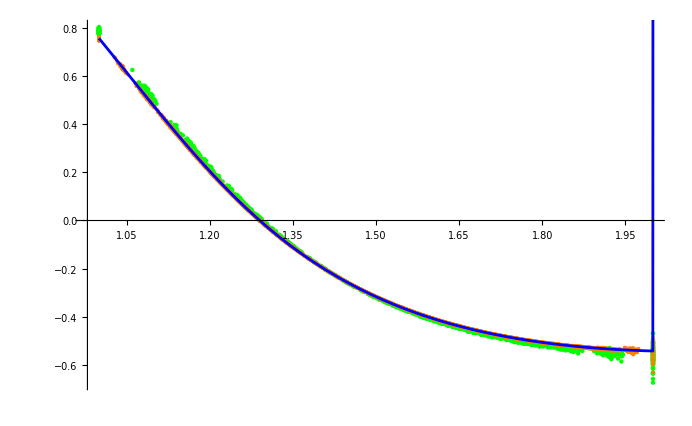

```mathematica
Show[ListPlot[tabμ01,PlotStyle->Green],ListPlot[tabμ005,PlotStyle->{Orange,Opacity->1}],plotμODE]
```

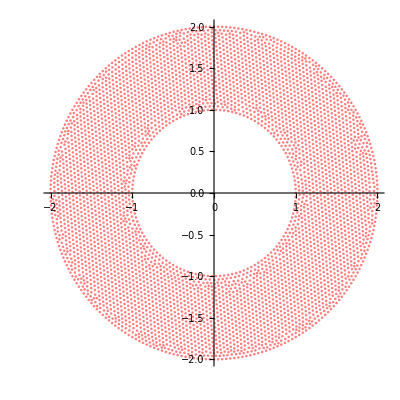

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/mesh/vertices.csv"];
tabve=Drop[tabve,{1}]
ListPlot[tabve,PlotStyle->Pink,AspectRatio->1]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabz=Table[{v[r]/.repv/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/v_ode.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/v_ode.csv

```mathematica
(*write w==0 to csv file*)
```

```mathematica
tabw=Table[{0,tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/w_ode.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/w_ode.csv

```mathematica
(*write sigma from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/sigma_ode.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/sigma_ode.csv

```mathematica
(*write z from ODE to csv file*)
```

```mathematica
tabz=Table[{z[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/z_ode.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/z_ode.csv

```mathematica
(*write omega=z' from ODE to csv file*)
```

```mathematica
tabω=Table[{z'[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabω,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/omega_ode.csv",tabω]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/omega_ode.csv

```mathematica
(*write mu=H from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/mu_ode.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/mu_ode.csv